### Recursion relation of Heavy-light Virasoro blocks

```mathematica
ClearAll["Global`*"]
```

```mathematica
Nprecision=300;(*Set precision*)
$MinPrecision=Nprecision;

(*qCoeffient returns the q-expansion coefficients. The inputs of qCoefficient[] are the the central charge cCentralCharge, light-operator dimension hLight, the heavy-operator dimension hHeavy, the intermediate operator dimension hIntermediate, and the highest power of the coefficients NN wanted.*)

qCoeffient[cCentralCharge_,hLight_,hHeavy_,hIntermediate_,NN_]:=Block[{c,hL,hH,b,h,countmn,lengthmn,startmn,Cij,CHij,λLsquare,λHsquare,λpq,Ppq,Rmn,RmnDenominator,RmnList,hmnList,mnhalfList,temp,NNhalf=Floor[NN/2],qCoefList=Table[0,Floor[NN/2]+1]},

(*NNhalf is number of terms in the list of the coefficients qCoefList that need to be calculated, since only even powers of q are non-zero.*)

(*Convert the arguments to high precision decimals. Do nothing for symbolic calculation.*)
hL=If[NumberQ[hLight],N[Rationalize[hLight],Nprecision],hLight];
hH=If[NumberQ[hHeavy],N[Rationalize[hHeavy],Nprecision],hHeavy];
c=If[NumberQ[cCentralCharge],N[Rationalize[cCentralCharge],Nprecision],cCentralCharge];
b=If[NumberQ[c],N[Rationalize[(√(c-13+√(c^2-26 c+25)))/(2 √3)],Nprecision],b];(*For symbolic calculation, present the result in terms of b.*)
h=If[NumberQ[hIntermediate],N[Rationalize[hIntermediate],Nprecision],hIntermediate];

λLsquare=1/4(b+1/b)^2-hL;(*Subscript[λ, L]^2*)
λHsquare=1/4(b+1/b)^2-hH;(*Subscript[λ, H]^2*)
λpq[p_,q_]:=1/2(p/b+q b);(*Subscript[λ, p,q]*)

Ppq[p_,q_]:=(λpq[p,q]^2-4λLsquare)(λpq[p,q]^2-4λHsquare ) λpq[p,q]^4;(*Ppq[p,q] gives the contribution to the numerator of Subscript[R, m,n] from Subscript[λ, p,q] and Subscript[λ, -p,-q]*)

RmnDenominator[m_,n_]:=Product[Piecewise[{{1,k==0&&l==0},{1,k==m&&l==n}},(k/b+l b)/2],{k,-m+1,m},{l,-n+1,n}];
(*RmnDenominator[m,n] give the denominator of Subscript[R, m,n], but only to be used for calculation of the first several terms of Subscript[R, m,n].*)

(*Subscript[R, m,n] is filled recursively from higher order terms, but we need to set the boundary values for this recursive calculation.*)
Rmn=Table[0,NN,NN];
Rmn[[1,2]]=2 Ppq[0,1]/RmnDenominator[1,2];
Rmn[[2,1]]=2 Ppq[1,0]/RmnDenominator[2,1];
Rmn[[2,2]]=2(Ppq[1,-1]Ppq[1,1])/RmnDenominator[2,2];
(*Obtain Subscript[R, m,1] and Subscript[R, m,2] from Subscript[R, m-2,1] and Subscript[R, m-2,2] respectively*)
Do[Rmn[[m,1]]=Rmn[[m-2,1]]/λpq[m-2,1] Ppq[m-1,0]λpq[m,1]Product[2/(k/b+nn b),{nn,0,1},{k,{-m+1,-m+2,m-1,m}}],{m,4,NN,2}];
Do[Rmn[[m,2]]=Rmn[[m-2,2]]/λpq[m-2,2] Ppq[m-1,-1]Ppq[m-1,1]λpq[m,2]Product[2/(k/b+nn b),{nn,-1,2},{k,{-m+1,-m+2,m-1,m}}],{m,3,NN}];
(*Obtain Subscript[R, m,n] from Subscript[R, m,n-2], only calculate terms with even mn*)
Do[Rmn[[m,n]]=If[OddQ[m n],0,Rmn[[m,n-2]]/λpq[m,n-2] λpq[m,n]Product[Ppq[p,n-1],{p,-m+1,m-1,2}]Product[2/(k/b+nn b),{nn,{-n+1,-n+2,n-1,n}},{k,-m+1,m}]],{m,1,NN},{n,3,NN/m}];

(*In the following calculation, Subscript[R, m,n] and Subscript[h, m,n] are stored into one-dimensional tables, and we only need to consider cases that mn is even*)

startmn=Table[0,Floor[NN/2]+1];
lengthmn=0;
Do[startmn[[i]]=lengthmn;lengthmn+=Length[Divisors[2i]],{i,1,NNhalf+1}];
lengthmn-=Length[Divisors[2(NNhalf+1)]];
(*lengthmn counts the length of these one-dimension tables, which is the sum of the number of divisors of even integers up to NN*)
(*Elements from startmn[[i]]+1 to startmn[[i+1]] of these one-dimensioanl tables to be defiend below  correspond to the Subscript[R, m,n] and Subscript[h, m,n] who have mn/2=i.*)  

RmnList=Table[0,lengthmn];
hmnList=Table[0,lengthmn];
mnhalfList=Table[0,lengthmn];

(*RmnList and hmnList are used to stores Subscript[h, m,n] and Subscript[R, m,n] into a one-dimensional tables. Those Subscript[h, m,n] s with the same product mn will be stored in hmnList from startmn[[mn/2]]+1 to startmn[[mn/2+1]], and similar for RmnList.*)
(*mnhalfList stores the number mn/2 that corresponds to the each element in these one-dimensional tables, for example mnhalfList[[1]]=1 ((1*2)/2==1), mnhalfList[[2]]=1 ((2*1)/2==1), mnhalfList[[3]]=2 ((1*4)/2==2), and so on*)

(*Below is how we construct these one-dimensional tables.*)
countmn=Table[0,NNhalf];
Do[If[EvenQ[m n],(temp=m n/2;countmn[[temp]]++;mnhalfList[[startmn[[temp]]+countmn[[temp]]]]=temp;RmnList[[startmn[[temp]]+countmn[[temp]]]]=Rmn[[m,n]];hmnList[[startmn[[temp]]+countmn[[temp]]]]=1/4(b+1/b)^2-λpq[m,n]^2),0],{m,1,NN},{n,1,NN/m}];
(*countmn[[temp]] records the number of divisors of 2temp that we encounters so far, so startmn[[temp]]+countmn[[temp]] is the position where the current element should be in these one-dimensional tables*)

HH=Table[Table[0,startmn[[i+1]]],{i,1,NNhalf}];(*HH[[i,j]] stores Subscript[H, m,n]^k in the diagonal way, as explained in the paper, where the fist index corresponds to the total power of Subscript[H, m,n]^k, which is i==(k+mn)/2 and the second index corresponds to (m,n). The length of HH[[i]] is startmn[[i+1]], which is the number of ways to write 2i as 2i==k+mn.*)

Do[HH[[i,j]]=1,{i,1,NNhalf},{j,startmn[[i]]+1,startmn[[i+1]]}];(*Subscript[H, m,n]^0=1*)

Cij=Table[RmnList[[j]]/(hmnList[[i]]+2mnhalfList[[i]]-hmnList[[j]]),{i,1,lengthmn},{j,1,startmn[[NNhalf-mnhalfList[[i]]+1]]}];(*Store the prefactors Subscript[C, ij]=Subscript[R, p,q]/(Subscript[h, m,n]+mn-Subscript[h, p,q]) into a two-dimensional table, where the first index corresponds to (m,n) and the second index corresponds to (p,q)*)

CHij=Table[RmnList[[i]]/(h-hmnList[[i]]),{i,1,lengthmn}];(*CHij is the list of prefactor to get the q-expansion coefficients in qCoefList, which are denoted as H^k in the paper*)

Do[Do[HH[[khalf+mnhalfList[[i]],i]]=Take[Cij[[i]],startmn[[khalf+1]]].HH[[khalf]],{i,1,startmn[[NNhalf-khalf+1]]}],{khalf,1,NNhalf}];
(*Calculate the Subscript[H, m,n]^k elements, this is the slow part of the code. The order that we conduct this calculation is that we calculate all the  Subscript[H, m,n]^k s with the same k, which can be obtained from HH[[k/2]], and then put them in the right places in HH[[]]. This process is explained in the Figure 19 of the paper.*)

qCoefList[[1]]=1;
Do[qCoefList[[i+1]]=Take[CHij,startmn[[i+1]]].HH[[i]],{i,1,NNhalf}];(*Construct the q-expansion coefficient H^k.*)
qCoefList];
(*以上为论文1703.09727中原始代码*)








VBlock1[c_,hL_,hH_,h_,N_]:=(h-(c-1)/24)Log[16q]+((c-1)/24-2hL)*Log[1-Exp[ⅈ x]]+((c-1)/24-hH-hL)Log[Exp[ⅈ x]]+((c-1)/2-8(hH+hL))Log[EllipticTheta[3,0,q]]/.q->Exp[-π EllipticK[Exp[ⅈ x]]/EllipticK[1-Exp[ⅈ x]]];
(*VBlock1用于计算virasoro中与N无关的部分的对数，为了避免机器精度不够将对数作用在每一项上，x为论文中的θ*)
VBlock2[c_,hL_,hH_,h_,N_]:=Log[Table[q^i,{i,0,N,2}].qCoeffient[c,hL,hH,h,N]]/.q->Exp[-π EllipticK[Exp[ⅈ x]]/EllipticK[1-Exp[ⅈ x]]];
(*VBlock2用于计算virasoro中与N有关的部分的对数，x为论文中的θ*)

Vplot[c_,n_,k_,N_]:=( 2Re[VBlock2[c,n*c*(1-1/n^2)/24,k*c,0,N]+VBlock1[c,n*c*(1-1/n^2)/24,k*c,0,N]])/(1-n);
(*Vplot用于计算Renyi熵，是VBlock1与VBlock2的和的实部的二倍，其中c为central charge，n为replica index，k为系数，这里定义k=hH/c，N为迭代次数*)
PlotWKB[c_,k_]:=c*Sqrt[k/6]*x;
(*PlotWKB用于计算WKB近似下熵导数的图线，x为论文中的θ*)
Plotp0[c_,n_,k_]:=(n*(1-1/n^2)*Log[1-Exp[-(24k-1)^(0.5)*x]]+(24k-1)^(0.5)*x)*c/(3n-3);
PlotThermal[n_,H_]:=(n(1-1/n^2)Sqrt[4 H-1]Exp[-Sqrt[4 H-1]x]/(2(1-Exp[-Sqrt[4 H-1]x]))+n(1-1/n^2)*Sqrt[4 H-1]/4)/(n-1);
PlotThermal2[n_,H_]:=(n+1)*H*Cosh[Sqrt[H]x]/(2n*Sinh[Sqrt[H]x]);
(*Plot0，PlotThermal和PlotThermal2用于计算Thermal情况下熵导数的图线，x为论文中的θ*)
DiffPlot[c_,n_,k_,N_,a_,p_]:=((Vplot[c,n,k,N]/.x->a+p)-(Vplot[c,n,k,N]/.x->a))6/(p*c);
(*DiffPlot采用差分的方法计算Renyi熵的导数，其中a为描点位置，p为步长，x为论文中的θ*)
```

```mathematica
Vcoeff1000={1,63993999999.50000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000497494862633,2047612690468878143908.13060049178594538061344176695207513695646579718349746420371916787855377812112542234938055424185377861445803212821954527800025893295356500143799789093642662657428102438783089784801648957581528880424340547256528,43678166878102110978031238057973.62367277899151462432900486608563380902040506448945562787318609930358213536832291319051969709635943282969416348131629851968311158989130732775044410889106453730269751535550102036640723579382741992930918,698781746101900672530740969673310906709303.6017084269343271112264582221468266876945639460924780873110908427087275357579771258835002831835310666355844173579266636046216951193807427843038879163791978850254591817720249843068806797078124,8943509676896942452457919216009794062607939426671232.16487237513508798005884895562350455197985578051259878121614270387455055638176329717233826643508393973342206951180305214995298057814760354594743165235471034957729098125481372745401,95387717988285971380759737139806571233935466993098481728774411.96212781134355624788686365397630292897001469393411267286671429547326411556032704273395453733884393097580442150666991729569998229051455916003586600755684208906943567301245,872026015263942923424804216273304234442151047290316620063199889439125596.7177594757500574127151284471105901891278870941259928425239125474337129584127450897997184556965144569443364930820035456327110021184497234254943023823839526381865,6975474753499064215617703552437356848063250834980988844750300467593548773614740393.583943464238286603485302351455706222631763709729318880487520639962518702374633872630125175694660285325504009391726761368821793815809563279608177377173,49598080908448284758387317856262544683550064900769892441804350312243853402507817144434356442.2219850505829163136846809157697101772333801891736018063144539908691366494365674623477990901949016328340526639835013841080921578808819772743,317393316909879450797205059128102906591580357472604197643976086897369340406526997267161909451457983288.0714972599749489349670861398174922669714661826205290609359653064661229032867964719131047216735179339811999216918285735921247723489,1846448896086767659915673092359304702952900109933156194162234270905868013884614414961604636798504307096714796021.37700823610062333746734213969006383479635471200508544071978410081846660591214702205650845146507833567236230901784868314,9846628206153946544805632848343243631768569148888444037549200151385903875341532859853795586955548841114396790409089182483.393272532484964532756570202022742143499602480434813787350272603463267986789964828519175803339337778705304111763,48470218289005361927481823327740637725456911708480115972333548784042633287907271141071864425714538401723657353596969495529928550181.6826215101438021056512553576827175794787780796292228314252902864210753270477764733889190589257912555,221552687321127896793840657483551933197383282250738224059552522776848534070059242574336604073727182545336804209706023534734035460662875777279.5995855837365748569174160038682654467706903050076488962198947776392885690320189995833838232,945181341140538933967726839777639103151298406474264173810091988457213717680202866105310368454355436927796099022886171939225702305615023258191596439363.909221075807354944099937966897207552593913777525568154561962574771684150297825991,3780278773792839334913698352760967294143783142074206161908804547643724649717873646794031009524548887975309558869595812611936605939463865491931146397952192592767.347680337359543046063426506956764625769589104637957285425084751581376371,14229933528425353243991383805953665004041202080408194272690988179179923144011887866715224110085736946361317374654030962489381362232067117432469677211199012170626552518477.34146882818860083165312736825411844437042490970428538625077916,50589178322609762855947007006003691992304485117305406522974736202318296582552225760372593370418729523487468079312840597330346916937249534003640748388550397904362967039306420822511.3012802200871407884449709983603144931253717485903977,170384693828792516660702932802937460746910639623499148894432268951152188138022358847232329989778929733978151624369196228175291191264542358620010294711343494465276982489668871535161246924623.9438598336828772260459586374575190435411175,545163072307269939303138362362763073808400455747468661686225924149724517430811405629080370356421650894507860402239301614792910571660108515589629344905789903092265618920100432799705959650555936897369.160559120708842191807637287407136,1661239610051875647928512127311178327522652651998638356484646151700486381636872258050561644888936037780350038511054977861281022962749227957211784786074812831347401855038136621852732047824118982332174143241818.135232357153799733849965,4832079081269575345679813035511808686985098522590249822172865679214675673252376871495619293748733840476815160046477307917204787025461064190713007267929256484265684061312893794032576682708388280680187172827523901684230.893606663838103,13444044084922232520717630913802862695247495564966231809172971582709065575479919590530747135878730693706592313888146774864859057347241519478189176063377934810585747711153180483837209857652805283266651199801095970488220048567695.68192,3.58460834187193440031942490598206117085406518327289641627126178643637705209674749904689519493413552188992162607454025150716630609315202475000604110051969187740277346680964808137424024824446656209192337260335078662893813329466972893*10^235,9.175379196255593146636185751657361740021480295722067283530757380565292016500035223105291763625077665516095991734969203584845433897796702256948731030442557483910429168334599008796356218258552542595976610494240355733764697094706248407*10^244,2.258251394734241376139663536397570286945685578259776348359375841749451398024651702222977482613707547852133174386291881305098437515247639338453180773721040710099958602195697983737027836839183409111990796022122588717931489531810129088*10^254,5.35216422408108684440155705208693882580625091213209366337044251437450319413349975829455877197603479247785575671620954234726432539060800254531301744867965149847164879011004880692135271878897271612648815143220498300443966256867994372*10^263,1.223183464283460381472674412978603735682944250322250839428728801834962443296507665284387530813227861717059603446159951283187919521906603183247254522564102907556420939823740976065127456594133452054890504425523149668201482860946537175*10^273,2.69906348516016572603834637201673218279834874192699914418745471221132129372228521226138190998842343607589628007030055696947697029954312701745686700115827623643351796807144523914490811002225966902631068742709965571586784415886571407*10^282,5.757190971518757137369793603194992550266064212547228669550895512229873150276523663956939926992303261564818997274766896290154154720365095565145095716232280216200692276460428116386141248915536099607956539293129216138228459388449654464*10^291,1.188411995179961969040370853974665052884104296844530965777363529771024267674825358113996254161226164535472788270093204231283890116854562485850967480644428872829177895131826123482583871421253384914081096154537053852170428618317029754*10^301,2.376481443541489489465733279846698336202130723501439910248865119002327563126245597009386883894405015361637977243746776107953841667563538757864867615992208167158759069159165686022940789478734667613730978899596753038465475891364430165*10^310,4.608261982910672307260862878718242032777727267401796468369604155356739691319546461892982546348493433985405267469666318997740619367134026092254639695130569852702447228472266630654899841638499555525435189724426417313816443232584992366*10^319,8.673097163023906576374070932932072626807233030019879194623411761195330654032959489139261297748841884395587251274770307766145503490147808896519834648400602574511772576611887419050174388056222228274801940767848192887160611249024756427*10^328,1.585701472146972715386862444665559681245985904746899112160733644700835801628584709346048497030130402082696499735165294992379125405399531494195255828298933256155591464642621873343975535113765911816548344127684473598979203182199105942*10^338,2.818600242185570216708133051895651006972819829692336174042239296593835316095613460594529813467260373983435742835389014589400566364003625894036129881891020681236804875591208714894606621936736299928218248302490077795260962876597130115*10^347,4.874674386223523799498173173671207106792592492947304279623184640062456709710364860511322714061316813471433835611266534709107010232985258468161211932552254171904714720090574492377038464365772622547151165860671304429811147685837042784*10^356,8.208714661725735400465702900995477767740544406966193454160541446516259219949859390785141153240613578500245903887677075048699156844854433773621788024584693845768493924217677408931653450815632995821360024305418036952711714899927644794*10^365,1.346861664406118357683906471201315466434612461742291833737052764315656701337959247633273045286375236105398611781435216747867154620605454382197808129547090925142028657712477150368475593846363432115917834724719903349615106858021140132*10^375,2.154640078664787599827687125083536411488062294352200459301344635954299388453406443820581070391061367648403859696081420032187766474995291489005393384057405861510383910477804313432570315087729981287343680866323519011810931382707921676*10^384,3.362806707284780738331760768334099240711434187414327848273022235381396330371283965046416296891721044599712597994738955717651626897595612588462747006616337314274204464662536810082146092946952742312851815034732928620950328661851492657*10^393,5.123455124149168308845784617456800330400191835423867311114055683251349198526668615646715106261085462098246776903712689179937319719453787859118112410906932677257723477289319718039817375430543239782066724937838130317977031516293058598*10^402,7.624372344290626272398022584848613855742820674239718177196114590534999873808529112643608729966807116782136735290573898474783781274108869238512047321355937351219090097724617307580410567108569324645305100005842488747133114102891538502*10^411,1.108818172691337534514672201839677039016407079299742443188725249264361801081895514597416338174374531062522540559956137143541592231912441795824262038586970256590597449388596017895051967010425525045571391426729119995132734383906784865*10^421,1.577581911476371138093549364294662481405876718905824768837788681248871061555914550490250554235664700933171614783952377384362007694733790023099602255977175896371067116646731171902937247344129114299722247233025902509102743620543068899*10^430,7.435079073791351706301128017307876361261311914111569702802678822564675905075546123420992796580304791630940648846495321492756169075008104141267124636134204478262089892749637587037711325182957883303046793051801195887982101551234654434*10^440,5.507776231765990416115753845933114974221326111503381854619696807845809393449782233508195307210395326170477473074491729510467760949776843056167875972002561301878994496073004900672574002818429942515920088524355402451267082460074027037*10^454,3.856659913216151816995501297921412621385986187212581207311169428786428173693930460333595385099289893251937682367783689091473917543225642737283491241769963788589211313075057867447083556722005787496835072613970738407734973436355122191*10^468,2.482674788154743867423733961017504409829132258450711760783430928681190056625937464908293385277417069487980250375411527202941950830406587186284114092517792265701486969729949448866318933401079290453156696865031961830246508408113923419*10^482,1.446021643120461660922306594112859413603189986355256853467944130618097919337752942625832335717824585731561887971980100409363468836092364680334679885199604193998351354131149125500399018345257869582910264100175284404392214575242303501*10^496,7.208512543793895586136618770669987524841565757721375531137112481933424801420740815969812169687499470729240473939747857488912057243244506323229094485178801288160152859651715462088270488822420774436148948920017992661906019982938242503*10^509,2.476875368447577281953046331420364204326986711991187200188103340411021372859044279485360558800800967794673529711056425814667776372787633600888576269902522971928507536791011317545719747252171069453006435500642575079643917841491334387*10^523,-3.815139171661019870203523307900514624062403531611881660121450802432698982371737368738938468583566028785959151062183882747135637287204492191170471423585277859025157748731215908864626602528626089612485050513783645191882520725845470919*10^536,-1.915298105069984703368819712185073751355623560400141389818643871478293403362560716166084196193679500252146910448657433531154615062344421154847566756862554366478983542042074133917871619430283371930518664006226945058516326688537824452*10^551,-2.531651812562768153612933052259892735286226849126585089116801521188569870548930658885142522059356830350519887391242848736710476153021201070105604602720665598435652737386250489808159685707110526537643672103866556445351303747218945864*10^565,-2.533799822138797717932451087557588195116754702143778006734607010998466678115797305628046346204770949130252503358067389897025997008522704079086899679416803965409204197052130534483105698629546489222945692354709257329131780839096461479*10^579,-2.171791781582286933923002043218789613497752796839768593465522018368800996563762681510063940813498971535190066879153120292820887942168612783310115047897931955830914299523746216226590951238767379660012579185656332873412697274289503125*10^593,-1.656873781032040773345989075542766738675435069468230189717650400525497324784416554131951586648136682988217634427451159617871166881627996619547633875296185706897312509074244161472560388095884895602529192203429428002714340554577627465*10^607,-1.145581633145028141851615352533890542027546351801991659081658541276693682396098134171145999425148213982607294943329591195457587136690155611207112998635008367321031396532691174082891328660129217000205785489842107064861039060239272486*10^621,-7.262455315576435284601588296090103890960481348576278952930108103913094337513237817867142079591468686515744529126894938150273277934637080256550423678474036773992986754851725384742754894827671684851921055779499077155601416966548837933*10^634,-4.260152322537751955197561948044006023246487902617808507949123434973623264235289434170209561810874462723262058776403107006374944842895492354310367217807893947837009203735716113924443600392221431994695720161695783610775389767852310716*10^648,-2.330089056180535947384217045958634368148476977485024814201023934163063423628074770869205619933426824857578252104165832819475860451770429751039200121992180354594544035241732758467098530599191378583505809133706928678858812247185262617*10^662,-1.195908498826173861932367868473349032977245409247485032010821994418038915301440360754935121298349725369109271513880440313369813440856068895278982191590550178268000231185399809531654437451286509244115226067183565959100831093370720087*10^676,-5.789848903580245343335651923114874039436913198119736951765608081203055271782380367397875024375511239173136600058952546113812344038615702421917083956181112660795542744822630061637133834215958222608934540289848154565151040331962175764*10^689,-2.655476540449565665780270125666229012119718285476217595912018595034480633821530512271375499329967885794757311722534566683672886383269961092554669185077963007862960172167917528611781391955925071839766681802732841810740662560058290018*10^703,-1.158126872806928400997827292574690901674071771899969181745488493580334007285864683010506431526700173009909200623341244234221488142580036142734825963998360830012997797049406467092895896744696780237219889559353436830012384817495528036*10^717,-4.820687309084249252855677767363944340618133243092616297889907646932800354928281699459840965502243185835336579457589942956212574984816704599899607974567370115769628181422362476142685431182816705966775720241770982396889244647414617414*10^730,-1.922746270546843746641121908771735450739499684050823866147711313300354337050564674617451174077075093187979919354980962772519728507514217077980547814305675266965403184439163702567065669488245771819211874113794247455454824481784863674*10^744,-7.380486983568373005892462499642453231220591750231016906493588534143542482044760525794589607516981987126041611578989580187884837850970195612850979897008493794040708874066743483285460894969775791118470122582368748702973706944212333147*10^757,-2.738922524368672652552531142683541476632932922726038589829732968420053528346775140662320240652471499220023439280349202408506615168995112280299237470507272090029402058969595417210872060815615555061650698466952551089862128040383976857*10^771,-9.869616700501764919840413874953910159757081201028765374377203824246421073326051308047256238154287680655286044841361072491966734503593143853320607439163471480381684130344220484768979708139700726354702272897459564411506563597208983547*10^784,-3.466008708023923719279402274187876808952083581605289738147546640170443112360295983101961881058452251564713767675461558632004970662825305044726574771604612682324699045227893138188320938103182424892633925522208788027814406191426891147*10^798,-1.189150934927920640981117259912698230788239166266134486046687581410247983187620539161700504695625327939910577813834801016819119150840896765700788339523840776375181787958209072463357085522423962338470061519373760695261010085914733354*10^812,-3.989657996690886015663179027735244320793297906477958019403360598367296866239522241228163119579071562171109525882834995805414913929257867978077496114849655755076802801577356657693437540249374924290379883151613663565056939671275388154*10^825,-1.308000154388235004310331713272412468745645342555214243685852760153854015279404909087951706684800014844768932306098129420701830646112725857907336264858529709079121000343924937449270577471309798557600378468759828655966165544500347481*10^839,-4.180077663571254491368830224043709396642609246684373148159015452964264956579918939703733646514933624752721275501750320824361600426919206862434103972153209820955927330605451501710436957915581122328732349745787518882237089165241368137*10^852,-1.296803234141860087770151599305682691461475996653661467012761053812504465557337012738949525486593489588416461660783679313544466129836851398772663026770808122196449651654464132166336610687494576822304078437484556112524691156949141151*10^866,-3.883567316609687909928078633382634389966852850443859251456038126714279026814620247476011390586755147217189755129626280456383248684901440758757570676695878261747964937376223805077891218093163050704700889214664496782551280840819514487*10^879,-1.114860926721263043973368512110689913295861850328040810213539261075608135707018896139038620896662554120362056364967277990872648330322860614748618164293843381249205529363020931508337400753266560966210721108372857597774238989745362449*10^893,-3.042306989258955440208511974353545322224736119030331857279788541818339836748530402054262568033788427303718269030744828423722803175003827712216020390711191165354135217698579641490787533439761218068113661896137696878054769901259191322*10^906,-7.810450717222511964797554912438564996747761754820957275050389799182492577838147279889586756760298390042768855080975791692091263600383952975918328353781716569803405637521695667226411394448809980917567827908539595503641021269140250782*10^919,-1.859934268189460948812501022568658608092265436047055745118666849099681814860027271221745638252511642375662422052783374929692130400568211105648863825939314065918308612435721472042438690708581874769003492436554525120959090580512017746*10^933,-4.016172140089322853090958515832618481667594626547391446727481448300579613521088663232379105833443640466708193638689775439060370151317913150472811514181828464408677153919531846036536696836121334850116566055971104278376296331667576319*10^946,-7.514027925788116268841590048245373477117095575126903421001249144733339337753398231077676737139335249299704047786741081059636417855079567361209570917958313906048822023770426544068524840715012417052085140110572240742112574424007673348*10^959,-1.071959870796805487912924585328248332095624463510706420361507964451090519026694083800933278699955186641697780008397355277579483781509339307720877277474484009140519094622778795156563413497479015843345127564124593142943002937884784787*10^973,-4.661476387518278652444307008837816713610494183656008408997562386860973376801805598502428878636267671006271357455421869618933563020436421179584399569977979260585950944612946537671158646295034517140854772172939014679701194304860481078*10^985,4.163468420645845316711408223592108329153499299152889594637356249371378597297240343946668111538016041937029918317238843461937660097294154369142156327030622102088884281583479639359427144728651416125322447518475372124280051467097506365*10^999,2.158997192891954967037236564839655733530751362479761678265052687385947751514000407005279260059979010987525818047328892086397797106007145602031633218877627398383618479657291215630909333998353907087731485556564624619692426736293724693*10^1013,7.361629981951357820465451576316937240346519741661475194758677902125977585875135032173162574822301320601275297803841085246376009035175831897483252735879164317636828966811837373465141764399132404241763483629056242119800260733167406191*10^1026,2.089351853512280239857610583681433861862388525503466730490389591422090594018774804336405738007794421838571658387078946725577453991708602573748371231164303199369044076295872148844884356060223400221393647556318379759641410617523996811*10^1040,5.258341151444392723449837245743612463876251757627943514129676211503654502936568244766050780029630782739508838150177761233556350753418623329598225598961628655620217320235501404485824475746521492588958939863620044044141024165928568901*10^1053,1.202154495518284512116402024380610435852975837309453566531585539969085815794306563367798197861848841510931979119549837027039550747765050770581188787348151968750021134886897156917341015178375403913192708666060432814509304965306921226*10^1067,2.517969900675081591490954966509391725632905039885903601463880617058244273117888910697666614581196361929604177749538135383216155004238477959760032928355359464020195648977877659541680230284478822985516600883588104671306237333989670125*10^1080,4.825340879828217897185291104871187369135137777796496596084047396673367001130803743710154105725793525682857101478861698418572156384051149493720090326335104625553942803524087685884055050953755864635442779957622082566950723536432046178*10^1093,8.358392961307552280990740254448881958379808262097010760695516650311766781882804598803385059776907954583521336285509150741886816662237081330630267366468137348786346405063861060307802707682329990028669252081158008695060610040139571622*10^1106,1.267883253836131976280316018626998962754498439486328251418013593491525768594943126198431631286682235804865026625057798914140546426948396258364545058560062933862432203833941286191325842069773944221175455037771530105290311522805615486*10^1120,1.543560632494259421436466398106763377399123914918372076727847008770749842371394934411872639738990374218556588601593463859654589928299941872494097238052176255776203250005280144243687737934471318074814128844268409138451167033874974657*10^1133,1.006779836226725815437750603317983258226461894218948992261572408677698727790405168764129319129908934599804009010116052950801303602608021306333330783671999108621020699235096273218575846954726980446302469458904234517050445141484387817*10^1146,-1.769640545613376376776319779361107595633503682014453820690259644326935714875848555043840504733676617445560374257594841880608352642789207713885738243314069155002202719981362049188569724767423985012766558190442345349721185587041390277*10^1159,-9.382990699536405178961022590389950928168836633560210583769007117672800310134846037311268257540438699662395151721193864818395011418566986836723832000521584085211336846969091232736480504162499988106688829133900213160619329415604883745*10^1172,-2.577999347647303795934116861846810214090469266569671897662164425492832735336802852623015382605581849316384868137030637476836436624178430138891087542265701090098856447000839721096030767217688189438760970799668207859089740201256878115*10^1186,-5.560452323313351957578378946932110311663494690117534008553150622935410953238000475747895009953179721546053553255076643296910322504205293644118273291073116752311963078367277049399550777923850143304500018864814112914182388893251944402*10^1199,-1.016305167632854500897301503332202786986009359657009731652322620008094459070516694867497051681275469642573274755201202368102459522542199438015250614114527200522487296817453580836717991483745672243912982626095175077497901572793536092*10^1213,-1.587127582026381123529277525104707904533472964178194804370133101697878897720643968089726961477954252772343684467648480935296886138205513028125675959911997252415777989936754361083693864562676100440414122119274080468957396459222209739*10^1226,-2.024078425687880916377993232298057664957536260733221003895250015890669906022480139754519087990527605468989063476951896446013970832224150724187975442150390407780356728010863431542880811713621275116652910971073586488473609572784895641*10^1239,-1.705731432586377988102553009514961779763987838669228373100730644712328906678403705394128494056036542387465700531194168710303423043840859629919550851458367879285335656698419876521814905996174943483026718456970478164050506564681142211*10^1252,6.31048079695329469087058333632278445685209124948513899423341201715602944087455207960710653612237383793322340303860847754471684071556444752028801515769779787594406941414178486380422214302461252445738048767140395616445990952613201758*10^1264,7.239412505768291278630680867694454791276276718020408747075339834434246805591724445136232985491919545349087273357110439215474391882441543625053793839353307505531469173735708103002739329984071498091429533393949293831375207308167724559*10^1278,2.179784574584052927886118684964822353420018455337163514745349697847897245824238940509136746522859532881267349609992782693281939705623299225645257625559273814234616935059133114666959970044357527683937612801912312849960335503849204011*10^1292,4.995758814473270824483987188682399168041465409751230918800376858131673940229815451844649796135936976922013243354361495674749147795635381854910823238136121900374379079664292015651640584796324722345710005904716000919419354699525652143*10^1305,1.000808170481413797470295537894415856554603331371914554788055658359457577532913809992590016518280973713670563529854338733246632897891149772890862404846921202765543884945679914527786360123880243897652543136447293698796430791774755459*10^1319,1.843323987400780104229305387316694499720549588958586256456756625911222440214916455170942502261999402929924881343875329540419732225440310386296135888249379629120114750108610888044354951790026908852252447488826596661044544589084947738*10^1332,3.203805067404589984663354320888008379650144334681883556510457325049575191458942382608968379297172996183216780323221759972342132565658545725356459427346956642825686737844827393901456884946830714974091256480577375636991461263469140356*10^1345,5.340150335256656589084867909757221813911815579584468338244082397405135150673849868011245870409018482772204192475945032367362762659696206433816939406474149580632520533704148123997287956860578579100419133707196980070758580227793114787*10^1358,8.629417646980841575396406881071321888820340307034229440931355652278561406288148025026245513214251391130739385231084802181833678070543121880433465954651712854958008300835949086687376980696734027309841644843870225716249085611847748338*10^1371,1.361787588759178039693863522973641920469898583515973521313267165745511490529242463504004978850353384352603618312860325251251284613128556064385601666013191333745839978468467969078905579398312047206676587044467743403183115833334074915*10^1385,2.10791381911121469020184023303679328968536550403908575472420326719171328673446229039356008207988752112705150162472609394639401248082055722219979547280770142116727808970892942317999147713810378488982634437224096016747894532993885001*10^1398,3.206987444893968886686782104127899705981677530776592246385707703896706261890013794617608766003438281027487089728291673828417517133275658771371066205044083602605376575234352254818364532719464646997423670830710662596437550338974645123*10^1411,4.796484992531638935990930082651264018484875488784758529110758255603303993765826177248819254252334031271167879113342870876811788206112028731421446467902756138310527858578190600904398949191233397491016862568126496212098714157761572915*10^1424,7.044576398466611816574354518271377996779750894479087729733458600567084158920896708944824670982384493915508592228733456062527916184585013642113848887289429347783451742176424663586888204165979571112643310478208943045352395339074933141*10^1437,1.014143533514561275817177672562015004253379039318971287893274606029099496081529913756564144597486947905816563457452202251905703855786553133144716941509066602676012036364909459243853145035950471407781706456287995451885889435860516906*10^1451,1.42803057731958806746383858584218520645571241380011050074074182652427187240878489936457422882302805788739613603431479571702893492595481511510278839490734636649015840169010695422106645120058230913632751452591954374913625389517276081*10^1464,1.962697396177972418362766638742147396242105568034869407443485415862336575702421342146354606314363569950738656540118150524077667987726264583536211587211553448820398882745728890667508089189308013913894341957383384497956115334337150051*10^1477,2.627882952272133452315129678716234320993835048620027539499688281224866284204558148648759490106450397162589488648131676554333905324897352734948078440514830260752880397223090596972192480641430446066074809232218766318778126689490615074*10^1490,3.421824111061804119409267188475775418199924599481650142199267163733472591736337360968120298784865451545591246490075892220760723427498188945914895975818237451425795604517037467855698516461861915755632641973383899777954749729204191402*10^1503,4.326876919364851968559567887730779512739294321060378284721834020585130838439388618440665057834081436404898791206736183503255466192933906864111038784182381917050850878517609917571383376807249370304373172520103332673375687712111084167*10^1516,5.306553840089515256760417931986778010331783222255640268638541085863335872868709593555223413923919944426519941952413711491766739423532917725188375337792254080993848194635744156936112602291138697811784980330350435360321402586859434047*10^1529,6.305147755930129521378619831880027352878263698139541745298866827714722042847956155712473536060733499080329582020856924808565238395046782491857989711907077794964764498033016215515246121815260512438603375388971669679083200039836559182*10^1542,7.250810074027915245598951204313751553005384033997500709449489463790410462744809558104382406105099642258001729413555572705111305987812978733605479828799852081281005653933641462135682850509001343026213945668624910785964528979831823965*10^1555,8.062304014220637594328673634987547844845782765904823160502317807730807685462005403699874311526105723089666276430969331230268804615215324152081363668018593405619480703296583185155174272489974399801086941378440322988338176543086101507*10^1568,8.658793392604309710174537240443437975618419774728410409640081688984369297676836698777989584386826738453995203177341255486808308204192779188754300689583900050705285300647463243094331270018822099966061522985406237869077079038633878032*10^1581,8.971185614898042874193203728325997155179101699217339804201599740077770699075605104329624835920349627007112516398498743054206530549126726210276610572390630909297024290382057984883919415740499730134764424482890532205534037780384941768*10^1594,8.952988961421453418994382306020362613411986521541660315837525389630440826239274869301430478248378175252656645353308030836974989988311685848771808904081386453507455257720038030527049846454958150306506421820683743279628130090934679213*10^1607,8.588563427722019246830903095248382129190839105790378369128500976887441905314526396604749234963150837986865648497188176637766642017033825191138594639124400088291940493606318615442421249031472167991242045141146043704688286429577849936*10^1620,7.897088514860998248302702101712652471965077760745560275165605437875302439955124745415519645919096488454253346612841858092339778460920914894263371357060397914170092321333024533031061845983727895419092718796985548601409502540630455141*10^1633,6.931419088839658405498667325497054719633040771101319979586215604459016454026657300086025399345813494297398708128617945738437220258295390828015463807325996832797152076052431618893246112964950895171874956089065148662390541853536668013*10^1646,5.772010082416383602421252279192035612197988027410825285898536353136568298743189285435354913220575991553729209581399840667941603889961816721055179122829512485511037675289471096236516175910739281699150012239293252589733334768346439475*10^1659,4.516994525611985350200834657147373058023620210965253603367346299935059399540545224076843489415162592363805428569007231756166346774826849648288277602852544943676393870823495807235405227079973051502808796324764317280270441888550419787*10^1672,3.270097919897095483143113509869495685421955638501290869252420390109850181876435594847415783164414145122887978329646156769848849554115223890176291180020470544091717493613768795105545616520440848575407570750143651319525088469443111222*10^1685,2.128287427089322127476486316075834705636110777379464565391739693324754011504956201568867309887836721057213942550044219396768160056806584047875295069595054613248208287904141636345489160104261685824398209241193720644555427854370970331*10^1698,1.170923577739138323216230921225531017868208149069300403191972319221776351185853076015830469347328928318963100490581248676551557072497149878310090936691159377206278155045807162529003604710047369886021733801284029141188866481397381386*10^1711,4.518065138889763310657946042283384252118422457510906032666181482376978325683170827847976832103672420696405030764535251993007529469010525118477985429121980550721808498155054882290694870495530521034966135420878677026717910190452694022*10^1723,-5.004153056539919443016881958921960648997437407994940538024871047581605188735302148540865336268529989569137023108161594699190012319454520655322463370571550704859737416533336826510484532551214374271127382782131742154552966290841771104*10^1734,-2.052863449927707985983785140909797122816428547279605857200849908782847386298223452540545645342415558042399575943056809553905105058715648608868625811894599316696622456115211541875471882783292111725613169041683605463307771537268294329*10^1749,-1.809310962315502240604836382576978280604523348467780658515799407231381806148658737270115118815911554059223417741119976481395419004364627485218856718597978076037785015081235004926511485718662943196672775244712319197464664202760108366*10^1762,1.681980787950153438050067743988161066904067332023124304337999137686664849456028404753083911563116483237687179408910815628096626846597527951069874272607352775983534391525708010533215427742653718194412067934100893723195601048352098747*10^1774,3.259830390668097542457678893453041267268534924905917408203134686326666104979741593068904249417853504375396285194731804898510539378681815732408651031544070771241413837289310448546132717600746547745547656493185598867490270290116556763*10^1788,6.828786381586201441664440907035667158235322148618521002242560216500648086417222358989878466536785820027870525385259586601028620613864067884982046565882849983635948734961384526785271694873782411311170394190673672759575522520791788637*10^1801,1.030222984139745546007194844072298090232608212395831598473723642010725157724593615864990459083458328507335505220459718284953972127899177391861941567152022492844953514980468320957196841773761099550728735057879019071029152788598448972*10^1815,1.323156747558564426509257834323662941180831991656357460997874720625254701134010561840516035195478301197639629475375588805078333964306721540724742497235486401545922215069800169534631881192964170151924419749645329703047522834508575165*10^1828,1.532563673108000901457579375144267505036740987898426710179907948555663994594452694916309086309025099017647686098088319339003806658548923428662474895271741942651236012103724867115006223606967874724389135718853759730385092213727614255*10^1841,1.645588835389925747446305478320816254209320049350636684650851574863211831724718091789713436366815146251970086320796832622129987888583701337819213851524030932637404262207917030495134627654992795589082396297901635526383432838898147108*10^1854,1.663770939484802625508479043053903362350748944291994991475816189156269433801053188852870899548861490174490251507603772055237345543780867223027821801570571749756093925188273097579274932921316754058142400441724582520179461633936298123*10^1867,1.599552671391185709274551340670267867842623689321207612383168730275942952105649161959935216497958053710913660004141469528963140972985802326891086098183175504104910236163796806805584611611786888289637999875958221540778143008439764325*10^1880,1.47206932622352093999168139946271196694769819304482845301044505625839640315286862276727801722410880927967299670018960197438480392944400918273512411556161907505724345418090430904512956356241627364010119301726436651819872086554144709*10^1893,1.303045636289632677746467056489630174895496239782513894916269843276991707850316750611249871391674615244131474339422028169998141630834408036723913685503620360495248943545624012846741057073458414719862683854544753668541784111049269919*10^1906,1.113411955368374228616208574848198663575164202287643078357639077007346856847067273061774499188005902524118253904716714074375704283189753856245705093782284955471197072162396851566899877971317129092398766980929750951195066769063289377*10^1919,9.209666891324807000208092709474237940777039909193118683900646141509117567090044904149293561309528522076473898514759266187504636789219013460753884301085408963127232066309147077684409812693566592146323139283007354999889499917599979769*10^1931,7.391411305482686764531840344312728086994751220546893132190128662693169867954592571539069018884221853552866816635363555320804841736741804465775369599675931359555593776222350864647346167218255303981617599729881587516996150167301191835*10^1944,5.767200830746672703119782953124974976540504760874648486329176000459637486546620636278985160471553673302224854327193584513838250215225005887809280934606125110065837761768360042031933010041472881749054462152831183020434105385059003875*10^1957,4.382589703918524520117973131546739507127749273244222254867286488161229387396997927771624404080408491971246597113908561061331160947937686883304216908936528419728529073608086083069573267469356276025975231271622519823632177110024616236*10^1970,3.249095860215357617209149737140401857557988866044246066714637806112440534797848050751285780904220447949708179622519122269323955748436726234409177910693160178743289975676968788100354364493770325606839998443599958477120339457774593636*10^1983,2.353991676824222190969407100815463378185412443798542591028530195994752429601022397999627295766297153420320060043404074968823933509059747842744120221376052570422635914196168198639346040440154753246948678449540254311814836143242058742*10^1996,1.669728718892804779058728033986777274665687518694159250633023366609298922383451052200946278617796327360534398565766532208837074793600046350048252567601643950646309656021203653113632870866012034994689607035142993784791357709972907791*10^2009,1.161834334444947926558141595849278556325111244453597162184493204644483650768721288610455474347849723426415006979095385198168680703445813252133022812727530808005631129380298339108611712888532341671113683512540951436710118336514417669*10^2022,7.947721956453849416130078093499124392952119463166063264000298185011733868846332841617871703193964579548093528643910919846082470726304771406368520811399268813569943871989042001249288468233901335109509675589271514428439256766537284344*10^2034,5.35747440056666097762668579530089302647975084051482929733752180566409727586021482435534275020929684907350383822867850841587037455962828423133791311989021877761338953258449144064476187645262593200362412075044499112980758936345366259*10^2047,3.567418460815485671506874280404319276153120832794498811483076382113616723311146440711456351208530969324808065512046947384734525322576079805864100551562388439302495275897034252264515227184778491155723968342054680001584636403873865291*10^2060,2.352074109096744029496988075328697059307951076356454315223118222333393647353691110866533788410110677248181319317582678943799604428269499662994325393246581205542312754019782483089748677123980998605645041549468440398143297060388364723*10^2073,1.538682725145220942492152675027720042768240182678440436092608591174840453355263037230483590658186890031885162313083982401320157305205729100305347381004246952287739918112833392232777828451011344580805860919115576017484584150515575988*10^2086,1.000253640760847581058252390249230494751504894355850518661267453348875296319908406387252973584698838198853389103996777275560443457424681227396282067922158035604574632324258580346122529210390619497867256616630946350261792868041222245*10^2099,6.466482307398507024880945417836423819128582743701456608642862007491416250195510013828390411735513804811664085788181898849249687470096823889920169081838032684923605101361905849984639505013293319298906449834929830915443205960431136807*10^2111,4.157013219989384576045726522231007962087644854598530884315945424467447466998985932958467153437654333615068814029541125090338997394290363668561196311321821747157287341692957839625731401724167628271886389512661524325094216131892125469*10^2124,2.654887744121573781100464403346689378576378438578901996346576315286548876409532818932455733799222697580085789561592832384096481492502783411007859110713681808556919361516326165517131295092632144219149913579872257540773398672830777829*10^2137,1.681767814956787869719880381002539318617974265628643519588560741097009918378689514262495957016389108765447510796361946537225135123354373507874546903907058068086144798555344234189701718005438151079280101822348822982892828433283529418*10^2150,1.054526730465532706069693287881109434313586968359536777020175800896834226464558185530278920184450774500452276680726099950024396250433507996553064170228615663843146227274100541317172477537521019978861048220709967257758278629908779102*10^2163,6.530737574753518706342019221325556215601567416134001815212571765312314919730829844444754705347015316954547424832210159710775070027442202465020498017653483475413377156968379081514030353676663442978004239654566011137594307710206760686*10^2175,3.986034050843221079554712493125154677223000297072839527423761686997882239261421159702354618318286282628873903033756202823062318936490377917210896835633900545350836752288282420721492536098016732621959179382736689975178416537851826255*10^2188,2.392984452124431397531324168837105457750849743236212892687785648650573813959624966822654082569646238634309177206428860642575005497016424696840305875310293258586983042818868669776101158007768480861773086201116120886166650383768736627*10^2201,1.410665690346026407204084496239925786121878430607851275003508508589072755912365895281324752273817990268928299586434303244057412517230555392534861245693037478343465293350024100239959791286939239512932521845528508851946827142610330447*10^2214,8.15430762288152522335861785975599416421825496918030477589160160215338627235170368481047025690630861186002135164188882027484768626017641999089242923214675386546835763373768431672793566696851059634094020365910973772703383999086745702*10^2226,4.616804456315363797449837572784736698282991241435007904468977196804526403765602270533438742952676913863438152282916122615126449147987087603402911867245278325545720474377436187439821537469722024177026167972723080510333980403236204992*10^2239,2.557993498052706562118750773385405371178173004387915436839033784124302193867858401641326847090726565606211299120726655605030139320158944071159671127675700180384847037715484593119035050821856220639275117324202292340384841261106466033*10^2252,1.385948651404609183961648365143633857060812179222985528770657154341755774823100279561048318847224184898978500725039644782804683938427623197841803498512037682580407737059238022557857982810683335442282335684865727427590739041011712152*10^2265,7.338652248475092717802686164784269864084770451032841331044933544732996288638971103521344811543872787019548663223393193262293691439875927600915816399526213804261008132382173398394999033420066223018558984990497048586904900594048248899*10^2277,3.795366041020268696144851813354485213794127518042618940623354724025382910626675999928241595223931042604007505040497148039800745051416006283062375888761091686544493285445345883566845760266397337091349477539360481022438747417925180051*10^2290,1.915965715449523964625098979760785643333979154764558343553323335391275934258105725600185904172255705070814856500840001093296661087119339932933986253713540051724737797720058217488709695822538657906814235636214824044489291414300787146*10^2303,9.433887852939419732279121267715691299278152614947005161275297064238970649164447977970072336214638552312492783108529025825585723397420325178926344758689145201843438807276848429671585166532502928134855315232085419352937631845100945123*10^2315,4.52617494049817790805522989711688477318098342976818515446021534670074001032215138936058513747831203146018106372800924250455498511863485228808878654651419683056761760771042529477321023184931350441786728648758833581250931430895623809*10^2328,2.113057572053545439317943338410781559352042018143985131083407207474700404850473185981272963275166020581555600730684652979462391026087884642550082702142359062767958530850538860119284499100756675937921118064634798521221400502361343713*10^2341,9.580141584326813995668152568209854480852307964939781086102792535662282954556877558288354916710068589234991115748747971097365004151031549259860906596947283662687845219404176688786741348834377170611972621017133433168719297005638935118*10^2353,4.205759228543063920193658818637400107393894439763776226835042527901711914057776314890739578938525667403304359320392577247750090522936236980767573334259379504190966186916641908073925911514822427198178262054001568548999496104428433027*10^2366,1.779877023239491484707542084152867184867309242035102499340238911847863019408884557940587968923549536365979343697087801332977035962655821509890228367589870228183245260660834282134496353179824881329513335507627065871902979865825676793*10^2379,7.209480930518838964518212122824915744242660982841012121620790445376207767431881351246075325739207750164429734930880683768718793757509730470426730023132380880543229758590852020048190547651449046168673355094398125922385092211946545445*10^2391,2.760958974616900041427762925458128477930538305628709666366424707600166819319937784425759183372922234708849202985383466013408050000713265622631326852660853502999321673418487628649366983087469014285659541662033855690352092940757919765*10^2404,9.765622878021857544918961869995442789747211505282928657787522837104669509579300331367774265321926627664667345294361991882384580523399704514264954073642658150113695800643978225788373591300649819825448947463030683944463280282370361502*10^2416,3.02504568712937317254461330596290396267407198461687651816527935423009586079857098432977971574987755426833542091739908179447020358029683337743472007082369347312275641155130152034571555557828442011245008411455646901633923825224987897*10^2429,6.913128427797255627826600594684515265482279199512324347488708219153303740760464256342088466870064845653342966797245178509888208906444124660671309257941884489577046287775821880502102544911754300113062465277815116761556642400884798836*10^2441,-2.676734289685666468547738505699489425595008197600454715855586479690464274033916915180629508608360316658057830760466740531092448056042129421996239124551739239980409776199252757248614051229901083015142140561302890975067262838387945709*10^2452,-1.425482077292184047556418255788884325584709710164901886355823278706752035782902756833257109565139634255155895728465065017685171058988105397249882188344203941834680544288912153600655815190870847494098846914489576619341598220096435957*10^2467,-1.25548590447365018366581755449581313574887770793016835145167684224763774980619350685830881992395172275885834537279666091692242905525164392014479273398150456240331118941939781639949358510833742285665690149901288504447194478052906634*10^2480,-8.22437678459636584229942237371749827911458538579910629312251062549817372165876933511337999424683627119792788110479244164717954286384974961276559695084285278939954850012928436216831760853683635180814711553414678119637220196778705163*10^2492,-4.742145082919215422038925962326866059395719775046895748981442911664748543962359861903120521359340297782247512697040421231219463728011195346395389860168601284456757953953394825849270356143093170532080963222135761942809288331311835153*10^2505,-2.538631086205450528984988526388656178742130503183039882896687620564265774958300760175099790287280007506940026448910513489221423970990480093093123696459818290816652322048018546578333719194409845790041193472240433464494914730448003471*10^2518,-1.292382138737878902470518257063471102744806132470392940744941914517175150859432660533158109180293402347480731684997598856565013191549649980419294788131079010356949109950176454564051441879999062904542005517149838920203144752957575835*10^2531,-6.337404132323101397288074910720616838624404460255645917560297764411773903413736873748117473167782764701159073680245918943883945343247929325143666823436832873172801509804185907573740940536688971388439681680219910702728716143711080236*10^2543,-3.015913913616893319433770922020503883437435767242501152170504638981578791722679716204380290266261356880701896202987595188271789444902447492471928125698785256830713436113159611546078280674831252930708206514987530890430015020692490093*10^2556,-1.399236071400422512031552076543289337188974119222832365339621280417272969398916330803355409420810423459596609801674441212044077230844180658928014126692649579535318626101412786735650039345925806397103884797631562026987926866616338931*10^2569,-6.345994808079909258861120577419925200132978176024490193352708366059180541225854206195679643114374252585437405747457751086550078234312054431693397884653220501620577595864888031530683111108686568646845949288753540083856091759721543129*10^2581,-2.817450602124502012132310843788789492131131188151658889861526543633102693098323545778061401430061890264512194444338173836045448119976668712890808756910521598268209257641352901200158184550420975768758500588759495807290340710108855416*10^2594,-1.225025881628235946633641148481539024550771845356369896289722596206373661109738861023187273909736650946859494272164310867704558453136200677592665035870725727567024947054302510774820265910634947041609954988317326313829012847507848149*10^2607,-5.214322304640981024345715749526133911773858347040649030677040830114314445346611689681066137165101464496034681816014371509038445915530573746056120127883112610681353498235329144426648234727456340393679991947135121866646126161366279583*10^2619,-2.170322001987408535841473282411007961465814910684244974408985542060543201291489450324468466021382007728590427322256175245505748222888964237658104003573597915436414915024001818376591385965589089015367971341621139878294159629667297768*10^2632,-8.816703317235868772127319374622014764208962167704836903782400271685524410842633210564362342458650239345742079080328715247152571191693730280948038283033868368886280551426367532784587457406468286223274036053555986253717335401565441058*10^2644,-3.486125768703882689731490049567285856848840673520315905030398716892400970514338036155384224338863340283200187887413911762744827658457150209887693648757374886389760283606673275657864758273405739097807422949287367116080498660032970124*10^2657,-1.336349833433563359145478555266714506780764269169979298407620695458930594546376116564581571676601750360958222115408465617120165112512315273456351344579160760503364219477637817532454547614985955252142738795017863312077882239225020308*10^2670,-4.937892823986855765499082218451481652241959053555742252878325736681332422286131305248795959649438521528836649396109934115975118165307374434873890803823015534842338361900029993325640268665423260167972936792807266135599450018211145772*10^2682,-1.743316595522135047712866895598482111130142991268701888235706787682622663719669237741572211416320551267888259971091061477807317375762648874506562367395032422149487371533066380233114481416843513686611443789125900037458322741633048571*10^2695,-5.794533624650697135180922309464210737525331762740195418974661432368231992671861844494603644411409069326674845505680697517104518490137613937861787272592621192034945189266686629155426513732736919965974185721101055647157279562575372792*10^2707,-1.763133032312055569425644537263956240747064831653805310334886489793488907086418121712284556405438528453676198471273770387993563965157456220362632910342437707146161924388649728677252633670600708059414766595003169442434637773954553463*10^2720,-4.598348914667765122587151948174306871689571358684627334931353418448291254561193273078925734228610766467494031255560567792497581197055867486512864133574376036652165690927067721385442345066355690273128266883601720810743758136988713552*10^2732,-8.108012035174434527829562928517345723969792669525626801381511601944932547326354846509964098386091770457135608582924417853497763757307361123246770639936989852746128481409411918220203486685491260450103348406885180492901055821767982754*10^2744,8.511620226068960276991120937308055298207454409855120065570365849696153828138225222103132989689667212192103875933370357888112082862505110220904565491466065666011885377290062359134213787236884307983278157313083255203972156163200263882*10^2756,1.887588733158774943524015204499724094128787065899526447632383101367410840873691547782731563300030437851409042798462373799532068339465461696201591873029137777015789823502041701931501877795278246044088062453885285833823540436310364362*10^2770,1.307631603063640975950898164400643661489581173461383846175455008043053936870125511045673467140360115776926538803105854763400385986524924141518624558023257304257880732442624308478977129308174968730058477725962878206677052151327763309*10^2783,7.078762434623137750710129074682708067675562739612543775344456494059375170557477839415295285352454748636991617595530304334120800579262904878748470582233247393474399292129911570286520437705546502553707679154341028576569696557787793225*10^2795,3.399325303268467303395487246354410114783254662417161371934496741594440213857319719646925891218806567343088095752401205748665970475152200566707802747435261592508552744904951693045007188431707442774316968034880249365221174797702839502*10^2808,1.513150107231884426668758510843638730783542286527056353535713461651255259498949161874208353229333605407075706946154485046653804698637739775722881715106681492088728466521603804585540943702479189999408704785694074914547668850159557709*10^2821,6.373020128683144697053934147211054202938161099157086026987957016120983263169798685305315772466037614499571145164639921557424429782305533253772918631241326813329827081247394938146013796786633341612455811045146605272879314547276321206*10^2833,2.568549969316786115797548316260232853010041287839618205315094315483880145498516227234472270714609837418993938771451083018510074668910358983630331645709071860717005086178378002133817059799603431368977603419621035861507859837800473682*10^2846,9.974815793945467774712024210620376639063121637719628161195638117704524514094441057653798460837835183878302419704457125278442510193324387161653765354440597089840994416299721236425656102190684104776144710346038635118264260886176899353*10^2858,3.749378683324703733767553304720695059473796819350226813110657666683130592190078745027929216875737974719074047866833375019465536271228377986137465062075636149773822619396021955385505386334244293603350415359703766349124240690337551686*10^2871,1.368362206459888550169557597953189048094465143949382551767426996110620916367509043870539983553011492439702527392669948602131053197807237717033733492739970481473128467210125965566594393579791224443191850291585640974161098599698904332*10^2884,4.859378254611109289686748464370211576659492510736036934102892381442902335940758485256849141793739853756197664690510500684254497042326183337124857435642022812618304294803866421235701859268677145824271418590190252420486050864782317922*10^2896,1.681753623888023991946387552090464876012491521477332026077351869262414074013049247028522653963786084778113949012860715484086240444837467051012208965625758250854497847514156864625813481058913978508838546062596671540582175165112056297*10^2909,5.677785773332676972861098403824368966206695814379838715347884437416383077792119630212272346299986042039737511124137783268880234653505559733493423128041229410786436778891423645312521130919490236778294893281586513846336860049426895557*10^2921,1.870890591150466028560547560153580804099994780981734707265439123650815714436596638820961781118821237439821818268927324982855477352859489198560347950890385207242344169081063156091603878169477725839534721802491387890158508646927920144*10^2934,6.01666419552054430618614880154103041445710571983047938422728929575197362436413239348402243984457873867270731186975616308114890843289734208784915142820815978913808860524298643132780584557454591499048197387349517084460018627336212832*10^2946,1.887116127289765246395637317203995719919809399781288567504237446771625153437516465670124340935032413927252032940924033814738169129695552677560314350260719508079568147352513809383945250702865897694138908934423303294205529468115787539*10^2959,5.763384030678670563571556648580565531752325605485520930442098570027938006066438704740873366413550844359435828254353484067902691921917448603746961275103400741203970690142613308873938498930818723506454533631184355233422459919835407511*10^2971,1.708818007799214105790442902539137820613158800611503015927316237728849184733000106025046466506996786723199366594966348204094848237746316602990627136896490783875401437664492455200243645111293370087122787787280341622334761810572126724*10^2984,4.893073524062579944043512928370654220842605160749859797616007994975444154949700619202176778256476096566834153723194297771314882462380570933804383114301994943011357669285901881234008319289710858254781783089833462765713425029369228805*10^2996,1.340669735071776991075275565652670511808762780064308975603881502400879660101729370091041814671032740223283822760773059172449234022269214075410416018586808785323208985651478936572302293527280406152761237426105988148178641227469361036*10^3009,3.454603233599126824689784460857439160668540450299469799187942670823702596261323931959962436455530870539796768388803424786654481684302253577245886004225954536264472460793342045381103643884985231106884345294508182180201181468458517547*10^3021,8.070493435308863262539418393515412356944036208484922513317492630686638512966321671955987404201970436575649737114589037546219643293193256092804728450769370960530143550241585896582166916424221893739183161002576094154474624751168279501*10^3033,1.548378304491758306543007197560952611001594246062702253614550978578765583350906443342087883861498759147249228211671695931085450162637841936356875606583954641385416746548269968306470702392690131130246749659043347414499212462695882445*10^3046,1.461078885376756630763453485646289733477340540688546640717648020504047318646572599582049578865935135252467030836460817408944594599226069203734015726689420203685455195267427999884563389893196894502654558046928574312027363634744549295*10^3058,-6.857169177162151704407364857291671199291518254369871573863987272943174084084377518487994671214280526457150224594096299734338128860032273360143741410664363966899312253670042240730489392235921690281863678278196524818917943298086289298*10^3070,-5.916287425594569988494589376097212616042736354478013638914333739666716104209289031176800656991009774852364385912907805059130373432163208330281001076621384273771661879807909274723320504771427871808857286175638734277365009771140887383*10^3083,-3.066715394237455158488091228309025831030458930921063494546733369498251547787438679945121325317711168969523721280266113124202539006566885523801690052209633901493683502322379803120033887543815659980225141688690140272534513888542714284*10^3096,-1.342045775845097014981764557478686423585045816084994180069507442095690939685886523473506111314308681684956674894519829525801044276900648880766785188061515829048185007609418730173142337968966429610868805958344661229065697290756751001*10^3109,-5.37156923146655838688554871420145801292329923054908801206936823631118744369404785958748098685928912120382983546845467711579709887498639938478441291617256774427620449669253323822936330778778156524412473806417796718514322634273728207*10^3121,-2.029643457516982425384447417907245349365515328065609015841377426012563420994558619808145873277301455827755975118365445097586174706747821677562869650409589691381655011799604469847109290122077534340136505769980810824529650220298307712*10^3134,-7.353965697777400591817448207010906625491664329802580626376646218133104209720677748959495062259749390476568211947813381710281351801551034520536678609593402900075718066895047203742156655015559092464702092531278081211693247832829770183*10^3146,-2.577735361144582346904507364301409596229947800535167052319693023604887204383056141290701669999273437836339143509012341245114506025076307815336373122343772353506456319867940060641356633066607656165955985449215526518874036360985970879*10^3159,-8.788769983271102026483412081550911817675481590369366652362178321201079671391934756963593658268633860982777319020381257525599812977772526928867883694829584306379467986449233625974945935074312181925896646289342146345913425465850036487*10^3171,-2.925103237532407772136634814078410448443390370383630149745897900294813623900093489310223490994169911249661191280821506445591334168710509034311366468003613475477896121217633912365442079358085783935731273384769641588185289888486664213*10^3184,-9.526927242398943279586744427342206256348364993507737458720589601323541118398745605690858443236933984846176899536252830608393654530694031858721740586949473471921164701336920182637527123035478803732588477900640321291291500330570870612*10^3196,-3.041889838048185288703384371696121612530534057131928746949256778162015856250650245550443411172357878722265497908514084243642993397499065952234338483361915726210611402810572233787789785114874367757260654547309123316980165519441551626*10^3209,-9.534590826179408903566571512219607118418038399825868060299219595215603377936172235737947180043328924467708488648048547536215152437117986841847739949908217014291919615989010192796143722711819513895049505884162381040034959843334579051*10^3221,-2.936889481901724887139293662035163318105237615330858760522819380287842031706843266161998956811134956806802075731774114940493733866206284159660643357538091451840943059003338199129568311302019361986731816397476126109660445854305347001*10^3234,-8.89747526402629280039934336820356603782728685708722340156004869571062243437400987907910447900387865168419232385047896954388701388169029044084335542385544790880857619197256388998980895981293174575271922137613971102462607304653492829*10^3246,-2.653000304852378959492891487244730204372566227042829120596779230994939930576207278198107670044139639665989697240653064096214031438032039244969031753144696511735661642953795201014131792873700629986323551378978541044898510832669477116*10^3259,-7.790090771816130100817024724347053816609717273015940345081969312073532253745500516671009845407205730700329799446537601257329149309447891052509208545321529900605712500794762004466048200217634514814296551349632888711190539639373157169*10^3271,-2.253621266255580211225288412541307336816866683748956136639418153759617913772151186144539061224299627810559057711858154211690468475745833302658662616339235540538949308077048785864369977263839030074516079477822450153487871112441687477*10^3284,-6.425580682126147217561679738760075551693685191690380611498566869842389889023351865879972431608557542736473815306982548298628377020327529868189539474033491273830369996078953132622472754310124319411719529860454174227152620260019891041*10^3296,-1.806186183975187705009003478538600472167134245744516755171221988913071079372777957445672247009379432176956022203286834414765480530938127332489536139299922929625092726471793546894967863935669858681646469832909142480140178136872359718*10^3309,-5.00640957372222372628095855387400257097792638801086328457264652496640219125534067311843280113473202352466427068580347218224672973705557276114340025410183522331593502146225401700635252239493102382758075456282592581065706617569612108*10^3321,-1.368584662488887315532925138570883208603452398314064714328028497084602106078336961861127021113300139031987608461995165823167273223305012189278878255176932793414422084242064734368195957977554487528437677459259112445634538008259580652*10^3334,-3.690133727675378348073441516822485094194734457847274237651234734737789108667233728326071608734117017351273654516419471254929347892082282385354390036341879774876772075848386321637818906144958758645522766953828280062207630229512494705*10^3346,-9.814337803078614338687591294270508327319770618685156872228419111355612492182371208767995952194463007096353397248020373966611998170141489889099328948956868834460682210704853321726949117065828200188114377509231761468215003535966869515*10^3358,-2.574750912268108221464661254936643611678984509031999149803839718187151804792809714395114728919797145808323379147356330656179736038085782714379799330095735648032071886152572464377959020329251662040177740391596301309197573839249385757*10^3371,-6.662840942969341203455227756073738136823473299165729119312929934226418697117784245759233097303524305060914699552074869861770423457607521716646677921043055311427258262378186955300546405095098708144376325298069321508630485350370587152*10^3383,-1.700672768973869552579561508978021484093612442108696109921213819131171228025939401950824926808900882557133695311128188666733052666061500252179766187005084345053455404299781825908262472551652025911450728553155685905092450257355368451*10^3396,-4.281573726253755140989399188596731834296491317817086697779256606305919671631747249152310507749021268197372878973206294886644115166394782485668440898951556308879327497778933235906520615548335990135433947648959436788821929490458076848*10^3408,-1.063148328703404428996610410694678920182426008984450840298205894102574174508813149010166488258770381640474010899157397452615037714834566127984050921367392222568726035941651282850739123930329689421140787684589029676332606689648918013*10^3421,-2.603668376870080695820879095047711286817371343018194066819393222668125969531879056785547838488625447306244351202388062571734691758508714348156609795388926290830241460503775263752010948337264832225988239339580341944671381989212771047*10^3433,-6.289046737260208496827319478767562870754431367511797107395963020288714306919090864410586084323080696574052843720392130428794371364385332832252107352450849586779462914029118513378218781108902253587457723983712910331036377409619422364*10^3445,-1.498355838664060164342536369715806607317522856943809283166761534315430915511630098512442517264663021326344912230844611765591766484299806240414916204015684317911395141348244481986268588078883264597473973464924904199620821137112408365*10^3458,-3.521461416023238674141962793103357701017286621229206838975603759157339595488938650165425815822021186257047267494153025054918782435773778992854822370532168103640353464325836119713921725380215195790197337091561199486795622021495744743*10^3470,-8.165535018632551298542381607441101557026766567448408969995879931832790146256940596428785495625978141956965796116883450541726453858024112176107702078932382254583583499001428980060311292645549407042522955755582165341948482040393222342*10^3482,-1.868579067894399039948963363787487213991168540098230308010507104320733770869800693063378130219587559895602327661015509225174388040574688042119404529802239366544126750676122685761777734182963416171870194510548544071633693665132969571*10^3495,-4.221408382803219986784605084614226920724472333222778452659724397911912301858535164386880203485000703806587646736879836238122934825290081538447419785523208621093573508976225066251915236869632460646680137493702857778708167152202030248*10^3507,-9.419475882791351029230982010885806048456882082456407480443629568044255696754255346010711229709247953148012990306502129096433886130220843574534267446013605916536789211997560210226125170075950343733524792712056218493129793409919001303*10^3519,-2.077224356626068112969897138386897040303196772943912201599434782894492392091310128883953739072593791119550662087614073113297262466022149046436676459502752814811860719746389106978544566710361956806449570606562961379333080986324887475*10^3532,-4.530648394023080291664586966298702722237155426631496258572685976740268135095950164563817193026624561178023040793868204090269682844500160555584207695062200781079821432653540677621822242280711097330564889893510860711291338128502073695*10^3544,-9.78295536307457708310079581678095990451422674318321018761596140342053766259078536043682572786958585626836410343919834432182143476201392802509743351132948049708351840133825028251130428719992701444569737378344696733508159033525418613*10^3556,-2.093700269301298035383379611280886658970723184093364585924848882693422393373051877247225346134812292794764418537364535503750825042724853690479364290968051620462927878154551604574175329615014550272303999100505909247269087089398364427*10^3569,-4.447267745495396783671256603169626584363846105623378755867890379200236259546664785031639911458822169618654986532729044965761347247421389494473493025811338914510788949006224566970072472965578611848813962205934661629517792850294256276*10^3581,-9.390904611632316126990017909149755897864972817239714590296243510390840319295915044236074151391104880643920239745389742153586445024414485404522483630660376003521428433138401784317449679347007573115531382857524160027594816782095373367*10^3593,-1.974946884419863566295500889386830890737363593310777200086224756388683521089698391704485487191542740473803391356128053513279153920423834624857041624477273049516620852627388580072128167604662909206782557576075722620702543293097109679*10^3606,-4.144927270026227857773112817132040395894635921456530746339973456607204490880850793507027824322133351887262074981673198747600562399288078923025481366452411244819842287382222209252758488784134496833210404611050592616851966296750232596*10^3618,-8.700020572045610402319411954996234955650103608020858841592557116037259923786796308974576261379432260217726127126413651502215972791198563669464441293171931592861575198290755635245014051632799585047233875278959083946072960173355345819*10^3630,-1.830169588437692937507733120329008888323483652302203258926630577898899709004773867502945191696101775484105377405980665928309169903229688361175798651268079879095558107271615115394869128845538804579502666103319551779263336306772150239*10^3643,-3.86620584910495632036764266660938418613991924141798588429803012395888509822370798351624999155464318873508297152448854227511993024619737492097254394115246903734767500596604874870941585547869590620956056275091115418806175786900868817*10^3655,-8.214992915632386032710844903043231734977934143961221095831354827095606350015211859787916899803245996807525026589524719751016642213516729796809756505906759401791282158602248693736841986244708661507886705050590242514377742229498018083*10^3667,-1.757685000754296628972904387086088007637632248092908908461815658367543322858801318353958689103052680485982923175619405403804333565265076626756287219245110064202676663796489205543015145637278770064901864514382954765058770523873359243*10^3680,-3.788724224587700236620942018237614479177441695624614206790694635457767949146123096050608651573726282692477949308957277530064222902627478169135211173811258423490961161629168164142940275280309970153083980860796703334617428579140125116*10^3692,-8.225709547312176690553132382656191833526469250171124858036771552878871655524346658744657385562526794946731494146821322849198125396244000172918884338403946527773369550151821795289780039962094062980527198178044882018505636361461498115*10^3704,-1.797281809140891471004667150816058578638550960776015787197344926894006867064122848451057044915096316914572733400207880566561749359603240999404994243285531314441496053657258039231604973039167603831296468626988450803214504590707854076*10^3717,-3.946686478609987445056519345599987962115579430885562856766488463264705825226373089671465579599349826917810126360718026696078987739167854777093901557790888242070821454855558434802995256394568229369318857830905654281805951747252710382*10^3729,-8.695299046453652088842133293666543852584186226716053616876708991876455570605793834678436440688352767088124102313860007224328455761477712114829405403893292448755239166240657612034836212545901462853100740739496990811477368766055444883*10^3741,-1.918497371358169475273822525330254105429146831557560426126734659092633881871066898579048845965604126431571002253381340435879503331609938554055271423070351574408858917796587921133894754103332956475413310323644950977448779483361533958*10^3754,-4.231037583546749015653179235730012212306514269000167913252462353363247553348694941775218961210706392758141450680789369982117293114095741022814833993816802943792177141801593981195046805763854727855541650855650165175764930326301665043*10^3766,-9.310458949626145973454649654545064128153709901958896868225623261085875829793799100448980925949338417800762915318044930059814306811217453303968591687469774427244684962208472040140709561167192364441439961141334181821357367023635671304*10^3778,-2.040990499118009034026458650161483249917095637934405813132471836241749454622813439564365638039559026931821615597090124841224418892146338755122196348661819657573465871596008003228179276504377163329652691277009632257815326631459771483*10^3791,-4.45100220334392219015969206068505108184498274461742155727780953185205862401052580637877062049906466226197943825592615361447301625992812379607447970890906398694570131928297640490034137678372793917347300049386909600926029675623508572*10^3803,-9.645431439430345197101434112111637799074928146719271352036528677921044380481317054526707970556513290601465455935840151105170018227732462683672095952026091046212053685415614581872011246480151052016055915150189470374013022528344236043*10^3815,-2.075050060519506074516835176306171719353904623553077910868705443004943621536500851451141090309848874542338376768585987361566545908358580218568758796836329172608745300386902753287438781661761052525376743724080066259761715937789482843*10^3828,-4.428568246672215560966051598182934716699373630609764185619344159725631888987321483516178028146377212907058096611703736447031732968295859745048159489753304029464751936322951381023007156424178273245284288567756295129733096413927350173*10^3840,-9.371090837292162131579738161151608546297020636981549677059660075786464030218002138497665147916248991015956690190903240766241504195330482127639409918086806262347375476857556892041472519277522703536362599195482484474764009113943848408*10^3852,-1.965362456116707958983390970777360077751506752186955494195116900195392742473148923385748242496254634568994691997252884399431587430334013408895788042095452364544741124445200473770782035482891389067660148614024326355461993860578889515*10^3865,-4.08426654267687176103343529364817100623312836054250701024616647750704569865415136734444706709734236752817490131772247075620865629118381577396045817192095386935611240740710702724264288597297198610314020950302883204341764126212043407*10^3877,-8.409063461947682087529785299636150746351008109479372715263456281497530581963440969684604348570363768071181967713981687338026819369774863091913088751065963374630952664881383784704855198237056451401129699407681978646639057917074289269*10^3889,-1.715249999425666765929252655748881317481344555998931534411155885784156569863094955618966592615265887382297860206091070204732250701948695671771439853920854064335742966887488806680685368048080204680529295831510794329328748520252035277*10^3902,-3.466328826348292761125885319584831051663547878932772559470916248901662314983344677306877569988221057749026363889777441079714098838084096038334823876212546546858571197443995568309198001235139666928857992393863299191708228844552209154*10^3914,-6.940882942733041293179090219207329435170346425120920844835515011221372876040220502529702735318937209367721416317036198503451530787923266016313100147849978116049213134177901130296192620995470787394650575617956742401625102977145562058*10^3926,-1.377267165258395573783341818197694729199027362721005649681799178081457090032660197357666404753540771116846922621223168790111401283818563336642951377925575949127036180866262173305983913771913229366162582797051639453107578390825370274*10^3939,-2.70859595777975326167556927302598230699784472376641986049104363830659127774956955117305646379930607421124286770957184695396971145954999753174502027105333080499321546239761509884189691653055486242762453693045635168290262982706048277*10^3951,-5.280291978066595508281657024013201162099058493604047146104551542987936080710960705736670923285879786444134194128443211382292352036220508341582555272490986981905237390017815218307477647513115392850152508218933822898329901976231805729*10^3963,-1.020514431132071697900525661193728276912486646545571603920788491017292426408870924747880020608779647664071159607390876283549809460032843459011903464580482485697608587051550935225878214391112618467789248181224633022814821063254732558*10^3976,-1.955586062318935364674437964215898283313879224104469608946129520505716101423861813262281179937354398140876664952880033248435742585764081680308862672191976561770940116320577317422450640378905642147677762154023696918562333462585656774*10^3988,-3.71591077462732945986718640018760803450139830604051707379115418776061284705676450655192164947852417066905134071282350777817704555299032081412654286397368025431467763273452630477673922773684127700605783118073500962429258568452231779*10^4000,-7.001644339346730478912497095386985035596549525111221376463964594035355412609863812143336988097002289801231888973646043828945194051398405218741978736007738202751781566547575375764216470958198811959937195311208403821397406638797981131*10^4012,-1.308209460289242386626153484965807712647657103599806482306354173412102702282853890295034842416222161986037803795769032876408215613582998572069121386475029590710660522202747652291163741626746618192382864413026197178391671566055615664*10^4025,-2.423666540669916693886615837018791640422032352393129550298505856839773003610444566542259143240530542851084708773357925378949606874567465028656513526404048477500413631406322909907531455250592649495714585450271999350356851652823474601*10^4037,-4.451879075436696821589864621377072849781608728820943303684493576804519686887489071344979698349961097859191165813984820049389600173483360541105653580052467590990849758816082728793587948866403842819376680624127145248617331926779409165*10^4049,-8.106397763096430528414034915543625066419482663803488375392164259037546075601158588832672285647151328958386692556104214401901191498951073162484306677202204247420361788727681006876458221151164085650151851534071423056335806198547032581*10^4061,-1.463022136104846325187116047663436731101819976417847194559372345769961545771292063816729936366033972018707844214163014252262239779747252710358313820355026833984442317160408920956106865751849849047681150184189013517771936591215416303*10^4074,-2.616526010674384287420836397827189511805355522931011869211898147418605517616301439236157596043944961985229854462850729802677801194677657860829945454258736417575534580734861785220270627948345609710515698697136502733709302223905256256*10^4086,-4.636121538006656564583140604341570645899072310297286578783025791487532153680161742317813757856516140802045602984504656521906135083601894493125709541960505067935948151647243734475710683491535325820261814673277655586032732821857641569*10^4098,-8.136536715958723165002333411171695691658967700983619804615695606804313597644809288620874906257812824977477632801138807997676395942751287819583330044525011549519215339831313301256024876516972403196732560424632306586799723887140298708*10^4110,-1.414089523160488056315660518805137728013549411978473859684132557857169968309642369769092324221447305048997585683467166784215559051498434629188628122607086000248523570194163683242916799525973822749915937618409950510810619844868366931*10^4123,-2.433129148568413909136371240455240671218267111952568733577308628345033572053614922390447515986159961286157222932600244665591295829447518379577367235114144615529038955868248678786263328250264109507746932596866228525776700061868232157*10^4135,-4.143869312636597735931237992975394058054579950611185900327793738387917187611795661780360138748501697820602035582340742208866369090688703658540905247193655405642946425583881658060649481977214159943125685571682245198846815475683114273*10^4147,-6.984038041128352132771496722942551730336776351040335954854527107256871677106074914684402308072404866094464402656996751006562497337104219719976203958910681397388399278898362887304804461453681432733928121307828443003190107397298883077*10^4159,-1.164610983232980537609983562261612295934354777909241629588996477740464845049457857129551650369937094290483827841794132361055997409186034519217237676233193448880333840956765807858681190991470941416941107029650697877234064084500484017*10^4172,-1.921106883149110656922678095596013886054446509951092918451377879288783096420663549162003689384007471758072961235307612629497926885855433457498668013979154003250802252355319143950670392097652966600101264619236506864044876678923353042*10^4184,-3.134375596559943409573056910386777406879065040697405301992592817422103228266057725190002380432859125895160173497589775797033448638901923327473898659500413941691002141576087595262741294876297697274199483893355007510509696652916146774*10^4196,-5.057351055090324467656571667119681980954177560006282031775030939198636432062596442008163443212678362357205192418394735924773867337824732748138238337944420415123620287202675432566360958791592087302660089657548546065032060449149258156*10^4208,-8.069079566280823756315374160102828026137430638002495901369544209734636388920261324487770930070835153593825833077929750252559087707260118845442744934037386956526216515406066669541893049399326479263501753883401469384824942649776694317*10^4220,-1.272987661093239970009000265333238809473067107816559195652274161548058621841059260967413905057861613582029172521476347243459471960909024015231248970179393150059324403791260865578567070158580326683517383272846627398709480335731141463*10^4233,-1.985684588281472711891507496485620015040062790172053140733061671044780634068811765702387679976871564230327799752624108953309457517828296634621595158217677856026728898385292317050542068939960023111784533569949740239541812416341482115*10^4245,-3.062578607932140314748965887802048345708775849685363726445177820952753142728325242410961858208478935662499962650838603007157358680255806176696928920283512922716559656563522774342995834870738245346461507518657020254640170960562534415*10^4257,-4.67069491560383038275860388882506967262545700925198504362609003275051911919321427801683049408269203620464966234579072775919471775465938119978755842002758075133072307367792757723221314501171657489428697672535736218298224931220388899*10^4269,-7.044403265406976765057643109558554097544981583061213757874726847601627183256022696083458194518433365380140262851285170583740432071402160169208552082033668812008746899687415158423916818211856653508009481558273417651685393881497097875*10^4281,-1.050885658461652145653471227003368640107612969118812243382864243856239659565126250315080714188966385664795046481709730853060429815520305097906193093928053713087273366931614391095844518111457829055620149308520397121101852699676815455*10^4294,-1.551061354986583774452885750453616710933009366252355699914612469911482696515406064784042488376839743304957800211533477578440831556554277695547518817193740370331260297363699254557520075042372568578523416137498144863765550653698487151*10^4306,-2.265777252794669680837852443719796612285490243304325730939710448945548368986106625964444707175167740343220315430119410016619744527834191283874469302219590510149976164939323195303808354944685212036828959207966211033117549863275833902*10^4318,-3.277303276484271345002828091220423597608325654298887779514909027845207629003760276757543413361477709244383349141834348450575956350084797555776517845722969593050962514595356018965934662211496612964953657329829399158934636211886186999*10^4330,-4.696479607028852514098440248439319335925636879831562228160338749576715145079212849114164222392194191891307714960177864436750980058447016179556182192271535571013251182595529513058307469794618809649469990306404893372092522890696790517*10^4342,-6.672397198082384887180929241105611875170806532622413663246472549768508794224243861591596013816969511042880066173808988011478955140184516429085915544884542467260057940566055931693177159110028948526044704608144051302257732067315571036*10^4354,-9.405779392139904365704165594227510584645657349395866090112961213058523670327932748782719583617050973015097248889086900061643950500257644851949295604662319150282706606486016385532264536482312846926814669306380376985465265160376281697*10^4366,-1.316768414590740542560576234213721889399455031254288537572374161309600848356167553407641890655295007283783873974512712156349839446476833333675088495554353235819228808790230676744886211672382898059909864750298218544467142380498528175*10^4379,-1.832574722991701355213274385373962984322020253502580346481037112145869998292459903514256077351032702572879676384290346200217250855614387812525093078711268655012226503351824601017210358549682245188640231254000796921030369849224485082*10^4391,-2.538083044951279052418298949812475014628137244932517987619555465188452341700665065052112106933612053735091221559951954564509654639136181725986355191075702211439522047713026902034418750019448632826526925622881400520901722175532035125*10^4403,-3.501745154504260195250863639863167114282804821807158873543016793420514197002550730005509578219513589742002128078749792136406089678898211411527304895519669471559487615588486589531223544020664962522605881148152340196336623421944102967*10^4415,-4.817140467007607196334258562190772822682320153724111503636240131844631962097386744259210957236565900344876850537385024724987331923868946398241709225057757716999493807487678069197193550927597031203346838574346561563436426080139943929*10^4427,-6.611690807819767660685298826301948440126962598358102970997473601871444337768017094688343618977301910695707781466148390679357673428157746323650870826567133616751184126164957847625335750605104621521992314373885388450288246320593272941*10^4439,-9.05724081128764581306279952749930030953803246995664626000615910952920429799366705839565652778248939537480086508350800883136900819517859107453218338061003796623479685398375774091951847848465669997452392470599877519445982204564071247*10^4451,-1.238172248097669398079697336394166688260523728736126523244895265436214796251495904527816394310408461898758937478929416435651506348304564702721553580611642277190504757130935589032295924594919750974781714469554975297005390628057386377*10^4464,-1.68798185772376564824542443303075424924806283869699471449577392482564516805700567260302893597877269900228217558174057825642256121671620948929248147966194010762317955916056313981354089056148921196094657779792465019188729266439282291*10^4476,-2.291829535853925031510333861950302953218127428760134324171862081568526680040118464681451524143309963437047808462358295803959264966297830608697956024092346640361298406576787976399477810828992585619037272799111380339822998927014523045*10^4488,-3.092804901599824241679044476673210134156515522575663590855047312077884482821672853059420300018456387946957994320859922166354220725601538411797211674920718337202539783311628131909073972318727554993801899647521962454522626010989233961*10^4500,-4.136934160989292511188898512935826678277597183376197927659541149502531305271029762648730316106318999428022623370312934035851668787134671163046588277577097742287738856240732037889088560922373536557120281133855486911359007769129793497*10^4512,-5.464852091045157443301486109616465811715108670728495846516573635605570602903974235778772527726438342100698820190496193494914404370105520108465745347613871774487733642293939500363501010914975314407217495189820561009883566858987402537*10^4524,-7.095297631448228809099692276043167717726220873074283310706022305948960577238351538674440766914224368103052290543609817384568600150567147756181282088647943445955244454939720917929344089602070157944565360957409084881390519364878409971*10^4536,-8.995542075015008208682555774034737351677658226995907705639820792621327967241060407686116169651518135642495431733301652910005150315599586705283917937890859561823316573678669524668725492515604411221637536002869745876883628628527434776*10^4548,-1.103181418742185583057495180943901736171207349082859015866086998079290188108809817767019035695706802403419608642711689843929950385080799101649692589220402002681590267697283631625990976051430388167530917055004369956799470544590975658*10^4561,-1.28902212761474038194239202513358342831456168445410255880612901070884697388673872165219744807759072477448119095599347597440923536467627164349169369518618636854191157514688378601513685042812748432951604053017665709134397939507028861*10^4573,-1.395557927706084075250597574053442710510183175862199054552590630947302242100664687677298956668869954295792310857818871208864291509731289782864748333460849037601436167098139880893637177003368028835659114263463694376236488853722622762*10^4585,-1.313201964261294072392033110308413504430947233492955894478213180125452600408495200245609747105431996784932883733847811611962835109403184661296056735544046737195331725861944649195114818178250242634977054412492460389757458411957366877*10^4597,-8.585375073087112258257114275305508009348126967777909566720451558987648615231835201657198761494598976827413703417608199794559851530216326044652600959348152794414002965557729942661989167386015157897210053795698135738210339026039563486*10^4608,2.616615736983701270718913056922574450491161931722957527872090646242477049460521553451502088963864136778593841560968789997506769939392560835491864993133662711084294707979801307457857077139494388542988411729012451294790941776229435165*10^4620,2.49939996520082350328589941564085507373080086030921274220560701558995601365550096273802652933741255260512311568139279675355704356463747238136451158247738614533771188119165816148548123349839937025953532056323663138079061042167012751*10^4633,6.53051099986123897606056716679305030820652992667851369929439819819825732186473849746813107668805139867722815305896477783518074154088443580025092263010085573092848643933155087508923746226216791085484299586404566433731884426591387175*10^4645,1.333910860330339933975379342177266582756363256647115316502874132814580874531943384350576628722125896947270770264452853563566889889250388145956392870277985583030118581412375634149677232512493024329906594460323227483456832947778376069*10^4658,2.43248762622520703835258797098057597477012700666481680423979737028752613229417641142879187197121007779058855334852140391423635086049592765391837404189756748233907558996194196193993870632360608495314434851282410369761199736785847598*10^4670,4.143662150888097093572267524528261901402941953568088737564077217472890396579217784160322644540614193577865840057576876017342115677300508124637395990599346821721863708542076235325786786691301965088697408626639441394355389818174150973*10^4682,6.733542189908138336625822633291334281318691283494722120493608929613745008408661420977257582951110718033536189480901018469451503683213593636202441118617344151041706780951010489984286015562432758582993653799557708157735680958394483138*10^4694,1.055905543502394665802423232980761559725021834045754235836601128878602163707473963019087812701335959003949006898852425846882349237581483889872091394691236422030455805002150309999015618255558147405403625933167096141694793755402060098*10^4707,1.609113399445956970310652071641722098708019509359466430988127034093566113359436399124831517572729212357529417693508700805260527235600535755449306448309355828166984637440711341517053105439534430556536701674913545392219735712446898645*10^4719,2.39418190970306560170352357819032546212365289305941544228930768746020214224184424668441132948763640272617896833336188868241417700956080387908820302576039665183153991820068214977857100897950372672633504653516265471618355045072807173*10^4731,3.48956669046479774650740846796660278352472622097293545551491408005627777396784891339260660015339955600214487806260160130663984993059133781348593104697619470568274670310253314338771833437694224138622417246928789505511355440790174954*10^4743,4.994593772605893682038808934647520525897996020650160510282241565142081861053207161179633416680226452141035569041064334082841113284705333762642715525246248199593956694290514610209851614274836316172703390796545930667758793069099871254*10^4755,7.033620037195829276513671111690227959434062147427028433691859532293807037018232023312203964137755657606271874901815310451387276189133505174132135848609492780492822898128373403392461953862370895147218028371099980568947958689135974854*10^4767,9.760811487076432490553978067246501942084768474083106434291056528922359761947086957808828011021229897728854207990690534887824304030476457142432765082694141133706122962873281182672046818937481698658233976587199320558808539483435702781*10^4779,1.336558370039151165853244708899994389505613031543363735499439499619273996528533563705895338456498118833412025287608879782616515985675037668961969704725984570814113931868675958022931609072234688353140602152146323793168607326403735533*10^4792,1.807841609093949020584568979052757537035366785465943781531468811163684248793144986621463422580771451671196883987432614686048885827498880041132840923771475257258663953030958295047424169288512017220123968480580509682549308827784297017*10^4804,2.417467828370002794537161578994550957755439931137004512966503360141390043842841413039345452488846224608407844687974107483190310766360068719620918670778712465879735409112721676743195167533813351157718408732427088912209752926933208107*10^4816,3.196248815997017179441079525861463891587048187107841535722831951433709603504904267059627245035122860958515873136711262134224858401870315075902748288003589477459755954728505941933671316523229798381711332422883830197650662214780500786*10^4828,4.167842020403514642321177736084650650949304237770890600367249877476923125965770677389999651276111630875448824624626204107293638147036387952071789198620013535838150408464617139517248719415798985638108129580262536159073853434901246548*10^4840,5.289140753214876379557582429791815537545607259108083548149616479486547502708210416872516077654347127995943347390690021285061400754865121785444848679594125118884312216144843912101776327945655546453067370732585937839549906855446055691*10^4852,6.136965003543052868437270758884282933428950961102515485123952731137298677615918647536320437687439751551445023486814501805242618404245720172322014247246937591723549269405630279719526461003231502409821579208780278084780489454200425691*10^4864,4.31497398886411130850766637903045542721486572070327807157879582726102138416222085694109160076626486412557515045500165362076311724029257330308791832820125138964695904836626156742714087291092830987730473978283985526545984772280962656*10^4876,-1.247653989592905998370927130219408617216226285551510192739501607791209383806633462470229505642409013886171899297413613279358701630691936746902569493352143402335244278233403109810651498635862781869905181586587603224608024602330675369*10^4889,-1.052104609124018249950629279379434568563877345442591839751620759501671970674372055037184249154750253286417406421846539640438301317539154634011991626122021724877815626998415931901404177813686242528139029328208681980892774519714249108*10^4902,-5.698132849492049476121898765462883441195725354613822612698843198230818851225884211631234432815813602404423441300150845729636080565859935966369708951686969433966253799975875314541645435698906192174609778303595307111018079249105310297*10^4914,-2.816646052372886829477803491909874055048955955974903017183103161676417787950976352110562022464851105881219238585009850475013919224680905325246629094185407197630851285124178342104906828320471576810977817562048196364792162758808812633*10^4927,-1.344859383984755191267559128671982688615502929564649909594551013614123668376902950430535258439668439507227593634231947741688341063924741798418736295457417754607089610502111354569000365993987556986379808396460188622880442331947612549*10^4940,-6.282245267636501625310072519261091123288595913551569403478868893096169877167763159725958357787110117692131770039743869815188215865675639036615945949397135539010336820938950738479740942292359691519801533111713749455617219230960760266*10^4952,-2.879286268784427548765730424189252383147115243612398100392427012244023875690842650303487167743031222074461862896575354461448357942535103963274038743267694437999410008601451441080774082018290736476383240862426425806951111818217903808*10^4965,-1.295259213122705244736100932223036627900722070818733223841464640643648570706165514055904242716618708053720462651557897821183659071045890276658387767134883136637607391037255665752135873856194186544131248547216886688087078179500769264*10^4978,-5.71786205280484984905588557942020195815857205980000308813555196944011827503826423631217263947654673243179390817333620623575294713309756641087314556460479971371425915841483239499411719645067290215588995256012552150464523602104818816*10^4990,-2.4760375618533277597458220402086481940665787737104016070793488307373684228675133085939051085339053457565809732470577668301869876824659246848719169569672683485139814069712058793135959767354065800889242827639418522620640577722933737*10^5003,-1.051388530040870154542039284287743276044701275996845112190965062315847134287596188444776194815176755161205763903963639320687161578672477158817432237262661418970905802193174973201489078923323441323627323044892127015252564559682286169*10^5016,-4.376374177498768803629576270276748037495436468597317689084438938942741026103781134134967170787356543678371052374058283390385096983607069708493389216609574087684530947998691953089165498755363211763393342950152388672781899192330437964*10^5028,-1.785494981332599471520377697129240633769779448054240248442279092313746525801339309912160999957108058339375991972557548241477434530057123759149130163313982063510360015968912825402756973097130018827377218312927236290792656566095064516*10^5041,-7.142532509081375537096446554479770621721760989220801920178791652578383167312677920854363484988032692663453075837555844115041340383211119288725172570631253310453462746664778470017219605185541280083546416765244300480118011600535328567*10^5053,-2.805439194917559375466568377915709656223017389908009258268584099089910039692751587892226436508769110313128123025780758453372554883235838727211666590174538025409843346993825359389952891611077649082539244620665268842672874377503227969*10^5066,-1.085637202954645670679462257277697114095287592763075978228633765373247023621498778558019241149385387443411944922756983264389066533256262467532071469287123804382545712633740473650641521476450244808497122640947949338454656630866348273*10^5079,-4.167978988133950012001237141392140731368126452670169466763095318422802238095509607159753786355641602287287695687127093568608528397019371860029308025728588369359954027088741569154389364900111194287981666720154643205859126543078633037*10^5091,-1.607377059199004040095496251838845419663880741113726420627882397091988725086842188629439463198080929365638073761918436851160660095364154833418684102209456006087568428199494900450624750515440086392676704006753331081860010275231704676*10^5104,-6.346151885137905821203640189636909593405373551757255921314629424688047637855594660235893508628561910786610078144921008193769224888260739305172464424208348172954255069338231273337975190039059414467669422404166709374398231741653028935*10^5116,-2.624916267294565013396006194679361535950670734222825257105711485810932013615552465581915011404976830336237950635608345087290527741587420893946119364033279622078866816127077812774481791099947165744809460189754708441208954496912953716*10^5129,-1.158703425634093775683894839094763847582214160936403127787862707060121472830088072261763430460971370796217143989821931155454537769340082542958128037890717028123677007626332769853359107296466371688916498353725002320301267079243288022*10^5142,-5.476343177650699454497784240014521104098147699146439618298566017275654674395260562581424654247309525707109959433690600259247805790298208695875441881767070363663949227005893463711453235114824949455847570289373540401604398307595645349*10^5154,-2.731388894773895919065339437927140678680138111650898330188126316606826594562930109526097263913187313221404458099793620543314868088212503858271148724517417524031100115599430865888785026481676709089858499981780864081349419860750440289*10^5167,-1.404224301768449764950986790424039230506451021644934022122378260792517240362234132640409826032529006860047433364051001917107698103068876050446409394706554959775589408321027123195280175700739570549447866972186665080712200705663592012*10^5180,-7.278952771532679869632692453230724197623229189163691564307424718602256749191994581694322356776347205265104021161289184472847418019192723378146107968966085132719894804516511885422622123509055431628592915232611235396016414161951529167*10^5192,-3.745060332906894181208398243648274758217328218254102062073485703430305373516121133189011919337618416652705159888549667803280504732178709039303937030808083232335386217391801350120653613520264947591309795663978642708451934537605455384*10^5205,-1.894624745754670873247009015815438789896306440513578973719713936856639970562653825895519033507318938874431461918307167078595455960333087834505653312005794804632401922136915526629036806331286815204545682255548255531665257893615895284*10^5218,-9.378564677751661300746229032248984146816327573477833254825215592075466101459463088611924304135691574786735840952046631437588577956630258283395932041192211471559172672095752933304145354744159743789124585821407656408423890311365113232*10^5230,-4.532899611610862191617978625040504509759492655039425494637893423815261620418018393674363428799787197327759828256395455563549666343750667054779451024970866568369722415372184889176418981624720880686216524776724680366993092767912146647*10^5243,-2.13796937510324436031567488066694669642234270995059433138041546624892112511586224256790918011648120779927414191310647056217241336434050274698301900679689780459467655709512885341034513123370473253715564345441361438780513795868811156*10^5256,-9.843192987645315295997312820688205330815812859242575699097048130137897347395034502852061164829778950881197714345081922658638226756658260741677795033549019377698220567236471751276180067767510707534121205486587110814752013364668351315*10^5268,-4.426773753365670652309489026486612599439343088819059066765022646370389604005859418232297281301793652060831343280086852095426734117768876981262480744496229351865067172627057678493973423407104117210196000282635441713176403943145510459*10^5281,-1.946477667689133574371162916026929568715636096500938021180681106734474329978014601519261707633570752547891841581822128411627178199225909395124100851969706401788035192525302440691728035148411932640757326406031791356312083510588729118*10^5294,-8.376304858595389404291246052530999848414249326746578364956234796747020088287794190651277489586780944963520197795932794526645305048228943878882732529149569427107717672868863369316042283749087108322263780896780016108330631199729995343*10^5306,-3.531346747030077683473065269810262734443078746321434803782973074489501055984914351899936404628220128355618544056778834528651210359431394948403380011342602801437362492578115025680046786715564044899276028244524665094787252032712419136*10^5319,-1.460037924906633660966580136304207224884522188146590139580644379527761940541289355087619158726353003872521478623709246004941355781899542839894836607677126763363373145816528571797864635794806812943859395632105269209547946329018842566*10^5332,-5.926310168857445341875888196776980615458024264448144987984797099228559740692737065151410112186607112296084132389618105483695983837417516676470650848801353226867845572211823913103962189657098954835114217631689838548015728413531833449*10^5344,-2.364164403890894939382017868507871868434545265290265507117362599405724509269032540685524823385799211432366304830265641829601915306848135699043622884754955264004455177313635498977334328513267341336220417607530437278859334772410038277*10^5357,-9.279896275952223745003307639487271525444232433586061202501821790242755357942572496255209098611591859967048456469237125501018337054773248808151718430020049041464028512478745898384701193870426981075374428922256165641033007249146740979*10^5369,-3.58843251374279319504024781803701100544405963099461474858062757347161177779290973434465724573164422846664066861257360458400241900999188663793440442127758874710921210320463939799330626130729244665296911775564497596363399072246128819*10^5382,-1.368691895829259756978980250684953063132832226826739835862101930431504514873343505836522461966893164348400321110453646726932394182891644101491167203577885699252115915931157280859936647831996231826948797419080809311738702286562972237*10^5395,-5.155714760175330038140228625322085460954676124820931536302911906967796119096644856603162489889662194632329258114580922829601090546052365035509289427600278882818981531374294220892864068070494277640880733778540284294317031394912341427*10^5407,-1.92026573703125893065408367833925324119628049599516373888717339716506597271781795729198282574733913942272642211201483165373928963102881054261213163490991395193081362997846853013822797536172237901878789160959433578949010854431750639*10^5420,-7.07845818241849997909560123759026307019895055139188328178259530162924446555208707944426015953762376057286964249522249949599766979578365369736142881455313116544939973776036949338694637868915899046455021370875877874128772255909862231*10^5432,-2.583872677732100506714953109171158716665073556996688475208727664991146517819582536846297275687379115049094885033756540506310291947204218976265031061139558662929869036795043946920315863756914850677340053749338230456458787175767094348*10^5445,-9.340166688279085211780947541464489761391108967931746669356912406115806736533735846240298620794622478498540572790512386073453598179234470731557812803886885604530954631762661493412171463336743250487813106481922598081306707245789521558*10^5457,-3.340663947806142501624846530484062974484755864491027656829032670931347174678093656064254955321338033505807215748604244470631997230774441406367725014547156182234214952302181047391551658990930455232264407759963120306844735703876303765*10^5470,-1.18002526580095165867729156063163344623129705518427436803141052220852014284372064790380518727156754294195256226999903090840910057702655129368337297354831160615183906801926128498061681274601991575282503963817573621275410427985360771*10^5483,-4.103318789673581189441580729114084483833119795945313380205806456232968863789871048355005890543483274491902059906535182935228028991280497008234101975566182176599621043545686225533514555184292054308990796717313049209406370930957909395*10^5495,-1.397696628594703038745345288304834205338232146324478443450462766385749408572627039284924424474799205436375548519178113665650613596446568748352979067192378710030892277851457650660103316264722408087624351338518228793380774936425288107*10^5508,-4.629100176850884393213027554754001034774753526226653529837867036815676224706143039983883681903508597842696923009058754036709200313746500063885471117348882791530213141399581038764474494886720235521805596825320529349432684577183399302*10^5520,-1.473684489425374517941516977934543690658312029247474590803323776577019706078836982852356494860543935310409236282043600844602627689293912966963127516689115681624335730598689730585425654770652090250700478820341515280169542696087894519*10^5533,-4.423582901964680693349378834974384211183084878238939188306277138237968724983748197989052945802098576281874569133897439926966826390608032390881542437646212648334734613088776092801420456342927723485568069312374462554222659543845837566*10^5545,-1.205792296818317729115956513752196100259918059816032755335667246424257077342846879428280007475197939917239990702535882784196060815219625197069984983460556750254225656073044358483688518822546901340082569650017563888928349644925775111*10^5558,-2.711751162135221193225902315954431304434577450075574607577787446895354734892339870821948189205343522897088417102663230068578633389385730838063680898349050649197721393724132134103688399335555813520140801566823900065521067161615672516*10^5570,-3.169347456057326618977275569581837522600011643702343098102044072894331785818995538133665818379450986621640244341931661576739707877115452448444251717730343838306459353905371017591585697580140292808768525533668979059021262908498985782*10^5582,1.419366081314487965650719837110251570763112053227004073764246692298220272010264328289464954010861226082501007839254505709515364795845939017773280612809071175723149218353136828439146653977323881619082618049635784783373926437197009217*10^5595,1.462772264517406756649484435192595195353992753038488962964267651057771252255968063350454678744351330089368656673891420037024237951319573915283330612121682990436603800635034805173561593353261812633023550552683432058450236482451315516*10^5608,8.638469526859182426081027072160660066360436083286521021653671856521641330084259953245250447055118134559963203528596768653658078152595768606695647798848336095082454328978321504977474147389713632624882990078975089933498891986420737847*10^5620,4.24030110554267853999715473857776100756638528051638197635804713991307464887662191256993288757795769548779598366218472625491804464494935059782624952811503647768347380957668222732946602136224614667939262314410492013435364521515989265*10^5633,1.88016830683070519829461008919245303992351333234407295787470122378705330265769465900040135960715186202750454289217738638298460193579952964960258943849853271054898946437179831388992910102482853494960864854942663128554000336173554763*10^5646,7.773985481631845402030657814275765976089161822255365193874020889399743692181857639038703472834755194531797601135786490074153226924824316294574500163010145938468936057455609329669252825461842090204687753255468970753209038928381940783*10^5658,3.042281095450149101161056623792422868584445188277126409385503541096675826647392649210245390278259414544436258791340278413907782946839038112681116410847182858428103873645597141545915036803792062632232258243146131303675283188531482448*10^5671,1.135243790884858386722855179668021824398041952919111594801078165270879479567309848261161490195860805186158153470134277422911610571929072785301176442990888592436228111043694134744121363859308404633875367895863196813393955066418591984*10^5684,4.052850089784710225539407657411311320005014667404566262734307276268765430374638765070652195777970789908876737052744761465222032679570451416299272994670229613028437349507251095107410660238959964283751306905576778535257491472362111163*10^5696,1.384928548318117150155834122729211782926695069913406304486058265346481825914477345308610207247939283240341693892242492281876886961830056721717931463788580450222935539212488006849688803452985507546272044069352697064290294398304094762*10^5709,4.520373940304910614059657261464301143135364651573367703203967234241072140662712645871981943694762542301886327551507452145823156423693772360720200843062958809489278697029517724056531585123016215220145133993956217492819500553640665777*10^5721,1.401864077495011928809956526671078122182889391806012953127099017400786305708784630482473504978140080018516990591257475166884539333132913604412294912897989989508819286304275120443230149033990268177545849660919808283082188516611629165*10^5734,4.08843986823669018839602309311265706509206455336734283847774614747196331128812010408162923592045308111703257030559943922555336733630887061907740654470579124964678715042425917304115833873931010910937071034466030518571178685476085207*10^5746,1.099123190719705624074847489780041104421146824139370366374273821077740612256376097868725893293182941250850405264822217175892768148291889173603700368357126651340757807118174592785342909085407486524731356064018281925047587683334399942*10^5759,2.607135995760568428084711970868071037485305852945068428664084312054924997123790000519063459895329092757100522820866061406773122172289591097853042661275252297427088446813610510716817417522515106458963580030898011991904067288011996407*10^5771,4.807697086667360131475408573868394011934053219383088385847061651342233124984374782013594453162761718632883863518875743218086751612154948198571031275121354750597906755784406947189724854965955735279526630024547726524540451142388905492*10^5783,2.786733493157252118194278081950882502159045492602894111391848966215755823077132715742590230022862307476438095694939612125900009215569533051586229289550473285774580561088666390091152436614172446790088050465427244308499009519354428775*10^5795,-3.262165014375668097545675837263500110160288146746126915044433136341292717657313045119004949315890978816073731096636920933463029350451882290649474703053573976493643117272309861292937805394753901174975687191658068282713135922555782401*10^5808,-2.307548012623294304920060857726476349019316637099389552532133591609227088903092815591258392245690439917187864879826842014943975366489212231922586664211659182475505720336134136168202595210656529272492894697022758110417652038397859486*10^5821,-1.087612754074109171576036102861839145251156122850581125041102114964706856378785329098991841674190394400896024645699795055440252665938254912668275953982587686281056049266461214048201291190847967692658805900810855082707015578555233671*10^5834,-4.323006962762630697104290898936136802137410425462170708252760369304105339502823088763898249621336119700415789369430300639208246955628530656784269941382124296054485782078715884220701796207736278474985237776639590112951503427848335533*10^5846,-1.541897912798629619294149623800439254299805917847169144161670016347379623943852179933782820539477280178898008686099362083000417189102325564664259615883144075909508279673897268405632356914677198113156434090580000218568023749618335187*10^5859,-5.053073557835849699179070103181508399901532362883606566462047313731321308093026914336445881987468522690488217258828721296764124061723754028096313937117411126989414698337545819510848081886244138744736555258531138163448243417965134655*10^5871,-1.537748451541854451127652451280594888236850401484613188410817980772864001967755135826444565543589948176586143802354855506192414842659673126911655659180896768565296594981176613397047179695994730999096345601347379654204400845232457058*10^5884,-4.378931822750767466691635291034532651856345210536545822351395764963625495292716068956341820519531885344572664138390597790594396919634206647994010116727326657600350984560524333611189790309957963066929901530392746832762098493853105694*10^5896,-1.185079127620965401482643077090657810708911728283058421468320862702387881775606691518480367714353745621863218206912849134154066671848327441106803742519565112444460646722340635443902991563761402916793889725082738625403081832570213448*10^5909,-3.185361521516936206267645522924780178197003440995812208530795593149097412202084675997314672806907099427961122771881387329031243009338607664369401843525515147487636330783563018864050768269090379846563232847301437707024326756546154781*10^5921,-9.387898843531636866582538909803807415387097990703848667691011840387095314023126546854383950138908795651252626304533498693904670406760021795636402461845531044104216572342330021569450631380058996771572005234869689071659231312772313981*10^5933,-3.412699623091503204881843497658542471988227185837342324371589415759825597527655294663087075471297088011316212581996816033972495663547002251685052117489680840877899859302868400683147622549575185119703805855641153243719644744957349648*10^5946,-1.531116309577301473439379924463009977361384029967739015625307939472898463373770010115093631261401354713144188331892105538923356133838566710236143672034049154336782841504071333606262055577176582133641616324075232068264498224545493675*10^5959,-7.555193831878979994384230661165480362537505738200176969670762098199092293552533723738449766236154916579880823950865963619511417593386083183477284614256817944598600583585395581300958486018315354379792049936470821157166374412960899237*10^5971,-3.728586664695372266742333962139446077152840366034239362625341347385071901813646148777200487945546368113631965825373034540359610949693547341105807002496257342616265951077065521658599164075367327503521100120497643427974960970697858611*10^5984,-1.769390318264119749203249509331918505211862302846735825148083328430103729975831996643721816110115271120436649012322802658581648097461679717327099903051064322387945399605611244508226991981431682317234142912630031372284358639707943115*10^5997,-7.998733097444045510544003864658063744951343737169294978918091765256530085130462651328175651779527965513793121806811200826378548634806511762268579712663033581145599022834890592573838702143130354382455489942643960752651255279673079741*10^6009,-3.449631789337853909605002183319314767227443855010007813443350152433284539757935537925906348750999204226247994826148267818975955334720626100411034436178971167418227537276453138529602096510033585344011966603993818012084618889689139137*10^6022,-1.425684712973301703015957471907514916408015519297066856032185922146691496372516002357089384285217508095705777500148512441169966863973503148853826431859949338300716871846256164048165863841662182622561333347086865168087132368197239614*10^6035,-5.67389104321409748679473467833400349951243222568243202448234300749308743986496880593781514297809031579749349867452802244682147435716744724819697874204358469594657999387036233493750484747396847597776721144356661010667638085870596486*10^6047,-2.184111719125234182148870062576584349013605910255964542000508331940133391530102989737865079390614431914658000512275246893660719317387040415023421133777187260344895454392435133363901129326259165166792788599668636247947670631183133904*10^6060,-8.163610940185986346862000547141647926182990574312624587079760009471024484718109569047076309620420572916025137865487283299021670530107736775558027953642449205358124116115697988990070720909955985298160217231846267034220106645694906603*10^6072,-2.972563188608954092246969183632316129254761837442746457279318949821110265232262005442180237520856925893429042887508252433506033903337175499007588864634811519160562551903294536102579795919534445393278142018724374740096687806092317393*10^6085,-1.057343461213608887522958370470044475211751700075166056326794684899361934449167311547591866736006572148459225931832694803794033713309015996826336354669635904125173326106689017568904301365956135687267089828021213207877936329208453177*10^6098,-3.682217598820453786746259466196511608259561532972937793872502861464495527351601742665424760520342127415751481535896322342812475338006455027821055792604987032088970403922778477936853599826834355399283290019220641414862841297417381079*10^6110,-1.257651416162958482979625771247182247287269541401544914250372164706620890551899979507174869859501335544436232813352057196526265799118393521629785237426367421618176821995491534385718186357124780952546034881791175981121196006587055833*10^6123,-4.217788372178218771390075951915614592392501367888039675539281538602854681833382881249447289405528787650153461347136108541271608113446733737620901027965769950397376353154383983718715028666006758781782821173281711738911084934922432471*10^6135,-1.389792484409299583663264679476891344382400503063029615606187669237393356221807190476298793619724204401521074596819941884653973333800475111479330268156116591593252186320652283344475555017990359121819043573425907592457271918142921527*10^6148,-4.499382678389639854410268634494354562217660584795297053369509442101464796234108391041186099088838255373936089518423525869820737264966143522994095013606610280823124267787704443503399175898497019406064531609696109653040929490808437599*10^6160,-1.430194590456429701446526551840751561584989682041828847636942535469081339190484964216287083007670294270424420384603216076439118837290331335301446409823687796403355558770774614330900563633576040781499796481724616176285686316142250357*10^6173,-4.45702921983315157859344993620985616920778392222163244724552572690459919716219583185421119088511838227137990176935815340830032047698969174767688690190147033873489656902851291057103956906355145646106042030684985523302621610022139407*10^6185,-1.358558886441868002347191999173708869986099941404517781515276235672302522737870195850060708184263262723671798168509900469120045446927815328864406806299465519450060651045709999386760726758828911044373699512935743309534279809749789639*10^6198};
(*以上为N=1000时的q展开系数*)
```

```mathematica
qPrefactor1000=Table[q^i,{i,0,1000,2}]/.q->Exp[-π EllipticK[Exp[ⅈ x]]/EllipticK[1-Exp[ⅈ x]]];
(*以上为N=1000时的q*)
```

```mathematica
VBlock21000=qPrefactor1000.Vcoeff1000;
(*以上为N=1000时的与N相关的部分，即Block2*)
```

```mathematica
Vplot1000[c_,n_,k_,N_]:=( 2Re[Log[VBlock21000]+VBlock1[c,n*c*(1-1/n^2)/24,k*c,0,N]])/(1-n)
```

```mathematica
(*以上为N=1000时的Renyi熵，以下为Renyi熵在0-2pi时的图像*)
```

General::munfl: Exp[-11733.3-1570.8 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-11709.8-1567.65 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-11686.4-1564.51 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

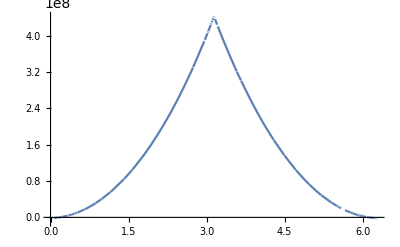

```mathematica
Plot[Vplot1000[3000000,4,2000/6,1000],{x,0,2π}]
```

```mathematica
Vcoeff1500={1,63993999999.50000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000497494862633,2047612690468878143908.13060049178594538061344176695207513695646579718349746420371916787855377812112542234938055424185377861445803212821954527800025893295356500143799789093642662657428102438783089784801648957581528880424340547256528,43678166878102110978031238057973.62367277899151462432900486608563380902040506448945562787318609930358213536832291319051969709635943282969416348131629851968311158989130732775044410889106453730269751535550102036640723579382741992930918,698781746101900672530740969673310906709303.6017084269343271112264582221468266876945639460924780873110908427087275357579771258835002831835310666355844173579266636046216951193807427843038879163791978850254591817720249843068806797078124,8943509676896942452457919216009794062607939426671232.16487237513508798005884895562350455197985578051259878121614270387455055638176329717233826643508393973342206951180305214995298057814760354594743165235471034957729098125481372745401,95387717988285971380759737139806571233935466993098481728774411.96212781134355624788686365397630292897001469393411267286671429547326411556032704273395453733884393097580442150666991729569998229051455916003586600755684208906943567301245,872026015263942923424804216273304234442151047290316620063199889439125596.7177594757500574127151284471105901891278870941259928425239125474337129584127450897997184556965144569443364930820035456327110021184497234254943023823839526381865,6975474753499064215617703552437356848063250834980988844750300467593548773614740393.583943464238286603485302351455706222631763709729318880487520639962518702374633872630125175694660285325504009391726761368821793815809563279608177377173,49598080908448284758387317856262544683550064900769892441804350312243853402507817144434356442.2219850505829163136846809157697101772333801891736018063144539908691366494365674623477990901949016328340526639835013841080921578808819772743,317393316909879450797205059128102906591580357472604197643976086897369340406526997267161909451457983288.0714972599749489349670861398174922669714661826205290609359653064661229032867964719131047216735179339811999216918285735921247723489,1846448896086767659915673092359304702952900109933156194162234270905868013884614414961604636798504307096714796021.37700823610062333746734213969006383479635471200508544071978410081846660591214702205650845146507833567236230901784868314,9846628206153946544805632848343243631768569148888444037549200151385903875341532859853795586955548841114396790409089182483.393272532484964532756570202022742143499602480434813787350272603463267986789964828519175803339337778705304111763,48470218289005361927481823327740637725456911708480115972333548784042633287907271141071864425714538401723657353596969495529928550181.6826215101438021056512553576827175794787780796292228314252902864210753270477764733889190589257912555,221552687321127896793840657483551933197383282250738224059552522776848534070059242574336604073727182545336804209706023534734035460662875777279.5995855837365748569174160038682654467706903050076488962198947776392885690320189995833838232,945181341140538933967726839777639103151298406474264173810091988457213717680202866105310368454355436927796099022886171939225702305615023258191596439363.909221075807354944099937966897207552593913777525568154561962574771684150297825991,3780278773792839334913698352760967294143783142074206161908804547643724649717873646794031009524548887975309558869595812611936605939463865491931146397952192592767.347680337359543046063426506956764625769589104637957285425084751581376371,14229933528425353243991383805953665004041202080408194272690988179179923144011887866715224110085736946361317374654030962489381362232067117432469677211199012170626552518477.34146882818860083165312736825411844437042490970428538625077916,50589178322609762855947007006003691992304485117305406522974736202318296582552225760372593370418729523487468079312840597330346916937249534003640748388550397904362967039306420822511.3012802200871407884449709983603144931253717485903977,170384693828792516660702932802937460746910639623499148894432268951152188138022358847232329989778929733978151624369196228175291191264542358620010294711343494465276982489668871535161246924623.9438598336828772260459586374575190435411175,545163072307269939303138362362763073808400455747468661686225924149724517430811405629080370356421650894507860402239301614792910571660108515589629344905789903092265618920100432799705959650555936897369.160559120708842191807637287407136,1661239610051875647928512127311178327522652651998638356484646151700486381636872258050561644888936037780350038511054977861281022962749227957211784786074812831347401855038136621852732047824118982332174143241818.135232357153799733849965,4832079081269575345679813035511808686985098522590249822172865679214675673252376871495619293748733840476815160046477307917204787025461064190713007267929256484265684061312893794032576682708388280680187172827523901684230.893606663838103,13444044084922232520717630913802862695247495564966231809172971582709065575479919590530747135878730693706592313888146774864859057347241519478189176063377934810585747711153180483837209857652805283266651199801095970488220048567695.68192,3.58460834187193440031942490598206117085406518327289641627126178643637705209674749904689519493413552188992162607454025150716630609315202475000604110051969187740277346680964808137424024824446656209192337260335078662893813329466972893*10^235,9.175379196255593146636185751657361740021480295722067283530757380565292016500035223105291763625077665516095991734969203584845433897796702256948731030442557483910429168334599008796356218258552542595976610494240355733764697094706248407*10^244,2.258251394734241376139663536397570286945685578259776348359375841749451398024651702222977482613707547852133174386291881305098437515247639338453180773721040710099958602195697983737027836839183409111990796022122588717931489531810129088*10^254,5.35216422408108684440155705208693882580625091213209366337044251437450319413349975829455877197603479247785575671620954234726432539060800254531301744867965149847164879011004880692135271878897271612648815143220498300443966256867994372*10^263,1.223183464283460381472674412978603735682944250322250839428728801834962443296507665284387530813227861717059603446159951283187919521906603183247254522564102907556420939823740976065127456594133452054890504425523149668201482860946537175*10^273,2.69906348516016572603834637201673218279834874192699914418745471221132129372228521226138190998842343607589628007030055696947697029954312701745686700115827623643351796807144523914490811002225966902631068742709965571586784415886571407*10^282,5.757190971518757137369793603194992550266064212547228669550895512229873150276523663956939926992303261564818997274766896290154154720365095565145095716232280216200692276460428116386141248915536099607956539293129216138228459388449654464*10^291,1.188411995179961969040370853974665052884104296844530965777363529771024267674825358113996254161226164535472788270093204231283890116854562485850967480644428872829177895131826123482583871421253384914081096154537053852170428618317029754*10^301,2.376481443541489489465733279846698336202130723501439910248865119002327563126245597009386883894405015361637977243746776107953841667563538757864867615992208167158759069159165686022940789478734667613730978899596753038465475891364430165*10^310,4.608261982910672307260862878718242032777727267401796468369604155356739691319546461892982546348493433985405267469666318997740619367134026092254639695130569852702447228472266630654899841638499555525435189724426417313816443232584992366*10^319,8.673097163023906576374070932932072626807233030019879194623411761195330654032959489139261297748841884395587251274770307766145503490147808896519834648400602574511772576611887419050174388056222228274801940767848192887160611249024756427*10^328,1.585701472146972715386862444665559681245985904746899112160733644700835801628584709346048497030130402082696499735165294992379125405399531494195255828298933256155591464642621873343975535113765911816548344127684473598979203182199105942*10^338,2.818600242185570216708133051895651006972819829692336174042239296593835316095613460594529813467260373983435742835389014589400566364003625894036129881891020681236804875591208714894606621936736299928218248302490077795260962876597130115*10^347,4.874674386223523799498173173671207106792592492947304279623184640062456709710364860511322714061316813471433835611266534709107010232985258468161211932552254171904714720090574492377038464365772622547151165860671304429811147685837042784*10^356,8.208714661725735400465702900995477767740544406966193454160541446516259219949859390785141153240613578500245903887677075048699156844854433773621788024584693845768493924217677408931653450815632995821360024305418036952711714899927644794*10^365,1.346861664406118357683906471201315466434612461742291833737052764315656701337959247633273045286375236105398611781435216747867154620605454382197808129547090925142028657712477150368475593846363432115917834724719903349615106858021140132*10^375,2.154640078664787599827687125083536411488062294352200459301344635954299388453406443820581070391061367648403859696081420032187766474995291489005393384057405861510383910477804313432570315087729981287343680866323519011810931382707921676*10^384,3.362806707284780738331760768334099240711434187414327848273022235381396330371283965046416296891721044599712597994738955717651626897595612588462747006616337314274204464662536810082146092946952742312851815034732928620950328661851492657*10^393,5.123455124149168308845784617456800330400191835423867311114055683251349198526668615646715106261085462098246776903712689179937319719453787859118112410906932677257723477289319718039817375430543239782066724937838130317977031516293058598*10^402,7.624372344290626272398022584848613855742820674239718177196114590534999873808529112643608729966807116782136735290573898474783781274108869238512047321355937351219090097724617307580410567108569324645305100005842488747133114102891538502*10^411,1.108818172691337534514672201839677039016407079299742443188725249264361801081895514597416338174374531062522540559956137143541592231912441795824262038586970256590597449388596017895051967010425525045571391426729119995132734383906784865*10^421,1.577581911476371138093549364294662481405876718905824768837788681248871061555914550490250554235664700933171614783952377384362007694733790023099602255977175896371067116646731171902937247344129114299722247233025902509102743620543068899*10^430,7.435079073791351706301128017307876361261311914111569702802678822564675905075546123420992796580304791630940648846495321492756169075008104141267124636134204478262089892749637587037711325182957883303046793051801195887982101551234654434*10^440,5.507776231765990416115753845933114974221326111503381854619696807845809393449782233508195307210395326170477473074491729510467760949776843056167875972002561301878994496073004900672574002818429942515920088524355402451267082460074027037*10^454,3.856659913216151816995501297921412621385986187212581207311169428786428173693930460333595385099289893251937682367783689091473917543225642737283491241769963788589211313075057867447083556722005787496835072613970738407734973436355122191*10^468,2.482674788154743867423733961017504409829132258450711760783430928681190056625937464908293385277417069487980250375411527202941950830406587186284114092517792265701486969729949448866318933401079290453156696865031961830246508408113923419*10^482,1.446021643120461660922306594112859413603189986355256853467944130618097919337752942625832335717824585731561887971980100409363468836092364680334679885199604193998351354131149125500399018345257869582910264100175284404392214575242303501*10^496,7.208512543793895586136618770669987524841565757721375531137112481933424801420740815969812169687499470729240473939747857488912057243244506323229094485178801288160152859651715462088270488822420774436148948920017992661906019982938242503*10^509,2.476875368447577281953046331420364204326986711991187200188103340411021372859044279485360558800800967794673529711056425814667776372787633600888576269902522971928507536791011317545719747252171069453006435500642575079643917841491334387*10^523,-3.815139171661019870203523307900514624062403531611881660121450802432698982371737368738938468583566028785959151062183882747135637287204492191170471423585277859025157748731215908864626602528626089612485050513783645191882520725845470919*10^536,-1.915298105069984703368819712185073751355623560400141389818643871478293403362560716166084196193679500252146910448657433531154615062344421154847566756862554366478983542042074133917871619430283371930518664006226945058516326688537824452*10^551,-2.531651812562768153612933052259892735286226849126585089116801521188569870548930658885142522059356830350519887391242848736710476153021201070105604602720665598435652737386250489808159685707110526537643672103866556445351303747218945864*10^565,-2.533799822138797717932451087557588195116754702143778006734607010998466678115797305628046346204770949130252503358067389897025997008522704079086899679416803965409204197052130534483105698629546489222945692354709257329131780839096461479*10^579,-2.171791781582286933923002043218789613497752796839768593465522018368800996563762681510063940813498971535190066879153120292820887942168612783310115047897931955830914299523746216226590951238767379660012579185656332873412697274289503125*10^593,-1.656873781032040773345989075542766738675435069468230189717650400525497324784416554131951586648136682988217634427451159617871166881627996619547633875296185706897312509074244161472560388095884895602529192203429428002714340554577627465*10^607,-1.145581633145028141851615352533890542027546351801991659081658541276693682396098134171145999425148213982607294943329591195457587136690155611207112998635008367321031396532691174082891328660129217000205785489842107064861039060239272486*10^621,-7.262455315576435284601588296090103890960481348576278952930108103913094337513237817867142079591468686515744529126894938150273277934637080256550423678474036773992986754851725384742754894827671684851921055779499077155601416966548837933*10^634,-4.260152322537751955197561948044006023246487902617808507949123434973623264235289434170209561810874462723262058776403107006374944842895492354310367217807893947837009203735716113924443600392221431994695720161695783610775389767852310716*10^648,-2.330089056180535947384217045958634368148476977485024814201023934163063423628074770869205619933426824857578252104165832819475860451770429751039200121992180354594544035241732758467098530599191378583505809133706928678858812247185262617*10^662,-1.195908498826173861932367868473349032977245409247485032010821994418038915301440360754935121298349725369109271513880440313369813440856068895278982191590550178268000231185399809531654437451286509244115226067183565959100831093370720087*10^676,-5.789848903580245343335651923114874039436913198119736951765608081203055271782380367397875024375511239173136600058952546113812344038615702421917083956181112660795542744822630061637133834215958222608934540289848154565151040331962175764*10^689,-2.655476540449565665780270125666229012119718285476217595912018595034480633821530512271375499329967885794757311722534566683672886383269961092554669185077963007862960172167917528611781391955925071839766681802732841810740662560058290018*10^703,-1.158126872806928400997827292574690901674071771899969181745488493580334007285864683010506431526700173009909200623341244234221488142580036142734825963998360830012997797049406467092895896744696780237219889559353436830012384817495528036*10^717,-4.820687309084249252855677767363944340618133243092616297889907646932800354928281699459840965502243185835336579457589942956212574984816704599899607974567370115769628181422362476142685431182816705966775720241770982396889244647414617414*10^730,-1.922746270546843746641121908771735450739499684050823866147711313300354337050564674617451174077075093187979919354980962772519728507514217077980547814305675266965403184439163702567065669488245771819211874113794247455454824481784863674*10^744,-7.380486983568373005892462499642453231220591750231016906493588534143542482044760525794589607516981987126041611578989580187884837850970195612850979897008493794040708874066743483285460894969775791118470122582368748702973706944212333147*10^757,-2.738922524368672652552531142683541476632932922726038589829732968420053528346775140662320240652471499220023439280349202408506615168995112280299237470507272090029402058969595417210872060815615555061650698466952551089862128040383976857*10^771,-9.869616700501764919840413874953910159757081201028765374377203824246421073326051308047256238154287680655286044841361072491966734503593143853320607439163471480381684130344220484768979708139700726354702272897459564411506563597208983547*10^784,-3.466008708023923719279402274187876808952083581605289738147546640170443112360295983101961881058452251564713767675461558632004970662825305044726574771604612682324699045227893138188320938103182424892633925522208788027814406191426891147*10^798,-1.189150934927920640981117259912698230788239166266134486046687581410247983187620539161700504695625327939910577813834801016819119150840896765700788339523840776375181787958209072463357085522423962338470061519373760695261010085914733354*10^812,-3.989657996690886015663179027735244320793297906477958019403360598367296866239522241228163119579071562171109525882834995805414913929257867978077496114849655755076802801577356657693437540249374924290379883151613663565056939671275388154*10^825,-1.308000154388235004310331713272412468745645342555214243685852760153854015279404909087951706684800014844768932306098129420701830646112725857907336264858529709079121000343924937449270577471309798557600378468759828655966165544500347481*10^839,-4.180077663571254491368830224043709396642609246684373148159015452964264956579918939703733646514933624752721275501750320824361600426919206862434103972153209820955927330605451501710436957915581122328732349745787518882237089165241368137*10^852,-1.296803234141860087770151599305682691461475996653661467012761053812504465557337012738949525486593489588416461660783679313544466129836851398772663026770808122196449651654464132166336610687494576822304078437484556112524691156949141151*10^866,-3.883567316609687909928078633382634389966852850443859251456038126714279026814620247476011390586755147217189755129626280456383248684901440758757570676695878261747964937376223805077891218093163050704700889214664496782551280840819514487*10^879,-1.114860926721263043973368512110689913295861850328040810213539261075608135707018896139038620896662554120362056364967277990872648330322860614748618164293843381249205529363020931508337400753266560966210721108372857597774238989745362449*10^893,-3.042306989258955440208511974353545322224736119030331857279788541818339836748530402054262568033788427303718269030744828423722803175003827712216020390711191165354135217698579641490787533439761218068113661896137696878054769901259191322*10^906,-7.810450717222511964797554912438564996747761754820957275050389799182492577838147279889586756760298390042768855080975791692091263600383952975918328353781716569803405637521695667226411394448809980917567827908539595503641021269140250782*10^919,-1.859934268189460948812501022568658608092265436047055745118666849099681814860027271221745638252511642375662422052783374929692130400568211105648863825939314065918308612435721472042438690708581874769003492436554525120959090580512017746*10^933,-4.016172140089322853090958515832618481667594626547391446727481448300579613521088663232379105833443640466708193638689775439060370151317913150472811514181828464408677153919531846036536696836121334850116566055971104278376296331667576319*10^946,-7.514027925788116268841590048245373477117095575126903421001249144733339337753398231077676737139335249299704047786741081059636417855079567361209570917958313906048822023770426544068524840715012417052085140110572240742112574424007673348*10^959,-1.071959870796805487912924585328248332095624463510706420361507964451090519026694083800933278699955186641697780008397355277579483781509339307720877277474484009140519094622778795156563413497479015843345127564124593142943002937884784787*10^973,-4.661476387518278652444307008837816713610494183656008408997562386860973376801805598502428878636267671006271357455421869618933563020436421179584399569977979260585950944612946537671158646295034517140854772172939014679701194304860481078*10^985,4.163468420645845316711408223592108329153499299152889594637356249371378597297240343946668111538016041937029918317238843461937660097294154369142156327030622102088884281583479639359427144728651416125322447518475372124280051467097506365*10^999,2.158997192891954967037236564839655733530751362479761678265052687385947751514000407005279260059979010987525818047328892086397797106007145602031633218877627398383618479657291215630909333998353907087731485556564624619692426736293724693*10^1013,7.361629981951357820465451576316937240346519741661475194758677902125977585875135032173162574822301320601275297803841085246376009035175831897483252735879164317636828966811837373465141764399132404241763483629056242119800260733167406191*10^1026,2.089351853512280239857610583681433861862388525503466730490389591422090594018774804336405738007794421838571658387078946725577453991708602573748371231164303199369044076295872148844884356060223400221393647556318379759641410617523996811*10^1040,5.258341151444392723449837245743612463876251757627943514129676211503654502936568244766050780029630782739508838150177761233556350753418623329598225598961628655620217320235501404485824475746521492588958939863620044044141024165928568901*10^1053,1.202154495518284512116402024380610435852975837309453566531585539969085815794306563367798197861848841510931979119549837027039550747765050770581188787348151968750021134886897156917341015178375403913192708666060432814509304965306921226*10^1067,2.517969900675081591490954966509391725632905039885903601463880617058244273117888910697666614581196361929604177749538135383216155004238477959760032928355359464020195648977877659541680230284478822985516600883588104671306237333989670125*10^1080,4.825340879828217897185291104871187369135137777796496596084047396673367001130803743710154105725793525682857101478861698418572156384051149493720090326335104625553942803524087685884055050953755864635442779957622082566950723536432046178*10^1093,8.358392961307552280990740254448881958379808262097010760695516650311766781882804598803385059776907954583521336285509150741886816662237081330630267366468137348786346405063861060307802707682329990028669252081158008695060610040139571622*10^1106,1.267883253836131976280316018626998962754498439486328251418013593491525768594943126198431631286682235804865026625057798914140546426948396258364545058560062933862432203833941286191325842069773944221175455037771530105290311522805615486*10^1120,1.543560632494259421436466398106763377399123914918372076727847008770749842371394934411872639738990374218556588601593463859654589928299941872494097238052176255776203250005280144243687737934471318074814128844268409138451167033874974657*10^1133,1.006779836226725815437750603317983258226461894218948992261572408677698727790405168764129319129908934599804009010116052950801303602608021306333330783671999108621020699235096273218575846954726980446302469458904234517050445141484387817*10^1146,-1.769640545613376376776319779361107595633503682014453820690259644326935714875848555043840504733676617445560374257594841880608352642789207713885738243314069155002202719981362049188569724767423985012766558190442345349721185587041390277*10^1159,-9.382990699536405178961022590389950928168836633560210583769007117672800310134846037311268257540438699662395151721193864818395011418566986836723832000521584085211336846969091232736480504162499988106688829133900213160619329415604883745*10^1172,-2.577999347647303795934116861846810214090469266569671897662164425492832735336802852623015382605581849316384868137030637476836436624178430138891087542265701090098856447000839721096030767217688189438760970799668207859089740201256878115*10^1186,-5.560452323313351957578378946932110311663494690117534008553150622935410953238000475747895009953179721546053553255076643296910322504205293644118273291073116752311963078367277049399550777923850143304500018864814112914182388893251944402*10^1199,-1.016305167632854500897301503332202786986009359657009731652322620008094459070516694867497051681275469642573274755201202368102459522542199438015250614114527200522487296817453580836717991483745672243912982626095175077497901572793536092*10^1213,-1.587127582026381123529277525104707904533472964178194804370133101697878897720643968089726961477954252772343684467648480935296886138205513028125675959911997252415777989936754361083693864562676100440414122119274080468957396459222209739*10^1226,-2.024078425687880916377993232298057664957536260733221003895250015890669906022480139754519087990527605468989063476951896446013970832224150724187975442150390407780356728010863431542880811713621275116652910971073586488473609572784895641*10^1239,-1.705731432586377988102553009514961779763987838669228373100730644712328906678403705394128494056036542387465700531194168710303423043840859629919550851458367879285335656698419876521814905996174943483026718456970478164050506564681142211*10^1252,6.31048079695329469087058333632278445685209124948513899423341201715602944087455207960710653612237383793322340303860847754471684071556444752028801515769779787594406941414178486380422214302461252445738048767140395616445990952613201758*10^1264,7.239412505768291278630680867694454791276276718020408747075339834434246805591724445136232985491919545349087273357110439215474391882441543625053793839353307505531469173735708103002739329984071498091429533393949293831375207308167724559*10^1278,2.179784574584052927886118684964822353420018455337163514745349697847897245824238940509136746522859532881267349609992782693281939705623299225645257625559273814234616935059133114666959970044357527683937612801912312849960335503849204011*10^1292,4.995758814473270824483987188682399168041465409751230918800376858131673940229815451844649796135936976922013243354361495674749147795635381854910823238136121900374379079664292015651640584796324722345710005904716000919419354699525652143*10^1305,1.000808170481413797470295537894415856554603331371914554788055658359457577532913809992590016518280973713670563529854338733246632897891149772890862404846921202765543884945679914527786360123880243897652543136447293698796430791774755459*10^1319,1.843323987400780104229305387316694499720549588958586256456756625911222440214916455170942502261999402929924881343875329540419732225440310386296135888249379629120114750108610888044354951790026908852252447488826596661044544589084947738*10^1332,3.203805067404589984663354320888008379650144334681883556510457325049575191458942382608968379297172996183216780323221759972342132565658545725356459427346956642825686737844827393901456884946830714974091256480577375636991461263469140356*10^1345,5.340150335256656589084867909757221813911815579584468338244082397405135150673849868011245870409018482772204192475945032367362762659696206433816939406474149580632520533704148123997287956860578579100419133707196980070758580227793114787*10^1358,8.629417646980841575396406881071321888820340307034229440931355652278561406288148025026245513214251391130739385231084802181833678070543121880433465954651712854958008300835949086687376980696734027309841644843870225716249085611847748338*10^1371,1.361787588759178039693863522973641920469898583515973521313267165745511490529242463504004978850353384352603618312860325251251284613128556064385601666013191333745839978468467969078905579398312047206676587044467743403183115833334074915*10^1385,2.10791381911121469020184023303679328968536550403908575472420326719171328673446229039356008207988752112705150162472609394639401248082055722219979547280770142116727808970892942317999147713810378488982634437224096016747894532993885001*10^1398,3.206987444893968886686782104127899705981677530776592246385707703896706261890013794617608766003438281027487089728291673828417517133275658771371066205044083602605376575234352254818364532719464646997423670830710662596437550338974645123*10^1411,4.796484992531638935990930082651264018484875488784758529110758255603303993765826177248819254252334031271167879113342870876811788206112028731421446467902756138310527858578190600904398949191233397491016862568126496212098714157761572915*10^1424,7.044576398466611816574354518271377996779750894479087729733458600567084158920896708944824670982384493915508592228733456062527916184585013642113848887289429347783451742176424663586888204165979571112643310478208943045352395339074933141*10^1437,1.014143533514561275817177672562015004253379039318971287893274606029099496081529913756564144597486947905816563457452202251905703855786553133144716941509066602676012036364909459243853145035950471407781706456287995451885889435860516906*10^1451,1.42803057731958806746383858584218520645571241380011050074074182652427187240878489936457422882302805788739613603431479571702893492595481511510278839490734636649015840169010695422106645120058230913632751452591954374913625389517276081*10^1464,1.962697396177972418362766638742147396242105568034869407443485415862336575702421342146354606314363569950738656540118150524077667987726264583536211587211553448820398882745728890667508089189308013913894341957383384497956115334337150051*10^1477,2.627882952272133452315129678716234320993835048620027539499688281224866284204558148648759490106450397162589488648131676554333905324897352734948078440514830260752880397223090596972192480641430446066074809232218766318778126689490615074*10^1490,3.421824111061804119409267188475775418199924599481650142199267163733472591736337360968120298784865451545591246490075892220760723427498188945914895975818237451425795604517037467855698516461861915755632641973383899777954749729204191402*10^1503,4.326876919364851968559567887730779512739294321060378284721834020585130838439388618440665057834081436404898791206736183503255466192933906864111038784182381917050850878517609917571383376807249370304373172520103332673375687712111084167*10^1516,5.306553840089515256760417931986778010331783222255640268638541085863335872868709593555223413923919944426519941952413711491766739423532917725188375337792254080993848194635744156936112602291138697811784980330350435360321402586859434047*10^1529,6.305147755930129521378619831880027352878263698139541745298866827714722042847956155712473536060733499080329582020856924808565238395046782491857989711907077794964764498033016215515246121815260512438603375388971669679083200039836559182*10^1542,7.250810074027915245598951204313751553005384033997500709449489463790410462744809558104382406105099642258001729413555572705111305987812978733605479828799852081281005653933641462135682850509001343026213945668624910785964528979831823965*10^1555,8.062304014220637594328673634987547844845782765904823160502317807730807685462005403699874311526105723089666276430969331230268804615215324152081363668018593405619480703296583185155174272489974399801086941378440322988338176543086101507*10^1568,8.658793392604309710174537240443437975618419774728410409640081688984369297676836698777989584386826738453995203177341255486808308204192779188754300689583900050705285300647463243094331270018822099966061522985406237869077079038633878032*10^1581,8.971185614898042874193203728325997155179101699217339804201599740077770699075605104329624835920349627007112516398498743054206530549126726210276610572390630909297024290382057984883919415740499730134764424482890532205534037780384941768*10^1594,8.952988961421453418994382306020362613411986521541660315837525389630440826239274869301430478248378175252656645353308030836974989988311685848771808904081386453507455257720038030527049846454958150306506421820683743279628130090934679213*10^1607,8.588563427722019246830903095248382129190839105790378369128500976887441905314526396604749234963150837986865648497188176637766642017033825191138594639124400088291940493606318615442421249031472167991242045141146043704688286429577849936*10^1620,7.897088514860998248302702101712652471965077760745560275165605437875302439955124745415519645919096488454253346612841858092339778460920914894263371357060397914170092321333024533031061845983727895419092718796985548601409502540630455141*10^1633,6.931419088839658405498667325497054719633040771101319979586215604459016454026657300086025399345813494297398708128617945738437220258295390828015463807325996832797152076052431618893246112964950895171874956089065148662390541853536668013*10^1646,5.772010082416383602421252279192035612197988027410825285898536353136568298743189285435354913220575991553729209581399840667941603889961816721055179122829512485511037675289471096236516175910739281699150012239293252589733334768346439475*10^1659,4.516994525611985350200834657147373058023620210965253603367346299935059399540545224076843489415162592363805428569007231756166346774826849648288277602852544943676393870823495807235405227079973051502808796324764317280270441888550419787*10^1672,3.270097919897095483143113509869495685421955638501290869252420390109850181876435594847415783164414145122887978329646156769848849554115223890176291180020470544091717493613768795105545616520440848575407570750143651319525088469443111222*10^1685,2.128287427089322127476486316075834705636110777379464565391739693324754011504956201568867309887836721057213942550044219396768160056806584047875295069595054613248208287904141636345489160104261685824398209241193720644555427854370970331*10^1698,1.170923577739138323216230921225531017868208149069300403191972319221776351185853076015830469347328928318963100490581248676551557072497149878310090936691159377206278155045807162529003604710047369886021733801284029141188866481397381386*10^1711,4.518065138889763310657946042283384252118422457510906032666181482376978325683170827847976832103672420696405030764535251993007529469010525118477985429121980550721808498155054882290694870495530521034966135420878677026717910190452694022*10^1723,-5.004153056539919443016881958921960648997437407994940538024871047581605188735302148540865336268529989569137023108161594699190012319454520655322463370571550704859737416533336826510484532551214374271127382782131742154552966290841771104*10^1734,-2.052863449927707985983785140909797122816428547279605857200849908782847386298223452540545645342415558042399575943056809553905105058715648608868625811894599316696622456115211541875471882783292111725613169041683605463307771537268294329*10^1749,-1.809310962315502240604836382576978280604523348467780658515799407231381806148658737270115118815911554059223417741119976481395419004364627485218856718597978076037785015081235004926511485718662943196672775244712319197464664202760108366*10^1762,1.681980787950153438050067743988161066904067332023124304337999137686664849456028404753083911563116483237687179408910815628096626846597527951069874272607352775983534391525708010533215427742653718194412067934100893723195601048352098747*10^1774,3.259830390668097542457678893453041267268534924905917408203134686326666104979741593068904249417853504375396285194731804898510539378681815732408651031544070771241413837289310448546132717600746547745547656493185598867490270290116556763*10^1788,6.828786381586201441664440907035667158235322148618521002242560216500648086417222358989878466536785820027870525385259586601028620613864067884982046565882849983635948734961384526785271694873782411311170394190673672759575522520791788637*10^1801,1.030222984139745546007194844072298090232608212395831598473723642010725157724593615864990459083458328507335505220459718284953972127899177391861941567152022492844953514980468320957196841773761099550728735057879019071029152788598448972*10^1815,1.323156747558564426509257834323662941180831991656357460997874720625254701134010561840516035195478301197639629475375588805078333964306721540724742497235486401545922215069800169534631881192964170151924419749645329703047522834508575165*10^1828,1.532563673108000901457579375144267505036740987898426710179907948555663994594452694916309086309025099017647686098088319339003806658548923428662474895271741942651236012103724867115006223606967874724389135718853759730385092213727614255*10^1841,1.645588835389925747446305478320816254209320049350636684650851574863211831724718091789713436366815146251970086320796832622129987888583701337819213851524030932637404262207917030495134627654992795589082396297901635526383432838898147108*10^1854,1.663770939484802625508479043053903362350748944291994991475816189156269433801053188852870899548861490174490251507603772055237345543780867223027821801570571749756093925188273097579274932921316754058142400441724582520179461633936298123*10^1867,1.599552671391185709274551340670267867842623689321207612383168730275942952105649161959935216497958053710913660004141469528963140972985802326891086098183175504104910236163796806805584611611786888289637999875958221540778143008439764325*10^1880,1.47206932622352093999168139946271196694769819304482845301044505625839640315286862276727801722410880927967299670018960197438480392944400918273512411556161907505724345418090430904512956356241627364010119301726436651819872086554144709*10^1893,1.303045636289632677746467056489630174895496239782513894916269843276991707850316750611249871391674615244131474339422028169998141630834408036723913685503620360495248943545624012846741057073458414719862683854544753668541784111049269919*10^1906,1.113411955368374228616208574848198663575164202287643078357639077007346856847067273061774499188005902524118253904716714074375704283189753856245705093782284955471197072162396851566899877971317129092398766980929750951195066769063289377*10^1919,9.209666891324807000208092709474237940777039909193118683900646141509117567090044904149293561309528522076473898514759266187504636789219013460753884301085408963127232066309147077684409812693566592146323139283007354999889499917599979769*10^1931,7.391411305482686764531840344312728086994751220546893132190128662693169867954592571539069018884221853552866816635363555320804841736741804465775369599675931359555593776222350864647346167218255303981617599729881587516996150167301191835*10^1944,5.767200830746672703119782953124974976540504760874648486329176000459637486546620636278985160471553673302224854327193584513838250215225005887809280934606125110065837761768360042031933010041472881749054462152831183020434105385059003875*10^1957,4.382589703918524520117973131546739507127749273244222254867286488161229387396997927771624404080408491971246597113908561061331160947937686883304216908936528419728529073608086083069573267469356276025975231271622519823632177110024616236*10^1970,3.249095860215357617209149737140401857557988866044246066714637806112440534797848050751285780904220447949708179622519122269323955748436726234409177910693160178743289975676968788100354364493770325606839998443599958477120339457774593636*10^1983,2.353991676824222190969407100815463378185412443798542591028530195994752429601022397999627295766297153420320060043404074968823933509059747842744120221376052570422635914196168198639346040440154753246948678449540254311814836143242058742*10^1996,1.669728718892804779058728033986777274665687518694159250633023366609298922383451052200946278617796327360534398565766532208837074793600046350048252567601643950646309656021203653113632870866012034994689607035142993784791357709972907791*10^2009,1.161834334444947926558141595849278556325111244453597162184493204644483650768721288610455474347849723426415006979095385198168680703445813252133022812727530808005631129380298339108611712888532341671113683512540951436710118336514417669*10^2022,7.947721956453849416130078093499124392952119463166063264000298185011733868846332841617871703193964579548093528643910919846082470726304771406368520811399268813569943871989042001249288468233901335109509675589271514428439256766537284344*10^2034,5.35747440056666097762668579530089302647975084051482929733752180566409727586021482435534275020929684907350383822867850841587037455962828423133791311989021877761338953258449144064476187645262593200362412075044499112980758936345366259*10^2047,3.567418460815485671506874280404319276153120832794498811483076382113616723311146440711456351208530969324808065512046947384734525322576079805864100551562388439302495275897034252264515227184778491155723968342054680001584636403873865291*10^2060,2.352074109096744029496988075328697059307951076356454315223118222333393647353691110866533788410110677248181319317582678943799604428269499662994325393246581205542312754019782483089748677123980998605645041549468440398143297060388364723*10^2073,1.538682725145220942492152675027720042768240182678440436092608591174840453355263037230483590658186890031885162313083982401320157305205729100305347381004246952287739918112833392232777828451011344580805860919115576017484584150515575988*10^2086,1.000253640760847581058252390249230494751504894355850518661267453348875296319908406387252973584698838198853389103996777275560443457424681227396282067922158035604574632324258580346122529210390619497867256616630946350261792868041222245*10^2099,6.466482307398507024880945417836423819128582743701456608642862007491416250195510013828390411735513804811664085788181898849249687470096823889920169081838032684923605101361905849984639505013293319298906449834929830915443205960431136807*10^2111,4.157013219989384576045726522231007962087644854598530884315945424467447466998985932958467153437654333615068814029541125090338997394290363668561196311321821747157287341692957839625731401724167628271886389512661524325094216131892125469*10^2124,2.654887744121573781100464403346689378576378438578901996346576315286548876409532818932455733799222697580085789561592832384096481492502783411007859110713681808556919361516326165517131295092632144219149913579872257540773398672830777829*10^2137,1.681767814956787869719880381002539318617974265628643519588560741097009918378689514262495957016389108765447510796361946537225135123354373507874546903907058068086144798555344234189701718005438151079280101822348822982892828433283529418*10^2150,1.054526730465532706069693287881109434313586968359536777020175800896834226464558185530278920184450774500452276680726099950024396250433507996553064170228615663843146227274100541317172477537521019978861048220709967257758278629908779102*10^2163,6.530737574753518706342019221325556215601567416134001815212571765312314919730829844444754705347015316954547424832210159710775070027442202465020498017653483475413377156968379081514030353676663442978004239654566011137594307710206760686*10^2175,3.986034050843221079554712493125154677223000297072839527423761686997882239261421159702354618318286282628873903033756202823062318936490377917210896835633900545350836752288282420721492536098016732621959179382736689975178416537851826255*10^2188,2.392984452124431397531324168837105457750849743236212892687785648650573813959624966822654082569646238634309177206428860642575005497016424696840305875310293258586983042818868669776101158007768480861773086201116120886166650383768736627*10^2201,1.410665690346026407204084496239925786121878430607851275003508508589072755912365895281324752273817990268928299586434303244057412517230555392534861245693037478343465293350024100239959791286939239512932521845528508851946827142610330447*10^2214,8.15430762288152522335861785975599416421825496918030477589160160215338627235170368481047025690630861186002135164188882027484768626017641999089242923214675386546835763373768431672793566696851059634094020365910973772703383999086745702*10^2226,4.616804456315363797449837572784736698282991241435007904468977196804526403765602270533438742952676913863438152282916122615126449147987087603402911867245278325545720474377436187439821537469722024177026167972723080510333980403236204992*10^2239,2.557993498052706562118750773385405371178173004387915436839033784124302193867858401641326847090726565606211299120726655605030139320158944071159671127675700180384847037715484593119035050821856220639275117324202292340384841261106466033*10^2252,1.385948651404609183961648365143633857060812179222985528770657154341755774823100279561048318847224184898978500725039644782804683938427623197841803498512037682580407737059238022557857982810683335442282335684865727427590739041011712152*10^2265,7.338652248475092717802686164784269864084770451032841331044933544732996288638971103521344811543872787019548663223393193262293691439875927600915816399526213804261008132382173398394999033420066223018558984990497048586904900594048248899*10^2277,3.795366041020268696144851813354485213794127518042618940623354724025382910626675999928241595223931042604007505040497148039800745051416006283062375888761091686544493285445345883566845760266397337091349477539360481022438747417925180051*10^2290,1.915965715449523964625098979760785643333979154764558343553323335391275934258105725600185904172255705070814856500840001093296661087119339932933986253713540051724737797720058217488709695822538657906814235636214824044489291414300787146*10^2303,9.433887852939419732279121267715691299278152614947005161275297064238970649164447977970072336214638552312492783108529025825585723397420325178926344758689145201843438807276848429671585166532502928134855315232085419352937631845100945123*10^2315,4.52617494049817790805522989711688477318098342976818515446021534670074001032215138936058513747831203146018106372800924250455498511863485228808878654651419683056761760771042529477321023184931350441786728648758833581250931430895623809*10^2328,2.113057572053545439317943338410781559352042018143985131083407207474700404850473185981272963275166020581555600730684652979462391026087884642550082702142359062767958530850538860119284499100756675937921118064634798521221400502361343713*10^2341,9.580141584326813995668152568209854480852307964939781086102792535662282954556877558288354916710068589234991115748747971097365004151031549259860906596947283662687845219404176688786741348834377170611972621017133433168719297005638935118*10^2353,4.205759228543063920193658818637400107393894439763776226835042527901711914057776314890739578938525667403304359320392577247750090522936236980767573334259379504190966186916641908073925911514822427198178262054001568548999496104428433027*10^2366,1.779877023239491484707542084152867184867309242035102499340238911847863019408884557940587968923549536365979343697087801332977035962655821509890228367589870228183245260660834282134496353179824881329513335507627065871902979865825676793*10^2379,7.209480930518838964518212122824915744242660982841012121620790445376207767431881351246075325739207750164429734930880683768718793757509730470426730023132380880543229758590852020048190547651449046168673355094398125922385092211946545445*10^2391,2.760958974616900041427762925458128477930538305628709666366424707600166819319937784425759183372922234708849202985383466013408050000713265622631326852660853502999321673418487628649366983087469014285659541662033855690352092940757919765*10^2404,9.765622878021857544918961869995442789747211505282928657787522837104669509579300331367774265321926627664667345294361991882384580523399704514264954073642658150113695800643978225788373591300649819825448947463030683944463280282370361502*10^2416,3.02504568712937317254461330596290396267407198461687651816527935423009586079857098432977971574987755426833542091739908179447020358029683337743472007082369347312275641155130152034571555557828442011245008411455646901633923825224987897*10^2429,6.913128427797255627826600594684515265482279199512324347488708219153303740760464256342088466870064845653342966797245178509888208906444124660671309257941884489577046287775821880502102544911754300113062465277815116761556642400884798836*10^2441,-2.676734289685666468547738505699489425595008197600454715855586479690464274033916915180629508608360316658057830760466740531092448056042129421996239124551739239980409776199252757248614051229901083015142140561302890975067262838387945709*10^2452,-1.425482077292184047556418255788884325584709710164901886355823278706752035782902756833257109565139634255155895728465065017685171058988105397249882188344203941834680544288912153600655815190870847494098846914489576619341598220096435957*10^2467,-1.25548590447365018366581755449581313574887770793016835145167684224763774980619350685830881992395172275885834537279666091692242905525164392014479273398150456240331118941939781639949358510833742285665690149901288504447194478052906634*10^2480,-8.22437678459636584229942237371749827911458538579910629312251062549817372165876933511337999424683627119792788110479244164717954286384974961276559695084285278939954850012928436216831760853683635180814711553414678119637220196778705163*10^2492,-4.742145082919215422038925962326866059395719775046895748981442911664748543962359861903120521359340297782247512697040421231219463728011195346395389860168601284456757953953394825849270356143093170532080963222135761942809288331311835153*10^2505,-2.538631086205450528984988526388656178742130503183039882896687620564265774958300760175099790287280007506940026448910513489221423970990480093093123696459818290816652322048018546578333719194409845790041193472240433464494914730448003471*10^2518,-1.292382138737878902470518257063471102744806132470392940744941914517175150859432660533158109180293402347480731684997598856565013191549649980419294788131079010356949109950176454564051441879999062904542005517149838920203144752957575835*10^2531,-6.337404132323101397288074910720616838624404460255645917560297764411773903413736873748117473167782764701159073680245918943883945343247929325143666823436832873172801509804185907573740940536688971388439681680219910702728716143711080236*10^2543,-3.015913913616893319433770922020503883437435767242501152170504638981578791722679716204380290266261356880701896202987595188271789444902447492471928125698785256830713436113159611546078280674831252930708206514987530890430015020692490093*10^2556,-1.399236071400422512031552076543289337188974119222832365339621280417272969398916330803355409420810423459596609801674441212044077230844180658928014126692649579535318626101412786735650039345925806397103884797631562026987926866616338931*10^2569,-6.345994808079909258861120577419925200132978176024490193352708366059180541225854206195679643114374252585437405747457751086550078234312054431693397884653220501620577595864888031530683111108686568646845949288753540083856091759721543129*10^2581,-2.817450602124502012132310843788789492131131188151658889861526543633102693098323545778061401430061890264512194444338173836045448119976668712890808756910521598268209257641352901200158184550420975768758500588759495807290340710108855416*10^2594,-1.225025881628235946633641148481539024550771845356369896289722596206373661109738861023187273909736650946859494272164310867704558453136200677592665035870725727567024947054302510774820265910634947041609954988317326313829012847507848149*10^2607,-5.214322304640981024345715749526133911773858347040649030677040830114314445346611689681066137165101464496034681816014371509038445915530573746056120127883112610681353498235329144426648234727456340393679991947135121866646126161366279583*10^2619,-2.170322001987408535841473282411007961465814910684244974408985542060543201291489450324468466021382007728590427322256175245505748222888964237658104003573597915436414915024001818376591385965589089015367971341621139878294159629667297768*10^2632,-8.816703317235868772127319374622014764208962167704836903782400271685524410842633210564362342458650239345742079080328715247152571191693730280948038283033868368886280551426367532784587457406468286223274036053555986253717335401565441058*10^2644,-3.486125768703882689731490049567285856848840673520315905030398716892400970514338036155384224338863340283200187887413911762744827658457150209887693648757374886389760283606673275657864758273405739097807422949287367116080498660032970124*10^2657,-1.336349833433563359145478555266714506780764269169979298407620695458930594546376116564581571676601750360958222115408465617120165112512315273456351344579160760503364219477637817532454547614985955252142738795017863312077882239225020308*10^2670,-4.937892823986855765499082218451481652241959053555742252878325736681332422286131305248795959649438521528836649396109934115975118165307374434873890803823015534842338361900029993325640268665423260167972936792807266135599450018211145772*10^2682,-1.743316595522135047712866895598482111130142991268701888235706787682622663719669237741572211416320551267888259971091061477807317375762648874506562367395032422149487371533066380233114481416843513686611443789125900037458322741633048571*10^2695,-5.794533624650697135180922309464210737525331762740195418974661432368231992671861844494603644411409069326674845505680697517104518490137613937861787272592621192034945189266686629155426513732736919965974185721101055647157279562575372792*10^2707,-1.763133032312055569425644537263956240747064831653805310334886489793488907086418121712284556405438528453676198471273770387993563965157456220362632910342437707146161924388649728677252633670600708059414766595003169442434637773954553463*10^2720,-4.598348914667765122587151948174306871689571358684627334931353418448291254561193273078925734228610766467494031255560567792497581197055867486512864133574376036652165690927067721385442345066355690273128266883601720810743758136988713552*10^2732,-8.108012035174434527829562928517345723969792669525626801381511601944932547326354846509964098386091770457135608582924417853497763757307361123246770639936989852746128481409411918220203486685491260450103348406885180492901055821767982754*10^2744,8.511620226068960276991120937308055298207454409855120065570365849696153828138225222103132989689667212192103875933370357888112082862505110220904565491466065666011885377290062359134213787236884307983278157313083255203972156163200263882*10^2756,1.887588733158774943524015204499724094128787065899526447632383101367410840873691547782731563300030437851409042798462373799532068339465461696201591873029137777015789823502041701931501877795278246044088062453885285833823540436310364362*10^2770,1.307631603063640975950898164400643661489581173461383846175455008043053936870125511045673467140360115776926538803105854763400385986524924141518624558023257304257880732442624308478977129308174968730058477725962878206677052151327763309*10^2783,7.078762434623137750710129074682708067675562739612543775344456494059375170557477839415295285352454748636991617595530304334120800579262904878748470582233247393474399292129911570286520437705546502553707679154341028576569696557787793225*10^2795,3.399325303268467303395487246354410114783254662417161371934496741594440213857319719646925891218806567343088095752401205748665970475152200566707802747435261592508552744904951693045007188431707442774316968034880249365221174797702839502*10^2808,1.513150107231884426668758510843638730783542286527056353535713461651255259498949161874208353229333605407075706946154485046653804698637739775722881715106681492088728466521603804585540943702479189999408704785694074914547668850159557709*10^2821,6.373020128683144697053934147211054202938161099157086026987957016120983263169798685305315772466037614499571145164639921557424429782305533253772918631241326813329827081247394938146013796786633341612455811045146605272879314547276321206*10^2833,2.568549969316786115797548316260232853010041287839618205315094315483880145498516227234472270714609837418993938771451083018510074668910358983630331645709071860717005086178378002133817059799603431368977603419621035861507859837800473682*10^2846,9.974815793945467774712024210620376639063121637719628161195638117704524514094441057653798460837835183878302419704457125278442510193324387161653765354440597089840994416299721236425656102190684104776144710346038635118264260886176899353*10^2858,3.749378683324703733767553304720695059473796819350226813110657666683130592190078745027929216875737974719074047866833375019465536271228377986137465062075636149773822619396021955385505386334244293603350415359703766349124240690337551686*10^2871,1.368362206459888550169557597953189048094465143949382551767426996110620916367509043870539983553011492439702527392669948602131053197807237717033733492739970481473128467210125965566594393579791224443191850291585640974161098599698904332*10^2884,4.859378254611109289686748464370211576659492510736036934102892381442902335940758485256849141793739853756197664690510500684254497042326183337124857435642022812618304294803866421235701859268677145824271418590190252420486050864782317922*10^2896,1.681753623888023991946387552090464876012491521477332026077351869262414074013049247028522653963786084778113949012860715484086240444837467051012208965625758250854497847514156864625813481058913978508838546062596671540582175165112056297*10^2909,5.677785773332676972861098403824368966206695814379838715347884437416383077792119630212272346299986042039737511124137783268880234653505559733493423128041229410786436778891423645312521130919490236778294893281586513846336860049426895557*10^2921,1.870890591150466028560547560153580804099994780981734707265439123650815714436596638820961781118821237439821818268927324982855477352859489198560347950890385207242344169081063156091603878169477725839534721802491387890158508646927920144*10^2934,6.01666419552054430618614880154103041445710571983047938422728929575197362436413239348402243984457873867270731186975616308114890843289734208784915142820815978913808860524298643132780584557454591499048197387349517084460018627336212832*10^2946,1.887116127289765246395637317203995719919809399781288567504237446771625153437516465670124340935032413927252032940924033814738169129695552677560314350260719508079568147352513809383945250702865897694138908934423303294205529468115787539*10^2959,5.763384030678670563571556648580565531752325605485520930442098570027938006066438704740873366413550844359435828254353484067902691921917448603746961275103400741203970690142613308873938498930818723506454533631184355233422459919835407511*10^2971,1.708818007799214105790442902539137820613158800611503015927316237728849184733000106025046466506996786723199366594966348204094848237746316602990627136896490783875401437664492455200243645111293370087122787787280341622334761810572126724*10^2984,4.893073524062579944043512928370654220842605160749859797616007994975444154949700619202176778256476096566834153723194297771314882462380570933804383114301994943011357669285901881234008319289710858254781783089833462765713425029369228805*10^2996,1.340669735071776991075275565652670511808762780064308975603881502400879660101729370091041814671032740223283822760773059172449234022269214075410416018586808785323208985651478936572302293527280406152761237426105988148178641227469361036*10^3009,3.454603233599126824689784460857439160668540450299469799187942670823702596261323931959962436455530870539796768388803424786654481684302253577245886004225954536264472460793342045381103643884985231106884345294508182180201181468458517547*10^3021,8.070493435308863262539418393515412356944036208484922513317492630686638512966321671955987404201970436575649737114589037546219643293193256092804728450769370960530143550241585896582166916424221893739183161002576094154474624751168279501*10^3033,1.548378304491758306543007197560952611001594246062702253614550978578765583350906443342087883861498759147249228211671695931085450162637841936356875606583954641385416746548269968306470702392690131130246749659043347414499212462695882445*10^3046,1.461078885376756630763453485646289733477340540688546640717648020504047318646572599582049578865935135252467030836460817408944594599226069203734015726689420203685455195267427999884563389893196894502654558046928574312027363634744549295*10^3058,-6.857169177162151704407364857291671199291518254369871573863987272943174084084377518487994671214280526457150224594096299734338128860032273360143741410664363966899312253670042240730489392235921690281863678278196524818917943298086289298*10^3070,-5.916287425594569988494589376097212616042736354478013638914333739666716104209289031176800656991009774852364385912907805059130373432163208330281001076621384273771661879807909274723320504771427871808857286175638734277365009771140887383*10^3083,-3.066715394237455158488091228309025831030458930921063494546733369498251547787438679945121325317711168969523721280266113124202539006566885523801690052209633901493683502322379803120033887543815659980225141688690140272534513888542714284*10^3096,-1.342045775845097014981764557478686423585045816084994180069507442095690939685886523473506111314308681684956674894519829525801044276900648880766785188061515829048185007609418730173142337968966429610868805958344661229065697290756751001*10^3109,-5.37156923146655838688554871420145801292329923054908801206936823631118744369404785958748098685928912120382983546845467711579709887498639938478441291617256774427620449669253323822936330778778156524412473806417796718514322634273728207*10^3121,-2.029643457516982425384447417907245349365515328065609015841377426012563420994558619808145873277301455827755975118365445097586174706747821677562869650409589691381655011799604469847109290122077534340136505769980810824529650220298307712*10^3134,-7.353965697777400591817448207010906625491664329802580626376646218133104209720677748959495062259749390476568211947813381710281351801551034520536678609593402900075718066895047203742156655015559092464702092531278081211693247832829770183*10^3146,-2.577735361144582346904507364301409596229947800535167052319693023604887204383056141290701669999273437836339143509012341245114506025076307815336373122343772353506456319867940060641356633066607656165955985449215526518874036360985970879*10^3159,-8.788769983271102026483412081550911817675481590369366652362178321201079671391934756963593658268633860982777319020381257525599812977772526928867883694829584306379467986449233625974945935074312181925896646289342146345913425465850036487*10^3171,-2.925103237532407772136634814078410448443390370383630149745897900294813623900093489310223490994169911249661191280821506445591334168710509034311366468003613475477896121217633912365442079358085783935731273384769641588185289888486664213*10^3184,-9.526927242398943279586744427342206256348364993507737458720589601323541118398745605690858443236933984846176899536252830608393654530694031858721740586949473471921164701336920182637527123035478803732588477900640321291291500330570870612*10^3196,-3.041889838048185288703384371696121612530534057131928746949256778162015856250650245550443411172357878722265497908514084243642993397499065952234338483361915726210611402810572233787789785114874367757260654547309123316980165519441551626*10^3209,-9.534590826179408903566571512219607118418038399825868060299219595215603377936172235737947180043328924467708488648048547536215152437117986841847739949908217014291919615989010192796143722711819513895049505884162381040034959843334579051*10^3221,-2.936889481901724887139293662035163318105237615330858760522819380287842031706843266161998956811134956806802075731774114940493733866206284159660643357538091451840943059003338199129568311302019361986731816397476126109660445854305347001*10^3234,-8.89747526402629280039934336820356603782728685708722340156004869571062243437400987907910447900387865168419232385047896954388701388169029044084335542385544790880857619197256388998980895981293174575271922137613971102462607304653492829*10^3246,-2.653000304852378959492891487244730204372566227042829120596779230994939930576207278198107670044139639665989697240653064096214031438032039244969031753144696511735661642953795201014131792873700629986323551378978541044898510832669477116*10^3259,-7.790090771816130100817024724347053816609717273015940345081969312073532253745500516671009845407205730700329799446537601257329149309447891052509208545321529900605712500794762004466048200217634514814296551349632888711190539639373157169*10^3271,-2.253621266255580211225288412541307336816866683748956136639418153759617913772151186144539061224299627810559057711858154211690468475745833302658662616339235540538949308077048785864369977263839030074516079477822450153487871112441687477*10^3284,-6.425580682126147217561679738760075551693685191690380611498566869842389889023351865879972431608557542736473815306982548298628377020327529868189539474033491273830369996078953132622472754310124319411719529860454174227152620260019891041*10^3296,-1.806186183975187705009003478538600472167134245744516755171221988913071079372777957445672247009379432176956022203286834414765480530938127332489536139299922929625092726471793546894967863935669858681646469832909142480140178136872359718*10^3309,-5.00640957372222372628095855387400257097792638801086328457264652496640219125534067311843280113473202352466427068580347218224672973705557276114340025410183522331593502146225401700635252239493102382758075456282592581065706617569612108*10^3321,-1.368584662488887315532925138570883208603452398314064714328028497084602106078336961861127021113300139031987608461995165823167273223305012189278878255176932793414422084242064734368195957977554487528437677459259112445634538008259580652*10^3334,-3.690133727675378348073441516822485094194734457847274237651234734737789108667233728326071608734117017351273654516419471254929347892082282385354390036341879774876772075848386321637818906144958758645522766953828280062207630229512494705*10^3346,-9.814337803078614338687591294270508327319770618685156872228419111355612492182371208767995952194463007096353397248020373966611998170141489889099328948956868834460682210704853321726949117065828200188114377509231761468215003535966869515*10^3358,-2.574750912268108221464661254936643611678984509031999149803839718187151804792809714395114728919797145808323379147356330656179736038085782714379799330095735648032071886152572464377959020329251662040177740391596301309197573839249385757*10^3371,-6.662840942969341203455227756073738136823473299165729119312929934226418697117784245759233097303524305060914699552074869861770423457607521716646677921043055311427258262378186955300546405095098708144376325298069321508630485350370587152*10^3383,-1.700672768973869552579561508978021484093612442108696109921213819131171228025939401950824926808900882557133695311128188666733052666061500252179766187005084345053455404299781825908262472551652025911450728553155685905092450257355368451*10^3396,-4.281573726253755140989399188596731834296491317817086697779256606305919671631747249152310507749021268197372878973206294886644115166394782485668440898951556308879327497778933235906520615548335990135433947648959436788821929490458076848*10^3408,-1.063148328703404428996610410694678920182426008984450840298205894102574174508813149010166488258770381640474010899157397452615037714834566127984050921367392222568726035941651282850739123930329689421140787684589029676332606689648918013*10^3421,-2.603668376870080695820879095047711286817371343018194066819393222668125969531879056785547838488625447306244351202388062571734691758508714348156609795388926290830241460503775263752010948337264832225988239339580341944671381989212771047*10^3433,-6.289046737260208496827319478767562870754431367511797107395963020288714306919090864410586084323080696574052843720392130428794371364385332832252107352450849586779462914029118513378218781108902253587457723983712910331036377409619422364*10^3445,-1.498355838664060164342536369715806607317522856943809283166761534315430915511630098512442517264663021326344912230844611765591766484299806240414916204015684317911395141348244481986268588078883264597473973464924904199620821137112408365*10^3458,-3.521461416023238674141962793103357701017286621229206838975603759157339595488938650165425815822021186257047267494153025054918782435773778992854822370532168103640353464325836119713921725380215195790197337091561199486795622021495744743*10^3470,-8.165535018632551298542381607441101557026766567448408969995879931832790146256940596428785495625978141956965796116883450541726453858024112176107702078932382254583583499001428980060311292645549407042522955755582165341948482040393222342*10^3482,-1.868579067894399039948963363787487213991168540098230308010507104320733770869800693063378130219587559895602327661015509225174388040574688042119404529802239366544126750676122685761777734182963416171870194510548544071633693665132969571*10^3495,-4.221408382803219986784605084614226920724472333222778452659724397911912301858535164386880203485000703806587646736879836238122934825290081538447419785523208621093573508976225066251915236869632460646680137493702857778708167152202030248*10^3507,-9.419475882791351029230982010885806048456882082456407480443629568044255696754255346010711229709247953148012990306502129096433886130220843574534267446013605916536789211997560210226125170075950343733524792712056218493129793409919001303*10^3519,-2.077224356626068112969897138386897040303196772943912201599434782894492392091310128883953739072593791119550662087614073113297262466022149046436676459502752814811860719746389106978544566710361956806449570606562961379333080986324887475*10^3532,-4.530648394023080291664586966298702722237155426631496258572685976740268135095950164563817193026624561178023040793868204090269682844500160555584207695062200781079821432653540677621822242280711097330564889893510860711291338128502073695*10^3544,-9.78295536307457708310079581678095990451422674318321018761596140342053766259078536043682572786958585626836410343919834432182143476201392802509743351132948049708351840133825028251130428719992701444569737378344696733508159033525418613*10^3556,-2.093700269301298035383379611280886658970723184093364585924848882693422393373051877247225346134812292794764418537364535503750825042724853690479364290968051620462927878154551604574175329615014550272303999100505909247269087089398364427*10^3569,-4.447267745495396783671256603169626584363846105623378755867890379200236259546664785031639911458822169618654986532729044965761347247421389494473493025811338914510788949006224566970072472965578611848813962205934661629517792850294256276*10^3581,-9.390904611632316126990017909149755897864972817239714590296243510390840319295915044236074151391104880643920239745389742153586445024414485404522483630660376003521428433138401784317449679347007573115531382857524160027594816782095373367*10^3593,-1.974946884419863566295500889386830890737363593310777200086224756388683521089698391704485487191542740473803391356128053513279153920423834624857041624477273049516620852627388580072128167604662909206782557576075722620702543293097109679*10^3606,-4.144927270026227857773112817132040395894635921456530746339973456607204490880850793507027824322133351887262074981673198747600562399288078923025481366452411244819842287382222209252758488784134496833210404611050592616851966296750232596*10^3618,-8.700020572045610402319411954996234955650103608020858841592557116037259923786796308974576261379432260217726127126413651502215972791198563669464441293171931592861575198290755635245014051632799585047233875278959083946072960173355345819*10^3630,-1.830169588437692937507733120329008888323483652302203258926630577898899709004773867502945191696101775484105377405980665928309169903229688361175798651268079879095558107271615115394869128845538804579502666103319551779263336306772150239*10^3643,-3.86620584910495632036764266660938418613991924141798588429803012395888509822370798351624999155464318873508297152448854227511993024619737492097254394115246903734767500596604874870941585547869590620956056275091115418806175786900868817*10^3655,-8.214992915632386032710844903043231734977934143961221095831354827095606350015211859787916899803245996807525026589524719751016642213516729796809756505906759401791282158602248693736841986244708661507886705050590242514377742229498018083*10^3667,-1.757685000754296628972904387086088007637632248092908908461815658367543322858801318353958689103052680485982923175619405403804333565265076626756287219245110064202676663796489205543015145637278770064901864514382954765058770523873359243*10^3680,-3.788724224587700236620942018237614479177441695624614206790694635457767949146123096050608651573726282692477949308957277530064222902627478169135211173811258423490961161629168164142940275280309970153083980860796703334617428579140125116*10^3692,-8.225709547312176690553132382656191833526469250171124858036771552878871655524346658744657385562526794946731494146821322849198125396244000172918884338403946527773369550151821795289780039962094062980527198178044882018505636361461498115*10^3704,-1.797281809140891471004667150816058578638550960776015787197344926894006867064122848451057044915096316914572733400207880566561749359603240999404994243285531314441496053657258039231604973039167603831296468626988450803214504590707854076*10^3717,-3.946686478609987445056519345599987962115579430885562856766488463264705825226373089671465579599349826917810126360718026696078987739167854777093901557790888242070821454855558434802995256394568229369318857830905654281805951747252710382*10^3729,-8.695299046453652088842133293666543852584186226716053616876708991876455570605793834678436440688352767088124102313860007224328455761477712114829405403893292448755239166240657612034836212545901462853100740739496990811477368766055444883*10^3741,-1.918497371358169475273822525330254105429146831557560426126734659092633881871066898579048845965604126431571002253381340435879503331609938554055271423070351574408858917796587921133894754103332956475413310323644950977448779483361533958*10^3754,-4.231037583546749015653179235730012212306514269000167913252462353363247553348694941775218961210706392758141450680789369982117293114095741022814833993816802943792177141801593981195046805763854727855541650855650165175764930326301665043*10^3766,-9.310458949626145973454649654545064128153709901958896868225623261085875829793799100448980925949338417800762915318044930059814306811217453303968591687469774427244684962208472040140709561167192364441439961141334181821357367023635671304*10^3778,-2.040990499118009034026458650161483249917095637934405813132471836241749454622813439564365638039559026931821615597090124841224418892146338755122196348661819657573465871596008003228179276504377163329652691277009632257815326631459771483*10^3791,-4.45100220334392219015969206068505108184498274461742155727780953185205862401052580637877062049906466226197943825592615361447301625992812379607447970890906398694570131928297640490034137678372793917347300049386909600926029675623508572*10^3803,-9.645431439430345197101434112111637799074928146719271352036528677921044380481317054526707970556513290601465455935840151105170018227732462683672095952026091046212053685415614581872011246480151052016055915150189470374013022528344236043*10^3815,-2.075050060519506074516835176306171719353904623553077910868705443004943621536500851451141090309848874542338376768585987361566545908358580218568758796836329172608745300386902753287438781661761052525376743724080066259761715937789482843*10^3828,-4.428568246672215560966051598182934716699373630609764185619344159725631888987321483516178028146377212907058096611703736447031732968295859745048159489753304029464751936322951381023007156424178273245284288567756295129733096413927350173*10^3840,-9.371090837292162131579738161151608546297020636981549677059660075786464030218002138497665147916248991015956690190903240766241504195330482127639409918086806262347375476857556892041472519277522703536362599195482484474764009113943848408*10^3852,-1.965362456116707958983390970777360077751506752186955494195116900195392742473148923385748242496254634568994691997252884399431587430334013408895788042095452364544741124445200473770782035482891389067660148614024326355461993860578889515*10^3865,-4.08426654267687176103343529364817100623312836054250701024616647750704569865415136734444706709734236752817490131772247075620865629118381577396045817192095386935611240740710702724264288597297198610314020950302883204341764126212043407*10^3877,-8.409063461947682087529785299636150746351008109479372715263456281497530581963440969684604348570363768071181967713981687338026819369774863091913088751065963374630952664881383784704855198237056451401129699407681978646639057917074289269*10^3889,-1.715249999425666765929252655748881317481344555998931534411155885784156569863094955618966592615265887382297860206091070204732250701948695671771439853920854064335742966887488806680685368048080204680529295831510794329328748520252035277*10^3902,-3.466328826348292761125885319584831051663547878932772559470916248901662314983344677306877569988221057749026363889777441079714098838084096038334823876212546546858571197443995568309198001235139666928857992393863299191708228844552209154*10^3914,-6.940882942733041293179090219207329435170346425120920844835515011221372876040220502529702735318937209367721416317036198503451530787923266016313100147849978116049213134177901130296192620995470787394650575617956742401625102977145562058*10^3926,-1.377267165258395573783341818197694729199027362721005649681799178081457090032660197357666404753540771116846922621223168790111401283818563336642951377925575949127036180866262173305983913771913229366162582797051639453107578390825370274*10^3939,-2.70859595777975326167556927302598230699784472376641986049104363830659127774956955117305646379930607421124286770957184695396971145954999753174502027105333080499321546239761509884189691653055486242762453693045635168290262982706048277*10^3951,-5.280291978066595508281657024013201162099058493604047146104551542987936080710960705736670923285879786444134194128443211382292352036220508341582555272490986981905237390017815218307477647513115392850152508218933822898329901976231805729*10^3963,-1.020514431132071697900525661193728276912486646545571603920788491017292426408870924747880020608779647664071159607390876283549809460032843459011903464580482485697608587051550935225878214391112618467789248181224633022814821063254732558*10^3976,-1.955586062318935364674437964215898283313879224104469608946129520505716101423861813262281179937354398140876664952880033248435742585764081680308862672191976561770940116320577317422450640378905642147677762154023696918562333462585656774*10^3988,-3.71591077462732945986718640018760803450139830604051707379115418776061284705676450655192164947852417066905134071282350777817704555299032081412654286397368025431467763273452630477673922773684127700605783118073500962429258568452231779*10^4000,-7.001644339346730478912497095386985035596549525111221376463964594035355412609863812143336988097002289801231888973646043828945194051398405218741978736007738202751781566547575375764216470958198811959937195311208403821397406638797981131*10^4012,-1.308209460289242386626153484965807712647657103599806482306354173412102702282853890295034842416222161986037803795769032876408215613582998572069121386475029590710660522202747652291163741626746618192382864413026197178391671566055615664*10^4025,-2.423666540669916693886615837018791640422032352393129550298505856839773003610444566542259143240530542851084708773357925378949606874567465028656513526404048477500413631406322909907531455250592649495714585450271999350356851652823474601*10^4037,-4.451879075436696821589864621377072849781608728820943303684493576804519686887489071344979698349961097859191165813984820049389600173483360541105653580052467590990849758816082728793587948866403842819376680624127145248617331926779409165*10^4049,-8.106397763096430528414034915543625066419482663803488375392164259037546075601158588832672285647151328958386692556104214401901191498951073162484306677202204247420361788727681006876458221151164085650151851534071423056335806198547032581*10^4061,-1.463022136104846325187116047663436731101819976417847194559372345769961545771292063816729936366033972018707844214163014252262239779747252710358313820355026833984442317160408920956106865751849849047681150184189013517771936591215416303*10^4074,-2.616526010674384287420836397827189511805355522931011869211898147418605517616301439236157596043944961985229854462850729802677801194677657860829945454258736417575534580734861785220270627948345609710515698697136502733709302223905256256*10^4086,-4.636121538006656564583140604341570645899072310297286578783025791487532153680161742317813757856516140802045602984504656521906135083601894493125709541960505067935948151647243734475710683491535325820261814673277655586032732821857641569*10^4098,-8.136536715958723165002333411171695691658967700983619804615695606804313597644809288620874906257812824977477632801138807997676395942751287819583330044525011549519215339831313301256024876516972403196732560424632306586799723887140298708*10^4110,-1.414089523160488056315660518805137728013549411978473859684132557857169968309642369769092324221447305048997585683467166784215559051498434629188628122607086000248523570194163683242916799525973822749915937618409950510810619844868366931*10^4123,-2.433129148568413909136371240455240671218267111952568733577308628345033572053614922390447515986159961286157222932600244665591295829447518379577367235114144615529038955868248678786263328250264109507746932596866228525776700061868232157*10^4135,-4.143869312636597735931237992975394058054579950611185900327793738387917187611795661780360138748501697820602035582340742208866369090688703658540905247193655405642946425583881658060649481977214159943125685571682245198846815475683114273*10^4147,-6.984038041128352132771496722942551730336776351040335954854527107256871677106074914684402308072404866094464402656996751006562497337104219719976203958910681397388399278898362887304804461453681432733928121307828443003190107397298883077*10^4159,-1.164610983232980537609983562261612295934354777909241629588996477740464845049457857129551650369937094290483827841794132361055997409186034519217237676233193448880333840956765807858681190991470941416941107029650697877234064084500484017*10^4172,-1.921106883149110656922678095596013886054446509951092918451377879288783096420663549162003689384007471758072961235307612629497926885855433457498668013979154003250802252355319143950670392097652966600101264619236506864044876678923353042*10^4184,-3.134375596559943409573056910386777406879065040697405301992592817422103228266057725190002380432859125895160173497589775797033448638901923327473898659500413941691002141576087595262741294876297697274199483893355007510509696652916146774*10^4196,-5.057351055090324467656571667119681980954177560006282031775030939198636432062596442008163443212678362357205192418394735924773867337824732748138238337944420415123620287202675432566360958791592087302660089657548546065032060449149258156*10^4208,-8.069079566280823756315374160102828026137430638002495901369544209734636388920261324487770930070835153593825833077929750252559087707260118845442744934037386956526216515406066669541893049399326479263501753883401469384824942649776694317*10^4220,-1.272987661093239970009000265333238809473067107816559195652274161548058621841059260967413905057861613582029172521476347243459471960909024015231248970179393150059324403791260865578567070158580326683517383272846627398709480335731141463*10^4233,-1.985684588281472711891507496485620015040062790172053140733061671044780634068811765702387679976871564230327799752624108953309457517828296634621595158217677856026728898385292317050542068939960023111784533569949740239541812416341482115*10^4245,-3.062578607932140314748965887802048345708775849685363726445177820952753142728325242410961858208478935662499962650838603007157358680255806176696928920283512922716559656563522774342995834870738245346461507518657020254640170960562534415*10^4257,-4.67069491560383038275860388882506967262545700925198504362609003275051911919321427801683049408269203620464966234579072775919471775465938119978755842002758075133072307367792757723221314501171657489428697672535736218298224931220388899*10^4269,-7.044403265406976765057643109558554097544981583061213757874726847601627183256022696083458194518433365380140262851285170583740432071402160169208552082033668812008746899687415158423916818211856653508009481558273417651685393881497097875*10^4281,-1.050885658461652145653471227003368640107612969118812243382864243856239659565126250315080714188966385664795046481709730853060429815520305097906193093928053713087273366931614391095844518111457829055620149308520397121101852699676815455*10^4294,-1.551061354986583774452885750453616710933009366252355699914612469911482696515406064784042488376839743304957800211533477578440831556554277695547518817193740370331260297363699254557520075042372568578523416137498144863765550653698487151*10^4306,-2.265777252794669680837852443719796612285490243304325730939710448945548368986106625964444707175167740343220315430119410016619744527834191283874469302219590510149976164939323195303808354944685212036828959207966211033117549863275833902*10^4318,-3.277303276484271345002828091220423597608325654298887779514909027845207629003760276757543413361477709244383349141834348450575956350084797555776517845722969593050962514595356018965934662211496612964953657329829399158934636211886186999*10^4330,-4.696479607028852514098440248439319335925636879831562228160338749576715145079212849114164222392194191891307714960177864436750980058447016179556182192271535571013251182595529513058307469794618809649469990306404893372092522890696790517*10^4342,-6.672397198082384887180929241105611875170806532622413663246472549768508794224243861591596013816969511042880066173808988011478955140184516429085915544884542467260057940566055931693177159110028948526044704608144051302257732067315571036*10^4354,-9.405779392139904365704165594227510584645657349395866090112961213058523670327932748782719583617050973015097248889086900061643950500257644851949295604662319150282706606486016385532264536482312846926814669306380376985465265160376281697*10^4366,-1.316768414590740542560576234213721889399455031254288537572374161309600848356167553407641890655295007283783873974512712156349839446476833333675088495554353235819228808790230676744886211672382898059909864750298218544467142380498528175*10^4379,-1.832574722991701355213274385373962984322020253502580346481037112145869998292459903514256077351032702572879676384290346200217250855614387812525093078711268655012226503351824601017210358549682245188640231254000796921030369849224485082*10^4391,-2.538083044951279052418298949812475014628137244932517987619555465188452341700665065052112106933612053735091221559951954564509654639136181725986355191075702211439522047713026902034418750019448632826526925622881400520901722175532035125*10^4403,-3.501745154504260195250863639863167114282804821807158873543016793420514197002550730005509578219513589742002128078749792136406089678898211411527304895519669471559487615588486589531223544020664962522605881148152340196336623421944102967*10^4415,-4.817140467007607196334258562190772822682320153724111503636240131844631962097386744259210957236565900344876850537385024724987331923868946398241709225057757716999493807487678069197193550927597031203346838574346561563436426080139943929*10^4427,-6.611690807819767660685298826301948440126962598358102970997473601871444337768017094688343618977301910695707781466148390679357673428157746323650870826567133616751184126164957847625335750605104621521992314373885388450288246320593272941*10^4439,-9.05724081128764581306279952749930030953803246995664626000615910952920429799366705839565652778248939537480086508350800883136900819517859107453218338061003796623479685398375774091951847848465669997452392470599877519445982204564071247*10^4451,-1.238172248097669398079697336394166688260523728736126523244895265436214796251495904527816394310408461898758937478929416435651506348304564702721553580611642277190504757130935589032295924594919750974781714469554975297005390628057386377*10^4464,-1.68798185772376564824542443303075424924806283869699471449577392482564516805700567260302893597877269900228217558174057825642256121671620948929248147966194010762317955916056313981354089056148921196094657779792465019188729266439282291*10^4476,-2.291829535853925031510333861950302953218127428760134324171862081568526680040118464681451524143309963437047808462358295803959264966297830608697956024092346640361298406576787976399477810828992585619037272799111380339822998927014523045*10^4488,-3.092804901599824241679044476673210134156515522575663590855047312077884482821672853059420300018456387946957994320859922166354220725601538411797211674920718337202539783311628131909073972318727554993801899647521962454522626010989233961*10^4500,-4.136934160989292511188898512935826678277597183376197927659541149502531305271029762648730316106318999428022623370312934035851668787134671163046588277577097742287738856240732037889088560922373536557120281133855486911359007769129793497*10^4512,-5.464852091045157443301486109616465811715108670728495846516573635605570602903974235778772527726438342100698820190496193494914404370105520108465745347613871774487733642293939500363501010914975314407217495189820561009883566858987402537*10^4524,-7.095297631448228809099692276043167717726220873074283310706022305948960577238351538674440766914224368103052290543609817384568600150567147756181282088647943445955244454939720917929344089602070157944565360957409084881390519364878409971*10^4536,-8.995542075015008208682555774034737351677658226995907705639820792621327967241060407686116169651518135642495431733301652910005150315599586705283917937890859561823316573678669524668725492515604411221637536002869745876883628628527434776*10^4548,-1.103181418742185583057495180943901736171207349082859015866086998079290188108809817767019035695706802403419608642711689843929950385080799101649692589220402002681590267697283631625990976051430388167530917055004369956799470544590975658*10^4561,-1.28902212761474038194239202513358342831456168445410255880612901070884697388673872165219744807759072477448119095599347597440923536467627164349169369518618636854191157514688378601513685042812748432951604053017665709134397939507028861*10^4573,-1.395557927706084075250597574053442710510183175862199054552590630947302242100664687677298956668869954295792310857818871208864291509731289782864748333460849037601436167098139880893637177003368028835659114263463694376236488853722622762*10^4585,-1.313201964261294072392033110308413504430947233492955894478213180125452600408495200245609747105431996784932883733847811611962835109403184661296056735544046737195331725861944649195114818178250242634977054412492460389757458411957366877*10^4597,-8.585375073087112258257114275305508009348126967777909566720451558987648615231835201657198761494598976827413703417608199794559851530216326044652600959348152794414002965557729942661989167386015157897210053795698135738210339026039563486*10^4608,2.616615736983701270718913056922574450491161931722957527872090646242477049460521553451502088963864136778593841560968789997506769939392560835491864993133662711084294707979801307457857077139494388542988411729012451294790941776229435165*10^4620,2.49939996520082350328589941564085507373080086030921274220560701558995601365550096273802652933741255260512311568139279675355704356463747238136451158247738614533771188119165816148548123349839937025953532056323663138079061042167012751*10^4633,6.53051099986123897606056716679305030820652992667851369929439819819825732186473849746813107668805139867722815305896477783518074154088443580025092263010085573092848643933155087508923746226216791085484299586404566433731884426591387175*10^4645,1.333910860330339933975379342177266582756363256647115316502874132814580874531943384350576628722125896947270770264452853563566889889250388145956392870277985583030118581412375634149677232512493024329906594460323227483456832947778376069*10^4658,2.43248762622520703835258797098057597477012700666481680423979737028752613229417641142879187197121007779058855334852140391423635086049592765391837404189756748233907558996194196193993870632360608495314434851282410369761199736785847598*10^4670,4.143662150888097093572267524528261901402941953568088737564077217472890396579217784160322644540614193577865840057576876017342115677300508124637395990599346821721863708542076235325786786691301965088697408626639441394355389818174150973*10^4682,6.733542189908138336625822633291334281318691283494722120493608929613745008408661420977257582951110718033536189480901018469451503683213593636202441118617344151041706780951010489984286015562432758582993653799557708157735680958394483138*10^4694,1.055905543502394665802423232980761559725021834045754235836601128878602163707473963019087812701335959003949006898852425846882349237581483889872091394691236422030455805002150309999015618255558147405403625933167096141694793755402060098*10^4707,1.609113399445956970310652071641722098708019509359466430988127034093566113359436399124831517572729212357529417693508700805260527235600535755449306448309355828166984637440711341517053105439534430556536701674913545392219735712446898645*10^4719,2.39418190970306560170352357819032546212365289305941544228930768746020214224184424668441132948763640272617896833336188868241417700956080387908820302576039665183153991820068214977857100897950372672633504653516265471618355045072807173*10^4731,3.48956669046479774650740846796660278352472622097293545551491408005627777396784891339260660015339955600214487806260160130663984993059133781348593104697619470568274670310253314338771833437694224138622417246928789505511355440790174954*10^4743,4.994593772605893682038808934647520525897996020650160510282241565142081861053207161179633416680226452141035569041064334082841113284705333762642715525246248199593956694290514610209851614274836316172703390796545930667758793069099871254*10^4755,7.033620037195829276513671111690227959434062147427028433691859532293807037018232023312203964137755657606271874901815310451387276189133505174132135848609492780492822898128373403392461953862370895147218028371099980568947958689135974854*10^4767,9.760811487076432490553978067246501942084768474083106434291056528922359761947086957808828011021229897728854207990690534887824304030476457142432765082694141133706122962873281182672046818937481698658233976587199320558808539483435702781*10^4779,1.336558370039151165853244708899994389505613031543363735499439499619273996528533563705895338456498118833412025287608879782616515985675037668961969704725984570814113931868675958022931609072234688353140602152146323793168607326403735533*10^4792,1.807841609093949020584568979052757537035366785465943781531468811163684248793144986621463422580771451671196883987432614686048885827498880041132840923771475257258663953030958295047424169288512017220123968480580509682549308827784297017*10^4804,2.417467828370002794537161578994550957755439931137004512966503360141390043842841413039345452488846224608407844687974107483190310766360068719620918670778712465879735409112721676743195167533813351157718408732427088912209752926933208107*10^4816,3.196248815997017179441079525861463891587048187107841535722831951433709603504904267059627245035122860958515873136711262134224858401870315075902748288003589477459755954728505941933671316523229798381711332422883830197650662214780500786*10^4828,4.167842020403514642321177736084650650949304237770890600367249877476923125965770677389999651276111630875448824624626204107293638147036387952071789198620013535838150408464617139517248719415798985638108129580262536159073853434901246548*10^4840,5.289140753214876379557582429791815537545607259108083548149616479486547502708210416872516077654347127995943347390690021285061400754865121785444848679594125118884312216144843912101776327945655546453067370732585937839549906855446055691*10^4852,6.136965003543052868437270758884282933428950961102515485123952731137298677615918647536320437687439751551445023486814501805242618404245720172322014247246937591723549269405630279719526461003231502409821579208780278084780489454200425691*10^4864,4.31497398886411130850766637903045542721486572070327807157879582726102138416222085694109160076626486412557515045500165362076311724029257330308791832820125138964695904836626156742714087291092830987730473978283985526545984772280962656*10^4876,-1.247653989592905998370927130219408617216226285551510192739501607791209383806633462470229505642409013886171899297413613279358701630691936746902569493352143402335244278233403109810651498635862781869905181586587603224608024602330675369*10^4889,-1.052104609124018249950629279379434568563877345442591839751620759501671970674372055037184249154750253286417406421846539640438301317539154634011991626122021724877815626998415931901404177813686242528139029328208681980892774519714249108*10^4902,-5.698132849492049476121898765462883441195725354613822612698843198230818851225884211631234432815813602404423441300150845729636080565859935966369708951686969433966253799975875314541645435698906192174609778303595307111018079249105310297*10^4914,-2.816646052372886829477803491909874055048955955974903017183103161676417787950976352110562022464851105881219238585009850475013919224680905325246629094185407197630851285124178342104906828320471576810977817562048196364792162758808812633*10^4927,-1.344859383984755191267559128671982688615502929564649909594551013614123668376902950430535258439668439507227593634231947741688341063924741798418736295457417754607089610502111354569000365993987556986379808396460188622880442331947612549*10^4940,-6.282245267636501625310072519261091123288595913551569403478868893096169877167763159725958357787110117692131770039743869815188215865675639036615945949397135539010336820938950738479740942292359691519801533111713749455617219230960760266*10^4952,-2.879286268784427548765730424189252383147115243612398100392427012244023875690842650303487167743031222074461862896575354461448357942535103963274038743267694437999410008601451441080774082018290736476383240862426425806951111818217903808*10^4965,-1.295259213122705244736100932223036627900722070818733223841464640643648570706165514055904242716618708053720462651557897821183659071045890276658387767134883136637607391037255665752135873856194186544131248547216886688087078179500769264*10^4978,-5.71786205280484984905588557942020195815857205980000308813555196944011827503826423631217263947654673243179390817333620623575294713309756641087314556460479971371425915841483239499411719645067290215588995256012552150464523602104818816*10^4990,-2.4760375618533277597458220402086481940665787737104016070793488307373684228675133085939051085339053457565809732470577668301869876824659246848719169569672683485139814069712058793135959767354065800889242827639418522620640577722933737*10^5003,-1.051388530040870154542039284287743276044701275996845112190965062315847134287596188444776194815176755161205763903963639320687161578672477158817432237262661418970905802193174973201489078923323441323627323044892127015252564559682286169*10^5016,-4.376374177498768803629576270276748037495436468597317689084438938942741026103781134134967170787356543678371052374058283390385096983607069708493389216609574087684530947998691953089165498755363211763393342950152388672781899192330437964*10^5028,-1.785494981332599471520377697129240633769779448054240248442279092313746525801339309912160999957108058339375991972557548241477434530057123759149130163313982063510360015968912825402756973097130018827377218312927236290792656566095064516*10^5041,-7.142532509081375537096446554479770621721760989220801920178791652578383167312677920854363484988032692663453075837555844115041340383211119288725172570631253310453462746664778470017219605185541280083546416765244300480118011600535328567*10^5053,-2.805439194917559375466568377915709656223017389908009258268584099089910039692751587892226436508769110313128123025780758453372554883235838727211666590174538025409843346993825359389952891611077649082539244620665268842672874377503227969*10^5066,-1.085637202954645670679462257277697114095287592763075978228633765373247023621498778558019241149385387443411944922756983264389066533256262467532071469287123804382545712633740473650641521476450244808497122640947949338454656630866348273*10^5079,-4.167978988133950012001237141392140731368126452670169466763095318422802238095509607159753786355641602287287695687127093568608528397019371860029308025728588369359954027088741569154389364900111194287981666720154643205859126543078633037*10^5091,-1.607377059199004040095496251838845419663880741113726420627882397091988725086842188629439463198080929365638073761918436851160660095364154833418684102209456006087568428199494900450624750515440086392676704006753331081860010275231704676*10^5104,-6.346151885137905821203640189636909593405373551757255921314629424688047637855594660235893508628561910786610078144921008193769224888260739305172464424208348172954255069338231273337975190039059414467669422404166709374398231741653028935*10^5116,-2.624916267294565013396006194679361535950670734222825257105711485810932013615552465581915011404976830336237950635608345087290527741587420893946119364033279622078866816127077812774481791099947165744809460189754708441208954496912953716*10^5129,-1.158703425634093775683894839094763847582214160936403127787862707060121472830088072261763430460971370796217143989821931155454537769340082542958128037890717028123677007626332769853359107296466371688916498353725002320301267079243288022*10^5142,-5.476343177650699454497784240014521104098147699146439618298566017275654674395260562581424654247309525707109959433690600259247805790298208695875441881767070363663949227005893463711453235114824949455847570289373540401604398307595645349*10^5154,-2.731388894773895919065339437927140678680138111650898330188126316606826594562930109526097263913187313221404458099793620543314868088212503858271148724517417524031100115599430865888785026481676709089858499981780864081349419860750440289*10^5167,-1.404224301768449764950986790424039230506451021644934022122378260792517240362234132640409826032529006860047433364051001917107698103068876050446409394706554959775589408321027123195280175700739570549447866972186665080712200705663592012*10^5180,-7.278952771532679869632692453230724197623229189163691564307424718602256749191994581694322356776347205265104021161289184472847418019192723378146107968966085132719894804516511885422622123509055431628592915232611235396016414161951529167*10^5192,-3.745060332906894181208398243648274758217328218254102062073485703430305373516121133189011919337618416652705159888549667803280504732178709039303937030808083232335386217391801350120653613520264947591309795663978642708451934537605455384*10^5205,-1.894624745754670873247009015815438789896306440513578973719713936856639970562653825895519033507318938874431461918307167078595455960333087834505653312005794804632401922136915526629036806331286815204545682255548255531665257893615895284*10^5218,-9.378564677751661300746229032248984146816327573477833254825215592075466101459463088611924304135691574786735840952046631437588577956630258283395932041192211471559172672095752933304145354744159743789124585821407656408423890311365113232*10^5230,-4.532899611610862191617978625040504509759492655039425494637893423815261620418018393674363428799787197327759828256395455563549666343750667054779451024970866568369722415372184889176418981624720880686216524776724680366993092767912146647*10^5243,-2.13796937510324436031567488066694669642234270995059433138041546624892112511586224256790918011648120779927414191310647056217241336434050274698301900679689780459467655709512885341034513123370473253715564345441361438780513795868811156*10^5256,-9.843192987645315295997312820688205330815812859242575699097048130137897347395034502852061164829778950881197714345081922658638226756658260741677795033549019377698220567236471751276180067767510707534121205486587110814752013364668351315*10^5268,-4.426773753365670652309489026486612599439343088819059066765022646370389604005859418232297281301793652060831343280086852095426734117768876981262480744496229351865067172627057678493973423407104117210196000282635441713176403943145510459*10^5281,-1.946477667689133574371162916026929568715636096500938021180681106734474329978014601519261707633570752547891841581822128411627178199225909395124100851969706401788035192525302440691728035148411932640757326406031791356312083510588729118*10^5294,-8.376304858595389404291246052530999848414249326746578364956234796747020088287794190651277489586780944963520197795932794526645305048228943878882732529149569427107717672868863369316042283749087108322263780896780016108330631199729995343*10^5306,-3.531346747030077683473065269810262734443078746321434803782973074489501055984914351899936404628220128355618544056778834528651210359431394948403380011342602801437362492578115025680046786715564044899276028244524665094787252032712419136*10^5319,-1.460037924906633660966580136304207224884522188146590139580644379527761940541289355087619158726353003872521478623709246004941355781899542839894836607677126763363373145816528571797864635794806812943859395632105269209547946329018842566*10^5332,-5.926310168857445341875888196776980615458024264448144987984797099228559740692737065151410112186607112296084132389618105483695983837417516676470650848801353226867845572211823913103962189657098954835114217631689838548015728413531833449*10^5344,-2.364164403890894939382017868507871868434545265290265507117362599405724509269032540685524823385799211432366304830265641829601915306848135699043622884754955264004455177313635498977334328513267341336220417607530437278859334772410038277*10^5357,-9.279896275952223745003307639487271525444232433586061202501821790242755357942572496255209098611591859967048456469237125501018337054773248808151718430020049041464028512478745898384701193870426981075374428922256165641033007249146740979*10^5369,-3.58843251374279319504024781803701100544405963099461474858062757347161177779290973434465724573164422846664066861257360458400241900999188663793440442127758874710921210320463939799330626130729244665296911775564497596363399072246128819*10^5382,-1.368691895829259756978980250684953063132832226826739835862101930431504514873343505836522461966893164348400321110453646726932394182891644101491167203577885699252115915931157280859936647831996231826948797419080809311738702286562972237*10^5395,-5.155714760175330038140228625322085460954676124820931536302911906967796119096644856603162489889662194632329258114580922829601090546052365035509289427600278882818981531374294220892864068070494277640880733778540284294317031394912341427*10^5407,-1.92026573703125893065408367833925324119628049599516373888717339716506597271781795729198282574733913942272642211201483165373928963102881054261213163490991395193081362997846853013822797536172237901878789160959433578949010854431750639*10^5420,-7.07845818241849997909560123759026307019895055139188328178259530162924446555208707944426015953762376057286964249522249949599766979578365369736142881455313116544939973776036949338694637868915899046455021370875877874128772255909862231*10^5432,-2.583872677732100506714953109171158716665073556996688475208727664991146517819582536846297275687379115049094885033756540506310291947204218976265031061139558662929869036795043946920315863756914850677340053749338230456458787175767094348*10^5445,-9.340166688279085211780947541464489761391108967931746669356912406115806736533735846240298620794622478498540572790512386073453598179234470731557812803886885604530954631762661493412171463336743250487813106481922598081306707245789521558*10^5457,-3.340663947806142501624846530484062974484755864491027656829032670931347174678093656064254955321338033505807215748604244470631997230774441406367725014547156182234214952302181047391551658990930455232264407759963120306844735703876303765*10^5470,-1.18002526580095165867729156063163344623129705518427436803141052220852014284372064790380518727156754294195256226999903090840910057702655129368337297354831160615183906801926128498061681274601991575282503963817573621275410427985360771*10^5483,-4.103318789673581189441580729114084483833119795945313380205806456232968863789871048355005890543483274491902059906535182935228028991280497008234101975566182176599621043545686225533514555184292054308990796717313049209406370930957909395*10^5495,-1.397696628594703038745345288304834205338232146324478443450462766385749408572627039284924424474799205436375548519178113665650613596446568748352979067192378710030892277851457650660103316264722408087624351338518228793380774936425288107*10^5508,-4.629100176850884393213027554754001034774753526226653529837867036815676224706143039983883681903508597842696923009058754036709200313746500063885471117348882791530213141399581038764474494886720235521805596825320529349432684577183399302*10^5520,-1.473684489425374517941516977934543690658312029247474590803323776577019706078836982852356494860543935310409236282043600844602627689293912966963127516689115681624335730598689730585425654770652090250700478820341515280169542696087894519*10^5533,-4.423582901964680693349378834974384211183084878238939188306277138237968724983748197989052945802098576281874569133897439926966826390608032390881542437646212648334734613088776092801420456342927723485568069312374462554222659543845837566*10^5545,-1.205792296818317729115956513752196100259918059816032755335667246424257077342846879428280007475197939917239990702535882784196060815219625197069984983460556750254225656073044358483688518822546901340082569650017563888928349644925775111*10^5558,-2.711751162135221193225902315954431304434577450075574607577787446895354734892339870821948189205343522897088417102663230068578633389385730838063680898349050649197721393724132134103688399335555813520140801566823900065521067161615672516*10^5570,-3.169347456057326618977275569581837522600011643702343098102044072894331785818995538133665818379450986621640244341931661576739707877115452448444251717730343838306459353905371017591585697580140292808768525533668979059021262908498985782*10^5582,1.419366081314487965650719837110251570763112053227004073764246692298220272010264328289464954010861226082501007839254505709515364795845939017773280612809071175723149218353136828439146653977323881619082618049635784783373926437197009217*10^5595,1.462772264517406756649484435192595195353992753038488962964267651057771252255968063350454678744351330089368656673891420037024237951319573915283330612121682990436603800635034805173561593353261812633023550552683432058450236482451315516*10^5608,8.638469526859182426081027072160660066360436083286521021653671856521641330084259953245250447055118134559963203528596768653658078152595768606695647798848336095082454328978321504977474147389713632624882990078975089933498891986420737847*10^5620,4.24030110554267853999715473857776100756638528051638197635804713991307464887662191256993288757795769548779598366218472625491804464494935059782624952811503647768347380957668222732946602136224614667939262314410492013435364521515989265*10^5633,1.88016830683070519829461008919245303992351333234407295787470122378705330265769465900040135960715186202750454289217738638298460193579952964960258943849853271054898946437179831388992910102482853494960864854942663128554000336173554763*10^5646,7.773985481631845402030657814275765976089161822255365193874020889399743692181857639038703472834755194531797601135786490074153226924824316294574500163010145938468936057455609329669252825461842090204687753255468970753209038928381940783*10^5658,3.042281095450149101161056623792422868584445188277126409385503541096675826647392649210245390278259414544436258791340278413907782946839038112681116410847182858428103873645597141545915036803792062632232258243146131303675283188531482448*10^5671,1.135243790884858386722855179668021824398041952919111594801078165270879479567309848261161490195860805186158153470134277422911610571929072785301176442990888592436228111043694134744121363859308404633875367895863196813393955066418591984*10^5684,4.052850089784710225539407657411311320005014667404566262734307276268765430374638765070652195777970789908876737052744761465222032679570451416299272994670229613028437349507251095107410660238959964283751306905576778535257491472362111163*10^5696,1.384928548318117150155834122729211782926695069913406304486058265346481825914477345308610207247939283240341693892242492281876886961830056721717931463788580450222935539212488006849688803452985507546272044069352697064290294398304094762*10^5709,4.520373940304910614059657261464301143135364651573367703203967234241072140662712645871981943694762542301886327551507452145823156423693772360720200843062958809489278697029517724056531585123016215220145133993956217492819500553640665777*10^5721,1.401864077495011928809956526671078122182889391806012953127099017400786305708784630482473504978140080018516990591257475166884539333132913604412294912897989989508819286304275120443230149033990268177545849660919808283082188516611629165*10^5734,4.08843986823669018839602309311265706509206455336734283847774614747196331128812010408162923592045308111703257030559943922555336733630887061907740654470579124964678715042425917304115833873931010910937071034466030518571178685476085207*10^5746,1.099123190719705624074847489780041104421146824139370366374273821077740612256376097868725893293182941250850405264822217175892768148291889173603700368357126651340757807118174592785342909085407486524731356064018281925047587683334399942*10^5759,2.607135995760568428084711970868071037485305852945068428664084312054924997123790000519063459895329092757100522820866061406773122172289591097853042661275252297427088446813610510716817417522515106458963580030898011991904067288011996407*10^5771,4.807697086667360131475408573868394011934053219383088385847061651342233124984374782013594453162761718632883863518875743218086751612154948198571031275121354750597906755784406947189724854965955735279526630024547726524540451142388905492*10^5783,2.786733493157252118194278081950882502159045492602894111391848966215755823077132715742590230022862307476438095694939612125900009215569533051586229289550473285774580561088666390091152436614172446790088050465427244308499009519354428775*10^5795,-3.262165014375668097545675837263500110160288146746126915044433136341292717657313045119004949315890978816073731096636920933463029350451882290649474703053573976493643117272309861292937805394753901174975687191658068282713135922555782401*10^5808,-2.307548012623294304920060857726476349019316637099389552532133591609227088903092815591258392245690439917187864879826842014943975366489212231922586664211659182475505720336134136168202595210656529272492894697022758110417652038397859486*10^5821,-1.087612754074109171576036102861839145251156122850581125041102114964706856378785329098991841674190394400896024645699795055440252665938254912668275953982587686281056049266461214048201291190847967692658805900810855082707015578555233671*10^5834,-4.323006962762630697104290898936136802137410425462170708252760369304105339502823088763898249621336119700415789369430300639208246955628530656784269941382124296054485782078715884220701796207736278474985237776639590112951503427848335533*10^5846,-1.541897912798629619294149623800439254299805917847169144161670016347379623943852179933782820539477280178898008686099362083000417189102325564664259615883144075909508279673897268405632356914677198113156434090580000218568023749618335187*10^5859,-5.053073557835849699179070103181508399901532362883606566462047313731321308093026914336445881987468522690488217258828721296764124061723754028096313937117411126989414698337545819510848081886244138744736555258531138163448243417965134655*10^5871,-1.537748451541854451127652451280594888236850401484613188410817980772864001967755135826444565543589948176586143802354855506192414842659673126911655659180896768565296594981176613397047179695994730999096345601347379654204400845232457058*10^5884,-4.378931822750767466691635291034532651856345210536545822351395764963625495292716068956341820519531885344572664138390597790594396919634206647994010116727326657600350984560524333611189790309957963066929901530392746832762098493853105694*10^5896,-1.185079127620965401482643077090657810708911728283058421468320862702387881775606691518480367714353745621863218206912849134154066671848327441106803742519565112444460646722340635443902991563761402916793889725082738625403081832570213448*10^5909,-3.185361521516936206267645522924780178197003440995812208530795593149097412202084675997314672806907099427961122771881387329031243009338607664369401843525515147487636330783563018864050768269090379846563232847301437707024326756546154781*10^5921,-9.387898843531636866582538909803807415387097990703848667691011840387095314023126546854383950138908795651252626304533498693904670406760021795636402461845531044104216572342330021569450631380058996771572005234869689071659231312772313981*10^5933,-3.412699623091503204881843497658542471988227185837342324371589415759825597527655294663087075471297088011316212581996816033972495663547002251685052117489680840877899859302868400683147622549575185119703805855641153243719644744957349648*10^5946,-1.531116309577301473439379924463009977361384029967739015625307939472898463373770010115093631261401354713144188331892105538923356133838566710236143672034049154336782841504071333606262055577176582133641616324075232068264498224545493675*10^5959,-7.555193831878979994384230661165480362537505738200176969670762098199092293552533723738449766236154916579880823950865963619511417593386083183477284614256817944598600583585395581300958486018315354379792049936470821157166374412960899237*10^5971,-3.728586664695372266742333962139446077152840366034239362625341347385071901813646148777200487945546368113631965825373034540359610949693547341105807002496257342616265951077065521658599164075367327503521100120497643427974960970697858611*10^5984,-1.769390318264119749203249509331918505211862302846735825148083328430103729975831996643721816110115271120436649012322802658581648097461679717327099903051064322387945399605611244508226991981431682317234142912630031372284358639707943115*10^5997,-7.998733097444045510544003864658063744951343737169294978918091765256530085130462651328175651779527965513793121806811200826378548634806511762268579712663033581145599022834890592573838702143130354382455489942643960752651255279673079741*10^6009,-3.449631789337853909605002183319314767227443855010007813443350152433284539757935537925906348750999204226247994826148267818975955334720626100411034436178971167418227537276453138529602096510033585344011966603993818012084618889689139137*10^6022,-1.425684712973301703015957471907514916408015519297066856032185922146691496372516002357089384285217508095705777500148512441169966863973503148853826431859949338300716871846256164048165863841662182622561333347086865168087132368197239614*10^6035,-5.67389104321409748679473467833400349951243222568243202448234300749308743986496880593781514297809031579749349867452802244682147435716744724819697874204358469594657999387036233493750484747396847597776721144356661010667638085870596486*10^6047,-2.184111719125234182148870062576584349013605910255964542000508331940133391530102989737865079390614431914658000512275246893660719317387040415023421133777187260344895454392435133363901129326259165166792788599668636247947670631183133904*10^6060,-8.163610940185986346862000547141647926182990574312624587079760009471024484718109569047076309620420572916025137865487283299021670530107736775558027953642449205358124116115697988990070720909955985298160217231846267034220106645694906603*10^6072,-2.972563188608954092246969183632316129254761837442746457279318949821110265232262005442180237520856925893429042887508252433506033903337175499007588864634811519160562551903294536102579795919534445393278142018724374740096687806092317393*10^6085,-1.057343461213608887522958370470044475211751700075166056326794684899361934449167311547591866736006572148459225931832694803794033713309015996826336354669635904125173326106689017568904301365956135687267089828021213207877936329208453177*10^6098,-3.682217598820453786746259466196511608259561532972937793872502861464495527351601742665424760520342127415751481535896322342812475338006455027821055792604987032088970403922778477936853599826834355399283290019220641414862841297417381079*10^6110,-1.257651416162958482979625771247182247287269541401544914250372164706620890551899979507174869859501335544436232813352057196526265799118393521629785237426367421618176821995491534385718186357124780952546034881791175981121196006587055833*10^6123,-4.217788372178218771390075951915614592392501367888039675539281538602854681833382881249447289405528787650153461347136108541271608113446733737620901027965769950397376353154383983718715028666006758781782821173281711738911084934922432471*10^6135,-1.389792484409299583663264679476891344382400503063029615606187669237393356221807190476298793619724204401521074596819941884653973333800475111479330268156116591593252186320652283344475555017990359121819043573425907592457271918142921527*10^6148,-4.499382678389639854410268634494354562217660584795297053369509442101464796234108391041186099088838255373936089518423525869820737264966143522994095013606610280823124267787704443503399175898497019406064531609696109653040929490808437599*10^6160,-1.430194590456429701446526551840751561584989682041828847636942535469081339190484964216287083007670294270424420384603216076439118837290331335301446409823687796403355558770774614330900563633576040781499796481724616176285686316142250357*10^6173,-4.45702921983315157859344993620985616920778392222163244724552572690459919716219583185421119088511838227137990176935815340830032047698969174767688690190147033873489656902851291057103956906355145646106042030684985523302621610022139407*10^6185,-1.358558886441868002347191999173708869986099941404517781515276235672302522737870195850060708184263262723671798168509900469120045446927815328864406806299465519450060651045709999386760726758828911044373699512935743309534279809749789639*10^6198,-4.036067070537871177869494017426676468629496489672282413351575154641856286084556220924588421663704172356460075367037992343278788066076401409744529963158059904284899148922211606565132273066953274371036692842779867904479364293552990005*10^6210,-1.162549451615954196217477290690453212452085727054632613762197395722002470956547109228066979514833173340571679688434405230012272129331392592389222546486764374589395687157718210412398036795877418172235507949818661150536307477147730806*10^6223,-3.220745482458982990152405006999899919112365642254588517672952220838481058262833179689268203605536559960690196301562300103124326405866053687307367365243022889878697536979362969608734672414459858916320204903662587936221258459655484372*10^6235,-8.469612058128663580319824619949627113558883891326272602728787504907861191879106214137882276504044582849884707239180145889600863388651269420277877777018386546795608065221111939751340834107382922916271127045056393831449423018598008316*10^6247,-2.063161240484325372388376247484389087591111216189826464712054437529963691159326287054211983645799590594477197174755188194117909812142563723930247962672372528533833206543558227422653845912190104833731962377141646921707563179797609793*10^6260,-4.40845106392951578849156672162288857326555672251171058283293623103947036640630793330871394888852965827564641996543074232582203105090620470221325262128589215628205506978621850842797230951732850708981510891197055662935688619859688482*10^6272,-6.935400520477730730589813497156741999198245507356151217285022510350874182319790956826167284207802132108039290813955044751796235006939003092456423809113791838198092763602617096626991731396729318967832595881531776688486020489297969056*10^6284,4.38308295370558835262110009449287559426308570628246711335384364491421170485226097391476433337113782395273853462683637988194858697142447562367152886759021575945939736561051827872403577623842950431764296695923434061948551843418083707*10^6295,7.032527246053262738718473741336202998864568340324530448026644469836591136348604448413650934407884722933989732847842087618119348006594481758843667519836090758302013892155299096879599159238675911854548906038295087318549829004450370074*10^6309,4.273243142084721408452810297902515443251301973789689937807443311050558073630152096040855578344839924418949859229074393928664817214552594543249095744479698888477972791693047149858460816604257674214031989430402757836284603481656903749*10^6322,1.937934953251040722891195380852169632552125165550346899798348564185495302299690694707548499542373155803437446693669842060141660980943460091823994535864386076839789328446500048598797543935433929410505881238896870598347334397395897009*10^6335,7.739416963486907404144261154974086672624178729285819727153243805025557842191817100071494666326283803678352119361029900488157426793407573364779710594577747405140937306510938825478282505987191224087031811252085283049919037581868509271*10^6347,2.869246707715861396011132660344557700700103080340996932930254151824657374860981063182803740068444551119082389671819360597795126953553931631549272901566766363934889926152909954416920082485433760545370000932830203365130440303641577794*10^6360,1.011373383956528415224182102745630269297201970282477515807511114594316492801947711074161979557255685451519013293848054550769316222395705988936038035233044433417644963284410275904322746358204949780217997032292761145761335402003255221*10^6373,3.434275446217857531717502818726106467721698013566108289210930435195663999355004208716984882998980214790948365967514888964738923934796934344895314055294834297538570135801163104658984715298161065268807790027861770619573013052114504244*10^6385,1.132593143737873959093490785784544928018249441242374315743515856615903611094473383510784706546001164144352937596400470505842778247580086132234553142574231152901606621678095639732019384852503530333374150489972413193642440636287233193*10^6398,3.647823176703840553553523946427639609172398581868512967964257842792345383141118685009958473323392641504436629904622449158899994763206210100851884598218275044536428128887258148641979828245772323069780281653264512888469375409484746765*10^6410,1.152065965275489739471888607897527859507356891934443716556589836332078827690361370552001437665201218536267896049796013662105770772000565267691384232873752217885119263541086568796682568165846294022912871971107073620974079017789786613*10^6423,3.579147764646086672816807320555322425495573189023774540357570163745689995096653616881043673016937667764755490548849570504857873748795795287922677668143502280591690944927780683319103399462695113153815551281737441958036129945534164134*10^6435,1.09666467952716482926380697316483913564338123214864137909177956363683497106374757697179919351705256496867580920132471034037600273007435835489720494650546775108156701102400696276375484716852434337505587053484713864098387057820011234*10^6448,3.321539846319851359359601899635005910542488287208677344648969332116975285637051626176584102717196982819732419842237707035257831835450270979940731479485225463301262917161092637183867382316520530730855210804505240347020911882157730393*10^6460,9.964492104638011362609507238357401451178191400218547027906670785347229456728149047911097512093515064408901473258627270121951317762479305772149006144175761263960541809953300152079894676967463726127610201416881557181981303639436259766*10^6472,2.966383370173814145011153113585250370138437550725820354616516593061854766608386690186210819655996539078486329240397586560532071315558879498276688055301988964543166414706001172791400929732925199936669671830800151332492358851353124782*10^6485,8.778044987643797376860162260757811106651605399175310738082785744967783464650424487075189825783966260541823419163867884047559510447737048795415384449990575397402922712664705038983717114406907544898527912868872533254385864610034921374*10^6497,2.586038392488593737744915355432913396142404572984908686891601962496988046345923672538942371358723451846826474863026558861104566146068998461858218279364765102158541086431517647408031943874909568766216710099375591190371536443869952424*10^6510,7.594686184244817721420216791659854504603611362186932685406744632207766298182508314509223819746241578971514935874100965621215523174414732437555463764281976430178486249016234871981873379823596433140756481162492827230262859733856396037*10^6522,2.225691225169502520920377771089712620375032926378994489705117589527114644405760429599456998974666255978676827793442552167928916115184758957050968688072821945758133841714677089873106546036305987374870740360337492593542550723325979607*10^6535,6.513031828404587838039476043000054969204457534197627793693070519668110931633911324755184355772959313780743490011873207808203138173258335392563814919515839035643391030205892185419335206346691037629659919626581430147556708075453129407*10^6547,1.903561222467602117896645735710047207764492877489152029926238278650842207515036262577482339395894660610426748467910828522838902898160489857155528224414328370243000449245684812335694864444424071609653421361326040003936508941034949653*10^6560,5.555626884383461028178769337714312009299351680807521710662019277452628746502475105838522510406273438505245963988078474082187140901982483250381748476257898817429754202502259930285969566290806946149901645867662988341072584555978611715*10^6572,1.618193476611515528034614141528687494876517630106574910476954901863468636126217796077079752036092862910096681297353682231396525000384555627660780826644416091955228016921527875393326155157691669528084759379610406364649543586328795959*10^6585,4.699735734839219615892358456729716215549579086025308005668229035278598909426230542089166421846887431320884679309753812507614254430835031697284211526901880381605713114287015578260617354542072902730485548402351820217481381476465451295*10^6597,1.35952891265178282149246797292710306796046220515778640080192184889198308397862697208714756901109216359092957790463490622702078115505199925618495347090238342349134982690072930835328457147791089463104647655933282302068479889847519044*10^6610,3.912576547627947147839336350443207389359214134827212851976107305392946925206646879319461156943158130906975868651324908881265759727552449964878315444931680119869703969882983299666584481811707653075964923689579462934023411301616370983*10^6622,1.118894895033710448152220379743155496685418201575928111026908345600773913678410590343206767820096696760315759298664256739846611336584766024828970771685815390424260947304605503000810759981882438037548576584582908638172345457231105889*10^6635,3.176144506193196767438002678086688114793976831255649036001637588996227756181254059149498236409346106904227909630184936654959405271932248768339222320508305326884662341014253290460835460774336242757597314068093916200228224381285010523*10^6647,8.941096463708062579047867978144490716578700884424291047591814106987309942413115828099890885804113165790365859583575583016338614290396650898892795234838206509946013782491568109230583082528326228596153763989136101700890851546139386617*10^6659,2.49419257028523271929306619734246795599586975377955263612980570064495570428151984329094243471909825730682314611216439011444969548434099903427230274516299964474450199505097788506001675172153834730590491452807040254640134259043249239*10^6672,6.890696748858084125648361924587727853343729393438475996677497124959149884893082245025028851136417563888695761491494431149497484413781399382878540792200305770887766213124661558587401464237625313382670453836045777125051175196055168054*10^6684,1.88454661852469276960579762390381622129683165214415218489464931517478186473488129877855590908675112379035948244390250852044628174955241822308197032190447426566195511572192919867095827634801668013727157409804424675314057703321678793*10^6697,5.100817338025321363049975278018066233794448338659662160566790269028624613088167402506667193237036110863079617633108739037266773043830419376806657779898987089532063071229323230690401533402865201765769301440996226099912752371940350166*10^6709,1.366123944517669240777458829374856796745308512542095286980454738802523709615044185889135434017408148736192606311964006901585609041735577880768862141770795567616095364112180008740092824007964393062112272241932253154260579796533045086*10^6722,3.620116485358398264578305077658863656246567741660215649457918777580463154237966761351061640350622498226269728089641315023761019910830552612449457610589097242325551315418424026070234082739333015814416886753668296552806299606364402409*10^6734,9.491275086963004454651210898293101192854595538425835035940123742642923452716216961391431545501074880970278647645177014214294809198757089076255352424124187535276161409444071905717917145394329257662788027432044628486614635784365547896*10^6746,2.462031129212972624156817340504042956472706486872266785561904022590828143579717827529643648318088584413179049377244191369599338873217240723874131054698996139721449085391352675982251768961911838066677118944054985364982278307631673355*10^6759,6.318664567123626589960356697037913532461160549620663347166750052954744523271563400433342556352170818493746053199892213375508443988034812528934237196429905554327065378498957026640849423748524995661338154571221679749022076513903542917*10^6771,1.604370216267885010363766123632521316391718241374001598687428323979726305894967772601414144682949500947303228831962475123658771653332711230694301188824551034116067425521635164496893424354676768384375334237446587374667221532462068562*10^6784,4.029935851209245095021607082556721832540196398575053077199695559010678361338006487009804398007657642568192561811535989797181819789737045217714667288390572135039016255459204780040461172993508942342650668411162819802549205511178470266*10^6796,1.00126888866481078116218409721934365158111223417790666284859857297396897254165208948428857913303923999923013687662555920450586074175669453667637068981588777376169570381581407117527028541618016637836140170518603087854555942634016919*10^6809,2.460281383416459536610566290112261055500920099912305746721053978008791103040778212706578695932506639518096392637433771786770891335769430086674443629636656654831779216498995175129733527579735521053486852967948856748936088088234176236*10^6821,5.977281419579959152978798790367207751290869146108263484697008265734609348422112145392365354703645173554663218265781026286399158490360666254207661962526793698344600511539292146207520065445533302887659224022449626705316052193872448207*10^6833,1.435487027869672087812415271627814017363608326181180924186915015900496070383750644157009747967171896249054589982370486473135613080027246157650616333872611607871187476896530769588710727592877007793929626469838619960885734322443529336*10^6846,3.4069317068823485783912832441888084731114418771406291706737597409790954932518089476092496845084361263605598735367726744319521150735905509139248312229652622128189273934029154359219540248017345970112170386131470511122058733284372999*10^6858,7.98922845466008724536160135842736438483691487113743461680055044046254843231972505076234067737467992174294724949919456744163148760904943167790513646588632861690557734440136175377726341855825279167611127928973283876880052794471462951*10^6870,1.850848817415275532888478143851551737999890121450640671157354932133404409475192797629184628232602323012683273797627537734302386106818503898828262148184165737134477404420147522382192254615319335792190328792200179922283870518449876958*10^6883,4.236200401114257178139511030017278240878442805784513449336538194663384988675781256290664858884695963032601900758394291090192858922609411554156317184928728700868114117593154541394062706808435000025798768990817163692110282582370357694*10^6895,9.581642410607179017810196200695642931935809700432726913713949028638840224727020960217571279573246474140371358011537211780968188760903944839224259699105536204995484160145263462508121081145370112406608150336725706630545161101318719349*10^6907,2.143034248810848971159103186513712072802974855577226238160998149060302422025361816198182456003237369608485789671519090299141459602358411064117783751665804692224046881741350598439897291784167929338954969287987100217907165874161245997*10^6920,4.744782974117223326280258157827188961161594543371655523506756836743174904018159670720666453490997797785722274508329074279111294538891831804126897077343649115476781666837702390784479813468552651490014946103690276929954684030414465039*10^6932,1.041697274975510996856709248450716866638625281038119185703929246610277401313078177523927046112505935182292164316740934366250184290706695796631601311038753630253475390314758112401183666822659059653915452573878264159406836971724497277*10^6945,2.273392019518043199031531280088301060898110012655315197791398241595776341447498685122447102435113431918702072662371463333776843863711519577799578385384121354047092896283670900907052433954467237591483720861168047969941858639628417079*10^6957,4.948324564060370613666203188384138705318129853047171829394655428455556807271746369721652152751797774197127580057805317764125815714952502648758230014726028642000756331471388836123219754008324067110119436665829111842966511367934107279*10^6969,1.078707973091147445748212411577929287571717377722364561045786129896102224539302189002669824453309529462423220193905874781966266962046308918384079495828415110000239349305354195233533846181430386040461628843481475479848017618271188953*10^6982,2.366414692775297227594842449961819162645707404749404123473720812057761537542600532821639397576535384190866325890151879251330102901240551093440220947299982110641309503066996683470654458158540946606793381920945181345779805163858161076*10^6994,5.249773145773376001600079237473908430584796037899572453274042762648790782630464631613502646678688574351733961647073247464352340744714831304987325629731491118533259527048939841562196740428746873234274740474752062408992043327598321518*10^7006,1.18268739435358990498186749879344123818587966058057065782165129854158738925158797887510409147015202556605865880905221743359790977563311210089732352661698004473807097897004943281916544801578248898923240846533201498580437072164911109*10^7019,2.712745269031780336781797247769839583948371571620503067992472604540398146464803355760535256733224932054914870362143345967594045630558739958388339323724254349962065515113466142388864654108230733843248993830877399182811131919698068064*10^7031,6.337655154309780014407425466114297314514084913715796505971118346511494127318372849609538154584534235808618723862352811615557223269849873491305062200976184097960349598379133104650453815899303082180480597364452469324489167384767936815*10^7043,1.505249429704076998499123148734685489123635623822725081603621450558421328552239400831257607237618786107539792340848348915532976201814200219167159127407545470048888211404205813723464116916815790639381345014950669787201779353797551076*10^7056,3.621261413052575555678928960143113987986510900451839906412006492559595814365425381548054921399936436968583308472827694170265360745198842936991685766915680783053794558304474189967691701890521523677822288916137628475019264097085292205*10^7068,8.784021673556016630270239135050732551164827707758483999342265464366196462922000031428715464097583133359431202279805755725990065320852195682863012517097433391224135274063277140993282245575871169011874642306005035237660628769428150679*10^7080,2.138356677271610220930490790574642973227298197244993576201491411849014393669166528636850025456184100104648474008306878761264966244285549488719067731290093562637990141486403173896985610304554741421204092841713433881258327713881083124*10^7093,5.202420800660488588099591649243709938010320861442978694024730407977035438204083358813207223600720823449645049231099028490035680348332230716311736033152694243768097755539146028972583734736136848688737571358761919125378201441489621892*10^7105,1.260646162029502633804669340909347977537117073927109309587129436533592415002796861487679388946421102495509118953709870823334433115725782668057963728182239992725932953376860638445813449737990803841668508865211928436510237422844276314*10^7118,3.034798630426541361303020819265017730608815402245502588706343601547285014591857004519829161031578412193361832239363361954409311105731790553919583334479400028870776910703360849637214164728244074475289623996570143802545090451555607471*10^7130,7.244898086318416775540433831327360357772788378743928281989663937170982072775331707771617200047423854491233654444921118697160769826163636875432549113695708362850560485141579281441382405781342291916666948136001332573181569082077549472*10^7142,1.71314035168494752762743623759440550733092641989505891767282688826054236832575365865033902140706337568564007470679169129476026276760914312677551808004144145705650879004903886283508038903017599586089265043034193874177765833871678142*10^7155,4.009816784110138855662251279695509660382412460469029745815957803675376275862516112495781074851046592285695855604232374735729072788806732244870066107377964429816633292656018915025384940610132086164938171317260815275092817656579268125*10^7167,9.287794400012770020318571527849898136934752260225710763821557262062953334259290496350130695124496927610107784665911345403311934123452294198191754405919361514228827114552849152598084727477783664735727808200058837461770573228836508671*10^7179,2.129018208311705991627281112264115283281427685525970447233791071719071889181433855572442111045486927234528458254073359686143468691676872142296868877787675085670136569364393107672928552791306496803279743760746119340580420742194057709*10^7192,4.831228961614811136428775684539513610385065894420148282872884280204654744049887548388467416068362688907960991769372842233443416494472789121055014659208660157693311117384136051358483212274988461305610502403486928484425545890523559123*10^7204,1.08585526157374612124398067147449462984302456951861329702201423148011470029535496841733904654360416254628649697462238548507538202078369909706820397379957140239411346235951343417252716229900859918365220354753139278775752090515988543*10^7217,2.418938087238965702988116550599530904232598905114389304705834635902670051081835692423928075864970874599264953535959786592624895795617415120562560598820429555967191216199386133707520925239528764856482290462859346842734008236533405157*10^7229,5.345443881559159422222157859782874002915757815984074008191548191922159538776845494501656557814274007652074595314501518278089722674412885207000852695130426343650360277838369695875347405560413699789387803681348810646753234483288499074*10^7241,1.172919855086445617339474779927204036047694977330310406874744125273312721973527138559321703248190503581244671275131464687570633064878188224982422363332172909363613804019498003892064217536797729055477982569047662761472959127760426326*10^7254,2.558186984765807456015642050421809786052122600457691780671528512453090037201962543519795075327310142198898435672432266155705019919408948012194196600721632330528090651478714200231589449812606767962906766614893987477578453321214351236*10^7266,5.551905077669363570930110407605730717549730860936402061697817618948295806852069863504467698619684508691754086937286572728152018252129853910392840705499791245661564716129929974429128440157532885099839227365169502740815010994957221509*10^7278,1.200189028983650056968602235587404417185207452788467697991120278254628278463285637288927117351661019597340944469207385210425147380677662668522688331087697121946905709764128454587901169959126238615986880283733227046989374198876856355*10^7291,2.586797390408538376357273409111466070403815391549484695217596714871885833363837928011531608840598146070404003596438821802855446931550135446256157486280452562015196484360825352699299014031080796890841188288204099762856205975910687643*10^7303,5.563036440004115227498299618648609509616135177870025063725434868413662895043481134008576251193593273558254902446707915110757872064828283552072920702735522083960856373571446182373883778859708343884455665713404986328375557502927347667*10^7315,1.194337723443872368821100568854193734789419676429830071792757220330420232709129601240268070515893971167265065072895897017418907558317617213591361125741477406003044714041134011608358682878936560373704412407574592666520151652796659582*10^7328,2.560451049692426581991817836665247316813275574010919847691268780911777175872373536241560300868852323421364459074109436671908527552892573885980856872972875253772618198969138063113515189058408384100903087034515590256456945000660556381*10^7340,5.481027112382637205085543374331755177514329148809959120748661680662930183656057139003394558201095594910182500278279783502409535445535871993585876597373599042587975597722258729306378934767412751135363941155473992580587360649291531481*10^7352,1.171192069256545987561811144280692799562084416937098518957780185831295948261034263003350580302344130793500688485470179253003014931251682352261566749616316131518620274767698424158194133789751774908199206053573980859286561627913071123*10^7365,2.496803240041068615528277895966406118415340992024919808876610588156827160093010077001151602237165221409444175817077169980159340205365763471107113759899604638363566422139803630830404754516939009288107655766117068139914200114728306127*10^7377,5.306857475037408378628446364422969233017222272813067960198189414355629947088179991490570310683515955909949803256409781423761260852641730614345876681248978744201125404545429564260405294532054105073528525974329759231266202545345679376*10^7389,1.123753357663927874210707758223340312624167463619724820747589316907615959193121726078955943092520244044475535808238290113240829029454030483086642878148896041205430179659310088031623157880746395114449259871304504527352843602703043203*10^7402,2.369117426416801438891850317651346039087423498892584821815956175652416700140583138994731304549657355823905544265957482001833325469176058617274239019146709497709614837311029326565113604562494386618870136813944524046004703370980277157*10^7414,4.969856670184404629364021800266615872633049440184693179198791803837923863868867726735226784528908744450391364858935016903600477959312440516034359972807520848631958776702095247056482999324722374161652216924886067830379934748678424016*10^7426,1.037045058274929735758469860319434570490931249516150129333772753810286493313104753911541327836598182878890767219763556168569365230244241950436126046116802707167632732411125860621317059479192237701012151045729002917036650047384058046*10^7439,2.152435685952353429829331954164271180324792747782646242291363017859541650577785611731820601098715997872407158211420530769530766086535369243713328831362391906043393456393051597011634894782346925022015701044411879446880281060724922028*10^7451,4.445063196237175330547302510693360385758340392882966349057836629704380669884795930853927530739779578540656274867886403538784416848374417084395187832646642896173665326751512283655344149649575151938267993420845587346963816098167736287*10^7463,9.140080318566292461883549232533238006434903062398036152510398143566994888682208046714604157348240702165468703470020085557514573950750207701423562565293273161181366926645660143595331035386973316670582126862944749931762011056699931398*10^7475,1.873420105344008760492490856345949769959788882997507384767352982600558140122100100228191826090182541919904979006857260495437333367514901621113648153384818300184306811331368638748105400952987853075662246458118435532939382432948485107*10^7488,3.833466573446532604939913616005942404506691233617211806795061354550037675093803607036740429808812851511930823126065249075562351739232366033315263751821399281948044672586843923769716254712776098712948131737856438075167005732365294463*10^7500,7.84537435232584895124569008368757150729938474433119870104084950018277651761894874790639495362959107695797367552761634738043192245520964723681348435579075965411239436925874665745945493098855672646277747620587720117503744096737894456*10^7512,1.609050582689942518329139395311063338648548251421477310197165677577508465558782524398178700548818553553199311431137734192935183136136177099409046048970080791992162005099954956584443407908844246670569744409782607783545322389673591391*10^7525,3.313708861956399305912220884082513576739722473308965844051462698520201996082722985268964888930917907830314677053731631589972466866398899176155310013309175450754131033755046514621538733863791316415681434388125597250917594255866382822*10^7537,6.864098769390035667336261962069119801563128412707605186488908574287717405613480625509619807596008911749651428270418117217488697903576189141671310129456606237387612810552032646839874453585137098854348707797798234401774300869007093026*10^7549,1.431838082933008095730115433452574773601412698225970009020169404049631721554875374588187492559442849315329278909104677870777309258834979564988051651334625843123440213219725791621699842888023648026832170271545820553919185509323717065*10^7562,3.009347820962330299739602942366260648461997502839222534970167598568960713478085100726941806564129356636214001854909264381119962649144993776332243135795662838696025568691470020574095393133850846222084445368374555641812180270736556089*10^7574,6.371415193622328540192472924375401659106133753815904692169515846601784834369532918356607962689781997546934572605680577676773682834135857589022640762357128180741789180406131627575594113182970919851610822305914741233511341901945441846*10^7586,1.357773353224094561707280990251497563058051839114244303820343361747362948803237157091422103190839331170564500354393318239440753485329699197629911808228496336989730055234140042122662716003928417270959940413317349398099786579043135151*10^7599,2.90866846209552417909271615239955930582910082308401287344184093121466805280314733445581873871379262728879925081377613508442613415425160754214329757295403515687497359634197316214795349357226679462687658516774232441064667185827827249*10^7611,6.25442118961469671670728262403891509263158232934810775553884997625703862248233595655415977063035985821279801644458117727825068228101299627253355738068847242532305801661521075793034755738759849591951621532277891063274997879810883105*10^7623,1.347876997673345548491321531435691587148290152034903107580552726724060984330441078487767366471600480880634775867732806045139646518960788249861175146675890065053416469163179927606598431208390815962056490942239581299497956054173379352*10^7636,2.907295112345372311540655819273986498134944352049104150294547446301462179264197670668714586017741858577341947889902945326209897114177908285457117725966998830101554056416982248176493775989595841231529883065061545248804149137894131467*10^7648,6.269134254532473122524829967489178352517593824400731587132014897705566959113879611438720314658381357449243990356510823251076288428929687350314306505715172318920485152285660059661057357556883513623637238569056299597748611224858021911*10^7660,1.350260377726519899007947588654779956318217496151882308563787982210817084119495637630714489925344490512876436479593532034130819678708329751456403913195263265450062852185211850996510388286064562553445270297154041481727352456907046826*10^7673,2.902875575686457400229728335768239355634783041354098570666217519009711469996949060316717800334523775690665295187020295712966518210426309051580382199577194558451095123838913319799820089006628847219182951181153714197108568143267071489*10^7685,6.22623173872456125882661638811213915164900891406870291518744993784433527155063692654003009906468298772760975670259078363396523869662875403397507710235192278965509783443884046522624226210334052421313408328278477687349099993689893667*10^7697,1.331812040989454453021817544552044780955152907397173976313945190528252097369476564979482036646747241183698300435742876217561226631087326168759035239572765681415587035909141412944711080362479454852212589384022171872275041756769490408*10^7710,2.840156036024090616830745852200640588898762505120379909412639907783292906222401265884747132723372935463340066581726961310043742375287994587997603119691749180339610849225085334613371931595141379089970852963378910949773870430168988791*10^7722,6.036587098326213507189288462324612708712466585062039834719768785671711538379665852866571558840072070281767760710281115152470046328432964862169417551446397879603097542197052109585713703011696182584493600286743194595450839751198478854*10^7734,1.278366317971435169454627308390796986631075298514314074613419128533529745436889125848313724479644798728600435242164168991493283350432144402258100786674858340935115709497297579927420374461780710301336886174012989121855825512593904147*10^7747,2.696434783215754092271435733576050139040207152336756571356966783417209496566641295632773513390799505167001110075624605050771707015831118062009374355708184649907219604607409886641707093620629883924200627120684503852258741177836165087*10^7759,5.662967775643919735006107791478334737791523255134645803465727406712567410979293527882420228189041204567566936147066617740864969865011016483419764158394376057951719411076662577387630484928197760893539540057316479393681666904213983476*10^7771,1.183761110487733784625773156308441852341559526575801782368020684010978620857523892848141228634203505621794951414316850724625857357678329414727235982518926685698547920368186817017798503662154425157928241835412682380257892324699216144*10^7784,2.46206833689628092363156514837018420202953240334094092983926971379632544597947717745780761305819265491218133525498433910289584276520348352768598798200016927947348522223490720963583738840807022013378956655565262823135104834360935466*10^7796,5.093462933601138707229914161477468870200351656132075672765799207223054433916807982469649797271988808237429452250520082351617518996316554652045040349992307878507159582154877477537955024344554271788681798652494346429783951882355637292*10^7808,1.04780502067475039295725112200216384965065379346188493277863814470262475395404973130215853542426741663989004827577813322332347835611594994327417299441292288313644121404189573119003857234964926563939620749263828736328234775702404671*10^7821,2.142888035163518785797693520644106332236751949623194837294253641497368829261266588402075163267916588950695299833407225487655398289881501794103303850490225739039020510014751112806074597116107684073415979878972191160213957098478797475*10^7833,4.356016639260982366460478020863350881416142966428550062034060711746981786012452262046964567654875145587024794942069451629049730186828612111819518702786131131492394126328226392096421053055202979808794025361999921857001730698542447045*10^7845,8.800187088376533125184529343250787277522181397226933124428551912929044654574157467528931805800236586005292626287898578500378687923362230739250247524266998184186391507049620191341152568819092888646588980760850964599446603688415040426*10^7857,1.766721955276710029949077317831206800643185126580659749495625827895162356168359670946953310402032813489890350563851253942633568847105131042241595161559999005341701282960456231936085674183457599216531889863703000413424743264411196021*10^7870,3.52450104616297003607987093517508274813555639806329579309207400222081946407349037909805078962185067454550637331945029437880027705420935136393807137974931343425497609410981317883624339998627713693611990760151445074069435504119427177*10^7882,6.986725090241299683904635805723862842640878805230749324582261129822316662674981558903845435965340806775057707574530993873483884550705319225873790354933091234648596671514426141510179758057255506587059952069326658579544619105311467389*10^7894,1.376259252918907303936931551165331397882679806995964776004644035360343446629087746544140365976339489987466515436783293473591728782090616360145242067305973677487914962395283874589718569968441313183538399687749573941974835222636191542*10^7907,2.693943279881291158272197904849149771834773101495666867843545422766903981251504084250948585627178249731118302307216666444013145445508431828877189068987265421431753553095051860303253431629076841882496914222410227029725417931322138576*10^7919,5.24026247997351680090696269727243910104435193084510401762516059171319815616475166610625904252362318798098998138870760620199154666408591483785368448157862469271104048115675829583766427336188063878702696036057965405405832189623195883*10^7931,1.013001200425900047390289198718405692337097273438711257180394844241626407196006926897259426949605521415520090292341156652399243195321082145926008194365337876540860407281666688547256143986111332838108179831591267468527310165606285599*10^7944,1.946141042228610322479640538799762089520636415076147942819181309726624659832334614097567480052408074866142049835749137981248377596952696441536223535672953983622558368343730026266567238260126039795083238784563233891823704692386750477*10^7956,3.715858959700976208022606539235693767251041556991195911922210377555699324061183432395110396839338921844231108928559675965495423031364041112908043626417527192239354017598455237947049519095838753662543936804222722462978137298455711491*10^7968,7.051402383042229158961463548053474856782611148103623107562673398194191079043960476911423670059489489820242884850138540319729618127059014181231677994377594057774817801931071469775350429738034828910215872253833078452501572963169653252*10^7980,1.329940183144405648193387721389328364606635648802770815690856106110726799191773737019514099807036225789842201482376461708357053754442312428986799784645081834481009312920911161732020096593368713301531069013516697373119272887935591723*10^7993,2.493086841874544688252679190702654490717229651079429044188690541798984101639156930058166981998864414034786275040610295793931040535514863642799210702069564526002708917561458368337943256426990476366596665070655971215787786521484495335*10^8005,4.64516376279336990770984868563064244943393133326625416545827050765100908532641677702164907645219420504748980213398450860660514122978394845580454066382708327576356842800334629152363281031819535282842924834152444390916733067527612872*10^8017,8.60273049566635361298301815932251891351930049252201841166121248113213099259665573350811378309853429226220137223407701713122541054339185917215501468024122480914196232354655407988515300716817682708880694975703556057602081778890289296*10^8029,1.583664241963744317328047079297654505993334530795451329758619109746816219074249050116245327333178725065477587536349394850126956147925706264108601255616256185796153647447015147744905213393773773665252676162112463506038580575590074012*10^8042,2.898082301124273845898337720134125024551417509371270630252326539149785920668436373722081299241425233925125449605361792494721582401619704796187923420986465125661615905323271064471429488030509765181379305745511756762704059984462716092*10^8054,5.272551339800256784370278083127356438172544193453098713425116445713253786719089331099229693349307067188798046894076851885758892110900394937956429556651058238515147428683064829018132038477575589028225986908763377709452981575712507408*10^8066,9.537841404860454826726352449998689756685730924761872869934830554175098314342140406442003880645739741248443057767543828884532405321495375967177796275632261547884156351317142925521624326245077954140159420782157762977797341701955038222*10^8078,1.715822018795743980994323659744397227390852033609002714829269356062035109344884552743285550504323013563500269411297017093258122177028878349890275087650850614464769592222136455437763354219749603295627448475911542918791676951185123853*10^8091,3.070287511323953747250190279214958343863534594024944465852075000411515695663073361044490655146233937608526695211891508334116770222775039568752936293026547303807356790005968302335032524528140886882532461969633605220042377356604486834*10^8103,5.466135251485778416314471547237325622540256429720789642924656934043119451715428356609829877858224135010841138361667698744134342192685268913403305376789313654896055639655439919577915484701671061182759726638020837286678263257665342953*10^8115,9.685064844223677659011363250159710722874610410680900126674283902638459478948853988817343974518659597662160709057336933010186333267198911552677945871790832586271907239312295276657681191669092574200700914914093463447261745780517358938*10^8127,1.708382119959837644013261150669283146329865045242876831361572721837682724618694327759465363112823963470052882110732763499002017588224609263196299150464213161897152838186187035593235865415472396413695779259943299771111009718523173001*10^8140,3.001064995893379724021096808813443415279314963570591852600714157396693000366843823375130255785977966462207902168968463129711139531818703072965285822548758293642141577432213747225269332344859801145089336128348516981672013102022908853*10^8152,5.251973211101316451220506717998530702125720649560978147553875259152419083713367416315342924410514739777329930424225158940312501319873163462856081384640569380333432563752492379070140894819844551666476435574322282172113197531352380189*10^8164,9.159422956040771837792566062513654402188441084957881973703612865008324914163674329488098025109361187598016519271032087372128446197803583554591637132724957573629982903384397448007509978798970769638913602950671400450545710912153856963*10^8176,1.592347578740129001578743271967120669634620246156217734763565693429627232388892800422666324549869118724231347023145837332310437780964374865803944067305800089482141567518917333177974345590984379211096467912584077027137679040775352364*10^8189,2.760145984934552543192269254836893054147859772528821935154314058440105459891307570178474204380148166165509076719709013891340495772831732071927743597930286871839970854652874483188723856276464634014364756111206712669951578751940381257*10^8201,4.771086262032575776585295722908385804639365267023260699765163966075613115037776062686009420221839824141430516020174895400733033373007509611732726484832344350626274659935136883208789580275818044497631585853462558988481911347153863566*10^8213,8.224699444098378318972256445466161466859079228480283957793640695610746096793522047150987410139361499529345497687267804498677446886056760723335939412196651800456055678568059735719377241850282278476256061615886038426434590672518018539*10^8225,1.413914169473249636992648570714897055761647197728586087941861628905796867080396242803043951431050041135835340036063276173178945807485653363095906561721685625596035510330395650098621707274632318953218394596889578643216125059980326215*10^8238,2.423620688492262918014304337845223920036822336086552576003299472363807494311631152478025921275748530209346729040029158315271564861725328337925881993695300776176593924521999336616511262360873991660008738657776501991671452063382256092*10^8250,4.141347195525080089491399663702180601123544512604072921258373979428368765260478310242760245112510967308667952876160489808671004724867531921387265606937287898037169800719725490820496399491553510404447659836810576008301606919099340938*10^8262,7.052042841700673536287515460545409300535162216341936398095783084865357073557064400022506401056440765115055629834966365069835713918328495241423325931429318330055309882955511988624227490534005203463171874167549747374139380069356820837*10^8274,1.19623746642719381102795281801878230873937334362256917519955570856070028699177860156987627993829454148984131844240149962022286166063929791476649883773771251451646628736908831331676515785832233721244713344786296306179255640560618084*10^8287,2.020517212050813389918075906408571367915416127151913735165378196855190414107589235704521852951038514392181097339664117860299940852195843126959995402735107960114113321417631244703558602944618788048374914250033876994886140938771690868*10^8299,3.396666949953316598760817054951163249312413502211997616732539006282249411092217712161142229373279724665305056332835263575472026888620709476931176150673110120625827009311017734209726862649649773051665729733324427384250373950850236776*10^8311,5.680498496272985739260529148381473853872573881255331202702976791165213564901182116269472136194540731882820253163459140475439894244889483230041028820114558161890269344572026694781652548055618666677014306023162612349129189880757809208*10^8323,9.446222406527687406989742801800336958487928622617091096086640910909324294000139015412930892299813481657812784971731655155482112497291810932168052105891378775961204085188816205203136327027875515305214385827228147345497098188861925718*10^8335,1.561193103197372085272283791974988525675954652117001859033147283450711582357194607850401831557657434502844354194364574077676091308906867700619556874820198743274528508118273987281576297002184688928690127656469441049348172083506684014*10^8348,2.563038356259545893642429426111056217595495814631394590464607071499731513283157273589428176187098444745669208701467391063474030673112424883892479305551139835935690018581067052330533744518168713058159372490099873010999482124922032692*10^8360,4.177525805112520032408121985667826329409190225753624402240538958762755381357480191525838290169973165962645512843138748063738630285447691886822605900846342424788234941016357170136468766615854619254293288888365745470739447407928518535*10^8372,6.758156533081662606329963173903732188680543432870864386757221667682703525153179314711410649392224286600194671261740308505070082887699720741661731215378823073096208342896911276369460980650934490001340324902195791013210568722160345573*10^8384,1.086635852966377135929132879152156695453923218359485301965036675032746450770829081049077110266047317155647405543867256800814888674671142466811870705111435107804124935949189950974332128811649772073392002206944606368369030955988075469*10^8397,1.751173257264983340315206594948320351916807669868729414916212799342752221768040604055275558683161867726022855403161416830797565871166925140311364940568742475403010163161447345085510486257488244055731124646344358019339555966875625133*10^8409,2.92064223636807018125266238021691897798413275209647039874736611310440295114838974067826960502650709716936493629330239218946496651736808295044543045146430244197113897966313042361059830535718314233104734071622384078098626392308551251*10^8421,5.515732950261262126707714650425258142627408942420081239370575026280470451712839950417901204012577931826542631566919327228935761979644999267440484880009844193367246564133351141056603951347336921649909907846856556113171759640334055881*10^8433,1.363315712161848486017468857148058690261208977123712876144610064803521298051487829192562891555465393498243243847095164147465029599501790665448494543890064311863391267553174881195832792438253124405478629337520652949001444256946567686*10^8446,4.606525907360415126929257931626289463642919609895278924056647962283983902357926916174973448598696078934763659993800782381056312056838878739976720784071925579470867195484362433718882329943891399501134197162518442767719691769692926463*10^8458,1.866559985054486800464224289140194670097582754385941095468830359243078188911830612731277690422262790895369765221279371123371316215585292316827609399216351718080022519541198470614255017162160110166365227652391870161954489793872243373*10^8471,7.945221328313276662183646708253296608701771096066194154027405788946545178729750692141587320406781171471389999103548893086676100746375821156563053379523500570660443443378584494190639136604188953393937181031108206940978146834844919187*10^8483,3.34542684282935599887293895286020213201578661186862719673216643742564599107643181063869385614506214483676655166592771206517902572585374652966353105601509725249288450905829605596022570161779906738468667000268157406749939239456961305*10^8496,1.366919562505232358789898305543600550422467760097113872167373196042081906117719680489915066517721138799920024806827306705419082546822090946554480703053199953914726181708816401078716864568792925433358120103476788678452740501209136802*10^8509,5.394576059820140736466189774502377756713849783569710954815844244583342720992658244055999864326949486100092029153917925576869214645480221098129820356950669222425142863352851189362581993876108288540797152712626377929770001121024498257*10^8521,2.055381576455962763071859887626585969214543649190407247104922498039150087740326227578994904611890801181275900469767112875062919147740710863015632709936693581229348341376398848282477218686801948419152611694723424126424441623037743136*10^8534,7.562882010904497724466595440238091438102984147083298866356176354504361792323248224282604070189214421334478025240688101900851590444724070033149564490355777601132857414928651098914439496164726795660310301664376622759213425581426018716*10^8546,2.687379333244696857304683692456465858151320409141432964791115996481499622334657855221971710776948903715187247520002330788636818678174665957948475887626207865642817952324772065374639642600771840015924746095267835063707386027153802552*10^8559,9.213682387300111209420174428936453478167857743189805348720795811068676767369738306471406233076685601085549081314327620538264193930330109235650269039432957508443523566950883376803808827430658115236250887277046061339384538722742278512*10^8571,3.041187115314361406857108223551929442848045065851686399222006657011275867925442641194616593971953531617367694458985058768865945322934616089987411627359363967584471808957468343543081153328797685526417451133841928367831203791430226486*10^8584,9.622759137949390211334370831870047653986477169536918792512950506866101989270086061021090658742459221938388645154175393299173892186543233731725616332810800174635031114205040793113497651616343673907445752604309090217046051847097849168*10^8596,2.895867970838134392327686721959871023786348856029699679157139105384912424448754549793701968477482950993833383509067452113917634265014329187752546733867135546731206094660424811197758115307027703597094417225813016429007402777364865308*10^8609,8.165422071534426812021543876396581586516514465006148053411358748768382404181570976850644565220130148922984444124567699252637817900839828372835821100120052045956995788535867949875683291858415955877388922530720510802038829951274409513*10^8621,2.090399656432824199709367433673850698642300577998929908388655863392805304921259536880120746510547534693259401774989391278412426257590807042675585852299609393825353248067953455189323528291087528704166379286871588984689141001717945394*10^8634,4.477160252515500065095149788246652189647906273673306004739774218452286794131692399079672597469764549514800585456701713080370973985795045094840067717040875945372682334092323616804722368715707713828213806332749247737441541636187485988*10^8646,5.594534455495599228744891903729546082956841956738720129671093217084601597064883590723251814950285911847177530041432146672382122391117625518491749826004929511190334110361019952588618379222431461456171872587954512580155429590764985495*10^8658,-1.495055670329463083993924192019623582948214262492608806161900502644516028637465701787727397420135845970389318455487156172061704321555560481980180737402325171637048092980702624197728616094304497945735737995122933979621594170978767033*10^8671,-1.672095183086718808530789125932112714842893233665797755119059017902574062748705653193111222906999018516388350006683587086650739765541742581611673808002429077844592862874238091447358334591638289875485704728873670903380577858201312822*10^8684,-9.578971407684637831136874962029935162718527011120125352911148234777545310341269100471189786532919704437958454946963542023472649183931895498300683395462601439503455610617025456213546273933502834305971136465236674905383523410664626214*10^8696,-4.536822654890816857828109627339310950503162205220025038688604700169533908885297819338688709162653627703820373575158952409583448426061354601630621750815972165351041477304876004606885746615260184139236626117029715177163166624599309532*10^8709,-1.95859992591850959868706017965773189093515639780621435365647546568183347506636288578778506873046447536752318485882970177669413651728864612890873090942739028113013045839568875932863207522736709143867474279100318410982662100803948534*10^8722,-8.007279832447901898237324709288032634641944198463853841867289170346251104839745110063534511582191452289088961348525751843814573954198184407471463438441301556863481499820784141377360605932431277703957775880839485464009892815744502569*10^8734,-3.161814687735676197235308897401963557277503166072927959398967394807723642161367702927769041422929502720469344883657628906864845779943018395305631464593290750808760707443443944363615129514374276670999970935317275170989910745898635401*10^8747,-1.220503927375424140444470278131430717491506073474062000927571417444630751133508142167695184974672393721139470949562220260394048463425594059107837375220104730513610205675963470337547710632033093361836648517053120892473613936930499728*10^8760,-4.643620953701627413775995197250039053952688166964584209616004851974739116114853851898563143713944195109807508286247396127541510891852529630311377460842132779120349839900920620821331059509399283904563697334340771475379139990309421802*10^8772,-1.751609027596437197246743056149270298451093292826879970618812022356936207623692319055235333019995938706971128679430239820655835881214336689858930061549354080329745297546971364681729891924339375246933355680678671811153951231548721797*10^8785,-6.577796032285013309602961517413737105337654005930789296432116438976783318833533336080718877213422512377930278951591381343742530654782962005636574454314584215392620153714404028984822457989451319424631905986819084079124170779062664802*10^8797,-2.4657152222600914058064029850694640014317802455203071368403546100130504481919594838349459502053603244873241789499440649747271684598670413380832585324389863434309974139102915839621918122223184331550058178575761668668929449285903255*10^8810,-9.238287192560497365118314132818063151420844694604272735978428182407088985268727607542791324656049602101330304516204005302199076643785488191745012551903570372742245890389926268168807401378966405371330788729799592735179803002947697085*10^8822,-3.459914038245572733267624090748009918312763906239902849710868614931813990819372221588081873040527764918463775655264854648070110117647650797288140835295957198347504432703345213951082015001846900531164170591864493071401991734354334907*10^8835,-1.294105276970985524000797866105165249256254732543747317404641498120162253163427241203411812518833794473584718686797296367604614186092821698175649213263821424493206802048349705408131834816091125481269959340645464481988170632134311341*10^8848,-4.826075614759710558306359078380028850598372414005924230986046948313612394623981052643016986801435320990204896365406749475076401057546228238476477950603103132530952561165107959386165271025639986858589475211095733685215456428786716818*10^8860,-1.790753796431076395270552715281617848006261479576942583195250013636212896150309854703218978713779949001985547484656964554550231517211834956303924625081673104171619080118097525857389067624234029310333517458678238228919776948780270751*10^8873,-6.596328983800769098225513940315682706359154482868853756269447716618321768648514596289300254237488528182277010887263779658926015942526932640842046931192793551922329319204507586174331780076548402889994040705233737895602189281941512766*10^8885,-2.406462862754367897017668567017598649184154636464568162404051938442228107341386546300211805783545307464000456591717038894145692607908400018945462408478899403405867108108155921623497024890110687613119439944655152166415954361019676051*10^8898,-8.674762377955239984882584286975793719027375694102134556846758308122388809212737241014241594983713669366188372950803772308538305066626330052174963390708246877923441290771979144125154441640533934540651427246905012943836099646135970597*10^8910,-3.08262825400496779270217856431931406452427431521655250305358304702679728951046142099036864547068346568775743242062085918700957778680917688695679891323769222957708557425656945682022386069965177926138236730360077921458812114498987965*10^8923,-1.077196731699844056513101783920653944607427617213173577662651298780274477895511185231029104868438988332355509490608717021053081009655568592342927441225432720636135446357044713427295937958079097814356065330819676756305946268616511936*10^8936,-3.691088937395756993621762688626163264202274897121646361858701074628187071476537297078961667514401885207336212348490239426860396840753255809810186427191051760196536270064294919018916548868405950156387791813274417068161798846656652893*10^8948,-1.235886571846170767446278424782256183663844588807208909123604777797640635287861364258182049758261953296758081908195926720576711324662419081036521558259166088885204699324285250681577131450338473942241773672347292243448381672674096999*10^8961,-4.024479131245739465075773197403195757616203732057455236757323196062976672728739530971629873766196672564797388378753112356483096674506859519985216068353760074102937522529584768118450384530478506634955269048806408926984727826240423305*10^8973,-1.26568047227026485899635755423925792728602832908841837659581147182611592502111727367783124537186314985543837136632729719164263618690251808032454436487183696350123337170228770137828999771025628989305609671107571051838209987458144459*10^8986,-3.801636438669907614767514300617679977736579767080284545833053535637921391601965407915541717357429212815976825073728614042685032502460250751878585073658590196206762330043472519402960154791071456247655519497541807261159409696947417365*10^8998,-1.068965683693539072025147040809314546593551173048206518917024432599582816730129310007383748473921424798523823487263142928469464420902790781554887947205975313615023466287788111970247517325355350405123189226082362072647149654748046896*10^9011,-2.697937563611272865018843505120585345934066682502270077688863650588438588543864678314928106930940580917433928101169426788366912305211910330573472081479221114159497189663515843859576306394782252573385065260301017957630305109952955514*10^9023,-5.431413563417136816515151291122413989968453442544899329928218204451759836838119763456832525175516879223334595859476782976337445231199294183165353761027139419051905882294468064521766951812059267844112929513581757768546896339208824688*10^9035,-4.095809904115668351121162103175364679539454536424757598828949982291346161069393440228077689915829115576776021623322173573294743012432799801897417122286356917302769451313337573360875809109454913796349142373526751152502084280983234109*10^9047,3.937889484964024486283441411799205186310399159495189411588818148955658263181289719609968602829836130836481368152509180060527145543144802679766812298550677904935778570856033773896683794744932894114998678104146143599436553423614090519*10^9060,3.252906264138082851037964093758609533395567587537688097109181213980049069363856464872706795962907742518469237497703556469450244038759037596699092714887115329742629092686467805662882684134190831612319667281018795506925796482531328499*10^9073,1.772061799832267903248373218896163672379841967409378804854403347700310351072886658004008470895691019855467195463984477365679751652252125008359552381606966169864834478253535546409348688558135916281735669433039722180703347243670805639*10^9086,8.271763056862955729697295566049159524855971351407439131797955442788466462752975951470590268647406221424786673948403550275681604290107901129177908911788386898442986853940905425269294387394382365020062853753393814402382455915732264612*10^9098,3.546459926253513837965260435451880545461672636875636671250826093744897697073227787631006825595899498215079157888564365208620319223949138068556164384882416185707369237205364020305577795547916894586507653172685564508831924146422579454*10^9111,1.437700642860961752572793596224582883019877423384167168593522436345456218417740104051556009866298668683248401842486404031114974045273118826517833383250923074249642086081078565767370001816434917357156795197679430393374978964911269044*10^9124,5.594416214270350029231390982877636741685364671786246094808421478509238171158761133673778479941512358105807376933163685079619091595090403482727651218416917403937883394144485718145951492645427225580508999402232135314117300440009599551*10^9136,2.108331004019890447355871077449440601850598321600444695120368176707295907888821573883622969885507538019693950020080415619092274889963978724816017899415382431506322490736608534848390285114570450519656623261695366150323128656332820337*10^9149,7.740394105417626351304242840178116329536660499861328878205921867161736943398761413076534463575416401814490776457537580704244482927334193120184439444939319080652488938068246921357964719103522130048028272281097059170615327455700552811*10^9161,2.779813809780234378291368131669582435097712820810895737197182824271364549544105963153875077560642438793824693404710004170876974602192503573177264867201352982892651932308949668496083302527218459937396753672698879196494907640458949073*10^9174,9.795407266401942864171883877467739621440157968361138095844455904503047450594097443920193315480002191576193276995976644344025111464992455269602799628296850985572953595391506383056369013849732627931368251346937282245487717196751864833*10^9186,3.394705906631525949869142067704273708729672982466978019650754646213998782362482399929426588068878305934542851899679172295044584718854368931788121741974260759657395584738186826319647656727712976776911931174357116791585896314487723594*10^9199,1.159184265777338016845250580403352692149326147519113871664565598044604106876624578879821282779766371297935126825975770870182125890518472255422987524860744568773524472787938896350282491445728413373966627063877368760105238189464379838*10^9212,3.905707355643198586329143127136843205044212858387864498579870618461444787633778748319544699584231216602883083047825360749556343809009726198258529413651640389274121425600410210600619270623703895076509282947314351231148327938159579243*10^9224,1.299953104948169696715401067138383024969688744877573667316581201565726551801079076734957502358942465350772045745151009152601438863221823459177829735174942508298760590295585483170262370469052073167838395871662104172383199079055383091*10^9237,4.277558201170668266171684576110794936838533805305528957996157505282628208824528023344490509672361370637634700393246573057816171936584389360331244771677191467891579665538828679970786343178380938363591717876388181254541732198014089539*10^9249,1.392359102774523637603794627743135929277527147896793690728362865625787477698715323096210984313647186575952317124296805304910724329352022072209754927173296226950374058078012243255138273698959326494959903146555985823729609014000249204*10^9262,4.484724162968810628724306629084157947271969317773771635254361774089508219932416898383585150669928775679219746164585642423141802827884502516781345191324378380046265419765819744059469353055830417930935611521772554171295984860590979358*10^9274,1.429524450785150523588931874945242457308185174685294916470456164872163315036823369756988291909618897399091236192023056348321883167933239624839703544117100279785784573700467723665652504363213802697874324973183312848071399033931207374*10^9287,4.508821507474551530370005360063011150575609220933410209159556867059444082310597575465743927036895357471597223587703335618605357570311022263960397703162102215916851144235388517569576963069450680226508243230129162627580368019484881314*10^9299};
(*以上为N=1500时的q展开系数*)
```

```mathematica
qPrefactor1500=Table[q^i,{i,0,1500,2}]/.q->Exp[-π EllipticK[Exp[ⅈ x]]/EllipticK[1-Exp[ⅈ x]]];
(*以上为N=1500时的q*)
```

```mathematica
VBlock21500=qPrefactor1500.Vcoeff1500;
```

```mathematica
Vplot1500[c_,n_,k_,N_]:=( 2Re[Log[VBlock21500]+VBlock1[c,n*c*(1-1/n^2)/24,k*c,0,N]])/(1-n)
(*以上为N=1500时的Renyi熵，以下为Renyi熵的图像*)
```

General::munfl: Exp[-17599.9-2356.19 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-17576.5-2353.05 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-17553.-2349.91 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

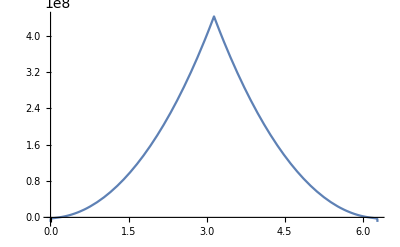

```mathematica
Plot[Vplot1500[3000000,4,2000/6,1500],{x,0,2π}]
```

```mathematica
Vcoeff5000={1,63993999999.50000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000497494862633,2047612690468878143908.13060049178594538061344176695207513695646579718349746420371916787855377812112542234938055424185377861445803212821954527800025893295356500143799789093642662657428102438783089784801648957581528880424340547256528,43678166878102110978031238057973.62367277899151462432900486608563380902040506448945562787318609930358213536832291319051969709635943282969416348131629851968311158989130732775044410889106453730269751535550102036640723579382741992930918,698781746101900672530740969673310906709303.6017084269343271112264582221468266876945639460924780873110908427087275357579771258835002831835310666355844173579266636046216951193807427843038879163791978850254591817720249843068806797078124,8943509676896942452457919216009794062607939426671232.16487237513508798005884895562350455197985578051259878121614270387455055638176329717233826643508393973342206951180305214995298057814760354594743165235471034957729098125481372745401,95387717988285971380759737139806571233935466993098481728774411.96212781134355624788686365397630292897001469393411267286671429547326411556032704273395453733884393097580442150666991729569998229051455916003586600755684208906943567301245,872026015263942923424804216273304234442151047290316620063199889439125596.7177594757500574127151284471105901891278870941259928425239125474337129584127450897997184556965144569443364930820035456327110021184497234254943023823839526381865,6975474753499064215617703552437356848063250834980988844750300467593548773614740393.583943464238286603485302351455706222631763709729318880487520639962518702374633872630125175694660285325504009391726761368821793815809563279608177377173,49598080908448284758387317856262544683550064900769892441804350312243853402507817144434356442.2219850505829163136846809157697101772333801891736018063144539908691366494365674623477990901949016328340526639835013841080921578808819772743,317393316909879450797205059128102906591580357472604197643976086897369340406526997267161909451457983288.0714972599749489349670861398174922669714661826205290609359653064661229032867964719131047216735179339811999216918285735921247723489,1846448896086767659915673092359304702952900109933156194162234270905868013884614414961604636798504307096714796021.37700823610062333746734213969006383479635471200508544071978410081846660591214702205650845146507833567236230901784868314,9846628206153946544805632848343243631768569148888444037549200151385903875341532859853795586955548841114396790409089182483.393272532484964532756570202022742143499602480434813787350272603463267986789964828519175803339337778705304111763,48470218289005361927481823327740637725456911708480115972333548784042633287907271141071864425714538401723657353596969495529928550181.6826215101438021056512553576827175794787780796292228314252902864210753270477764733889190589257912555,221552687321127896793840657483551933197383282250738224059552522776848534070059242574336604073727182545336804209706023534734035460662875777279.5995855837365748569174160038682654467706903050076488962198947776392885690320189995833838232,945181341140538933967726839777639103151298406474264173810091988457213717680202866105310368454355436927796099022886171939225702305615023258191596439363.909221075807354944099937966897207552593913777525568154561962574771684150297825991,3780278773792839334913698352760967294143783142074206161908804547643724649717873646794031009524548887975309558869595812611936605939463865491931146397952192592767.347680337359543046063426506956764625769589104637957285425084751581376371,14229933528425353243991383805953665004041202080408194272690988179179923144011887866715224110085736946361317374654030962489381362232067117432469677211199012170626552518477.34146882818860083165312736825411844437042490970428538625077916,50589178322609762855947007006003691992304485117305406522974736202318296582552225760372593370418729523487468079312840597330346916937249534003640748388550397904362967039306420822511.3012802200871407884449709983603144931253717485903977,170384693828792516660702932802937460746910639623499148894432268951152188138022358847232329989778929733978151624369196228175291191264542358620010294711343494465276982489668871535161246924623.9438598336828772260459586374575190435411175,545163072307269939303138362362763073808400455747468661686225924149724517430811405629080370356421650894507860402239301614792910571660108515589629344905789903092265618920100432799705959650555936897369.160559120708842191807637287407136,1661239610051875647928512127311178327522652651998638356484646151700486381636872258050561644888936037780350038511054977861281022962749227957211784786074812831347401855038136621852732047824118982332174143241818.135232357153799733849965,4832079081269575345679813035511808686985098522590249822172865679214675673252376871495619293748733840476815160046477307917204787025461064190713007267929256484265684061312893794032576682708388280680187172827523901684230.893606663838103,13444044084922232520717630913802862695247495564966231809172971582709065575479919590530747135878730693706592313888146774864859057347241519478189176063377934810585747711153180483837209857652805283266651199801095970488220048567695.68192,3.58460834187193440031942490598206117085406518327289641627126178643637705209674749904689519493413552188992162607454025150716630609315202475000604110051969187740277346680964808137424024824446656209192337260335078662893813329466972893*10^235,9.175379196255593146636185751657361740021480295722067283530757380565292016500035223105291763625077665516095991734969203584845433897796702256948731030442557483910429168334599008796356218258552542595976610494240355733764697094706248407*10^244,2.258251394734241376139663536397570286945685578259776348359375841749451398024651702222977482613707547852133174386291881305098437515247639338453180773721040710099958602195697983737027836839183409111990796022122588717931489531810129088*10^254,5.35216422408108684440155705208693882580625091213209366337044251437450319413349975829455877197603479247785575671620954234726432539060800254531301744867965149847164879011004880692135271878897271612648815143220498300443966256867994372*10^263,1.223183464283460381472674412978603735682944250322250839428728801834962443296507665284387530813227861717059603446159951283187919521906603183247254522564102907556420939823740976065127456594133452054890504425523149668201482860946537175*10^273,2.69906348516016572603834637201673218279834874192699914418745471221132129372228521226138190998842343607589628007030055696947697029954312701745686700115827623643351796807144523914490811002225966902631068742709965571586784415886571407*10^282,5.757190971518757137369793603194992550266064212547228669550895512229873150276523663956939926992303261564818997274766896290154154720365095565145095716232280216200692276460428116386141248915536099607956539293129216138228459388449654464*10^291,1.188411995179961969040370853974665052884104296844530965777363529771024267674825358113996254161226164535472788270093204231283890116854562485850967480644428872829177895131826123482583871421253384914081096154537053852170428618317029754*10^301,2.376481443541489489465733279846698336202130723501439910248865119002327563126245597009386883894405015361637977243746776107953841667563538757864867615992208167158759069159165686022940789478734667613730978899596753038465475891364430165*10^310,4.608261982910672307260862878718242032777727267401796468369604155356739691319546461892982546348493433985405267469666318997740619367134026092254639695130569852702447228472266630654899841638499555525435189724426417313816443232584992366*10^319,8.673097163023906576374070932932072626807233030019879194623411761195330654032959489139261297748841884395587251274770307766145503490147808896519834648400602574511772576611887419050174388056222228274801940767848192887160611249024756427*10^328,1.585701472146972715386862444665559681245985904746899112160733644700835801628584709346048497030130402082696499735165294992379125405399531494195255828298933256155591464642621873343975535113765911816548344127684473598979203182199105942*10^338,2.818600242185570216708133051895651006972819829692336174042239296593835316095613460594529813467260373983435742835389014589400566364003625894036129881891020681236804875591208714894606621936736299928218248302490077795260962876597130115*10^347,4.874674386223523799498173173671207106792592492947304279623184640062456709710364860511322714061316813471433835611266534709107010232985258468161211932552254171904714720090574492377038464365772622547151165860671304429811147685837042784*10^356,8.208714661725735400465702900995477767740544406966193454160541446516259219949859390785141153240613578500245903887677075048699156844854433773621788024584693845768493924217677408931653450815632995821360024305418036952711714899927644794*10^365,1.346861664406118357683906471201315466434612461742291833737052764315656701337959247633273045286375236105398611781435216747867154620605454382197808129547090925142028657712477150368475593846363432115917834724719903349615106858021140132*10^375,2.154640078664787599827687125083536411488062294352200459301344635954299388453406443820581070391061367648403859696081420032187766474995291489005393384057405861510383910477804313432570315087729981287343680866323519011810931382707921676*10^384,3.362806707284780738331760768334099240711434187414327848273022235381396330371283965046416296891721044599712597994738955717651626897595612588462747006616337314274204464662536810082146092946952742312851815034732928620950328661851492657*10^393,5.123455124149168308845784617456800330400191835423867311114055683251349198526668615646715106261085462098246776903712689179937319719453787859118112410906932677257723477289319718039817375430543239782066724937838130317977031516293058598*10^402,7.624372344290626272398022584848613855742820674239718177196114590534999873808529112643608729966807116782136735290573898474783781274108869238512047321355937351219090097724617307580410567108569324645305100005842488747133114102891538502*10^411,1.108818172691337534514672201839677039016407079299742443188725249264361801081895514597416338174374531062522540559956137143541592231912441795824262038586970256590597449388596017895051967010425525045571391426729119995132734383906784865*10^421,1.577581911476371138093549364294662481405876718905824768837788681248871061555914550490250554235664700933171614783952377384362007694733790023099602255977175896371067116646731171902937247344129114299722247233025902509102743620543068899*10^430,7.435079073791351706301128017307876361261311914111569702802678822564675905075546123420992796580304791630940648846495321492756169075008104141267124636134204478262089892749637587037711325182957883303046793051801195887982101551234654434*10^440,5.507776231765990416115753845933114974221326111503381854619696807845809393449782233508195307210395326170477473074491729510467760949776843056167875972002561301878994496073004900672574002818429942515920088524355402451267082460074027037*10^454,3.856659913216151816995501297921412621385986187212581207311169428786428173693930460333595385099289893251937682367783689091473917543225642737283491241769963788589211313075057867447083556722005787496835072613970738407734973436355122191*10^468,2.482674788154743867423733961017504409829132258450711760783430928681190056625937464908293385277417069487980250375411527202941950830406587186284114092517792265701486969729949448866318933401079290453156696865031961830246508408113923419*10^482,1.446021643120461660922306594112859413603189986355256853467944130618097919337752942625832335717824585731561887971980100409363468836092364680334679885199604193998351354131149125500399018345257869582910264100175284404392214575242303501*10^496,7.208512543793895586136618770669987524841565757721375531137112481933424801420740815969812169687499470729240473939747857488912057243244506323229094485178801288160152859651715462088270488822420774436148948920017992661906019982938242503*10^509,2.476875368447577281953046331420364204326986711991187200188103340411021372859044279485360558800800967794673529711056425814667776372787633600888576269902522971928507536791011317545719747252171069453006435500642575079643917841491334387*10^523,-3.815139171661019870203523307900514624062403531611881660121450802432698982371737368738938468583566028785959151062183882747135637287204492191170471423585277859025157748731215908864626602528626089612485050513783645191882520725845470919*10^536,-1.915298105069984703368819712185073751355623560400141389818643871478293403362560716166084196193679500252146910448657433531154615062344421154847566756862554366478983542042074133917871619430283371930518664006226945058516326688537824452*10^551,-2.531651812562768153612933052259892735286226849126585089116801521188569870548930658885142522059356830350519887391242848736710476153021201070105604602720665598435652737386250489808159685707110526537643672103866556445351303747218945864*10^565,-2.533799822138797717932451087557588195116754702143778006734607010998466678115797305628046346204770949130252503358067389897025997008522704079086899679416803965409204197052130534483105698629546489222945692354709257329131780839096461479*10^579,-2.171791781582286933923002043218789613497752796839768593465522018368800996563762681510063940813498971535190066879153120292820887942168612783310115047897931955830914299523746216226590951238767379660012579185656332873412697274289503125*10^593,-1.656873781032040773345989075542766738675435069468230189717650400525497324784416554131951586648136682988217634427451159617871166881627996619547633875296185706897312509074244161472560388095884895602529192203429428002714340554577627465*10^607,-1.145581633145028141851615352533890542027546351801991659081658541276693682396098134171145999425148213982607294943329591195457587136690155611207112998635008367321031396532691174082891328660129217000205785489842107064861039060239272486*10^621,-7.262455315576435284601588296090103890960481348576278952930108103913094337513237817867142079591468686515744529126894938150273277934637080256550423678474036773992986754851725384742754894827671684851921055779499077155601416966548837933*10^634,-4.260152322537751955197561948044006023246487902617808507949123434973623264235289434170209561810874462723262058776403107006374944842895492354310367217807893947837009203735716113924443600392221431994695720161695783610775389767852310716*10^648,-2.330089056180535947384217045958634368148476977485024814201023934163063423628074770869205619933426824857578252104165832819475860451770429751039200121992180354594544035241732758467098530599191378583505809133706928678858812247185262617*10^662,-1.195908498826173861932367868473349032977245409247485032010821994418038915301440360754935121298349725369109271513880440313369813440856068895278982191590550178268000231185399809531654437451286509244115226067183565959100831093370720087*10^676,-5.789848903580245343335651923114874039436913198119736951765608081203055271782380367397875024375511239173136600058952546113812344038615702421917083956181112660795542744822630061637133834215958222608934540289848154565151040331962175764*10^689,-2.655476540449565665780270125666229012119718285476217595912018595034480633821530512271375499329967885794757311722534566683672886383269961092554669185077963007862960172167917528611781391955925071839766681802732841810740662560058290018*10^703,-1.158126872806928400997827292574690901674071771899969181745488493580334007285864683010506431526700173009909200623341244234221488142580036142734825963998360830012997797049406467092895896744696780237219889559353436830012384817495528036*10^717,-4.820687309084249252855677767363944340618133243092616297889907646932800354928281699459840965502243185835336579457589942956212574984816704599899607974567370115769628181422362476142685431182816705966775720241770982396889244647414617414*10^730,-1.922746270546843746641121908771735450739499684050823866147711313300354337050564674617451174077075093187979919354980962772519728507514217077980547814305675266965403184439163702567065669488245771819211874113794247455454824481784863674*10^744,-7.380486983568373005892462499642453231220591750231016906493588534143542482044760525794589607516981987126041611578989580187884837850970195612850979897008493794040708874066743483285460894969775791118470122582368748702973706944212333147*10^757,-2.738922524368672652552531142683541476632932922726038589829732968420053528346775140662320240652471499220023439280349202408506615168995112280299237470507272090029402058969595417210872060815615555061650698466952551089862128040383976857*10^771,-9.869616700501764919840413874953910159757081201028765374377203824246421073326051308047256238154287680655286044841361072491966734503593143853320607439163471480381684130344220484768979708139700726354702272897459564411506563597208983547*10^784,-3.466008708023923719279402274187876808952083581605289738147546640170443112360295983101961881058452251564713767675461558632004970662825305044726574771604612682324699045227893138188320938103182424892633925522208788027814406191426891147*10^798,-1.189150934927920640981117259912698230788239166266134486046687581410247983187620539161700504695625327939910577813834801016819119150840896765700788339523840776375181787958209072463357085522423962338470061519373760695261010085914733354*10^812,-3.989657996690886015663179027735244320793297906477958019403360598367296866239522241228163119579071562171109525882834995805414913929257867978077496114849655755076802801577356657693437540249374924290379883151613663565056939671275388154*10^825,-1.308000154388235004310331713272412468745645342555214243685852760153854015279404909087951706684800014844768932306098129420701830646112725857907336264858529709079121000343924937449270577471309798557600378468759828655966165544500347481*10^839,-4.180077663571254491368830224043709396642609246684373148159015452964264956579918939703733646514933624752721275501750320824361600426919206862434103972153209820955927330605451501710436957915581122328732349745787518882237089165241368137*10^852,-1.296803234141860087770151599305682691461475996653661467012761053812504465557337012738949525486593489588416461660783679313544466129836851398772663026770808122196449651654464132166336610687494576822304078437484556112524691156949141151*10^866,-3.883567316609687909928078633382634389966852850443859251456038126714279026814620247476011390586755147217189755129626280456383248684901440758757570676695878261747964937376223805077891218093163050704700889214664496782551280840819514487*10^879,-1.114860926721263043973368512110689913295861850328040810213539261075608135707018896139038620896662554120362056364967277990872648330322860614748618164293843381249205529363020931508337400753266560966210721108372857597774238989745362449*10^893,-3.042306989258955440208511974353545322224736119030331857279788541818339836748530402054262568033788427303718269030744828423722803175003827712216020390711191165354135217698579641490787533439761218068113661896137696878054769901259191322*10^906,-7.810450717222511964797554912438564996747761754820957275050389799182492577838147279889586756760298390042768855080975791692091263600383952975918328353781716569803405637521695667226411394448809980917567827908539595503641021269140250782*10^919,-1.859934268189460948812501022568658608092265436047055745118666849099681814860027271221745638252511642375662422052783374929692130400568211105648863825939314065918308612435721472042438690708581874769003492436554525120959090580512017746*10^933,-4.016172140089322853090958515832618481667594626547391446727481448300579613521088663232379105833443640466708193638689775439060370151317913150472811514181828464408677153919531846036536696836121334850116566055971104278376296331667576319*10^946,-7.514027925788116268841590048245373477117095575126903421001249144733339337753398231077676737139335249299704047786741081059636417855079567361209570917958313906048822023770426544068524840715012417052085140110572240742112574424007673348*10^959,-1.071959870796805487912924585328248332095624463510706420361507964451090519026694083800933278699955186641697780008397355277579483781509339307720877277474484009140519094622778795156563413497479015843345127564124593142943002937884784787*10^973,-4.661476387518278652444307008837816713610494183656008408997562386860973376801805598502428878636267671006271357455421869618933563020436421179584399569977979260585950944612946537671158646295034517140854772172939014679701194304860481078*10^985,4.163468420645845316711408223592108329153499299152889594637356249371378597297240343946668111538016041937029918317238843461937660097294154369142156327030622102088884281583479639359427144728651416125322447518475372124280051467097506365*10^999,2.158997192891954967037236564839655733530751362479761678265052687385947751514000407005279260059979010987525818047328892086397797106007145602031633218877627398383618479657291215630909333998353907087731485556564624619692426736293724693*10^1013,7.361629981951357820465451576316937240346519741661475194758677902125977585875135032173162574822301320601275297803841085246376009035175831897483252735879164317636828966811837373465141764399132404241763483629056242119800260733167406191*10^1026,2.089351853512280239857610583681433861862388525503466730490389591422090594018774804336405738007794421838571658387078946725577453991708602573748371231164303199369044076295872148844884356060223400221393647556318379759641410617523996811*10^1040,5.258341151444392723449837245743612463876251757627943514129676211503654502936568244766050780029630782739508838150177761233556350753418623329598225598961628655620217320235501404485824475746521492588958939863620044044141024165928568901*10^1053,1.202154495518284512116402024380610435852975837309453566531585539969085815794306563367798197861848841510931979119549837027039550747765050770581188787348151968750021134886897156917341015178375403913192708666060432814509304965306921226*10^1067,2.517969900675081591490954966509391725632905039885903601463880617058244273117888910697666614581196361929604177749538135383216155004238477959760032928355359464020195648977877659541680230284478822985516600883588104671306237333989670125*10^1080,4.825340879828217897185291104871187369135137777796496596084047396673367001130803743710154105725793525682857101478861698418572156384051149493720090326335104625553942803524087685884055050953755864635442779957622082566950723536432046178*10^1093,8.358392961307552280990740254448881958379808262097010760695516650311766781882804598803385059776907954583521336285509150741886816662237081330630267366468137348786346405063861060307802707682329990028669252081158008695060610040139571622*10^1106,1.267883253836131976280316018626998962754498439486328251418013593491525768594943126198431631286682235804865026625057798914140546426948396258364545058560062933862432203833941286191325842069773944221175455037771530105290311522805615486*10^1120,1.543560632494259421436466398106763377399123914918372076727847008770749842371394934411872639738990374218556588601593463859654589928299941872494097238052176255776203250005280144243687737934471318074814128844268409138451167033874974657*10^1133,1.006779836226725815437750603317983258226461894218948992261572408677698727790405168764129319129908934599804009010116052950801303602608021306333330783671999108621020699235096273218575846954726980446302469458904234517050445141484387817*10^1146,-1.769640545613376376776319779361107595633503682014453820690259644326935714875848555043840504733676617445560374257594841880608352642789207713885738243314069155002202719981362049188569724767423985012766558190442345349721185587041390277*10^1159,-9.382990699536405178961022590389950928168836633560210583769007117672800310134846037311268257540438699662395151721193864818395011418566986836723832000521584085211336846969091232736480504162499988106688829133900213160619329415604883745*10^1172,-2.577999347647303795934116861846810214090469266569671897662164425492832735336802852623015382605581849316384868137030637476836436624178430138891087542265701090098856447000839721096030767217688189438760970799668207859089740201256878115*10^1186,-5.560452323313351957578378946932110311663494690117534008553150622935410953238000475747895009953179721546053553255076643296910322504205293644118273291073116752311963078367277049399550777923850143304500018864814112914182388893251944402*10^1199,-1.016305167632854500897301503332202786986009359657009731652322620008094459070516694867497051681275469642573274755201202368102459522542199438015250614114527200522487296817453580836717991483745672243912982626095175077497901572793536092*10^1213,-1.587127582026381123529277525104707904533472964178194804370133101697878897720643968089726961477954252772343684467648480935296886138205513028125675959911997252415777989936754361083693864562676100440414122119274080468957396459222209739*10^1226,-2.024078425687880916377993232298057664957536260733221003895250015890669906022480139754519087990527605468989063476951896446013970832224150724187975442150390407780356728010863431542880811713621275116652910971073586488473609572784895641*10^1239,-1.705731432586377988102553009514961779763987838669228373100730644712328906678403705394128494056036542387465700531194168710303423043840859629919550851458367879285335656698419876521814905996174943483026718456970478164050506564681142211*10^1252,6.31048079695329469087058333632278445685209124948513899423341201715602944087455207960710653612237383793322340303860847754471684071556444752028801515769779787594406941414178486380422214302461252445738048767140395616445990952613201758*10^1264,7.239412505768291278630680867694454791276276718020408747075339834434246805591724445136232985491919545349087273357110439215474391882441543625053793839353307505531469173735708103002739329984071498091429533393949293831375207308167724559*10^1278,2.179784574584052927886118684964822353420018455337163514745349697847897245824238940509136746522859532881267349609992782693281939705623299225645257625559273814234616935059133114666959970044357527683937612801912312849960335503849204011*10^1292,4.995758814473270824483987188682399168041465409751230918800376858131673940229815451844649796135936976922013243354361495674749147795635381854910823238136121900374379079664292015651640584796324722345710005904716000919419354699525652143*10^1305,1.000808170481413797470295537894415856554603331371914554788055658359457577532913809992590016518280973713670563529854338733246632897891149772890862404846921202765543884945679914527786360123880243897652543136447293698796430791774755459*10^1319,1.843323987400780104229305387316694499720549588958586256456756625911222440214916455170942502261999402929924881343875329540419732225440310386296135888249379629120114750108610888044354951790026908852252447488826596661044544589084947738*10^1332,3.203805067404589984663354320888008379650144334681883556510457325049575191458942382608968379297172996183216780323221759972342132565658545725356459427346956642825686737844827393901456884946830714974091256480577375636991461263469140356*10^1345,5.340150335256656589084867909757221813911815579584468338244082397405135150673849868011245870409018482772204192475945032367362762659696206433816939406474149580632520533704148123997287956860578579100419133707196980070758580227793114787*10^1358,8.629417646980841575396406881071321888820340307034229440931355652278561406288148025026245513214251391130739385231084802181833678070543121880433465954651712854958008300835949086687376980696734027309841644843870225716249085611847748338*10^1371,1.361787588759178039693863522973641920469898583515973521313267165745511490529242463504004978850353384352603618312860325251251284613128556064385601666013191333745839978468467969078905579398312047206676587044467743403183115833334074915*10^1385,2.10791381911121469020184023303679328968536550403908575472420326719171328673446229039356008207988752112705150162472609394639401248082055722219979547280770142116727808970892942317999147713810378488982634437224096016747894532993885001*10^1398,3.206987444893968886686782104127899705981677530776592246385707703896706261890013794617608766003438281027487089728291673828417517133275658771371066205044083602605376575234352254818364532719464646997423670830710662596437550338974645123*10^1411,4.796484992531638935990930082651264018484875488784758529110758255603303993765826177248819254252334031271167879113342870876811788206112028731421446467902756138310527858578190600904398949191233397491016862568126496212098714157761572915*10^1424,7.044576398466611816574354518271377996779750894479087729733458600567084158920896708944824670982384493915508592228733456062527916184585013642113848887289429347783451742176424663586888204165979571112643310478208943045352395339074933141*10^1437,1.014143533514561275817177672562015004253379039318971287893274606029099496081529913756564144597486947905816563457452202251905703855786553133144716941509066602676012036364909459243853145035950471407781706456287995451885889435860516906*10^1451,1.42803057731958806746383858584218520645571241380011050074074182652427187240878489936457422882302805788739613603431479571702893492595481511510278839490734636649015840169010695422106645120058230913632751452591954374913625389517276081*10^1464,1.962697396177972418362766638742147396242105568034869407443485415862336575702421342146354606314363569950738656540118150524077667987726264583536211587211553448820398882745728890667508089189308013913894341957383384497956115334337150051*10^1477,2.627882952272133452315129678716234320993835048620027539499688281224866284204558148648759490106450397162589488648131676554333905324897352734948078440514830260752880397223090596972192480641430446066074809232218766318778126689490615074*10^1490,3.421824111061804119409267188475775418199924599481650142199267163733472591736337360968120298784865451545591246490075892220760723427498188945914895975818237451425795604517037467855698516461861915755632641973383899777954749729204191402*10^1503,4.326876919364851968559567887730779512739294321060378284721834020585130838439388618440665057834081436404898791206736183503255466192933906864111038784182381917050850878517609917571383376807249370304373172520103332673375687712111084167*10^1516,5.306553840089515256760417931986778010331783222255640268638541085863335872868709593555223413923919944426519941952413711491766739423532917725188375337792254080993848194635744156936112602291138697811784980330350435360321402586859434047*10^1529,6.305147755930129521378619831880027352878263698139541745298866827714722042847956155712473536060733499080329582020856924808565238395046782491857989711907077794964764498033016215515246121815260512438603375388971669679083200039836559182*10^1542,7.250810074027915245598951204313751553005384033997500709449489463790410462744809558104382406105099642258001729413555572705111305987812978733605479828799852081281005653933641462135682850509001343026213945668624910785964528979831823965*10^1555,8.062304014220637594328673634987547844845782765904823160502317807730807685462005403699874311526105723089666276430969331230268804615215324152081363668018593405619480703296583185155174272489974399801086941378440322988338176543086101507*10^1568,8.658793392604309710174537240443437975618419774728410409640081688984369297676836698777989584386826738453995203177341255486808308204192779188754300689583900050705285300647463243094331270018822099966061522985406237869077079038633878032*10^1581,8.971185614898042874193203728325997155179101699217339804201599740077770699075605104329624835920349627007112516398498743054206530549126726210276610572390630909297024290382057984883919415740499730134764424482890532205534037780384941768*10^1594,8.952988961421453418994382306020362613411986521541660315837525389630440826239274869301430478248378175252656645353308030836974989988311685848771808904081386453507455257720038030527049846454958150306506421820683743279628130090934679213*10^1607,8.588563427722019246830903095248382129190839105790378369128500976887441905314526396604749234963150837986865648497188176637766642017033825191138594639124400088291940493606318615442421249031472167991242045141146043704688286429577849936*10^1620,7.897088514860998248302702101712652471965077760745560275165605437875302439955124745415519645919096488454253346612841858092339778460920914894263371357060397914170092321333024533031061845983727895419092718796985548601409502540630455141*10^1633,6.931419088839658405498667325497054719633040771101319979586215604459016454026657300086025399345813494297398708128617945738437220258295390828015463807325996832797152076052431618893246112964950895171874956089065148662390541853536668013*10^1646,5.772010082416383602421252279192035612197988027410825285898536353136568298743189285435354913220575991553729209581399840667941603889961816721055179122829512485511037675289471096236516175910739281699150012239293252589733334768346439475*10^1659,4.516994525611985350200834657147373058023620210965253603367346299935059399540545224076843489415162592363805428569007231756166346774826849648288277602852544943676393870823495807235405227079973051502808796324764317280270441888550419787*10^1672,3.270097919897095483143113509869495685421955638501290869252420390109850181876435594847415783164414145122887978329646156769848849554115223890176291180020470544091717493613768795105545616520440848575407570750143651319525088469443111222*10^1685,2.128287427089322127476486316075834705636110777379464565391739693324754011504956201568867309887836721057213942550044219396768160056806584047875295069595054613248208287904141636345489160104261685824398209241193720644555427854370970331*10^1698,1.170923577739138323216230921225531017868208149069300403191972319221776351185853076015830469347328928318963100490581248676551557072497149878310090936691159377206278155045807162529003604710047369886021733801284029141188866481397381386*10^1711,4.518065138889763310657946042283384252118422457510906032666181482376978325683170827847976832103672420696405030764535251993007529469010525118477985429121980550721808498155054882290694870495530521034966135420878677026717910190452694022*10^1723,-5.004153056539919443016881958921960648997437407994940538024871047581605188735302148540865336268529989569137023108161594699190012319454520655322463370571550704859737416533336826510484532551214374271127382782131742154552966290841771104*10^1734,-2.052863449927707985983785140909797122816428547279605857200849908782847386298223452540545645342415558042399575943056809553905105058715648608868625811894599316696622456115211541875471882783292111725613169041683605463307771537268294329*10^1749,-1.809310962315502240604836382576978280604523348467780658515799407231381806148658737270115118815911554059223417741119976481395419004364627485218856718597978076037785015081235004926511485718662943196672775244712319197464664202760108366*10^1762,1.681980787950153438050067743988161066904067332023124304337999137686664849456028404753083911563116483237687179408910815628096626846597527951069874272607352775983534391525708010533215427742653718194412067934100893723195601048352098747*10^1774,3.259830390668097542457678893453041267268534924905917408203134686326666104979741593068904249417853504375396285194731804898510539378681815732408651031544070771241413837289310448546132717600746547745547656493185598867490270290116556763*10^1788,6.828786381586201441664440907035667158235322148618521002242560216500648086417222358989878466536785820027870525385259586601028620613864067884982046565882849983635948734961384526785271694873782411311170394190673672759575522520791788637*10^1801,1.030222984139745546007194844072298090232608212395831598473723642010725157724593615864990459083458328507335505220459718284953972127899177391861941567152022492844953514980468320957196841773761099550728735057879019071029152788598448972*10^1815,1.323156747558564426509257834323662941180831991656357460997874720625254701134010561840516035195478301197639629475375588805078333964306721540724742497235486401545922215069800169534631881192964170151924419749645329703047522834508575165*10^1828,1.532563673108000901457579375144267505036740987898426710179907948555663994594452694916309086309025099017647686098088319339003806658548923428662474895271741942651236012103724867115006223606967874724389135718853759730385092213727614255*10^1841,1.645588835389925747446305478320816254209320049350636684650851574863211831724718091789713436366815146251970086320796832622129987888583701337819213851524030932637404262207917030495134627654992795589082396297901635526383432838898147108*10^1854,1.663770939484802625508479043053903362350748944291994991475816189156269433801053188852870899548861490174490251507603772055237345543780867223027821801570571749756093925188273097579274932921316754058142400441724582520179461633936298123*10^1867,1.599552671391185709274551340670267867842623689321207612383168730275942952105649161959935216497958053710913660004141469528963140972985802326891086098183175504104910236163796806805584611611786888289637999875958221540778143008439764325*10^1880,1.47206932622352093999168139946271196694769819304482845301044505625839640315286862276727801722410880927967299670018960197438480392944400918273512411556161907505724345418090430904512956356241627364010119301726436651819872086554144709*10^1893,1.303045636289632677746467056489630174895496239782513894916269843276991707850316750611249871391674615244131474339422028169998141630834408036723913685503620360495248943545624012846741057073458414719862683854544753668541784111049269919*10^1906,1.113411955368374228616208574848198663575164202287643078357639077007346856847067273061774499188005902524118253904716714074375704283189753856245705093782284955471197072162396851566899877971317129092398766980929750951195066769063289377*10^1919,9.209666891324807000208092709474237940777039909193118683900646141509117567090044904149293561309528522076473898514759266187504636789219013460753884301085408963127232066309147077684409812693566592146323139283007354999889499917599979769*10^1931,7.391411305482686764531840344312728086994751220546893132190128662693169867954592571539069018884221853552866816635363555320804841736741804465775369599675931359555593776222350864647346167218255303981617599729881587516996150167301191835*10^1944,5.767200830746672703119782953124974976540504760874648486329176000459637486546620636278985160471553673302224854327193584513838250215225005887809280934606125110065837761768360042031933010041472881749054462152831183020434105385059003875*10^1957,4.382589703918524520117973131546739507127749273244222254867286488161229387396997927771624404080408491971246597113908561061331160947937686883304216908936528419728529073608086083069573267469356276025975231271622519823632177110024616236*10^1970,3.249095860215357617209149737140401857557988866044246066714637806112440534797848050751285780904220447949708179622519122269323955748436726234409177910693160178743289975676968788100354364493770325606839998443599958477120339457774593636*10^1983,2.353991676824222190969407100815463378185412443798542591028530195994752429601022397999627295766297153420320060043404074968823933509059747842744120221376052570422635914196168198639346040440154753246948678449540254311814836143242058742*10^1996,1.669728718892804779058728033986777274665687518694159250633023366609298922383451052200946278617796327360534398565766532208837074793600046350048252567601643950646309656021203653113632870866012034994689607035142993784791357709972907791*10^2009,1.161834334444947926558141595849278556325111244453597162184493204644483650768721288610455474347849723426415006979095385198168680703445813252133022812727530808005631129380298339108611712888532341671113683512540951436710118336514417669*10^2022,7.947721956453849416130078093499124392952119463166063264000298185011733868846332841617871703193964579548093528643910919846082470726304771406368520811399268813569943871989042001249288468233901335109509675589271514428439256766537284344*10^2034,5.35747440056666097762668579530089302647975084051482929733752180566409727586021482435534275020929684907350383822867850841587037455962828423133791311989021877761338953258449144064476187645262593200362412075044499112980758936345366259*10^2047,3.567418460815485671506874280404319276153120832794498811483076382113616723311146440711456351208530969324808065512046947384734525322576079805864100551562388439302495275897034252264515227184778491155723968342054680001584636403873865291*10^2060,2.352074109096744029496988075328697059307951076356454315223118222333393647353691110866533788410110677248181319317582678943799604428269499662994325393246581205542312754019782483089748677123980998605645041549468440398143297060388364723*10^2073,1.538682725145220942492152675027720042768240182678440436092608591174840453355263037230483590658186890031885162313083982401320157305205729100305347381004246952287739918112833392232777828451011344580805860919115576017484584150515575988*10^2086,1.000253640760847581058252390249230494751504894355850518661267453348875296319908406387252973584698838198853389103996777275560443457424681227396282067922158035604574632324258580346122529210390619497867256616630946350261792868041222245*10^2099,6.466482307398507024880945417836423819128582743701456608642862007491416250195510013828390411735513804811664085788181898849249687470096823889920169081838032684923605101361905849984639505013293319298906449834929830915443205960431136807*10^2111,4.157013219989384576045726522231007962087644854598530884315945424467447466998985932958467153437654333615068814029541125090338997394290363668561196311321821747157287341692957839625731401724167628271886389512661524325094216131892125469*10^2124,2.654887744121573781100464403346689378576378438578901996346576315286548876409532818932455733799222697580085789561592832384096481492502783411007859110713681808556919361516326165517131295092632144219149913579872257540773398672830777829*10^2137,1.681767814956787869719880381002539318617974265628643519588560741097009918378689514262495957016389108765447510796361946537225135123354373507874546903907058068086144798555344234189701718005438151079280101822348822982892828433283529418*10^2150,1.054526730465532706069693287881109434313586968359536777020175800896834226464558185530278920184450774500452276680726099950024396250433507996553064170228615663843146227274100541317172477537521019978861048220709967257758278629908779102*10^2163,6.530737574753518706342019221325556215601567416134001815212571765312314919730829844444754705347015316954547424832210159710775070027442202465020498017653483475413377156968379081514030353676663442978004239654566011137594307710206760686*10^2175,3.986034050843221079554712493125154677223000297072839527423761686997882239261421159702354618318286282628873903033756202823062318936490377917210896835633900545350836752288282420721492536098016732621959179382736689975178416537851826255*10^2188,2.392984452124431397531324168837105457750849743236212892687785648650573813959624966822654082569646238634309177206428860642575005497016424696840305875310293258586983042818868669776101158007768480861773086201116120886166650383768736627*10^2201,1.410665690346026407204084496239925786121878430607851275003508508589072755912365895281324752273817990268928299586434303244057412517230555392534861245693037478343465293350024100239959791286939239512932521845528508851946827142610330447*10^2214,8.15430762288152522335861785975599416421825496918030477589160160215338627235170368481047025690630861186002135164188882027484768626017641999089242923214675386546835763373768431672793566696851059634094020365910973772703383999086745702*10^2226,4.616804456315363797449837572784736698282991241435007904468977196804526403765602270533438742952676913863438152282916122615126449147987087603402911867245278325545720474377436187439821537469722024177026167972723080510333980403236204992*10^2239,2.557993498052706562118750773385405371178173004387915436839033784124302193867858401641326847090726565606211299120726655605030139320158944071159671127675700180384847037715484593119035050821856220639275117324202292340384841261106466033*10^2252,1.385948651404609183961648365143633857060812179222985528770657154341755774823100279561048318847224184898978500725039644782804683938427623197841803498512037682580407737059238022557857982810683335442282335684865727427590739041011712152*10^2265,7.338652248475092717802686164784269864084770451032841331044933544732996288638971103521344811543872787019548663223393193262293691439875927600915816399526213804261008132382173398394999033420066223018558984990497048586904900594048248899*10^2277,3.795366041020268696144851813354485213794127518042618940623354724025382910626675999928241595223931042604007505040497148039800745051416006283062375888761091686544493285445345883566845760266397337091349477539360481022438747417925180051*10^2290,1.915965715449523964625098979760785643333979154764558343553323335391275934258105725600185904172255705070814856500840001093296661087119339932933986253713540051724737797720058217488709695822538657906814235636214824044489291414300787146*10^2303,9.433887852939419732279121267715691299278152614947005161275297064238970649164447977970072336214638552312492783108529025825585723397420325178926344758689145201843438807276848429671585166532502928134855315232085419352937631845100945123*10^2315,4.52617494049817790805522989711688477318098342976818515446021534670074001032215138936058513747831203146018106372800924250455498511863485228808878654651419683056761760771042529477321023184931350441786728648758833581250931430895623809*10^2328,2.113057572053545439317943338410781559352042018143985131083407207474700404850473185981272963275166020581555600730684652979462391026087884642550082702142359062767958530850538860119284499100756675937921118064634798521221400502361343713*10^2341,9.580141584326813995668152568209854480852307964939781086102792535662282954556877558288354916710068589234991115748747971097365004151031549259860906596947283662687845219404176688786741348834377170611972621017133433168719297005638935118*10^2353,4.205759228543063920193658818637400107393894439763776226835042527901711914057776314890739578938525667403304359320392577247750090522936236980767573334259379504190966186916641908073925911514822427198178262054001568548999496104428433027*10^2366,1.779877023239491484707542084152867184867309242035102499340238911847863019408884557940587968923549536365979343697087801332977035962655821509890228367589870228183245260660834282134496353179824881329513335507627065871902979865825676793*10^2379,7.209480930518838964518212122824915744242660982841012121620790445376207767431881351246075325739207750164429734930880683768718793757509730470426730023132380880543229758590852020048190547651449046168673355094398125922385092211946545445*10^2391,2.760958974616900041427762925458128477930538305628709666366424707600166819319937784425759183372922234708849202985383466013408050000713265622631326852660853502999321673418487628649366983087469014285659541662033855690352092940757919765*10^2404,9.765622878021857544918961869995442789747211505282928657787522837104669509579300331367774265321926627664667345294361991882384580523399704514264954073642658150113695800643978225788373591300649819825448947463030683944463280282370361502*10^2416,3.02504568712937317254461330596290396267407198461687651816527935423009586079857098432977971574987755426833542091739908179447020358029683337743472007082369347312275641155130152034571555557828442011245008411455646901633923825224987897*10^2429,6.913128427797255627826600594684515265482279199512324347488708219153303740760464256342088466870064845653342966797245178509888208906444124660671309257941884489577046287775821880502102544911754300113062465277815116761556642400884798836*10^2441,-2.676734289685666468547738505699489425595008197600454715855586479690464274033916915180629508608360316658057830760466740531092448056042129421996239124551739239980409776199252757248614051229901083015142140561302890975067262838387945709*10^2452,-1.425482077292184047556418255788884325584709710164901886355823278706752035782902756833257109565139634255155895728465065017685171058988105397249882188344203941834680544288912153600655815190870847494098846914489576619341598220096435957*10^2467,-1.25548590447365018366581755449581313574887770793016835145167684224763774980619350685830881992395172275885834537279666091692242905525164392014479273398150456240331118941939781639949358510833742285665690149901288504447194478052906634*10^2480,-8.22437678459636584229942237371749827911458538579910629312251062549817372165876933511337999424683627119792788110479244164717954286384974961276559695084285278939954850012928436216831760853683635180814711553414678119637220196778705163*10^2492,-4.742145082919215422038925962326866059395719775046895748981442911664748543962359861903120521359340297782247512697040421231219463728011195346395389860168601284456757953953394825849270356143093170532080963222135761942809288331311835153*10^2505,-2.538631086205450528984988526388656178742130503183039882896687620564265774958300760175099790287280007506940026448910513489221423970990480093093123696459818290816652322048018546578333719194409845790041193472240433464494914730448003471*10^2518,-1.292382138737878902470518257063471102744806132470392940744941914517175150859432660533158109180293402347480731684997598856565013191549649980419294788131079010356949109950176454564051441879999062904542005517149838920203144752957575835*10^2531,-6.337404132323101397288074910720616838624404460255645917560297764411773903413736873748117473167782764701159073680245918943883945343247929325143666823436832873172801509804185907573740940536688971388439681680219910702728716143711080236*10^2543,-3.015913913616893319433770922020503883437435767242501152170504638981578791722679716204380290266261356880701896202987595188271789444902447492471928125698785256830713436113159611546078280674831252930708206514987530890430015020692490093*10^2556,-1.399236071400422512031552076543289337188974119222832365339621280417272969398916330803355409420810423459596609801674441212044077230844180658928014126692649579535318626101412786735650039345925806397103884797631562026987926866616338931*10^2569,-6.345994808079909258861120577419925200132978176024490193352708366059180541225854206195679643114374252585437405747457751086550078234312054431693397884653220501620577595864888031530683111108686568646845949288753540083856091759721543129*10^2581,-2.817450602124502012132310843788789492131131188151658889861526543633102693098323545778061401430061890264512194444338173836045448119976668712890808756910521598268209257641352901200158184550420975768758500588759495807290340710108855416*10^2594,-1.225025881628235946633641148481539024550771845356369896289722596206373661109738861023187273909736650946859494272164310867704558453136200677592665035870725727567024947054302510774820265910634947041609954988317326313829012847507848149*10^2607,-5.214322304640981024345715749526133911773858347040649030677040830114314445346611689681066137165101464496034681816014371509038445915530573746056120127883112610681353498235329144426648234727456340393679991947135121866646126161366279583*10^2619,-2.170322001987408535841473282411007961465814910684244974408985542060543201291489450324468466021382007728590427322256175245505748222888964237658104003573597915436414915024001818376591385965589089015367971341621139878294159629667297768*10^2632,-8.816703317235868772127319374622014764208962167704836903782400271685524410842633210564362342458650239345742079080328715247152571191693730280948038283033868368886280551426367532784587457406468286223274036053555986253717335401565441058*10^2644,-3.486125768703882689731490049567285856848840673520315905030398716892400970514338036155384224338863340283200187887413911762744827658457150209887693648757374886389760283606673275657864758273405739097807422949287367116080498660032970124*10^2657,-1.336349833433563359145478555266714506780764269169979298407620695458930594546376116564581571676601750360958222115408465617120165112512315273456351344579160760503364219477637817532454547614985955252142738795017863312077882239225020308*10^2670,-4.937892823986855765499082218451481652241959053555742252878325736681332422286131305248795959649438521528836649396109934115975118165307374434873890803823015534842338361900029993325640268665423260167972936792807266135599450018211145772*10^2682,-1.743316595522135047712866895598482111130142991268701888235706787682622663719669237741572211416320551267888259971091061477807317375762648874506562367395032422149487371533066380233114481416843513686611443789125900037458322741633048571*10^2695,-5.794533624650697135180922309464210737525331762740195418974661432368231992671861844494603644411409069326674845505680697517104518490137613937861787272592621192034945189266686629155426513732736919965974185721101055647157279562575372792*10^2707,-1.763133032312055569425644537263956240747064831653805310334886489793488907086418121712284556405438528453676198471273770387993563965157456220362632910342437707146161924388649728677252633670600708059414766595003169442434637773954553463*10^2720,-4.598348914667765122587151948174306871689571358684627334931353418448291254561193273078925734228610766467494031255560567792497581197055867486512864133574376036652165690927067721385442345066355690273128266883601720810743758136988713552*10^2732,-8.108012035174434527829562928517345723969792669525626801381511601944932547326354846509964098386091770457135608582924417853497763757307361123246770639936989852746128481409411918220203486685491260450103348406885180492901055821767982754*10^2744,8.511620226068960276991120937308055298207454409855120065570365849696153828138225222103132989689667212192103875933370357888112082862505110220904565491466065666011885377290062359134213787236884307983278157313083255203972156163200263882*10^2756,1.887588733158774943524015204499724094128787065899526447632383101367410840873691547782731563300030437851409042798462373799532068339465461696201591873029137777015789823502041701931501877795278246044088062453885285833823540436310364362*10^2770,1.307631603063640975950898164400643661489581173461383846175455008043053936870125511045673467140360115776926538803105854763400385986524924141518624558023257304257880732442624308478977129308174968730058477725962878206677052151327763309*10^2783,7.078762434623137750710129074682708067675562739612543775344456494059375170557477839415295285352454748636991617595530304334120800579262904878748470582233247393474399292129911570286520437705546502553707679154341028576569696557787793225*10^2795,3.399325303268467303395487246354410114783254662417161371934496741594440213857319719646925891218806567343088095752401205748665970475152200566707802747435261592508552744904951693045007188431707442774316968034880249365221174797702839502*10^2808,1.513150107231884426668758510843638730783542286527056353535713461651255259498949161874208353229333605407075706946154485046653804698637739775722881715106681492088728466521603804585540943702479189999408704785694074914547668850159557709*10^2821,6.373020128683144697053934147211054202938161099157086026987957016120983263169798685305315772466037614499571145164639921557424429782305533253772918631241326813329827081247394938146013796786633341612455811045146605272879314547276321206*10^2833,2.568549969316786115797548316260232853010041287839618205315094315483880145498516227234472270714609837418993938771451083018510074668910358983630331645709071860717005086178378002133817059799603431368977603419621035861507859837800473682*10^2846,9.974815793945467774712024210620376639063121637719628161195638117704524514094441057653798460837835183878302419704457125278442510193324387161653765354440597089840994416299721236425656102190684104776144710346038635118264260886176899353*10^2858,3.749378683324703733767553304720695059473796819350226813110657666683130592190078745027929216875737974719074047866833375019465536271228377986137465062075636149773822619396021955385505386334244293603350415359703766349124240690337551686*10^2871,1.368362206459888550169557597953189048094465143949382551767426996110620916367509043870539983553011492439702527392669948602131053197807237717033733492739970481473128467210125965566594393579791224443191850291585640974161098599698904332*10^2884,4.859378254611109289686748464370211576659492510736036934102892381442902335940758485256849141793739853756197664690510500684254497042326183337124857435642022812618304294803866421235701859268677145824271418590190252420486050864782317922*10^2896,1.681753623888023991946387552090464876012491521477332026077351869262414074013049247028522653963786084778113949012860715484086240444837467051012208965625758250854497847514156864625813481058913978508838546062596671540582175165112056297*10^2909,5.677785773332676972861098403824368966206695814379838715347884437416383077792119630212272346299986042039737511124137783268880234653505559733493423128041229410786436778891423645312521130919490236778294893281586513846336860049426895557*10^2921,1.870890591150466028560547560153580804099994780981734707265439123650815714436596638820961781118821237439821818268927324982855477352859489198560347950890385207242344169081063156091603878169477725839534721802491387890158508646927920144*10^2934,6.01666419552054430618614880154103041445710571983047938422728929575197362436413239348402243984457873867270731186975616308114890843289734208784915142820815978913808860524298643132780584557454591499048197387349517084460018627336212832*10^2946,1.887116127289765246395637317203995719919809399781288567504237446771625153437516465670124340935032413927252032940924033814738169129695552677560314350260719508079568147352513809383945250702865897694138908934423303294205529468115787539*10^2959,5.763384030678670563571556648580565531752325605485520930442098570027938006066438704740873366413550844359435828254353484067902691921917448603746961275103400741203970690142613308873938498930818723506454533631184355233422459919835407511*10^2971,1.708818007799214105790442902539137820613158800611503015927316237728849184733000106025046466506996786723199366594966348204094848237746316602990627136896490783875401437664492455200243645111293370087122787787280341622334761810572126724*10^2984,4.893073524062579944043512928370654220842605160749859797616007994975444154949700619202176778256476096566834153723194297771314882462380570933804383114301994943011357669285901881234008319289710858254781783089833462765713425029369228805*10^2996,1.340669735071776991075275565652670511808762780064308975603881502400879660101729370091041814671032740223283822760773059172449234022269214075410416018586808785323208985651478936572302293527280406152761237426105988148178641227469361036*10^3009,3.454603233599126824689784460857439160668540450299469799187942670823702596261323931959962436455530870539796768388803424786654481684302253577245886004225954536264472460793342045381103643884985231106884345294508182180201181468458517547*10^3021,8.070493435308863262539418393515412356944036208484922513317492630686638512966321671955987404201970436575649737114589037546219643293193256092804728450769370960530143550241585896582166916424221893739183161002576094154474624751168279501*10^3033,1.548378304491758306543007197560952611001594246062702253614550978578765583350906443342087883861498759147249228211671695931085450162637841936356875606583954641385416746548269968306470702392690131130246749659043347414499212462695882445*10^3046,1.461078885376756630763453485646289733477340540688546640717648020504047318646572599582049578865935135252467030836460817408944594599226069203734015726689420203685455195267427999884563389893196894502654558046928574312027363634744549295*10^3058,-6.857169177162151704407364857291671199291518254369871573863987272943174084084377518487994671214280526457150224594096299734338128860032273360143741410664363966899312253670042240730489392235921690281863678278196524818917943298086289298*10^3070,-5.916287425594569988494589376097212616042736354478013638914333739666716104209289031176800656991009774852364385912907805059130373432163208330281001076621384273771661879807909274723320504771427871808857286175638734277365009771140887383*10^3083,-3.066715394237455158488091228309025831030458930921063494546733369498251547787438679945121325317711168969523721280266113124202539006566885523801690052209633901493683502322379803120033887543815659980225141688690140272534513888542714284*10^3096,-1.342045775845097014981764557478686423585045816084994180069507442095690939685886523473506111314308681684956674894519829525801044276900648880766785188061515829048185007609418730173142337968966429610868805958344661229065697290756751001*10^3109,-5.37156923146655838688554871420145801292329923054908801206936823631118744369404785958748098685928912120382983546845467711579709887498639938478441291617256774427620449669253323822936330778778156524412473806417796718514322634273728207*10^3121,-2.029643457516982425384447417907245349365515328065609015841377426012563420994558619808145873277301455827755975118365445097586174706747821677562869650409589691381655011799604469847109290122077534340136505769980810824529650220298307712*10^3134,-7.353965697777400591817448207010906625491664329802580626376646218133104209720677748959495062259749390476568211947813381710281351801551034520536678609593402900075718066895047203742156655015559092464702092531278081211693247832829770183*10^3146,-2.577735361144582346904507364301409596229947800535167052319693023604887204383056141290701669999273437836339143509012341245114506025076307815336373122343772353506456319867940060641356633066607656165955985449215526518874036360985970879*10^3159,-8.788769983271102026483412081550911817675481590369366652362178321201079671391934756963593658268633860982777319020381257525599812977772526928867883694829584306379467986449233625974945935074312181925896646289342146345913425465850036487*10^3171,-2.925103237532407772136634814078410448443390370383630149745897900294813623900093489310223490994169911249661191280821506445591334168710509034311366468003613475477896121217633912365442079358085783935731273384769641588185289888486664213*10^3184,-9.526927242398943279586744427342206256348364993507737458720589601323541118398745605690858443236933984846176899536252830608393654530694031858721740586949473471921164701336920182637527123035478803732588477900640321291291500330570870612*10^3196,-3.041889838048185288703384371696121612530534057131928746949256778162015856250650245550443411172357878722265497908514084243642993397499065952234338483361915726210611402810572233787789785114874367757260654547309123316980165519441551626*10^3209,-9.534590826179408903566571512219607118418038399825868060299219595215603377936172235737947180043328924467708488648048547536215152437117986841847739949908217014291919615989010192796143722711819513895049505884162381040034959843334579051*10^3221,-2.936889481901724887139293662035163318105237615330858760522819380287842031706843266161998956811134956806802075731774114940493733866206284159660643357538091451840943059003338199129568311302019361986731816397476126109660445854305347001*10^3234,-8.89747526402629280039934336820356603782728685708722340156004869571062243437400987907910447900387865168419232385047896954388701388169029044084335542385544790880857619197256388998980895981293174575271922137613971102462607304653492829*10^3246,-2.653000304852378959492891487244730204372566227042829120596779230994939930576207278198107670044139639665989697240653064096214031438032039244969031753144696511735661642953795201014131792873700629986323551378978541044898510832669477116*10^3259,-7.790090771816130100817024724347053816609717273015940345081969312073532253745500516671009845407205730700329799446537601257329149309447891052509208545321529900605712500794762004466048200217634514814296551349632888711190539639373157169*10^3271,-2.253621266255580211225288412541307336816866683748956136639418153759617913772151186144539061224299627810559057711858154211690468475745833302658662616339235540538949308077048785864369977263839030074516079477822450153487871112441687477*10^3284,-6.425580682126147217561679738760075551693685191690380611498566869842389889023351865879972431608557542736473815306982548298628377020327529868189539474033491273830369996078953132622472754310124319411719529860454174227152620260019891041*10^3296,-1.806186183975187705009003478538600472167134245744516755171221988913071079372777957445672247009379432176956022203286834414765480530938127332489536139299922929625092726471793546894967863935669858681646469832909142480140178136872359718*10^3309,-5.00640957372222372628095855387400257097792638801086328457264652496640219125534067311843280113473202352466427068580347218224672973705557276114340025410183522331593502146225401700635252239493102382758075456282592581065706617569612108*10^3321,-1.368584662488887315532925138570883208603452398314064714328028497084602106078336961861127021113300139031987608461995165823167273223305012189278878255176932793414422084242064734368195957977554487528437677459259112445634538008259580652*10^3334,-3.690133727675378348073441516822485094194734457847274237651234734737789108667233728326071608734117017351273654516419471254929347892082282385354390036341879774876772075848386321637818906144958758645522766953828280062207630229512494705*10^3346,-9.814337803078614338687591294270508327319770618685156872228419111355612492182371208767995952194463007096353397248020373966611998170141489889099328948956868834460682210704853321726949117065828200188114377509231761468215003535966869515*10^3358,-2.574750912268108221464661254936643611678984509031999149803839718187151804792809714395114728919797145808323379147356330656179736038085782714379799330095735648032071886152572464377959020329251662040177740391596301309197573839249385757*10^3371,-6.662840942969341203455227756073738136823473299165729119312929934226418697117784245759233097303524305060914699552074869861770423457607521716646677921043055311427258262378186955300546405095098708144376325298069321508630485350370587152*10^3383,-1.700672768973869552579561508978021484093612442108696109921213819131171228025939401950824926808900882557133695311128188666733052666061500252179766187005084345053455404299781825908262472551652025911450728553155685905092450257355368451*10^3396,-4.281573726253755140989399188596731834296491317817086697779256606305919671631747249152310507749021268197372878973206294886644115166394782485668440898951556308879327497778933235906520615548335990135433947648959436788821929490458076848*10^3408,-1.063148328703404428996610410694678920182426008984450840298205894102574174508813149010166488258770381640474010899157397452615037714834566127984050921367392222568726035941651282850739123930329689421140787684589029676332606689648918013*10^3421,-2.603668376870080695820879095047711286817371343018194066819393222668125969531879056785547838488625447306244351202388062571734691758508714348156609795388926290830241460503775263752010948337264832225988239339580341944671381989212771047*10^3433,-6.289046737260208496827319478767562870754431367511797107395963020288714306919090864410586084323080696574052843720392130428794371364385332832252107352450849586779462914029118513378218781108902253587457723983712910331036377409619422364*10^3445,-1.498355838664060164342536369715806607317522856943809283166761534315430915511630098512442517264663021326344912230844611765591766484299806240414916204015684317911395141348244481986268588078883264597473973464924904199620821137112408365*10^3458,-3.521461416023238674141962793103357701017286621229206838975603759157339595488938650165425815822021186257047267494153025054918782435773778992854822370532168103640353464325836119713921725380215195790197337091561199486795622021495744743*10^3470,-8.165535018632551298542381607441101557026766567448408969995879931832790146256940596428785495625978141956965796116883450541726453858024112176107702078932382254583583499001428980060311292645549407042522955755582165341948482040393222342*10^3482,-1.868579067894399039948963363787487213991168540098230308010507104320733770869800693063378130219587559895602327661015509225174388040574688042119404529802239366544126750676122685761777734182963416171870194510548544071633693665132969571*10^3495,-4.221408382803219986784605084614226920724472333222778452659724397911912301858535164386880203485000703806587646736879836238122934825290081538447419785523208621093573508976225066251915236869632460646680137493702857778708167152202030248*10^3507,-9.419475882791351029230982010885806048456882082456407480443629568044255696754255346010711229709247953148012990306502129096433886130220843574534267446013605916536789211997560210226125170075950343733524792712056218493129793409919001303*10^3519,-2.077224356626068112969897138386897040303196772943912201599434782894492392091310128883953739072593791119550662087614073113297262466022149046436676459502752814811860719746389106978544566710361956806449570606562961379333080986324887475*10^3532,-4.530648394023080291664586966298702722237155426631496258572685976740268135095950164563817193026624561178023040793868204090269682844500160555584207695062200781079821432653540677621822242280711097330564889893510860711291338128502073695*10^3544,-9.78295536307457708310079581678095990451422674318321018761596140342053766259078536043682572786958585626836410343919834432182143476201392802509743351132948049708351840133825028251130428719992701444569737378344696733508159033525418613*10^3556,-2.093700269301298035383379611280886658970723184093364585924848882693422393373051877247225346134812292794764418537364535503750825042724853690479364290968051620462927878154551604574175329615014550272303999100505909247269087089398364427*10^3569,-4.447267745495396783671256603169626584363846105623378755867890379200236259546664785031639911458822169618654986532729044965761347247421389494473493025811338914510788949006224566970072472965578611848813962205934661629517792850294256276*10^3581,-9.390904611632316126990017909149755897864972817239714590296243510390840319295915044236074151391104880643920239745389742153586445024414485404522483630660376003521428433138401784317449679347007573115531382857524160027594816782095373367*10^3593,-1.974946884419863566295500889386830890737363593310777200086224756388683521089698391704485487191542740473803391356128053513279153920423834624857041624477273049516620852627388580072128167604662909206782557576075722620702543293097109679*10^3606,-4.144927270026227857773112817132040395894635921456530746339973456607204490880850793507027824322133351887262074981673198747600562399288078923025481366452411244819842287382222209252758488784134496833210404611050592616851966296750232596*10^3618,-8.700020572045610402319411954996234955650103608020858841592557116037259923786796308974576261379432260217726127126413651502215972791198563669464441293171931592861575198290755635245014051632799585047233875278959083946072960173355345819*10^3630,-1.830169588437692937507733120329008888323483652302203258926630577898899709004773867502945191696101775484105377405980665928309169903229688361175798651268079879095558107271615115394869128845538804579502666103319551779263336306772150239*10^3643,-3.86620584910495632036764266660938418613991924141798588429803012395888509822370798351624999155464318873508297152448854227511993024619737492097254394115246903734767500596604874870941585547869590620956056275091115418806175786900868817*10^3655,-8.214992915632386032710844903043231734977934143961221095831354827095606350015211859787916899803245996807525026589524719751016642213516729796809756505906759401791282158602248693736841986244708661507886705050590242514377742229498018083*10^3667,-1.757685000754296628972904387086088007637632248092908908461815658367543322858801318353958689103052680485982923175619405403804333565265076626756287219245110064202676663796489205543015145637278770064901864514382954765058770523873359243*10^3680,-3.788724224587700236620942018237614479177441695624614206790694635457767949146123096050608651573726282692477949308957277530064222902627478169135211173811258423490961161629168164142940275280309970153083980860796703334617428579140125116*10^3692,-8.225709547312176690553132382656191833526469250171124858036771552878871655524346658744657385562526794946731494146821322849198125396244000172918884338403946527773369550151821795289780039962094062980527198178044882018505636361461498115*10^3704,-1.797281809140891471004667150816058578638550960776015787197344926894006867064122848451057044915096316914572733400207880566561749359603240999404994243285531314441496053657258039231604973039167603831296468626988450803214504590707854076*10^3717,-3.946686478609987445056519345599987962115579430885562856766488463264705825226373089671465579599349826917810126360718026696078987739167854777093901557790888242070821454855558434802995256394568229369318857830905654281805951747252710382*10^3729,-8.695299046453652088842133293666543852584186226716053616876708991876455570605793834678436440688352767088124102313860007224328455761477712114829405403893292448755239166240657612034836212545901462853100740739496990811477368766055444883*10^3741,-1.918497371358169475273822525330254105429146831557560426126734659092633881871066898579048845965604126431571002253381340435879503331609938554055271423070351574408858917796587921133894754103332956475413310323644950977448779483361533958*10^3754,-4.231037583546749015653179235730012212306514269000167913252462353363247553348694941775218961210706392758141450680789369982117293114095741022814833993816802943792177141801593981195046805763854727855541650855650165175764930326301665043*10^3766,-9.310458949626145973454649654545064128153709901958896868225623261085875829793799100448980925949338417800762915318044930059814306811217453303968591687469774427244684962208472040140709561167192364441439961141334181821357367023635671304*10^3778,-2.040990499118009034026458650161483249917095637934405813132471836241749454622813439564365638039559026931821615597090124841224418892146338755122196348661819657573465871596008003228179276504377163329652691277009632257815326631459771483*10^3791,-4.45100220334392219015969206068505108184498274461742155727780953185205862401052580637877062049906466226197943825592615361447301625992812379607447970890906398694570131928297640490034137678372793917347300049386909600926029675623508572*10^3803,-9.645431439430345197101434112111637799074928146719271352036528677921044380481317054526707970556513290601465455935840151105170018227732462683672095952026091046212053685415614581872011246480151052016055915150189470374013022528344236043*10^3815,-2.075050060519506074516835176306171719353904623553077910868705443004943621536500851451141090309848874542338376768585987361566545908358580218568758796836329172608745300386902753287438781661761052525376743724080066259761715937789482843*10^3828,-4.428568246672215560966051598182934716699373630609764185619344159725631888987321483516178028146377212907058096611703736447031732968295859745048159489753304029464751936322951381023007156424178273245284288567756295129733096413927350173*10^3840,-9.371090837292162131579738161151608546297020636981549677059660075786464030218002138497665147916248991015956690190903240766241504195330482127639409918086806262347375476857556892041472519277522703536362599195482484474764009113943848408*10^3852,-1.965362456116707958983390970777360077751506752186955494195116900195392742473148923385748242496254634568994691997252884399431587430334013408895788042095452364544741124445200473770782035482891389067660148614024326355461993860578889515*10^3865,-4.08426654267687176103343529364817100623312836054250701024616647750704569865415136734444706709734236752817490131772247075620865629118381577396045817192095386935611240740710702724264288597297198610314020950302883204341764126212043407*10^3877,-8.409063461947682087529785299636150746351008109479372715263456281497530581963440969684604348570363768071181967713981687338026819369774863091913088751065963374630952664881383784704855198237056451401129699407681978646639057917074289269*10^3889,-1.715249999425666765929252655748881317481344555998931534411155885784156569863094955618966592615265887382297860206091070204732250701948695671771439853920854064335742966887488806680685368048080204680529295831510794329328748520252035277*10^3902,-3.466328826348292761125885319584831051663547878932772559470916248901662314983344677306877569988221057749026363889777441079714098838084096038334823876212546546858571197443995568309198001235139666928857992393863299191708228844552209154*10^3914,-6.940882942733041293179090219207329435170346425120920844835515011221372876040220502529702735318937209367721416317036198503451530787923266016313100147849978116049213134177901130296192620995470787394650575617956742401625102977145562058*10^3926,-1.377267165258395573783341818197694729199027362721005649681799178081457090032660197357666404753540771116846922621223168790111401283818563336642951377925575949127036180866262173305983913771913229366162582797051639453107578390825370274*10^3939,-2.70859595777975326167556927302598230699784472376641986049104363830659127774956955117305646379930607421124286770957184695396971145954999753174502027105333080499321546239761509884189691653055486242762453693045635168290262982706048277*10^3951,-5.280291978066595508281657024013201162099058493604047146104551542987936080710960705736670923285879786444134194128443211382292352036220508341582555272490986981905237390017815218307477647513115392850152508218933822898329901976231805729*10^3963,-1.020514431132071697900525661193728276912486646545571603920788491017292426408870924747880020608779647664071159607390876283549809460032843459011903464580482485697608587051550935225878214391112618467789248181224633022814821063254732558*10^3976,-1.955586062318935364674437964215898283313879224104469608946129520505716101423861813262281179937354398140876664952880033248435742585764081680308862672191976561770940116320577317422450640378905642147677762154023696918562333462585656774*10^3988,-3.71591077462732945986718640018760803450139830604051707379115418776061284705676450655192164947852417066905134071282350777817704555299032081412654286397368025431467763273452630477673922773684127700605783118073500962429258568452231779*10^4000,-7.001644339346730478912497095386985035596549525111221376463964594035355412609863812143336988097002289801231888973646043828945194051398405218741978736007738202751781566547575375764216470958198811959937195311208403821397406638797981131*10^4012,-1.308209460289242386626153484965807712647657103599806482306354173412102702282853890295034842416222161986037803795769032876408215613582998572069121386475029590710660522202747652291163741626746618192382864413026197178391671566055615664*10^4025,-2.423666540669916693886615837018791640422032352393129550298505856839773003610444566542259143240530542851084708773357925378949606874567465028656513526404048477500413631406322909907531455250592649495714585450271999350356851652823474601*10^4037,-4.451879075436696821589864621377072849781608728820943303684493576804519686887489071344979698349961097859191165813984820049389600173483360541105653580052467590990849758816082728793587948866403842819376680624127145248617331926779409165*10^4049,-8.106397763096430528414034915543625066419482663803488375392164259037546075601158588832672285647151328958386692556104214401901191498951073162484306677202204247420361788727681006876458221151164085650151851534071423056335806198547032581*10^4061,-1.463022136104846325187116047663436731101819976417847194559372345769961545771292063816729936366033972018707844214163014252262239779747252710358313820355026833984442317160408920956106865751849849047681150184189013517771936591215416303*10^4074,-2.616526010674384287420836397827189511805355522931011869211898147418605517616301439236157596043944961985229854462850729802677801194677657860829945454258736417575534580734861785220270627948345609710515698697136502733709302223905256256*10^4086,-4.636121538006656564583140604341570645899072310297286578783025791487532153680161742317813757856516140802045602984504656521906135083601894493125709541960505067935948151647243734475710683491535325820261814673277655586032732821857641569*10^4098,-8.136536715958723165002333411171695691658967700983619804615695606804313597644809288620874906257812824977477632801138807997676395942751287819583330044525011549519215339831313301256024876516972403196732560424632306586799723887140298708*10^4110,-1.414089523160488056315660518805137728013549411978473859684132557857169968309642369769092324221447305048997585683467166784215559051498434629188628122607086000248523570194163683242916799525973822749915937618409950510810619844868366931*10^4123,-2.433129148568413909136371240455240671218267111952568733577308628345033572053614922390447515986159961286157222932600244665591295829447518379577367235114144615529038955868248678786263328250264109507746932596866228525776700061868232157*10^4135,-4.143869312636597735931237992975394058054579950611185900327793738387917187611795661780360138748501697820602035582340742208866369090688703658540905247193655405642946425583881658060649481977214159943125685571682245198846815475683114273*10^4147,-6.984038041128352132771496722942551730336776351040335954854527107256871677106074914684402308072404866094464402656996751006562497337104219719976203958910681397388399278898362887304804461453681432733928121307828443003190107397298883077*10^4159,-1.164610983232980537609983562261612295934354777909241629588996477740464845049457857129551650369937094290483827841794132361055997409186034519217237676233193448880333840956765807858681190991470941416941107029650697877234064084500484017*10^4172,-1.921106883149110656922678095596013886054446509951092918451377879288783096420663549162003689384007471758072961235307612629497926885855433457498668013979154003250802252355319143950670392097652966600101264619236506864044876678923353042*10^4184,-3.134375596559943409573056910386777406879065040697405301992592817422103228266057725190002380432859125895160173497589775797033448638901923327473898659500413941691002141576087595262741294876297697274199483893355007510509696652916146774*10^4196,-5.057351055090324467656571667119681980954177560006282031775030939198636432062596442008163443212678362357205192418394735924773867337824732748138238337944420415123620287202675432566360958791592087302660089657548546065032060449149258156*10^4208,-8.069079566280823756315374160102828026137430638002495901369544209734636388920261324487770930070835153593825833077929750252559087707260118845442744934037386956526216515406066669541893049399326479263501753883401469384824942649776694317*10^4220,-1.272987661093239970009000265333238809473067107816559195652274161548058621841059260967413905057861613582029172521476347243459471960909024015231248970179393150059324403791260865578567070158580326683517383272846627398709480335731141463*10^4233,-1.985684588281472711891507496485620015040062790172053140733061671044780634068811765702387679976871564230327799752624108953309457517828296634621595158217677856026728898385292317050542068939960023111784533569949740239541812416341482115*10^4245,-3.062578607932140314748965887802048345708775849685363726445177820952753142728325242410961858208478935662499962650838603007157358680255806176696928920283512922716559656563522774342995834870738245346461507518657020254640170960562534415*10^4257,-4.67069491560383038275860388882506967262545700925198504362609003275051911919321427801683049408269203620464966234579072775919471775465938119978755842002758075133072307367792757723221314501171657489428697672535736218298224931220388899*10^4269,-7.044403265406976765057643109558554097544981583061213757874726847601627183256022696083458194518433365380140262851285170583740432071402160169208552082033668812008746899687415158423916818211856653508009481558273417651685393881497097875*10^4281,-1.050885658461652145653471227003368640107612969118812243382864243856239659565126250315080714188966385664795046481709730853060429815520305097906193093928053713087273366931614391095844518111457829055620149308520397121101852699676815455*10^4294,-1.551061354986583774452885750453616710933009366252355699914612469911482696515406064784042488376839743304957800211533477578440831556554277695547518817193740370331260297363699254557520075042372568578523416137498144863765550653698487151*10^4306,-2.265777252794669680837852443719796612285490243304325730939710448945548368986106625964444707175167740343220315430119410016619744527834191283874469302219590510149976164939323195303808354944685212036828959207966211033117549863275833902*10^4318,-3.277303276484271345002828091220423597608325654298887779514909027845207629003760276757543413361477709244383349141834348450575956350084797555776517845722969593050962514595356018965934662211496612964953657329829399158934636211886186999*10^4330,-4.696479607028852514098440248439319335925636879831562228160338749576715145079212849114164222392194191891307714960177864436750980058447016179556182192271535571013251182595529513058307469794618809649469990306404893372092522890696790517*10^4342,-6.672397198082384887180929241105611875170806532622413663246472549768508794224243861591596013816969511042880066173808988011478955140184516429085915544884542467260057940566055931693177159110028948526044704608144051302257732067315571036*10^4354,-9.405779392139904365704165594227510584645657349395866090112961213058523670327932748782719583617050973015097248889086900061643950500257644851949295604662319150282706606486016385532264536482312846926814669306380376985465265160376281697*10^4366,-1.316768414590740542560576234213721889399455031254288537572374161309600848356167553407641890655295007283783873974512712156349839446476833333675088495554353235819228808790230676744886211672382898059909864750298218544467142380498528175*10^4379,-1.832574722991701355213274385373962984322020253502580346481037112145869998292459903514256077351032702572879676384290346200217250855614387812525093078711268655012226503351824601017210358549682245188640231254000796921030369849224485082*10^4391,-2.538083044951279052418298949812475014628137244932517987619555465188452341700665065052112106933612053735091221559951954564509654639136181725986355191075702211439522047713026902034418750019448632826526925622881400520901722175532035125*10^4403,-3.501745154504260195250863639863167114282804821807158873543016793420514197002550730005509578219513589742002128078749792136406089678898211411527304895519669471559487615588486589531223544020664962522605881148152340196336623421944102967*10^4415,-4.817140467007607196334258562190772822682320153724111503636240131844631962097386744259210957236565900344876850537385024724987331923868946398241709225057757716999493807487678069197193550927597031203346838574346561563436426080139943929*10^4427,-6.611690807819767660685298826301948440126962598358102970997473601871444337768017094688343618977301910695707781466148390679357673428157746323650870826567133616751184126164957847625335750605104621521992314373885388450288246320593272941*10^4439,-9.05724081128764581306279952749930030953803246995664626000615910952920429799366705839565652778248939537480086508350800883136900819517859107453218338061003796623479685398375774091951847848465669997452392470599877519445982204564071247*10^4451,-1.238172248097669398079697336394166688260523728736126523244895265436214796251495904527816394310408461898758937478929416435651506348304564702721553580611642277190504757130935589032295924594919750974781714469554975297005390628057386377*10^4464,-1.68798185772376564824542443303075424924806283869699471449577392482564516805700567260302893597877269900228217558174057825642256121671620948929248147966194010762317955916056313981354089056148921196094657779792465019188729266439282291*10^4476,-2.291829535853925031510333861950302953218127428760134324171862081568526680040118464681451524143309963437047808462358295803959264966297830608697956024092346640361298406576787976399477810828992585619037272799111380339822998927014523045*10^4488,-3.092804901599824241679044476673210134156515522575663590855047312077884482821672853059420300018456387946957994320859922166354220725601538411797211674920718337202539783311628131909073972318727554993801899647521962454522626010989233961*10^4500,-4.136934160989292511188898512935826678277597183376197927659541149502531305271029762648730316106318999428022623370312934035851668787134671163046588277577097742287738856240732037889088560922373536557120281133855486911359007769129793497*10^4512,-5.464852091045157443301486109616465811715108670728495846516573635605570602903974235778772527726438342100698820190496193494914404370105520108465745347613871774487733642293939500363501010914975314407217495189820561009883566858987402537*10^4524,-7.095297631448228809099692276043167717726220873074283310706022305948960577238351538674440766914224368103052290543609817384568600150567147756181282088647943445955244454939720917929344089602070157944565360957409084881390519364878409971*10^4536,-8.995542075015008208682555774034737351677658226995907705639820792621327967241060407686116169651518135642495431733301652910005150315599586705283917937890859561823316573678669524668725492515604411221637536002869745876883628628527434776*10^4548,-1.103181418742185583057495180943901736171207349082859015866086998079290188108809817767019035695706802403419608642711689843929950385080799101649692589220402002681590267697283631625990976051430388167530917055004369956799470544590975658*10^4561,-1.28902212761474038194239202513358342831456168445410255880612901070884697388673872165219744807759072477448119095599347597440923536467627164349169369518618636854191157514688378601513685042812748432951604053017665709134397939507028861*10^4573,-1.395557927706084075250597574053442710510183175862199054552590630947302242100664687677298956668869954295792310857818871208864291509731289782864748333460849037601436167098139880893637177003368028835659114263463694376236488853722622762*10^4585,-1.313201964261294072392033110308413504430947233492955894478213180125452600408495200245609747105431996784932883733847811611962835109403184661296056735544046737195331725861944649195114818178250242634977054412492460389757458411957366877*10^4597,-8.585375073087112258257114275305508009348126967777909566720451558987648615231835201657198761494598976827413703417608199794559851530216326044652600959348152794414002965557729942661989167386015157897210053795698135738210339026039563486*10^4608,2.616615736983701270718913056922574450491161931722957527872090646242477049460521553451502088963864136778593841560968789997506769939392560835491864993133662711084294707979801307457857077139494388542988411729012451294790941776229435165*10^4620,2.49939996520082350328589941564085507373080086030921274220560701558995601365550096273802652933741255260512311568139279675355704356463747238136451158247738614533771188119165816148548123349839937025953532056323663138079061042167012751*10^4633,6.53051099986123897606056716679305030820652992667851369929439819819825732186473849746813107668805139867722815305896477783518074154088443580025092263010085573092848643933155087508923746226216791085484299586404566433731884426591387175*10^4645,1.333910860330339933975379342177266582756363256647115316502874132814580874531943384350576628722125896947270770264452853563566889889250388145956392870277985583030118581412375634149677232512493024329906594460323227483456832947778376069*10^4658,2.43248762622520703835258797098057597477012700666481680423979737028752613229417641142879187197121007779058855334852140391423635086049592765391837404189756748233907558996194196193993870632360608495314434851282410369761199736785847598*10^4670,4.143662150888097093572267524528261901402941953568088737564077217472890396579217784160322644540614193577865840057576876017342115677300508124637395990599346821721863708542076235325786786691301965088697408626639441394355389818174150973*10^4682,6.733542189908138336625822633291334281318691283494722120493608929613745008408661420977257582951110718033536189480901018469451503683213593636202441118617344151041706780951010489984286015562432758582993653799557708157735680958394483138*10^4694,1.055905543502394665802423232980761559725021834045754235836601128878602163707473963019087812701335959003949006898852425846882349237581483889872091394691236422030455805002150309999015618255558147405403625933167096141694793755402060098*10^4707,1.609113399445956970310652071641722098708019509359466430988127034093566113359436399124831517572729212357529417693508700805260527235600535755449306448309355828166984637440711341517053105439534430556536701674913545392219735712446898645*10^4719,2.39418190970306560170352357819032546212365289305941544228930768746020214224184424668441132948763640272617896833336188868241417700956080387908820302576039665183153991820068214977857100897950372672633504653516265471618355045072807173*10^4731,3.48956669046479774650740846796660278352472622097293545551491408005627777396784891339260660015339955600214487806260160130663984993059133781348593104697619470568274670310253314338771833437694224138622417246928789505511355440790174954*10^4743,4.994593772605893682038808934647520525897996020650160510282241565142081861053207161179633416680226452141035569041064334082841113284705333762642715525246248199593956694290514610209851614274836316172703390796545930667758793069099871254*10^4755,7.033620037195829276513671111690227959434062147427028433691859532293807037018232023312203964137755657606271874901815310451387276189133505174132135848609492780492822898128373403392461953862370895147218028371099980568947958689135974854*10^4767,9.760811487076432490553978067246501942084768474083106434291056528922359761947086957808828011021229897728854207990690534887824304030476457142432765082694141133706122962873281182672046818937481698658233976587199320558808539483435702781*10^4779,1.336558370039151165853244708899994389505613031543363735499439499619273996528533563705895338456498118833412025287608879782616515985675037668961969704725984570814113931868675958022931609072234688353140602152146323793168607326403735533*10^4792,1.807841609093949020584568979052757537035366785465943781531468811163684248793144986621463422580771451671196883987432614686048885827498880041132840923771475257258663953030958295047424169288512017220123968480580509682549308827784297017*10^4804,2.417467828370002794537161578994550957755439931137004512966503360141390043842841413039345452488846224608407844687974107483190310766360068719620918670778712465879735409112721676743195167533813351157718408732427088912209752926933208107*10^4816,3.196248815997017179441079525861463891587048187107841535722831951433709603504904267059627245035122860958515873136711262134224858401870315075902748288003589477459755954728505941933671316523229798381711332422883830197650662214780500786*10^4828,4.167842020403514642321177736084650650949304237770890600367249877476923125965770677389999651276111630875448824624626204107293638147036387952071789198620013535838150408464617139517248719415798985638108129580262536159073853434901246548*10^4840,5.289140753214876379557582429791815537545607259108083548149616479486547502708210416872516077654347127995943347390690021285061400754865121785444848679594125118884312216144843912101776327945655546453067370732585937839549906855446055691*10^4852,6.136965003543052868437270758884282933428950961102515485123952731137298677615918647536320437687439751551445023486814501805242618404245720172322014247246937591723549269405630279719526461003231502409821579208780278084780489454200425691*10^4864,4.31497398886411130850766637903045542721486572070327807157879582726102138416222085694109160076626486412557515045500165362076311724029257330308791832820125138964695904836626156742714087291092830987730473978283985526545984772280962656*10^4876,-1.247653989592905998370927130219408617216226285551510192739501607791209383806633462470229505642409013886171899297413613279358701630691936746902569493352143402335244278233403109810651498635862781869905181586587603224608024602330675369*10^4889,-1.052104609124018249950629279379434568563877345442591839751620759501671970674372055037184249154750253286417406421846539640438301317539154634011991626122021724877815626998415931901404177813686242528139029328208681980892774519714249108*10^4902,-5.698132849492049476121898765462883441195725354613822612698843198230818851225884211631234432815813602404423441300150845729636080565859935966369708951686969433966253799975875314541645435698906192174609778303595307111018079249105310297*10^4914,-2.816646052372886829477803491909874055048955955974903017183103161676417787950976352110562022464851105881219238585009850475013919224680905325246629094185407197630851285124178342104906828320471576810977817562048196364792162758808812633*10^4927,-1.344859383984755191267559128671982688615502929564649909594551013614123668376902950430535258439668439507227593634231947741688341063924741798418736295457417754607089610502111354569000365993987556986379808396460188622880442331947612549*10^4940,-6.282245267636501625310072519261091123288595913551569403478868893096169877167763159725958357787110117692131770039743869815188215865675639036615945949397135539010336820938950738479740942292359691519801533111713749455617219230960760266*10^4952,-2.879286268784427548765730424189252383147115243612398100392427012244023875690842650303487167743031222074461862896575354461448357942535103963274038743267694437999410008601451441080774082018290736476383240862426425806951111818217903808*10^4965,-1.295259213122705244736100932223036627900722070818733223841464640643648570706165514055904242716618708053720462651557897821183659071045890276658387767134883136637607391037255665752135873856194186544131248547216886688087078179500769264*10^4978,-5.71786205280484984905588557942020195815857205980000308813555196944011827503826423631217263947654673243179390817333620623575294713309756641087314556460479971371425915841483239499411719645067290215588995256012552150464523602104818816*10^4990,-2.4760375618533277597458220402086481940665787737104016070793488307373684228675133085939051085339053457565809732470577668301869876824659246848719169569672683485139814069712058793135959767354065800889242827639418522620640577722933737*10^5003,-1.051388530040870154542039284287743276044701275996845112190965062315847134287596188444776194815176755161205763903963639320687161578672477158817432237262661418970905802193174973201489078923323441323627323044892127015252564559682286169*10^5016,-4.376374177498768803629576270276748037495436468597317689084438938942741026103781134134967170787356543678371052374058283390385096983607069708493389216609574087684530947998691953089165498755363211763393342950152388672781899192330437964*10^5028,-1.785494981332599471520377697129240633769779448054240248442279092313746525801339309912160999957108058339375991972557548241477434530057123759149130163313982063510360015968912825402756973097130018827377218312927236290792656566095064516*10^5041,-7.142532509081375537096446554479770621721760989220801920178791652578383167312677920854363484988032692663453075837555844115041340383211119288725172570631253310453462746664778470017219605185541280083546416765244300480118011600535328567*10^5053,-2.805439194917559375466568377915709656223017389908009258268584099089910039692751587892226436508769110313128123025780758453372554883235838727211666590174538025409843346993825359389952891611077649082539244620665268842672874377503227969*10^5066,-1.085637202954645670679462257277697114095287592763075978228633765373247023621498778558019241149385387443411944922756983264389066533256262467532071469287123804382545712633740473650641521476450244808497122640947949338454656630866348273*10^5079,-4.167978988133950012001237141392140731368126452670169466763095318422802238095509607159753786355641602287287695687127093568608528397019371860029308025728588369359954027088741569154389364900111194287981666720154643205859126543078633037*10^5091,-1.607377059199004040095496251838845419663880741113726420627882397091988725086842188629439463198080929365638073761918436851160660095364154833418684102209456006087568428199494900450624750515440086392676704006753331081860010275231704676*10^5104,-6.346151885137905821203640189636909593405373551757255921314629424688047637855594660235893508628561910786610078144921008193769224888260739305172464424208348172954255069338231273337975190039059414467669422404166709374398231741653028935*10^5116,-2.624916267294565013396006194679361535950670734222825257105711485810932013615552465581915011404976830336237950635608345087290527741587420893946119364033279622078866816127077812774481791099947165744809460189754708441208954496912953716*10^5129,-1.158703425634093775683894839094763847582214160936403127787862707060121472830088072261763430460971370796217143989821931155454537769340082542958128037890717028123677007626332769853359107296466371688916498353725002320301267079243288022*10^5142,-5.476343177650699454497784240014521104098147699146439618298566017275654674395260562581424654247309525707109959433690600259247805790298208695875441881767070363663949227005893463711453235114824949455847570289373540401604398307595645349*10^5154,-2.731388894773895919065339437927140678680138111650898330188126316606826594562930109526097263913187313221404458099793620543314868088212503858271148724517417524031100115599430865888785026481676709089858499981780864081349419860750440289*10^5167,-1.404224301768449764950986790424039230506451021644934022122378260792517240362234132640409826032529006860047433364051001917107698103068876050446409394706554959775589408321027123195280175700739570549447866972186665080712200705663592012*10^5180,-7.278952771532679869632692453230724197623229189163691564307424718602256749191994581694322356776347205265104021161289184472847418019192723378146107968966085132719894804516511885422622123509055431628592915232611235396016414161951529167*10^5192,-3.745060332906894181208398243648274758217328218254102062073485703430305373516121133189011919337618416652705159888549667803280504732178709039303937030808083232335386217391801350120653613520264947591309795663978642708451934537605455384*10^5205,-1.894624745754670873247009015815438789896306440513578973719713936856639970562653825895519033507318938874431461918307167078595455960333087834505653312005794804632401922136915526629036806331286815204545682255548255531665257893615895284*10^5218,-9.378564677751661300746229032248984146816327573477833254825215592075466101459463088611924304135691574786735840952046631437588577956630258283395932041192211471559172672095752933304145354744159743789124585821407656408423890311365113232*10^5230,-4.532899611610862191617978625040504509759492655039425494637893423815261620418018393674363428799787197327759828256395455563549666343750667054779451024970866568369722415372184889176418981624720880686216524776724680366993092767912146647*10^5243,-2.13796937510324436031567488066694669642234270995059433138041546624892112511586224256790918011648120779927414191310647056217241336434050274698301900679689780459467655709512885341034513123370473253715564345441361438780513795868811156*10^5256,-9.843192987645315295997312820688205330815812859242575699097048130137897347395034502852061164829778950881197714345081922658638226756658260741677795033549019377698220567236471751276180067767510707534121205486587110814752013364668351315*10^5268,-4.426773753365670652309489026486612599439343088819059066765022646370389604005859418232297281301793652060831343280086852095426734117768876981262480744496229351865067172627057678493973423407104117210196000282635441713176403943145510459*10^5281,-1.946477667689133574371162916026929568715636096500938021180681106734474329978014601519261707633570752547891841581822128411627178199225909395124100851969706401788035192525302440691728035148411932640757326406031791356312083510588729118*10^5294,-8.376304858595389404291246052530999848414249326746578364956234796747020088287794190651277489586780944963520197795932794526645305048228943878882732529149569427107717672868863369316042283749087108322263780896780016108330631199729995343*10^5306,-3.531346747030077683473065269810262734443078746321434803782973074489501055984914351899936404628220128355618544056778834528651210359431394948403380011342602801437362492578115025680046786715564044899276028244524665094787252032712419136*10^5319,-1.460037924906633660966580136304207224884522188146590139580644379527761940541289355087619158726353003872521478623709246004941355781899542839894836607677126763363373145816528571797864635794806812943859395632105269209547946329018842566*10^5332,-5.926310168857445341875888196776980615458024264448144987984797099228559740692737065151410112186607112296084132389618105483695983837417516676470650848801353226867845572211823913103962189657098954835114217631689838548015728413531833449*10^5344,-2.364164403890894939382017868507871868434545265290265507117362599405724509269032540685524823385799211432366304830265641829601915306848135699043622884754955264004455177313635498977334328513267341336220417607530437278859334772410038277*10^5357,-9.279896275952223745003307639487271525444232433586061202501821790242755357942572496255209098611591859967048456469237125501018337054773248808151718430020049041464028512478745898384701193870426981075374428922256165641033007249146740979*10^5369,-3.58843251374279319504024781803701100544405963099461474858062757347161177779290973434465724573164422846664066861257360458400241900999188663793440442127758874710921210320463939799330626130729244665296911775564497596363399072246128819*10^5382,-1.368691895829259756978980250684953063132832226826739835862101930431504514873343505836522461966893164348400321110453646726932394182891644101491167203577885699252115915931157280859936647831996231826948797419080809311738702286562972237*10^5395,-5.155714760175330038140228625322085460954676124820931536302911906967796119096644856603162489889662194632329258114580922829601090546052365035509289427600278882818981531374294220892864068070494277640880733778540284294317031394912341427*10^5407,-1.92026573703125893065408367833925324119628049599516373888717339716506597271781795729198282574733913942272642211201483165373928963102881054261213163490991395193081362997846853013822797536172237901878789160959433578949010854431750639*10^5420,-7.07845818241849997909560123759026307019895055139188328178259530162924446555208707944426015953762376057286964249522249949599766979578365369736142881455313116544939973776036949338694637868915899046455021370875877874128772255909862231*10^5432,-2.583872677732100506714953109171158716665073556996688475208727664991146517819582536846297275687379115049094885033756540506310291947204218976265031061139558662929869036795043946920315863756914850677340053749338230456458787175767094348*10^5445,-9.340166688279085211780947541464489761391108967931746669356912406115806736533735846240298620794622478498540572790512386073453598179234470731557812803886885604530954631762661493412171463336743250487813106481922598081306707245789521558*10^5457,-3.340663947806142501624846530484062974484755864491027656829032670931347174678093656064254955321338033505807215748604244470631997230774441406367725014547156182234214952302181047391551658990930455232264407759963120306844735703876303765*10^5470,-1.18002526580095165867729156063163344623129705518427436803141052220852014284372064790380518727156754294195256226999903090840910057702655129368337297354831160615183906801926128498061681274601991575282503963817573621275410427985360771*10^5483,-4.103318789673581189441580729114084483833119795945313380205806456232968863789871048355005890543483274491902059906535182935228028991280497008234101975566182176599621043545686225533514555184292054308990796717313049209406370930957909395*10^5495,-1.397696628594703038745345288304834205338232146324478443450462766385749408572627039284924424474799205436375548519178113665650613596446568748352979067192378710030892277851457650660103316264722408087624351338518228793380774936425288107*10^5508,-4.629100176850884393213027554754001034774753526226653529837867036815676224706143039983883681903508597842696923009058754036709200313746500063885471117348882791530213141399581038764474494886720235521805596825320529349432684577183399302*10^5520,-1.473684489425374517941516977934543690658312029247474590803323776577019706078836982852356494860543935310409236282043600844602627689293912966963127516689115681624335730598689730585425654770652090250700478820341515280169542696087894519*10^5533,-4.423582901964680693349378834974384211183084878238939188306277138237968724983748197989052945802098576281874569133897439926966826390608032390881542437646212648334734613088776092801420456342927723485568069312374462554222659543845837566*10^5545,-1.205792296818317729115956513752196100259918059816032755335667246424257077342846879428280007475197939917239990702535882784196060815219625197069984983460556750254225656073044358483688518822546901340082569650017563888928349644925775111*10^5558,-2.711751162135221193225902315954431304434577450075574607577787446895354734892339870821948189205343522897088417102663230068578633389385730838063680898349050649197721393724132134103688399335555813520140801566823900065521067161615672516*10^5570,-3.169347456057326618977275569581837522600011643702343098102044072894331785818995538133665818379450986621640244341931661576739707877115452448444251717730343838306459353905371017591585697580140292808768525533668979059021262908498985782*10^5582,1.419366081314487965650719837110251570763112053227004073764246692298220272010264328289464954010861226082501007839254505709515364795845939017773280612809071175723149218353136828439146653977323881619082618049635784783373926437197009217*10^5595,1.462772264517406756649484435192595195353992753038488962964267651057771252255968063350454678744351330089368656673891420037024237951319573915283330612121682990436603800635034805173561593353261812633023550552683432058450236482451315516*10^5608,8.638469526859182426081027072160660066360436083286521021653671856521641330084259953245250447055118134559963203528596768653658078152595768606695647798848336095082454328978321504977474147389713632624882990078975089933498891986420737847*10^5620,4.24030110554267853999715473857776100756638528051638197635804713991307464887662191256993288757795769548779598366218472625491804464494935059782624952811503647768347380957668222732946602136224614667939262314410492013435364521515989265*10^5633,1.88016830683070519829461008919245303992351333234407295787470122378705330265769465900040135960715186202750454289217738638298460193579952964960258943849853271054898946437179831388992910102482853494960864854942663128554000336173554763*10^5646,7.773985481631845402030657814275765976089161822255365193874020889399743692181857639038703472834755194531797601135786490074153226924824316294574500163010145938468936057455609329669252825461842090204687753255468970753209038928381940783*10^5658,3.042281095450149101161056623792422868584445188277126409385503541096675826647392649210245390278259414544436258791340278413907782946839038112681116410847182858428103873645597141545915036803792062632232258243146131303675283188531482448*10^5671,1.135243790884858386722855179668021824398041952919111594801078165270879479567309848261161490195860805186158153470134277422911610571929072785301176442990888592436228111043694134744121363859308404633875367895863196813393955066418591984*10^5684,4.052850089784710225539407657411311320005014667404566262734307276268765430374638765070652195777970789908876737052744761465222032679570451416299272994670229613028437349507251095107410660238959964283751306905576778535257491472362111163*10^5696,1.384928548318117150155834122729211782926695069913406304486058265346481825914477345308610207247939283240341693892242492281876886961830056721717931463788580450222935539212488006849688803452985507546272044069352697064290294398304094762*10^5709,4.520373940304910614059657261464301143135364651573367703203967234241072140662712645871981943694762542301886327551507452145823156423693772360720200843062958809489278697029517724056531585123016215220145133993956217492819500553640665777*10^5721,1.401864077495011928809956526671078122182889391806012953127099017400786305708784630482473504978140080018516990591257475166884539333132913604412294912897989989508819286304275120443230149033990268177545849660919808283082188516611629165*10^5734,4.08843986823669018839602309311265706509206455336734283847774614747196331128812010408162923592045308111703257030559943922555336733630887061907740654470579124964678715042425917304115833873931010910937071034466030518571178685476085207*10^5746,1.099123190719705624074847489780041104421146824139370366374273821077740612256376097868725893293182941250850405264822217175892768148291889173603700368357126651340757807118174592785342909085407486524731356064018281925047587683334399942*10^5759,2.607135995760568428084711970868071037485305852945068428664084312054924997123790000519063459895329092757100522820866061406773122172289591097853042661275252297427088446813610510716817417522515106458963580030898011991904067288011996407*10^5771,4.807697086667360131475408573868394011934053219383088385847061651342233124984374782013594453162761718632883863518875743218086751612154948198571031275121354750597906755784406947189724854965955735279526630024547726524540451142388905492*10^5783,2.786733493157252118194278081950882502159045492602894111391848966215755823077132715742590230022862307476438095694939612125900009215569533051586229289550473285774580561088666390091152436614172446790088050465427244308499009519354428775*10^5795,-3.262165014375668097545675837263500110160288146746126915044433136341292717657313045119004949315890978816073731096636920933463029350451882290649474703053573976493643117272309861292937805394753901174975687191658068282713135922555782401*10^5808,-2.307548012623294304920060857726476349019316637099389552532133591609227088903092815591258392245690439917187864879826842014943975366489212231922586664211659182475505720336134136168202595210656529272492894697022758110417652038397859486*10^5821,-1.087612754074109171576036102861839145251156122850581125041102114964706856378785329098991841674190394400896024645699795055440252665938254912668275953982587686281056049266461214048201291190847967692658805900810855082707015578555233671*10^5834,-4.323006962762630697104290898936136802137410425462170708252760369304105339502823088763898249621336119700415789369430300639208246955628530656784269941382124296054485782078715884220701796207736278474985237776639590112951503427848335533*10^5846,-1.541897912798629619294149623800439254299805917847169144161670016347379623943852179933782820539477280178898008686099362083000417189102325564664259615883144075909508279673897268405632356914677198113156434090580000218568023749618335187*10^5859,-5.053073557835849699179070103181508399901532362883606566462047313731321308093026914336445881987468522690488217258828721296764124061723754028096313937117411126989414698337545819510848081886244138744736555258531138163448243417965134655*10^5871,-1.537748451541854451127652451280594888236850401484613188410817980772864001967755135826444565543589948176586143802354855506192414842659673126911655659180896768565296594981176613397047179695994730999096345601347379654204400845232457058*10^5884,-4.378931822750767466691635291034532651856345210536545822351395764963625495292716068956341820519531885344572664138390597790594396919634206647994010116727326657600350984560524333611189790309957963066929901530392746832762098493853105694*10^5896,-1.185079127620965401482643077090657810708911728283058421468320862702387881775606691518480367714353745621863218206912849134154066671848327441106803742519565112444460646722340635443902991563761402916793889725082738625403081832570213448*10^5909,-3.185361521516936206267645522924780178197003440995812208530795593149097412202084675997314672806907099427961122771881387329031243009338607664369401843525515147487636330783563018864050768269090379846563232847301437707024326756546154781*10^5921,-9.387898843531636866582538909803807415387097990703848667691011840387095314023126546854383950138908795651252626304533498693904670406760021795636402461845531044104216572342330021569450631380058996771572005234869689071659231312772313981*10^5933,-3.412699623091503204881843497658542471988227185837342324371589415759825597527655294663087075471297088011316212581996816033972495663547002251685052117489680840877899859302868400683147622549575185119703805855641153243719644744957349648*10^5946,-1.531116309577301473439379924463009977361384029967739015625307939472898463373770010115093631261401354713144188331892105538923356133838566710236143672034049154336782841504071333606262055577176582133641616324075232068264498224545493675*10^5959,-7.555193831878979994384230661165480362537505738200176969670762098199092293552533723738449766236154916579880823950865963619511417593386083183477284614256817944598600583585395581300958486018315354379792049936470821157166374412960899237*10^5971,-3.728586664695372266742333962139446077152840366034239362625341347385071901813646148777200487945546368113631965825373034540359610949693547341105807002496257342616265951077065521658599164075367327503521100120497643427974960970697858611*10^5984,-1.769390318264119749203249509331918505211862302846735825148083328430103729975831996643721816110115271120436649012322802658581648097461679717327099903051064322387945399605611244508226991981431682317234142912630031372284358639707943115*10^5997,-7.998733097444045510544003864658063744951343737169294978918091765256530085130462651328175651779527965513793121806811200826378548634806511762268579712663033581145599022834890592573838702143130354382455489942643960752651255279673079741*10^6009,-3.449631789337853909605002183319314767227443855010007813443350152433284539757935537925906348750999204226247994826148267818975955334720626100411034436178971167418227537276453138529602096510033585344011966603993818012084618889689139137*10^6022,-1.425684712973301703015957471907514916408015519297066856032185922146691496372516002357089384285217508095705777500148512441169966863973503148853826431859949338300716871846256164048165863841662182622561333347086865168087132368197239614*10^6035,-5.67389104321409748679473467833400349951243222568243202448234300749308743986496880593781514297809031579749349867452802244682147435716744724819697874204358469594657999387036233493750484747396847597776721144356661010667638085870596486*10^6047,-2.184111719125234182148870062576584349013605910255964542000508331940133391530102989737865079390614431914658000512275246893660719317387040415023421133777187260344895454392435133363901129326259165166792788599668636247947670631183133904*10^6060,-8.163610940185986346862000547141647926182990574312624587079760009471024484718109569047076309620420572916025137865487283299021670530107736775558027953642449205358124116115697988990070720909955985298160217231846267034220106645694906603*10^6072,-2.972563188608954092246969183632316129254761837442746457279318949821110265232262005442180237520856925893429042887508252433506033903337175499007588864634811519160562551903294536102579795919534445393278142018724374740096687806092317393*10^6085,-1.057343461213608887522958370470044475211751700075166056326794684899361934449167311547591866736006572148459225931832694803794033713309015996826336354669635904125173326106689017568904301365956135687267089828021213207877936329208453177*10^6098,-3.682217598820453786746259466196511608259561532972937793872502861464495527351601742665424760520342127415751481535896322342812475338006455027821055792604987032088970403922778477936853599826834355399283290019220641414862841297417381079*10^6110,-1.257651416162958482979625771247182247287269541401544914250372164706620890551899979507174869859501335544436232813352057196526265799118393521629785237426367421618176821995491534385718186357124780952546034881791175981121196006587055833*10^6123,-4.217788372178218771390075951915614592392501367888039675539281538602854681833382881249447289405528787650153461347136108541271608113446733737620901027965769950397376353154383983718715028666006758781782821173281711738911084934922432471*10^6135,-1.389792484409299583663264679476891344382400503063029615606187669237393356221807190476298793619724204401521074596819941884653973333800475111479330268156116591593252186320652283344475555017990359121819043573425907592457271918142921527*10^6148,-4.499382678389639854410268634494354562217660584795297053369509442101464796234108391041186099088838255373936089518423525869820737264966143522994095013606610280823124267787704443503399175898497019406064531609696109653040929490808437599*10^6160,-1.430194590456429701446526551840751561584989682041828847636942535469081339190484964216287083007670294270424420384603216076439118837290331335301446409823687796403355558770774614330900563633576040781499796481724616176285686316142250357*10^6173,-4.45702921983315157859344993620985616920778392222163244724552572690459919716219583185421119088511838227137990176935815340830032047698969174767688690190147033873489656902851291057103956906355145646106042030684985523302621610022139407*10^6185,-1.358558886441868002347191999173708869986099941404517781515276235672302522737870195850060708184263262723671798168509900469120045446927815328864406806299465519450060651045709999386760726758828911044373699512935743309534279809749789639*10^6198,-4.036067070537871177869494017426676468629496489672282413351575154641856286084556220924588421663704172356460075367037992343278788066076401409744529963158059904284899148922211606565132273066953274371036692842779867904479364293552990005*10^6210,-1.162549451615954196217477290690453212452085727054632613762197395722002470956547109228066979514833173340571679688434405230012272129331392592389222546486764374589395687157718210412398036795877418172235507949818661150536307477147730806*10^6223,-3.220745482458982990152405006999899919112365642254588517672952220838481058262833179689268203605536559960690196301562300103124326405866053687307367365243022889878697536979362969608734672414459858916320204903662587936221258459655484372*10^6235,-8.469612058128663580319824619949627113558883891326272602728787504907861191879106214137882276504044582849884707239180145889600863388651269420277877777018386546795608065221111939751340834107382922916271127045056393831449423018598008316*10^6247,-2.063161240484325372388376247484389087591111216189826464712054437529963691159326287054211983645799590594477197174755188194117909812142563723930247962672372528533833206543558227422653845912190104833731962377141646921707563179797609793*10^6260,-4.40845106392951578849156672162288857326555672251171058283293623103947036640630793330871394888852965827564641996543074232582203105090620470221325262128589215628205506978621850842797230951732850708981510891197055662935688619859688482*10^6272,-6.935400520477730730589813497156741999198245507356151217285022510350874182319790956826167284207802132108039290813955044751796235006939003092456423809113791838198092763602617096626991731396729318967832595881531776688486020489297969056*10^6284,4.38308295370558835262110009449287559426308570628246711335384364491421170485226097391476433337113782395273853462683637988194858697142447562367152886759021575945939736561051827872403577623842950431764296695923434061948551843418083707*10^6295,7.032527246053262738718473741336202998864568340324530448026644469836591136348604448413650934407884722933989732847842087618119348006594481758843667519836090758302013892155299096879599159238675911854548906038295087318549829004450370074*10^6309,4.273243142084721408452810297902515443251301973789689937807443311050558073630152096040855578344839924418949859229074393928664817214552594543249095744479698888477972791693047149858460816604257674214031989430402757836284603481656903749*10^6322,1.937934953251040722891195380852169632552125165550346899798348564185495302299690694707548499542373155803437446693669842060141660980943460091823994535864386076839789328446500048598797543935433929410505881238896870598347334397395897009*10^6335,7.739416963486907404144261154974086672624178729285819727153243805025557842191817100071494666326283803678352119361029900488157426793407573364779710594577747405140937306510938825478282505987191224087031811252085283049919037581868509271*10^6347,2.869246707715861396011132660344557700700103080340996932930254151824657374860981063182803740068444551119082389671819360597795126953553931631549272901566766363934889926152909954416920082485433760545370000932830203365130440303641577794*10^6360,1.011373383956528415224182102745630269297201970282477515807511114594316492801947711074161979557255685451519013293848054550769316222395705988936038035233044433417644963284410275904322746358204949780217997032292761145761335402003255221*10^6373,3.434275446217857531717502818726106467721698013566108289210930435195663999355004208716984882998980214790948365967514888964738923934796934344895314055294834297538570135801163104658984715298161065268807790027861770619573013052114504244*10^6385,1.132593143737873959093490785784544928018249441242374315743515856615903611094473383510784706546001164144352937596400470505842778247580086132234553142574231152901606621678095639732019384852503530333374150489972413193642440636287233193*10^6398,3.647823176703840553553523946427639609172398581868512967964257842792345383141118685009958473323392641504436629904622449158899994763206210100851884598218275044536428128887258148641979828245772323069780281653264512888469375409484746765*10^6410,1.152065965275489739471888607897527859507356891934443716556589836332078827690361370552001437665201218536267896049796013662105770772000565267691384232873752217885119263541086568796682568165846294022912871971107073620974079017789786613*10^6423,3.579147764646086672816807320555322425495573189023774540357570163745689995096653616881043673016937667764755490548849570504857873748795795287922677668143502280591690944927780683319103399462695113153815551281737441958036129945534164134*10^6435,1.09666467952716482926380697316483913564338123214864137909177956363683497106374757697179919351705256496867580920132471034037600273007435835489720494650546775108156701102400696276375484716852434337505587053484713864098387057820011234*10^6448,3.321539846319851359359601899635005910542488287208677344648969332116975285637051626176584102717196982819732419842237707035257831835450270979940731479485225463301262917161092637183867382316520530730855210804505240347020911882157730393*10^6460,9.964492104638011362609507238357401451178191400218547027906670785347229456728149047911097512093515064408901473258627270121951317762479305772149006144175761263960541809953300152079894676967463726127610201416881557181981303639436259766*10^6472,2.966383370173814145011153113585250370138437550725820354616516593061854766608386690186210819655996539078486329240397586560532071315558879498276688055301988964543166414706001172791400929732925199936669671830800151332492358851353124782*10^6485,8.778044987643797376860162260757811106651605399175310738082785744967783464650424487075189825783966260541823419163867884047559510447737048795415384449990575397402922712664705038983717114406907544898527912868872533254385864610034921374*10^6497,2.586038392488593737744915355432913396142404572984908686891601962496988046345923672538942371358723451846826474863026558861104566146068998461858218279364765102158541086431517647408031943874909568766216710099375591190371536443869952424*10^6510,7.594686184244817721420216791659854504603611362186932685406744632207766298182508314509223819746241578971514935874100965621215523174414732437555463764281976430178486249016234871981873379823596433140756481162492827230262859733856396037*10^6522,2.225691225169502520920377771089712620375032926378994489705117589527114644405760429599456998974666255978676827793442552167928916115184758957050968688072821945758133841714677089873106546036305987374870740360337492593542550723325979607*10^6535,6.513031828404587838039476043000054969204457534197627793693070519668110931633911324755184355772959313780743490011873207808203138173258335392563814919515839035643391030205892185419335206346691037629659919626581430147556708075453129407*10^6547,1.903561222467602117896645735710047207764492877489152029926238278650842207515036262577482339395894660610426748467910828522838902898160489857155528224414328370243000449245684812335694864444424071609653421361326040003936508941034949653*10^6560,5.555626884383461028178769337714312009299351680807521710662019277452628746502475105838522510406273438505245963988078474082187140901982483250381748476257898817429754202502259930285969566290806946149901645867662988341072584555978611715*10^6572,1.618193476611515528034614141528687494876517630106574910476954901863468636126217796077079752036092862910096681297353682231396525000384555627660780826644416091955228016921527875393326155157691669528084759379610406364649543586328795959*10^6585,4.699735734839219615892358456729716215549579086025308005668229035278598909426230542089166421846887431320884679309753812507614254430835031697284211526901880381605713114287015578260617354542072902730485548402351820217481381476465451295*10^6597,1.35952891265178282149246797292710306796046220515778640080192184889198308397862697208714756901109216359092957790463490622702078115505199925618495347090238342349134982690072930835328457147791089463104647655933282302068479889847519044*10^6610,3.912576547627947147839336350443207389359214134827212851976107305392946925206646879319461156943158130906975868651324908881265759727552449964878315444931680119869703969882983299666584481811707653075964923689579462934023411301616370983*10^6622,1.118894895033710448152220379743155496685418201575928111026908345600773913678410590343206767820096696760315759298664256739846611336584766024828970771685815390424260947304605503000810759981882438037548576584582908638172345457231105889*10^6635,3.176144506193196767438002678086688114793976831255649036001637588996227756181254059149498236409346106904227909630184936654959405271932248768339222320508305326884662341014253290460835460774336242757597314068093916200228224381285010523*10^6647,8.941096463708062579047867978144490716578700884424291047591814106987309942413115828099890885804113165790365859583575583016338614290396650898892795234838206509946013782491568109230583082528326228596153763989136101700890851546139386617*10^6659,2.49419257028523271929306619734246795599586975377955263612980570064495570428151984329094243471909825730682314611216439011444969548434099903427230274516299964474450199505097788506001675172153834730590491452807040254640134259043249239*10^6672,6.890696748858084125648361924587727853343729393438475996677497124959149884893082245025028851136417563888695761491494431149497484413781399382878540792200305770887766213124661558587401464237625313382670453836045777125051175196055168054*10^6684,1.88454661852469276960579762390381622129683165214415218489464931517478186473488129877855590908675112379035948244390250852044628174955241822308197032190447426566195511572192919867095827634801668013727157409804424675314057703321678793*10^6697,5.100817338025321363049975278018066233794448338659662160566790269028624613088167402506667193237036110863079617633108739037266773043830419376806657779898987089532063071229323230690401533402865201765769301440996226099912752371940350166*10^6709,1.366123944517669240777458829374856796745308512542095286980454738802523709615044185889135434017408148736192606311964006901585609041735577880768862141770795567616095364112180008740092824007964393062112272241932253154260579796533045086*10^6722,3.620116485358398264578305077658863656246567741660215649457918777580463154237966761351061640350622498226269728089641315023761019910830552612449457610589097242325551315418424026070234082739333015814416886753668296552806299606364402409*10^6734,9.491275086963004454651210898293101192854595538425835035940123742642923452716216961391431545501074880970278647645177014214294809198757089076255352424124187535276161409444071905717917145394329257662788027432044628486614635784365547896*10^6746,2.462031129212972624156817340504042956472706486872266785561904022590828143579717827529643648318088584413179049377244191369599338873217240723874131054698996139721449085391352675982251768961911838066677118944054985364982278307631673355*10^6759,6.318664567123626589960356697037913532461160549620663347166750052954744523271563400433342556352170818493746053199892213375508443988034812528934237196429905554327065378498957026640849423748524995661338154571221679749022076513903542917*10^6771,1.604370216267885010363766123632521316391718241374001598687428323979726305894967772601414144682949500947303228831962475123658771653332711230694301188824551034116067425521635164496893424354676768384375334237446587374667221532462068562*10^6784,4.029935851209245095021607082556721832540196398575053077199695559010678361338006487009804398007657642568192561811535989797181819789737045217714667288390572135039016255459204780040461172993508942342650668411162819802549205511178470266*10^6796,1.00126888866481078116218409721934365158111223417790666284859857297396897254165208948428857913303923999923013687662555920450586074175669453667637068981588777376169570381581407117527028541618016637836140170518603087854555942634016919*10^6809,2.460281383416459536610566290112261055500920099912305746721053978008791103040778212706578695932506639518096392637433771786770891335769430086674443629636656654831779216498995175129733527579735521053486852967948856748936088088234176236*10^6821,5.977281419579959152978798790367207751290869146108263484697008265734609348422112145392365354703645173554663218265781026286399158490360666254207661962526793698344600511539292146207520065445533302887659224022449626705316052193872448207*10^6833,1.435487027869672087812415271627814017363608326181180924186915015900496070383750644157009747967171896249054589982370486473135613080027246157650616333872611607871187476896530769588710727592877007793929626469838619960885734322443529336*10^6846,3.4069317068823485783912832441888084731114418771406291706737597409790954932518089476092496845084361263605598735367726744319521150735905509139248312229652622128189273934029154359219540248017345970112170386131470511122058733284372999*10^6858,7.98922845466008724536160135842736438483691487113743461680055044046254843231972505076234067737467992174294724949919456744163148760904943167790513646588632861690557734440136175377726341855825279167611127928973283876880052794471462951*10^6870,1.850848817415275532888478143851551737999890121450640671157354932133404409475192797629184628232602323012683273797627537734302386106818503898828262148184165737134477404420147522382192254615319335792190328792200179922283870518449876958*10^6883,4.236200401114257178139511030017278240878442805784513449336538194663384988675781256290664858884695963032601900758394291090192858922609411554156317184928728700868114117593154541394062706808435000025798768990817163692110282582370357694*10^6895,9.581642410607179017810196200695642931935809700432726913713949028638840224727020960217571279573246474140371358011537211780968188760903944839224259699105536204995484160145263462508121081145370112406608150336725706630545161101318719349*10^6907,2.143034248810848971159103186513712072802974855577226238160998149060302422025361816198182456003237369608485789671519090299141459602358411064117783751665804692224046881741350598439897291784167929338954969287987100217907165874161245997*10^6920,4.744782974117223326280258157827188961161594543371655523506756836743174904018159670720666453490997797785722274508329074279111294538891831804126897077343649115476781666837702390784479813468552651490014946103690276929954684030414465039*10^6932,1.041697274975510996856709248450716866638625281038119185703929246610277401313078177523927046112505935182292164316740934366250184290706695796631601311038753630253475390314758112401183666822659059653915452573878264159406836971724497277*10^6945,2.273392019518043199031531280088301060898110012655315197791398241595776341447498685122447102435113431918702072662371463333776843863711519577799578385384121354047092896283670900907052433954467237591483720861168047969941858639628417079*10^6957,4.948324564060370613666203188384138705318129853047171829394655428455556807271746369721652152751797774197127580057805317764125815714952502648758230014726028642000756331471388836123219754008324067110119436665829111842966511367934107279*10^6969,1.078707973091147445748212411577929287571717377722364561045786129896102224539302189002669824453309529462423220193905874781966266962046308918384079495828415110000239349305354195233533846181430386040461628843481475479848017618271188953*10^6982,2.366414692775297227594842449961819162645707404749404123473720812057761537542600532821639397576535384190866325890151879251330102901240551093440220947299982110641309503066996683470654458158540946606793381920945181345779805163858161076*10^6994,5.249773145773376001600079237473908430584796037899572453274042762648790782630464631613502646678688574351733961647073247464352340744714831304987325629731491118533259527048939841562196740428746873234274740474752062408992043327598321518*10^7006,1.18268739435358990498186749879344123818587966058057065782165129854158738925158797887510409147015202556605865880905221743359790977563311210089732352661698004473807097897004943281916544801578248898923240846533201498580437072164911109*10^7019,2.712745269031780336781797247769839583948371571620503067992472604540398146464803355760535256733224932054914870362143345967594045630558739958388339323724254349962065515113466142388864654108230733843248993830877399182811131919698068064*10^7031,6.337655154309780014407425466114297314514084913715796505971118346511494127318372849609538154584534235808618723862352811615557223269849873491305062200976184097960349598379133104650453815899303082180480597364452469324489167384767936815*10^7043,1.505249429704076998499123148734685489123635623822725081603621450558421328552239400831257607237618786107539792340848348915532976201814200219167159127407545470048888211404205813723464116916815790639381345014950669787201779353797551076*10^7056,3.621261413052575555678928960143113987986510900451839906412006492559595814365425381548054921399936436968583308472827694170265360745198842936991685766915680783053794558304474189967691701890521523677822288916137628475019264097085292205*10^7068,8.784021673556016630270239135050732551164827707758483999342265464366196462922000031428715464097583133359431202279805755725990065320852195682863012517097433391224135274063277140993282245575871169011874642306005035237660628769428150679*10^7080,2.138356677271610220930490790574642973227298197244993576201491411849014393669166528636850025456184100104648474008306878761264966244285549488719067731290093562637990141486403173896985610304554741421204092841713433881258327713881083124*10^7093,5.202420800660488588099591649243709938010320861442978694024730407977035438204083358813207223600720823449645049231099028490035680348332230716311736033152694243768097755539146028972583734736136848688737571358761919125378201441489621892*10^7105,1.260646162029502633804669340909347977537117073927109309587129436533592415002796861487679388946421102495509118953709870823334433115725782668057963728182239992725932953376860638445813449737990803841668508865211928436510237422844276314*10^7118,3.034798630426541361303020819265017730608815402245502588706343601547285014591857004519829161031578412193361832239363361954409311105731790553919583334479400028870776910703360849637214164728244074475289623996570143802545090451555607471*10^7130,7.244898086318416775540433831327360357772788378743928281989663937170982072775331707771617200047423854491233654444921118697160769826163636875432549113695708362850560485141579281441382405781342291916666948136001332573181569082077549472*10^7142,1.71314035168494752762743623759440550733092641989505891767282688826054236832575365865033902140706337568564007470679169129476026276760914312677551808004144145705650879004903886283508038903017599586089265043034193874177765833871678142*10^7155,4.009816784110138855662251279695509660382412460469029745815957803675376275862516112495781074851046592285695855604232374735729072788806732244870066107377964429816633292656018915025384940610132086164938171317260815275092817656579268125*10^7167,9.287794400012770020318571527849898136934752260225710763821557262062953334259290496350130695124496927610107784665911345403311934123452294198191754405919361514228827114552849152598084727477783664735727808200058837461770573228836508671*10^7179,2.129018208311705991627281112264115283281427685525970447233791071719071889181433855572442111045486927234528458254073359686143468691676872142296868877787675085670136569364393107672928552791306496803279743760746119340580420742194057709*10^7192,4.831228961614811136428775684539513610385065894420148282872884280204654744049887548388467416068362688907960991769372842233443416494472789121055014659208660157693311117384136051358483212274988461305610502403486928484425545890523559123*10^7204,1.08585526157374612124398067147449462984302456951861329702201423148011470029535496841733904654360416254628649697462238548507538202078369909706820397379957140239411346235951343417252716229900859918365220354753139278775752090515988543*10^7217,2.418938087238965702988116550599530904232598905114389304705834635902670051081835692423928075864970874599264953535959786592624895795617415120562560598820429555967191216199386133707520925239528764856482290462859346842734008236533405157*10^7229,5.345443881559159422222157859782874002915757815984074008191548191922159538776845494501656557814274007652074595314501518278089722674412885207000852695130426343650360277838369695875347405560413699789387803681348810646753234483288499074*10^7241,1.172919855086445617339474779927204036047694977330310406874744125273312721973527138559321703248190503581244671275131464687570633064878188224982422363332172909363613804019498003892064217536797729055477982569047662761472959127760426326*10^7254,2.558186984765807456015642050421809786052122600457691780671528512453090037201962543519795075327310142198898435672432266155705019919408948012194196600721632330528090651478714200231589449812606767962906766614893987477578453321214351236*10^7266,5.551905077669363570930110407605730717549730860936402061697817618948295806852069863504467698619684508691754086937286572728152018252129853910392840705499791245661564716129929974429128440157532885099839227365169502740815010994957221509*10^7278,1.200189028983650056968602235587404417185207452788467697991120278254628278463285637288927117351661019597340944469207385210425147380677662668522688331087697121946905709764128454587901169959126238615986880283733227046989374198876856355*10^7291,2.586797390408538376357273409111466070403815391549484695217596714871885833363837928011531608840598146070404003596438821802855446931550135446256157486280452562015196484360825352699299014031080796890841188288204099762856205975910687643*10^7303,5.563036440004115227498299618648609509616135177870025063725434868413662895043481134008576251193593273558254902446707915110757872064828283552072920702735522083960856373571446182373883778859708343884455665713404986328375557502927347667*10^7315,1.194337723443872368821100568854193734789419676429830071792757220330420232709129601240268070515893971167265065072895897017418907558317617213591361125741477406003044714041134011608358682878936560373704412407574592666520151652796659582*10^7328,2.560451049692426581991817836665247316813275574010919847691268780911777175872373536241560300868852323421364459074109436671908527552892573885980856872972875253772618198969138063113515189058408384100903087034515590256456945000660556381*10^7340,5.481027112382637205085543374331755177514329148809959120748661680662930183656057139003394558201095594910182500278279783502409535445535871993585876597373599042587975597722258729306378934767412751135363941155473992580587360649291531481*10^7352,1.171192069256545987561811144280692799562084416937098518957780185831295948261034263003350580302344130793500688485470179253003014931251682352261566749616316131518620274767698424158194133789751774908199206053573980859286561627913071123*10^7365,2.496803240041068615528277895966406118415340992024919808876610588156827160093010077001151602237165221409444175817077169980159340205365763471107113759899604638363566422139803630830404754516939009288107655766117068139914200114728306127*10^7377,5.306857475037408378628446364422969233017222272813067960198189414355629947088179991490570310683515955909949803256409781423761260852641730614345876681248978744201125404545429564260405294532054105073528525974329759231266202545345679376*10^7389,1.123753357663927874210707758223340312624167463619724820747589316907615959193121726078955943092520244044475535808238290113240829029454030483086642878148896041205430179659310088031623157880746395114449259871304504527352843602703043203*10^7402,2.369117426416801438891850317651346039087423498892584821815956175652416700140583138994731304549657355823905544265957482001833325469176058617274239019146709497709614837311029326565113604562494386618870136813944524046004703370980277157*10^7414,4.969856670184404629364021800266615872633049440184693179198791803837923863868867726735226784528908744450391364858935016903600477959312440516034359972807520848631958776702095247056482999324722374161652216924886067830379934748678424016*10^7426,1.037045058274929735758469860319434570490931249516150129333772753810286493313104753911541327836598182878890767219763556168569365230244241950436126046116802707167632732411125860621317059479192237701012151045729002917036650047384058046*10^7439,2.152435685952353429829331954164271180324792747782646242291363017859541650577785611731820601098715997872407158211420530769530766086535369243713328831362391906043393456393051597011634894782346925022015701044411879446880281060724922028*10^7451,4.445063196237175330547302510693360385758340392882966349057836629704380669884795930853927530739779578540656274867886403538784416848374417084395187832646642896173665326751512283655344149649575151938267993420845587346963816098167736287*10^7463,9.140080318566292461883549232533238006434903062398036152510398143566994888682208046714604157348240702165468703470020085557514573950750207701423562565293273161181366926645660143595331035386973316670582126862944749931762011056699931398*10^7475,1.873420105344008760492490856345949769959788882997507384767352982600558140122100100228191826090182541919904979006857260495437333367514901621113648153384818300184306811331368638748105400952987853075662246458118435532939382432948485107*10^7488,3.833466573446532604939913616005942404506691233617211806795061354550037675093803607036740429808812851511930823126065249075562351739232366033315263751821399281948044672586843923769716254712776098712948131737856438075167005732365294463*10^7500,7.84537435232584895124569008368757150729938474433119870104084950018277651761894874790639495362959107695797367552761634738043192245520964723681348435579075965411239436925874665745945493098855672646277747620587720117503744096737894456*10^7512,1.609050582689942518329139395311063338648548251421477310197165677577508465558782524398178700548818553553199311431137734192935183136136177099409046048970080791992162005099954956584443407908844246670569744409782607783545322389673591391*10^7525,3.313708861956399305912220884082513576739722473308965844051462698520201996082722985268964888930917907830314677053731631589972466866398899176155310013309175450754131033755046514621538733863791316415681434388125597250917594255866382822*10^7537,6.864098769390035667336261962069119801563128412707605186488908574287717405613480625509619807596008911749651428270418117217488697903576189141671310129456606237387612810552032646839874453585137098854348707797798234401774300869007093026*10^7549,1.431838082933008095730115433452574773601412698225970009020169404049631721554875374588187492559442849315329278909104677870777309258834979564988051651334625843123440213219725791621699842888023648026832170271545820553919185509323717065*10^7562,3.009347820962330299739602942366260648461997502839222534970167598568960713478085100726941806564129356636214001854909264381119962649144993776332243135795662838696025568691470020574095393133850846222084445368374555641812180270736556089*10^7574,6.371415193622328540192472924375401659106133753815904692169515846601784834369532918356607962689781997546934572605680577676773682834135857589022640762357128180741789180406131627575594113182970919851610822305914741233511341901945441846*10^7586,1.357773353224094561707280990251497563058051839114244303820343361747362948803237157091422103190839331170564500354393318239440753485329699197629911808228496336989730055234140042122662716003928417270959940413317349398099786579043135151*10^7599,2.90866846209552417909271615239955930582910082308401287344184093121466805280314733445581873871379262728879925081377613508442613415425160754214329757295403515687497359634197316214795349357226679462687658516774232441064667185827827249*10^7611,6.25442118961469671670728262403891509263158232934810775553884997625703862248233595655415977063035985821279801644458117727825068228101299627253355738068847242532305801661521075793034755738759849591951621532277891063274997879810883105*10^7623,1.347876997673345548491321531435691587148290152034903107580552726724060984330441078487767366471600480880634775867732806045139646518960788249861175146675890065053416469163179927606598431208390815962056490942239581299497956054173379352*10^7636,2.907295112345372311540655819273986498134944352049104150294547446301462179264197670668714586017741858577341947889902945326209897114177908285457117725966998830101554056416982248176493775989595841231529883065061545248804149137894131467*10^7648,6.269134254532473122524829967489178352517593824400731587132014897705566959113879611438720314658381357449243990356510823251076288428929687350314306505715172318920485152285660059661057357556883513623637238569056299597748611224858021911*10^7660,1.350260377726519899007947588654779956318217496151882308563787982210817084119495637630714489925344490512876436479593532034130819678708329751456403913195263265450062852185211850996510388286064562553445270297154041481727352456907046826*10^7673,2.902875575686457400229728335768239355634783041354098570666217519009711469996949060316717800334523775690665295187020295712966518210426309051580382199577194558451095123838913319799820089006628847219182951181153714197108568143267071489*10^7685,6.22623173872456125882661638811213915164900891406870291518744993784433527155063692654003009906468298772760975670259078363396523869662875403397507710235192278965509783443884046522624226210334052421313408328278477687349099993689893667*10^7697,1.331812040989454453021817544552044780955152907397173976313945190528252097369476564979482036646747241183698300435742876217561226631087326168759035239572765681415587035909141412944711080362479454852212589384022171872275041756769490408*10^7710,2.840156036024090616830745852200640588898762505120379909412639907783292906222401265884747132723372935463340066581726961310043742375287994587997603119691749180339610849225085334613371931595141379089970852963378910949773870430168988791*10^7722,6.036587098326213507189288462324612708712466585062039834719768785671711538379665852866571558840072070281767760710281115152470046328432964862169417551446397879603097542197052109585713703011696182584493600286743194595450839751198478854*10^7734,1.278366317971435169454627308390796986631075298514314074613419128533529745436889125848313724479644798728600435242164168991493283350432144402258100786674858340935115709497297579927420374461780710301336886174012989121855825512593904147*10^7747,2.696434783215754092271435733576050139040207152336756571356966783417209496566641295632773513390799505167001110075624605050771707015831118062009374355708184649907219604607409886641707093620629883924200627120684503852258741177836165087*10^7759,5.662967775643919735006107791478334737791523255134645803465727406712567410979293527882420228189041204567566936147066617740864969865011016483419764158394376057951719411076662577387630484928197760893539540057316479393681666904213983476*10^7771,1.183761110487733784625773156308441852341559526575801782368020684010978620857523892848141228634203505621794951414316850724625857357678329414727235982518926685698547920368186817017798503662154425157928241835412682380257892324699216144*10^7784,2.46206833689628092363156514837018420202953240334094092983926971379632544597947717745780761305819265491218133525498433910289584276520348352768598798200016927947348522223490720963583738840807022013378956655565262823135104834360935466*10^7796,5.093462933601138707229914161477468870200351656132075672765799207223054433916807982469649797271988808237429452250520082351617518996316554652045040349992307878507159582154877477537955024344554271788681798652494346429783951882355637292*10^7808,1.04780502067475039295725112200216384965065379346188493277863814470262475395404973130215853542426741663989004827577813322332347835611594994327417299441292288313644121404189573119003857234964926563939620749263828736328234775702404671*10^7821,2.142888035163518785797693520644106332236751949623194837294253641497368829261266588402075163267916588950695299833407225487655398289881501794103303850490225739039020510014751112806074597116107684073415979878972191160213957098478797475*10^7833,4.356016639260982366460478020863350881416142966428550062034060711746981786012452262046964567654875145587024794942069451629049730186828612111819518702786131131492394126328226392096421053055202979808794025361999921857001730698542447045*10^7845,8.800187088376533125184529343250787277522181397226933124428551912929044654574157467528931805800236586005292626287898578500378687923362230739250247524266998184186391507049620191341152568819092888646588980760850964599446603688415040426*10^7857,1.766721955276710029949077317831206800643185126580659749495625827895162356168359670946953310402032813489890350563851253942633568847105131042241595161559999005341701282960456231936085674183457599216531889863703000413424743264411196021*10^7870,3.52450104616297003607987093517508274813555639806329579309207400222081946407349037909805078962185067454550637331945029437880027705420935136393807137974931343425497609410981317883624339998627713693611990760151445074069435504119427177*10^7882,6.986725090241299683904635805723862842640878805230749324582261129822316662674981558903845435965340806775057707574530993873483884550705319225873790354933091234648596671514426141510179758057255506587059952069326658579544619105311467389*10^7894,1.376259252918907303936931551165331397882679806995964776004644035360343446629087746544140365976339489987466515436783293473591728782090616360145242067305973677487914962395283874589718569968441313183538399687749573941974835222636191542*10^7907,2.693943279881291158272197904849149771834773101495666867843545422766903981251504084250948585627178249731118302307216666444013145445508431828877189068987265421431753553095051860303253431629076841882496914222410227029725417931322138576*10^7919,5.24026247997351680090696269727243910104435193084510401762516059171319815616475166610625904252362318798098998138870760620199154666408591483785368448157862469271104048115675829583766427336188063878702696036057965405405832189623195883*10^7931,1.013001200425900047390289198718405692337097273438711257180394844241626407196006926897259426949605521415520090292341156652399243195321082145926008194365337876540860407281666688547256143986111332838108179831591267468527310165606285599*10^7944,1.946141042228610322479640538799762089520636415076147942819181309726624659832334614097567480052408074866142049835749137981248377596952696441536223535672953983622558368343730026266567238260126039795083238784563233891823704692386750477*10^7956,3.715858959700976208022606539235693767251041556991195911922210377555699324061183432395110396839338921844231108928559675965495423031364041112908043626417527192239354017598455237947049519095838753662543936804222722462978137298455711491*10^7968,7.051402383042229158961463548053474856782611148103623107562673398194191079043960476911423670059489489820242884850138540319729618127059014181231677994377594057774817801931071469775350429738034828910215872253833078452501572963169653252*10^7980,1.329940183144405648193387721389328364606635648802770815690856106110726799191773737019514099807036225789842201482376461708357053754442312428986799784645081834481009312920911161732020096593368713301531069013516697373119272887935591723*10^7993,2.493086841874544688252679190702654490717229651079429044188690541798984101639156930058166981998864414034786275040610295793931040535514863642799210702069564526002708917561458368337943256426990476366596665070655971215787786521484495335*10^8005,4.64516376279336990770984868563064244943393133326625416545827050765100908532641677702164907645219420504748980213398450860660514122978394845580454066382708327576356842800334629152363281031819535282842924834152444390916733067527612872*10^8017,8.60273049566635361298301815932251891351930049252201841166121248113213099259665573350811378309853429226220137223407701713122541054339185917215501468024122480914196232354655407988515300716817682708880694975703556057602081778890289296*10^8029,1.583664241963744317328047079297654505993334530795451329758619109746816219074249050116245327333178725065477587536349394850126956147925706264108601255616256185796153647447015147744905213393773773665252676162112463506038580575590074012*10^8042,2.898082301124273845898337720134125024551417509371270630252326539149785920668436373722081299241425233925125449605361792494721582401619704796187923420986465125661615905323271064471429488030509765181379305745511756762704059984462716092*10^8054,5.272551339800256784370278083127356438172544193453098713425116445713253786719089331099229693349307067188798046894076851885758892110900394937956429556651058238515147428683064829018132038477575589028225986908763377709452981575712507408*10^8066,9.537841404860454826726352449998689756685730924761872869934830554175098314342140406442003880645739741248443057767543828884532405321495375967177796275632261547884156351317142925521624326245077954140159420782157762977797341701955038222*10^8078,1.715822018795743980994323659744397227390852033609002714829269356062035109344884552743285550504323013563500269411297017093258122177028878349890275087650850614464769592222136455437763354219749603295627448475911542918791676951185123853*10^8091,3.070287511323953747250190279214958343863534594024944465852075000411515695663073361044490655146233937608526695211891508334116770222775039568752936293026547303807356790005968302335032524528140886882532461969633605220042377356604486834*10^8103,5.466135251485778416314471547237325622540256429720789642924656934043119451715428356609829877858224135010841138361667698744134342192685268913403305376789313654896055639655439919577915484701671061182759726638020837286678263257665342953*10^8115,9.685064844223677659011363250159710722874610410680900126674283902638459478948853988817343974518659597662160709057336933010186333267198911552677945871790832586271907239312295276657681191669092574200700914914093463447261745780517358938*10^8127,1.708382119959837644013261150669283146329865045242876831361572721837682724618694327759465363112823963470052882110732763499002017588224609263196299150464213161897152838186187035593235865415472396413695779259943299771111009718523173001*10^8140,3.001064995893379724021096808813443415279314963570591852600714157396693000366843823375130255785977966462207902168968463129711139531818703072965285822548758293642141577432213747225269332344859801145089336128348516981672013102022908853*10^8152,5.251973211101316451220506717998530702125720649560978147553875259152419083713367416315342924410514739777329930424225158940312501319873163462856081384640569380333432563752492379070140894819844551666476435574322282172113197531352380189*10^8164,9.159422956040771837792566062513654402188441084957881973703612865008324914163674329488098025109361187598016519271032087372128446197803583554591637132724957573629982903384397448007509978798970769638913602950671400450545710912153856963*10^8176,1.592347578740129001578743271967120669634620246156217734763565693429627232388892800422666324549869118724231347023145837332310437780964374865803944067305800089482141567518917333177974345590984379211096467912584077027137679040775352364*10^8189,2.760145984934552543192269254836893054147859772528821935154314058440105459891307570178474204380148166165509076719709013891340495772831732071927743597930286871839970854652874483188723856276464634014364756111206712669951578751940381257*10^8201,4.771086262032575776585295722908385804639365267023260699765163966075613115037776062686009420221839824141430516020174895400733033373007509611732726484832344350626274659935136883208789580275818044497631585853462558988481911347153863566*10^8213,8.224699444098378318972256445466161466859079228480283957793640695610746096793522047150987410139361499529345497687267804498677446886056760723335939412196651800456055678568059735719377241850282278476256061615886038426434590672518018539*10^8225,1.413914169473249636992648570714897055761647197728586087941861628905796867080396242803043951431050041135835340036063276173178945807485653363095906561721685625596035510330395650098621707274632318953218394596889578643216125059980326215*10^8238,2.423620688492262918014304337845223920036822336086552576003299472363807494311631152478025921275748530209346729040029158315271564861725328337925881993695300776176593924521999336616511262360873991660008738657776501991671452063382256092*10^8250,4.141347195525080089491399663702180601123544512604072921258373979428368765260478310242760245112510967308667952876160489808671004724867531921387265606937287898037169800719725490820496399491553510404447659836810576008301606919099340938*10^8262,7.052042841700673536287515460545409300535162216341936398095783084865357073557064400022506401056440765115055629834966365069835713918328495241423325931429318330055309882955511988624227490534005203463171874167549747374139380069356820837*10^8274,1.19623746642719381102795281801878230873937334362256917519955570856070028699177860156987627993829454148984131844240149962022286166063929791476649883773771251451646628736908831331676515785832233721244713344786296306179255640560618084*10^8287,2.020517212050813389918075906408571367915416127151913735165378196855190414107589235704521852951038514392181097339664117860299940852195843126959995402735107960114113321417631244703558602944618788048374914250033876994886140938771690868*10^8299,3.396666949953316598760817054951163249312413502211997616732539006282249411092217712161142229373279724665305056332835263575472026888620709476931176150673110120625827009311017734209726862649649773051665729733324427384250373950850236776*10^8311,5.680498496272985739260529148381473853872573881255331202702976791165213564901182116269472136194540731882820253163459140475439894244889483230041028820114558161890269344572026694781652548055618666677014306023162612349129189880757809208*10^8323,9.446222406527687406989742801800336958487928622617091096086640910909324294000139015412930892299813481657812784971731655155482112497291810932168052105891378775961204085188816205203136327027875515305214385827228147345497098188861925718*10^8335,1.561193103197372085272283791974988525675954652117001859033147283450711582357194607850401831557657434502844354194364574077676091308906867700619556874820198743274528508118273987281576297002184688928690127656469441049348172083506684014*10^8348,2.563038356259545893642429426111056217595495814631394590464607071499731513283157273589428176187098444745669208701467391063474030673112424883892479305551139835935690018581067052330533744518168713058159372490099873010999482124922032692*10^8360,4.177525805112520032408121985667826329409190225753624402240538958762755381357480191525838290169973165962645512843138748063738630285447691886822605900846342424788234941016357170136468766615854619254293288888365745470739447407928518535*10^8372,6.758156533081662606329963173903732188680543432870864386757221667682703525153179314711410649392224286600194671261740308505070082887699720741661731215378823073096208342896911276369460980650934490001340324902195791013210568722160345573*10^8384,1.086635852966377135929132879152156695453923218359485301965036675032746450770829081049077110266047317155647405543867256800814888674671142466811870705111435107804124935949189950974332128811649772073392002206944606368369030955988075469*10^8397,1.751173257264983340315206594948320351916807669868729414916212799342752221768040604055275558683161867726022855403161416830797565871166925140311364940568742475403010163161447345085510486257488244055731124646344358019339555966875625133*10^8409,2.92064223636807018125266238021691897798413275209647039874736611310440295114838974067826960502650709716936493629330239218946496651736808295044543045146430244197113897966313042361059830535718314233104734071622384078098626392308551251*10^8421,5.515732950261262126707714650425258142627408942420081239370575026280470451712839950417901204012577931826542631566919327228935761979644999267440484880009844193367246564133351141056603951347336921649909907846856556113171759640334055881*10^8433,1.363315712161848486017468857148058690261208977123712876144610064803521298051487829192562891555465393498243243847095164147465029599501790665448494543890064311863391267553174881195832792438253124405478629337520652949001444256946567686*10^8446,4.606525907360415126929257931626289463642919609895278924056647962283983902357926916174973448598696078934763659993800782381056312056838878739976720784071925579470867195484362433718882329943891399501134197162518442767719691769692926463*10^8458,1.866559985054486800464224289140194670097582754385941095468830359243078188911830612731277690422262790895369765221279371123371316215585292316827609399216351718080022519541198470614255017162160110166365227652391870161954489793872243373*10^8471,7.945221328313276662183646708253296608701771096066194154027405788946545178729750692141587320406781171471389999103548893086676100746375821156563053379523500570660443443378584494190639136604188953393937181031108206940978146834844919187*10^8483,3.34542684282935599887293895286020213201578661186862719673216643742564599107643181063869385614506214483676655166592771206517902572585374652966353105601509725249288450905829605596022570161779906738468667000268157406749939239456961305*10^8496,1.366919562505232358789898305543600550422467760097113872167373196042081906117719680489915066517721138799920024806827306705419082546822090946554480703053199953914726181708816401078716864568792925433358120103476788678452740501209136802*10^8509,5.394576059820140736466189774502377756713849783569710954815844244583342720992658244055999864326949486100092029153917925576869214645480221098129820356950669222425142863352851189362581993876108288540797152712626377929770001121024498257*10^8521,2.055381576455962763071859887626585969214543649190407247104922498039150087740326227578994904611890801181275900469767112875062919147740710863015632709936693581229348341376398848282477218686801948419152611694723424126424441623037743136*10^8534,7.562882010904497724466595440238091438102984147083298866356176354504361792323248224282604070189214421334478025240688101900851590444724070033149564490355777601132857414928651098914439496164726795660310301664376622759213425581426018716*10^8546,2.687379333244696857304683692456465858151320409141432964791115996481499622334657855221971710776948903715187247520002330788636818678174665957948475887626207865642817952324772065374639642600771840015924746095267835063707386027153802552*10^8559,9.213682387300111209420174428936453478167857743189805348720795811068676767369738306471406233076685601085549081314327620538264193930330109235650269039432957508443523566950883376803808827430658115236250887277046061339384538722742278512*10^8571,3.041187115314361406857108223551929442848045065851686399222006657011275867925442641194616593971953531617367694458985058768865945322934616089987411627359363967584471808957468343543081153328797685526417451133841928367831203791430226486*10^8584,9.622759137949390211334370831870047653986477169536918792512950506866101989270086061021090658742459221938388645154175393299173892186543233731725616332810800174635031114205040793113497651616343673907445752604309090217046051847097849168*10^8596,2.895867970838134392327686721959871023786348856029699679157139105384912424448754549793701968477482950993833383509067452113917634265014329187752546733867135546731206094660424811197758115307027703597094417225813016429007402777364865308*10^8609,8.165422071534426812021543876396581586516514465006148053411358748768382404181570976850644565220130148922984444124567699252637817900839828372835821100120052045956995788535867949875683291858415955877388922530720510802038829951274409513*10^8621,2.090399656432824199709367433673850698642300577998929908388655863392805304921259536880120746510547534693259401774989391278412426257590807042675585852299609393825353248067953455189323528291087528704166379286871588984689141001717945394*10^8634,4.477160252515500065095149788246652189647906273673306004739774218452286794131692399079672597469764549514800585456701713080370973985795045094840067717040875945372682334092323616804722368715707713828213806332749247737441541636187485988*10^8646,5.594534455495599228744891903729546082956841956738720129671093217084601597064883590723251814950285911847177530041432146672382122391117625518491749826004929511190334110361019952588618379222431461456171872587954512580155429590764985495*10^8658,-1.495055670329463083993924192019623582948214262492608806161900502644516028637465701787727397420135845970389318455487156172061704321555560481980180737402325171637048092980702624197728616094304497945735737995122933979621594170978767033*10^8671,-1.672095183086718808530789125932112714842893233665797755119059017902574062748705653193111222906999018516388350006683587086650739765541742581611673808002429077844592862874238091447358334591638289875485704728873670903380577858201312822*10^8684,-9.578971407684637831136874962029935162718527011120125352911148234777545310341269100471189786532919704437958454946963542023472649183931895498300683395462601439503455610617025456213546273933502834305971136465236674905383523410664626214*10^8696,-4.536822654890816857828109627339310950503162205220025038688604700169533908885297819338688709162653627703820373575158952409583448426061354601630621750815972165351041477304876004606885746615260184139236626117029715177163166624599309532*10^8709,-1.95859992591850959868706017965773189093515639780621435365647546568183347506636288578778506873046447536752318485882970177669413651728864612890873090942739028113013045839568875932863207522736709143867474279100318410982662100803948534*10^8722,-8.007279832447901898237324709288032634641944198463853841867289170346251104839745110063534511582191452289088961348525751843814573954198184407471463438441301556863481499820784141377360605932431277703957775880839485464009892815744502569*10^8734,-3.161814687735676197235308897401963557277503166072927959398967394807723642161367702927769041422929502720469344883657628906864845779943018395305631464593290750808760707443443944363615129514374276670999970935317275170989910745898635401*10^8747,-1.220503927375424140444470278131430717491506073474062000927571417444630751133508142167695184974672393721139470949562220260394048463425594059107837375220104730513610205675963470337547710632033093361836648517053120892473613936930499728*10^8760,-4.643620953701627413775995197250039053952688166964584209616004851974739116114853851898563143713944195109807508286247396127541510891852529630311377460842132779120349839900920620821331059509399283904563697334340771475379139990309421802*10^8772,-1.751609027596437197246743056149270298451093292826879970618812022356936207623692319055235333019995938706971128679430239820655835881214336689858930061549354080329745297546971364681729891924339375246933355680678671811153951231548721797*10^8785,-6.577796032285013309602961517413737105337654005930789296432116438976783318833533336080718877213422512377930278951591381343742530654782962005636574454314584215392620153714404028984822457989451319424631905986819084079124170779062664802*10^8797,-2.4657152222600914058064029850694640014317802455203071368403546100130504481919594838349459502053603244873241789499440649747271684598670413380832585324389863434309974139102915839621918122223184331550058178575761668668929449285903255*10^8810,-9.238287192560497365118314132818063151420844694604272735978428182407088985268727607542791324656049602101330304516204005302199076643785488191745012551903570372742245890389926268168807401378966405371330788729799592735179803002947697085*10^8822,-3.459914038245572733267624090748009918312763906239902849710868614931813990819372221588081873040527764918463775655264854648070110117647650797288140835295957198347504432703345213951082015001846900531164170591864493071401991734354334907*10^8835,-1.294105276970985524000797866105165249256254732543747317404641498120162253163427241203411812518833794473584718686797296367604614186092821698175649213263821424493206802048349705408131834816091125481269959340645464481988170632134311341*10^8848,-4.826075614759710558306359078380028850598372414005924230986046948313612394623981052643016986801435320990204896365406749475076401057546228238476477950603103132530952561165107959386165271025639986858589475211095733685215456428786716818*10^8860,-1.790753796431076395270552715281617848006261479576942583195250013636212896150309854703218978713779949001985547484656964554550231517211834956303924625081673104171619080118097525857389067624234029310333517458678238228919776948780270751*10^8873,-6.596328983800769098225513940315682706359154482868853756269447716618321768648514596289300254237488528182277010887263779658926015942526932640842046931192793551922329319204507586174331780076548402889994040705233737895602189281941512766*10^8885,-2.406462862754367897017668567017598649184154636464568162404051938442228107341386546300211805783545307464000456591717038894145692607908400018945462408478899403405867108108155921623497024890110687613119439944655152166415954361019676051*10^8898,-8.674762377955239984882584286975793719027375694102134556846758308122388809212737241014241594983713669366188372950803772308538305066626330052174963390708246877923441290771979144125154441640533934540651427246905012943836099646135970597*10^8910,-3.08262825400496779270217856431931406452427431521655250305358304702679728951046142099036864547068346568775743242062085918700957778680917688695679891323769222957708557425656945682022386069965177926138236730360077921458812114498987965*10^8923,-1.077196731699844056513101783920653944607427617213173577662651298780274477895511185231029104868438988332355509490608717021053081009655568592342927441225432720636135446357044713427295937958079097814356065330819676756305946268616511936*10^8936,-3.691088937395756993621762688626163264202274897121646361858701074628187071476537297078961667514401885207336212348490239426860396840753255809810186427191051760196536270064294919018916548868405950156387791813274417068161798846656652893*10^8948,-1.235886571846170767446278424782256183663844588807208909123604777797640635287861364258182049758261953296758081908195926720576711324662419081036521558259166088885204699324285250681577131450338473942241773672347292243448381672674096999*10^8961,-4.024479131245739465075773197403195757616203732057455236757323196062976672728739530971629873766196672564797388378753112356483096674506859519985216068353760074102937522529584768118450384530478506634955269048806408926984727826240423305*10^8973,-1.26568047227026485899635755423925792728602832908841837659581147182611592502111727367783124537186314985543837136632729719164263618690251808032454436487183696350123337170228770137828999771025628989305609671107571051838209987458144459*10^8986,-3.801636438669907614767514300617679977736579767080284545833053535637921391601965407915541717357429212815976825073728614042685032502460250751878585073658590196206762330043472519402960154791071456247655519497541807261159409696947417365*10^8998,-1.068965683693539072025147040809314546593551173048206518917024432599582816730129310007383748473921424798523823487263142928469464420902790781554887947205975313615023466287788111970247517325355350405123189226082362072647149654748046896*10^9011,-2.697937563611272865018843505120585345934066682502270077688863650588438588543864678314928106930940580917433928101169426788366912305211910330573472081479221114159497189663515843859576306394782252573385065260301017957630305109952955514*10^9023,-5.431413563417136816515151291122413989968453442544899329928218204451759836838119763456832525175516879223334595859476782976337445231199294183165353761027139419051905882294468064521766951812059267844112929513581757768546896339208824688*10^9035,-4.095809904115668351121162103175364679539454536424757598828949982291346161069393440228077689915829115576776021623322173573294743012432799801897417122286356917302769451313337573360875809109454913796349142373526751152502084280983234109*10^9047,3.937889484964024486283441411799205186310399159495189411588818148955658263181289719609968602829836130836481368152509180060527145543144802679766812298550677904935778570856033773896683794744932894114998678104146143599436553423614090519*10^9060,3.252906264138082851037964093758609533395567587537688097109181213980049069363856464872706795962907742518469237497703556469450244038759037596699092714887115329742629092686467805662882684134190831612319667281018795506925796482531328499*10^9073,1.772061799832267903248373218896163672379841967409378804854403347700310351072886658004008470895691019855467195463984477365679751652252125008359552381606966169864834478253535546409348688558135916281735669433039722180703347243670805639*10^9086,8.271763056862955729697295566049159524855971351407439131797955442788466462752975951470590268647406221424786673948403550275681604290107901129177908911788386898442986853940905425269294387394382365020062853753393814402382455915732264612*10^9098,3.546459926253513837965260435451880545461672636875636671250826093744897697073227787631006825595899498215079157888564365208620319223949138068556164384882416185707369237205364020305577795547916894586507653172685564508831924146422579454*10^9111,1.437700642860961752572793596224582883019877423384167168593522436345456218417740104051556009866298668683248401842486404031114974045273118826517833383250923074249642086081078565767370001816434917357156795197679430393374978964911269044*10^9124,5.594416214270350029231390982877636741685364671786246094808421478509238171158761133673778479941512358105807376933163685079619091595090403482727651218416917403937883394144485718145951492645427225580508999402232135314117300440009599551*10^9136,2.108331004019890447355871077449440601850598321600444695120368176707295907888821573883622969885507538019693950020080415619092274889963978724816017899415382431506322490736608534848390285114570450519656623261695366150323128656332820337*10^9149,7.740394105417626351304242840178116329536660499861328878205921867161736943398761413076534463575416401814490776457537580704244482927334193120184439444939319080652488938068246921357964719103522130048028272281097059170615327455700552811*10^9161,2.779813809780234378291368131669582435097712820810895737197182824271364549544105963153875077560642438793824693404710004170876974602192503573177264867201352982892651932308949668496083302527218459937396753672698879196494907640458949073*10^9174,9.795407266401942864171883877467739621440157968361138095844455904503047450594097443920193315480002191576193276995976644344025111464992455269602799628296850985572953595391506383056369013849732627931368251346937282245487717196751864833*10^9186,3.394705906631525949869142067704273708729672982466978019650754646213998782362482399929426588068878305934542851899679172295044584718854368931788121741974260759657395584738186826319647656727712976776911931174357116791585896314487723594*10^9199,1.159184265777338016845250580403352692149326147519113871664565598044604106876624578879821282779766371297935126825975770870182125890518472255422987524860744568773524472787938896350282491445728413373966627063877368760105238189464379838*10^9212,3.905707355643198586329143127136843205044212858387864498579870618461444787633778748319544699584231216602883083047825360749556343809009726198258529413651640389274121425600410210600619270623703895076509282947314351231148327938159579243*10^9224,1.299953104948169696715401067138383024969688744877573667316581201565726551801079076734957502358942465350772045745151009152601438863221823459177829735174942508298760590295585483170262370469052073167838395871662104172383199079055383091*10^9237,4.277558201170668266171684576110794936838533805305528957996157505282628208824528023344490509672361370637634700393246573057816171936584389360331244771677191467891579665538828679970786343178380938363591717876388181254541732198014089539*10^9249,1.392359102774523637603794627743135929277527147896793690728362865625787477698715323096210984313647186575952317124296805304910724329352022072209754927173296226950374058078012243255138273698959326494959903146555985823729609014000249204*10^9262,4.484724162968810628724306629084157947271969317773771635254361774089508219932416898383585150669928775679219746164585642423141802827884502516781345191324378380046265419765819744059469353055830417930935611521772554171295984860590979358*10^9274,1.429524450785150523588931874945242457308185174685294916470456164872163315036823369756988291909618897399091236192023056348321883167933239624839703544117100279785784573700467723665652504363213802697874324973183312848071399033931207374*10^9287,4.508821507474551530370005360063011150575609220933410209159556867059444082310597575465743927036895357471597223587703335618605357570311022263960397703162102215916851144235388517569576963069450680226508243230129162627580368019484881314*10^9299,1.406675934946962361007894458942715543862427276225728600087361040529326295952519765856574124984610040663113002562444557809609245016713929335878439244756350620336289186320462717052710546635847040772020413195433243712328225047648974075*10^9312,4.338305125530764095842773733405864817596137633512408723441101450903195921745281230169965644986733416103712099245902320257733739026492186767788629027681674666720533466764827367619059787718949600151668182380114819801040662191237040711*10^9324,1.3214508395413925638821854540037549882246754078480864638256663599143499777887494864154590256671713611059097262971850908397409984662443519058024895821074974790107952381075447719180905496517016546841788438431243751957969123917959271*10^9337,3.970454843427543019325818295827404500005102142107912454457028408868437743512376650021210058874612280729616303290198953387391319855981879096113345771179136873243729502112161060722501481124811649009434221203828577646724094286078163444*10^9349,1.17471401900373827624377622157159914142713698158471196182285001003095028268196861376042380261299055028483273869891295952482916533215345438765435837742366979068799177522800180072791876799981964498295416417122047179683212665326606053*10^9362,3.414068501766851206574030517321775928862012204467782939187675195974635740049316680106896713304645247877791284603844084997276309429474164080125552339812797702924429096633118863577805947993394482425082743569499570830251390064832268244*10^9374,9.712963195722545096797006281898767138564067811813198098287988462514331362987249226031778125975867436968926724627174860194672172929411654342319883895470345451812988597181035278253490659290027704992853405760562375428483627103196524332*10^9386,2.691070015022496996971069192891488878052553659759881328096518510786555124747453505932139798402354613899632609515390254449671997062189370200822658903577965867537143731049204926104394034047590846044355588805606934400820661272442405714*10^9399,7.202070314069852791975067997756830886047671241293284043115511438776263911648437873785656494507008133069721032460800468172236594058433514965628360395808161669229719459436573684457011417333432778208035254129677278019743184217952332882*10^9411,1.836230708357274243733173343046905985169826225075493578815036644874486385082461021213889036094387975211872690669729460021221389581149175808321526596008883618947907034848415467164366022275084350590359054781960191600055280470924119217*10^9424,4.3430018824202346814657347518407916902559026170267635716289145754119582390995906917783016622125225359150796958048289527754472696814370599350284651929476841701526448148463273950832724632822844533464287417031996005063321373366549036*10^9436,8.956396205661676793410945594505533095494460847643205160600021030217674935008848176769033008733035878175840890333867985789180625419874901398219636449643909177102379147983725897248170722224384058543366745982018394314902411806306518943*10^9448,1.297420465347722163587118605409151682845381985802463237319013088171582647802518345001638054310950081216346134839158384061687147804893781548495378224918254561685338088010684449097337977837951427655749336623801964491925842877181699501*10^9461,-7.493332423865644082457738233758436238748392613416321847938798296402598943173601771908247249795798482185191778094960737882961761605267209384406549185086283357185209722173344368423942986625107970305932017005711999947326938549900160508*10^9472,-1.745036990645696517724051270357993906691097348439480254539869261362316380197798108594283282211014461918135530322118771727662088135810488644780148950540548560387259255153622028373789976035857659403400294431080811793113512070076307879*10^9486,-1.011990660280015185098596330515308364692889776742872462652200217145297613700215359551990357537257919797957568282005012578609046830972311800315073836455606303879101944409317096794771126805436789253136563037623716998280359442742585503*10^9499,-4.575820357138761306776491979561573344909470063365456163375584902431188481516820798127935701676779928390666260364856323229741168958935844423009883515882188702287217206014234521416497639981918576581732928671598493799727808159317193395*10^9511,-1.848773011472002120164916051916365487346016772461981834962697342471229492938108922728960180900171824566935528096163573976649558320377896157993357288172035216542198832068521198973603781404962421557767320451216552082955836660837977897*10^9524,-6.988432357618716509881453349619545153933010833938663543160137030694597353217750159402499603138602598346158813402757340663836656709700573365265352114710560211504435093623356695727138388507050156645073318424531142222768186429214062853*10^9536,-2.524257142954771008142424981305721720489769036055269791530029896950718216386967925290224500320787569340808112332298301401395814581669161150299572015215517716949338205364510686925677017876289806105047024605771832725184791982513390583*10^9549,-8.813333783911517150929338552589040504718841487557536834479570106646633208897572760594180752961213155550845564082857349221835421704755902518836271931766798129254956462283784957530605853030663328750582043664091502473298632786526559022*10^9561,-2.995331841460956376079214072909520008201824453582274267275822175414374959353575652668497843074277615329004446711344404897723161160459269913226032234197749703064298264804469539560049683201274413647497195901546988532242155359291861665*10^9574,-9.955735475354468777935927996097131531012482005655091766230000532868654796128886771445396254279865158859963382891921186663605540904707007434423951689600246406933425267563639748822352996680448621148170352415653125613072533552180037948*10^9586,-3.246948034240262932012591731179942408887946167552224204682391791797110375550602325218551272327977104213563612484788768321384891176044176286595820785290629956777771566602752195028509246294296733798154816294709900149666102809038369012*10^9599,-1.041735683197727691298400315398277086048074697500074868888428296639704665709401979803190285520857033885918360216548837783193826112274809344511300837840705214400384114156317504578159467543104995171877776708689092626386287807173784985*10^9612,-3.294675071245126827339592949802658201937942131036058231822987509514177481614369665050398485390589830730993899074086756714234446831738887701352749922588505582017721715106006366461394463352233165260822651450027468009824720959914544497*10^9624,-1.028948332161048600825905865877364800012228247804522012116849612597105204179470147058768855787262872391205639784730830569839524438189082546996249680244264725435281177955402929178891751538518347001477349657996403899334205252079252633*10^9637,-3.178024057900513340178408114920191620180573777339254120048212849058343220653045144991652610244440238092069165015511180792367614615284240585079877181925070007976298975370710768171284752204042265527570791943688237485486842035341858296*10^9649,-9.720487704313146277595636035363367051622460883133152807629146416824214204964868946804807079319458781751849180041899624141725583821536294628117881997703109541523043805860447101858166802017860924567292489342006905456273875897000982709*10^9661,-2.947888749404096677038024437530470851244449192934514130776929993851637765320756761499051766667402739817253658796047855085153163772535575791390531045416089637695995969415282020498096929111733311998736876436589997898028500298225219936*10^9674,-8.873521862533702580332210972163202746993233236621398603949535681031140945247917628556729025300622672202003699776954787299323424478781171343874355052412027559622239014137296851181880527221347509410565973224602534937696871697120983822*10^9686,-2.653731433062174478187719720465704612841221219714976773071405429588834618180729400981447486087153121646462531154334807576310119897179646599140651305519811174870717160183018971537534778920051891576358257950273326674082600064816360569*10^9699,-7.891307524529255329574206546115489130132709615762663942491952145802288156029387540937093315777884202420801167574475658155251442454549233616431302188495728765012834802103689903670179211069288716705465372694471063522359573211957967545*10^9711,-2.334873859445689754689956243232673115055671711610534338027415428889261896575606119329010506308116592072005968055887882579171949066093178121117017760121125888336604931989697011207258201653425086842432308209757738940543057799593854221*10^9724,-6.87739798495507643595584570335694205318845024241095887251335019780373214875391943329100255630468142461257966727806571561834316328221441841397260967214872592126287485641033761282735140275740659689814670853145723618963849110453650139*10^9736,-2.017371280575119670004293935519109800881008685318817183211353641078369058007368559943365725800563340923554865208625800496964876663601125186278974500983351484715223842513383720966525661210807328099822225001423406480708408706322307584*10^9749,-5.894353422601196604327368119571239194955861996130595852959798547357666261638969303628315331410898779999267717955152402983084977954801239221616674064364379400583796127058210481905935163274070870142234027319328021722387673183881061635*10^9761,-1.715548015918749143364496685236058170675503270829077659756514036361821939383323034596271654471606970970038921021848290101296726313156020720555711112840491720652363792891002096951525910981821079699003029976489654006832441448358497567*10^9774,-4.973537612299438143373449709675653723409762664827841791554298956611257265794108669686851417696578269367935454182187812143601275040109634414138557437992745397796145715834065147556358923550134411700921389732015274531323884379729448141*10^9786,-1.436053952091370809195989836439912586011093643244769366793806985793578012447004455654933159709551232914586491581864573836560138153729116373363077305162127704391332575927070996733974336386395685213941172865049249632608122424031459626*10^9799,-4.129064008642887597313904062644223311576988451280488691760347844713661810314982164425185388870053364141218936109575513020809994536901341026311097130481307782436838552846784067626569044553375480091343286649690752465823310436338663465*10^9811,-1.182073771828675202341984158808930137498076252375042926668061069841088184361119895897409471802798875196017432544431992758235365793108835693554943453509401508200131778280905586546108977638737621998566660465538918866903064154218577545*10^9824,-3.369038016625359058916238059907872715959734804693233464519619974447265987191276837363245577826077475757291328382267888382052570868047464322504411841412873599199768004869545778382999301974370274895632021469088053793452319259410181533*10^9836,-9.559218484042909966949900620821667926867700291401338549606083392298285446692081157833631676993212516245130964855055439431944976296980673989351133729553654328282161974895899392862731204440696144645227961607977109171105951908133605602*10^9848,-2.700320848696486711833883824433429026867014519896653129318420230950709606653923264182587206441990320525571418030681463853248973572439534272437456314292827329298065596192939524599877102578900464271319968784757174923618834488657045507*10^9861,-7.595159935301748914335149811292825450079834137121773171747179205030919689868168945478638837168708077621660650713723132908580942790225790956283252093636883324263598707629574796077559264579250483336454067871650792535692585244482347159*10^9873,-2.127443293106385905878771117337235421361770839258459375477378758419575514898805215181151566000159988423718714190631848836562385205574175534625563314704038077371784678852835825625000377622873411729052255629548738653287665861297098318*10^9886,-5.935398146916199386178318710456772704937299026423694994410152260297647829637254769194987051559935067040518590926522888024758930291260044631222629983137850689319258820905036114544787192292302378205746181403785547078635207109488138165*10^9898,-1.649534716247292507471511955474162432575764801392366834095058872286169687252286881835152908421535788410841416807583600032601862009034800476477774389643033439461209660805076709870255641095292232387724935454001598423883432059115440124*10^9911,-4.566634881010325412674415327406302038006389901184006742195391867289272166479226072393319066735850870504172454536798207208522348282791246645420567553761937002730184822007043832721412728375212954601496343253175840057650169005466498332*10^9923,-1.259194989880966191772142047022955579755643248420317456468190911436826397094803642134109150116923882964856517569132562724006459595826155804369704257818060091358739252569129487992911876356357275234762276504370314594493715642210459014*10^9936,-3.457112708842579373911890651813060068698991240373379059741883222532140570532458393398969636843883677917897580864926151151687447926478207120187592915978538501778823781509262518358983263769853982333735661899022614377992525536333523216*10^9948,-9.445862200276499170342545381389495232805446234361792019690935084767991106417202875060400387703465025306379244174882048852398419343465411770523894182155775249414289222859966446500712293404416029040566611807741288705980599192166634473*10^9960,-2.566797896947695505509025236494338492407150604723243563583320697131239909187790773700758380021339149375139415889012749309467332106192359579163698137674834278306402471479148505881097627158773587533039469290063428431026016583232353019*10^9973,-6.931508301798409610375567208583918506652957654815207241810221447518131477570108231398776778250760028654552546258466071830917471520219044969331049162965244487287393183104861127081626408802860708279837578189475647283337492841473497789*10^9985,-1.858612468188511282197634942841215113196957352207707632064295349056269082223644089996916040590830553753424306511244193669664863958322759922990204980598766713565140944779315124376619395954993339243922728249863851141473544888452504734*10^9998,-4.944450508174574391459293823221083377551242624446161266784246321761557193747631950603401721013754776700547396950196951323186267609226788604410763269126852774494007122291263517709630223889041844886405139984383812280950045325776417377*10^10010,-1.304043085235431763572570838826643730845322796041189259739687775390329717824558714925797108263267416138600626634997997284074285425020990991533727265777999585716852343886385600374194824987713115776739720541344815259121703032753314038*10^10023,-3.407600013924526105214766291119553794886347444115159046295453886460659482871713623023793768474644961730815892610119610899360126801016944911156419910798244592461059035494269526553543709914382026487748688010340806522553403179582174113*10^10035,-8.818860939880375543696693738297234712421985890725454379483582872896875986476542607937205210926705778610936374167025795701829264669425705690496731760825959997925984117652536904418924574697470045012451042426789207357483156370911902258*10^10047,-2.260039879920533511623098939206605706418135435217915028974919227552469426726737878719232475423449610826770646834217857002772464290722236855916088349501521247921440464211342721740789937885190847757516837908760397572493094861685549535*10^10060,-5.736118886479125222081399584082333336408287989985840331495348325760064260615863657171753138020173011641759348189206880271695727818288652607169795482642510741708368235283742483776785038811372561766184710713828460970015397519876771365*10^10072,-1.442505836880744378024301603830546228664340161359632426414498830367004322567570144873765635779127198640496250501239890328233158626466930655675507935512386670045670798467995642708512979048556258593913164280066251352720883931438275595*10^10085,-3.597180004773797912100214962316551042885049493413291869522043639703521556840587399802635363490233414114586017629315862801837855661275704937890675425106707167998147382917931527475671905189901936645779530800058778391740440098034553386*10^10097,-8.905305359802576483645430807311110348499617787767867079577338148661337682118055961954910606080461374138720080909134035907460051567525733969981336363796480203310693123476540705642987809538697789434135555952934975839715576763983873983*10^10109,-2.191854343204813149143239249689839100677742316065249077706179699968081184548380079395638532201582253469488800377028860827981216862572924458235228123802734980032873067444117043589803795202997624230730678635104442663184272189900634297*10^10122,-5.372713142787533322802987734404065762450849042474918120391693449408436743057696281859365968130288870578020178753612531365851830700136544041695447642449218069298692838331043489209630848922122008927946455990936029755750553926933878896*10^10134,-1.314006296704320196072206978613847561132857533592236376394126234493939156497797062322003408805728864370026914087471690155321968053527570280092230372385466933888764663874384511963502816969385492515889645616897137903117420218456343767*10^10147,-3.212305403535399051119004895303930545562201232224400047993300659714563315287259039076694266635837702967698371830817540909287620827653293443652042565520793640587196101917289753436852680327689801781777826932332438178625094510785499009*10^10159,-7.862379929902954628621841421900153979109603130982895712804812295728018075732256874779666798157317862787440479882511946297239498639373959062419375690631893531691905563806687222318332743633841572004506529269359064129009965632962727483*10^10171,-1.929021433686363317394141460303301850732382861609918669049612055215597444849976118258993796732657829555814930860173379948081755002390700857460726240730157176445212486001039667537917352835966293333593173285679143734350229041155309043*10^10184,-4.747392973005859191674617566777214087945783887583079754451655380607482444875705497291223890711085061712407124395585594732641100515298206459887517095379537729766798210529545507810345484659249212700160255710380758336737957753115403107*10^10196,-1.172005100501644860175227872007089419054979817651468361003102884305720429803612350268727928634358317828481948930190670728202689247802838913910414460342166492997118762333046181554430758896211985288957944958393234379088933130165708719*10^10209,-2.900861349310687886935922886794465871488594731943983948373075569201351161193351760672960181090600623687719543420468510880658132197606481135407737673523187649958175888213411032738577884435146886325592377331552193777117687540898064543*10^10221,-7.191408880277941118143506279095108493967692035720162176610100462676664700985693928122870017869686117052360817626427030339064477017353878768765307922195957867867086476715815802470213606692582172659061286298085459980128770191443986062*10^10233,-1.783342792080827103180433391572814407343228705241278642974319854661877984374968654789568630970066237284589840006832046837999537647962664050942651016007708471430692781924904000274278300563223430779450798438213631277528092412953129934*10^10246,-4.41770196347276481223079194
```

```mathematica
qPrefactor5000=Table[q^i,{i,0,5000,2}]/.q->Exp[-π EllipticK[Exp[ⅈ x]]/EllipticK[1-Exp[ⅈ x]]];
(*以上为N=5000时的q*)
```

```mathematica
VBlock25000=qPrefactor5000.Vcoeff5000
```

3749+242 ⅇ^-1+241 ⅇ^(-(4 π 1)/EllipticK[1-1])+6.399399999950000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000497494862633×10^10 ⅇ^(-(2 π EllipticK[ⅇ^(ⅈ x)])/EllipticK[1-ⅇ^(ⅈ x)])
 |  |  |  |

```mathematica
Vplot5000[c_,n_,k_,N_]:=( 2Re[Log[VBlock25000]+VBlock1[c,n*c*(1-1/n^2)/24,k*c,0,N]])/(1-n)
(*以上为N=5000时的熵，以下为Renyi熵的图像*)
```

```mathematica
Plot[Vplot5000[3000000,4,2000/6,5000],{x,0,2π}]
```

General::munfl: Exp[-58666.4-7853.98 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-58643.-7850.84 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-58619.5-7847.7 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

-Graphics-

```mathematica
DiffPlot5000[c_,n_,k_,N_,a_,p_]:=((Vplot5000[c,n,k,N]/.x->a+p)-(Vplot5000[c,n,k,N]/.x->a))6/(p*c);
DiffPlot1000[c_,n_,k_,N_,a_,p_]:=((Vplot1000[c,n,k,N]/.x->a+p)-(Vplot1000[c,n,k,N]/.x->a))6/(p*c);
DiffPlot1500[c_,n_,k_,N_,a_,p_]:=((Vplot1500[c,n,k,N]/.x->a+p)-(Vplot1500[c,n,k,N]/.x->a))6/(p*c);
(*以上分别定义了用差分方法计算N=1000,1500，5000时熵的导数，x为论文中的θ*)
```

General::munfl: Exp[-48401.7-7853.98 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-48382.4-7850.84 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-48363.-7847.7 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 ⅇ^ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

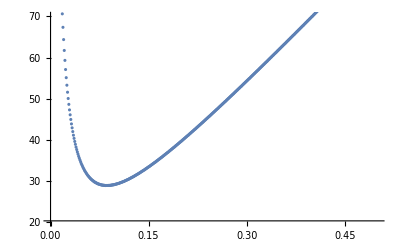

```mathematica
ListPlot[Table[{a,DiffPlot5000[3000000,4,2000/6,1000,a,0.001]},{a,0,0.5,0.001}],PlotRange->{{0,0.5},{20,70}},PlotLegends->"Expressions"]
```

```mathematica
(*以上为N=5000时Renyi熵的导数*)
```

General::munfl: Exp[-48401.7-7853.98 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-48382.4-7850.84 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-48363.-7847.7 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 ⅇ^ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

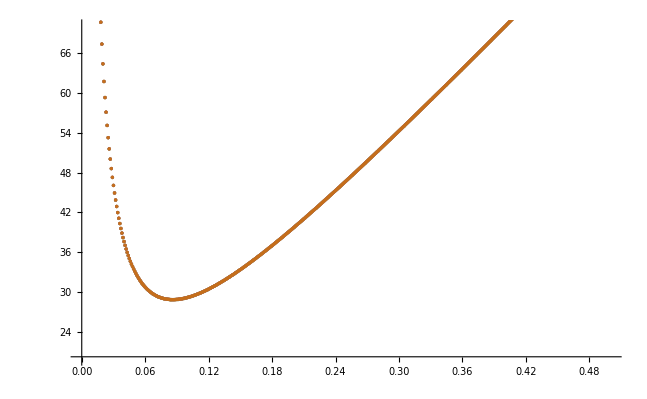

```mathematica
ListPlot[{Table[{a,DiffPlot5000[3000000,4,2000/6,1000,a,0.001]},{a,0,0.5,0.001}],Table[{a,DiffPlot1000[3000000,4,2000/6,1000,a,0.001]},{a,0,0.5,0.001}],Table[{a,DiffPlot1500[3000000,4,2000/6,1000,a,0.001]},{a,0,0.5,0.001}],Table[{a,DiffPlot[3000000,4,2000/6,100,a,0.001]},{a,0,0.5,0.001}],Table[{a,DiffPlot[3000000,4,2000/6,50,a,0.001]},{a,0,0.5,0.001}],Table[{a,DiffPlot[3000000,4,2000/6,10,a,0.001]},{a,0,0.5,0.001}]},PlotRange->{{0,0.5},{20,70}},PlotLegends->"Expressions"]
```

```mathematica
(*上图为N=10,50,100,1000,1500,5000时的Renyi熵的导数图*)
```

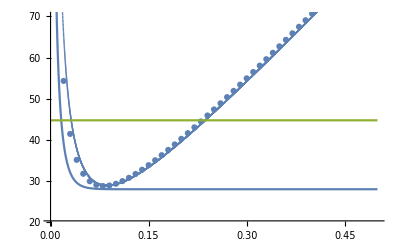

```mathematica
(*上图为散点为N=100时的导数，细线为N=10的导数*)
```

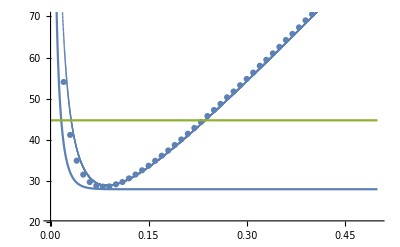

```mathematica
(*上图为散点为N=1000时的导数，细线为N=10的导数*)
```